# QNM Results

```mathematica
$PlotTheme = "Classic"
```

Classic

All data should be found in Output/Important

## Setup

```mathematica
ScrollingOptions->{"VerticalScrollRange"->FitAll}
```

ScrollingOptions→{VerticalScrollRange→FitAll}

```mathematica
x1 = 0;
x2 = 1;
Clear[m,b]
m = 2/(x2 - x1)
Solve[m x1 + b == -1,b];
b = b/.%[[1]]
Num =240(*240*);
T[n_,u_]:=ChebyshevT[n,m u + b]
dT[n_,u_]:=m*Derivative[0,1][ChebyshevT][n,m u+b]
d2T[n_,u_]:=m^2* Derivative[0,2][ChebyshevT][n,m u+b]
c[j_]:= Piecewise[{{2,Abs[j]==Num},{2,j==0},{1,Abs[j]<Num}}]
p[j_]:= Piecewise[{{2,j==0},{2,j==Num},{1,0<j<Num}}]
Gridlist = ConstantArray[0,{Num+1}];
Gridlist =N [1/m(Cos[π#/Num]-b)&/@Range[0,Num],15]
Card[j_,u_]:= If[u==Gridlist[[j+1]],1,(-1)^(j+1)(1-(m u + b)^2)/(c[j] Num^2((m u+b)-(m Gridlist[[j+1]]+b)))1/m dT[Num,u]]
dCardM  =
 ConstantArray[0,{Num+1,Num+1}];
Module[
{i,j},
For[i=1,i≤Num+1,i++,For[j=1,j≤Num+1 ,j++,dCardM[[i,j]]=(-1)^(i+j)(m)p[i-1]/(p[j-1](m Gridlist[[i]]-m Gridlist[[j]]))]];
For[i=2,i≤Num,i++, dCardM[[i,i]]=-(m)(m*Gridlist[[i]]+b)/(2(1-(m*Gridlist[[i]]+b)^2))];
]
dCardM[[1,1]] =(m) (1+2 Num^2)/6;
dCardM[[Num+1,Num+1]] = -dCardM[[1,1]];
d2CardM = dCardM.dCardM;
```

2

-1

{1.,0.999957163787004,0.999828662487779,0.999614518120361,0.999314767377287,0.998929461619302,0.998458666866564,0.997902463787331,0.997260947684137,0.996534228477463,0.995722430686905,0.994825693409835,0.993844170297569,0.992778029529039,0.991627453781977,0.990392640201615,0.989073800366903,0.987671160254256,0.986184960198838,0.984615454853377,0.982962913144534,0.981227618226824,0.979409867434097,0.977509972228593,0.975528258147577,0.973465064747553,0.971320745546089,0.969095667961242,0.966790213248601,0.964404776435962,0.961939766255643,0.959395605074449,0.9567727288213,0.954071586912541,0.95129264217493,0.948436370766344,0.945503262094184,0.942493818731521,0.939408556330983,0.936248003536399,0.933012701892219,0.929703205750726,0.926320082177046,0.922863910851987,0.919335283972712,0.915734806151273,0.912063094311008,0.908320777580839,0.904508497187474,0.90062690634553,0.896676670145618,0.892658465440372,0.888572980728485,0.88442091603673,0.880202982800015,0.875919903739489,0.871572412738697,0.867161254717843,0.862687185506144,0.858150971712327,0.853553390593274,0.84889522992084,0.844177287846877,0.839400372766471,0.834565303179429,0.829672907550034,0.824724024165092,0.819719500990292,0.814660195524919,0.809546974654917,0.80438071450436,0.79916230028533,0.793892626146237,0.788572595018617,0.783203118462416,0.777785116509801,0.772319517507514,0.766807257957806,0.761249282357974,0.755646543038526,0.75,0.744310620748477,0.738579380129804,0.732807260162556,0.726995249869773,0.721144345109501,0.715255548404148,0.709329868768714,0.7033683215379,0.697371928192134,0.691341716182545,0.685278718754918,0.67918397477265,0.673058528538746,0.666903429616885,0.660719732651581,0.654508497187474,0.648270787487785,0.642007672351961,0.635720224932537,0.62940952255126,0.623076646514497,0.616722681927953,0.610348717510751,0.60395584540888,0.597545161008064,0.591117762746074,0.584674751924512,0.578217232520115,0.57174631099559,0.565263096110026,0.558768698728919,0.552264231633827,0.545750809331701,0.539229547863922,0.532701564615072,0.526167978121472,0.519629907879534,0.513088474153937,0.506544797785672,0.5,0.493455202214328,0.486911525846063,0.480370092120466,0.473832021878528,0.467298435384928,0.460770452136078,0.454249190668299,0.447735768366173,0.441231301271081,0.434736903889974,0.42825368900441,0.421782767479885,0.415325248075488,0.408882237253926,0.402454838991936,0.39604415459112,0.389651282489249,0.383277318072047,0.376923353485503,0.37059047744874,0.364279775067463,0.357992327648039,0.351729212512215,0.345491502812526,0.339280267348419,0.333096570383115,0.326941471461254,0.32081602522735,0.314721281245082,0.308658283817455,0.302628071807866,0.2966316784621,0.290670131231286,0.284744451595852,0.278855654890499,0.273004750130227,0.267192739837444,0.261420619870196,0.255689379251523,0.25,0.244353456961474,0.238750717642026,0.233192742042194,0.227680482492486,0.222214883490199,0.216796881537584,0.211427404981383,0.206107373853763,0.20083769971467,0.19561928549564,0.190453025345083,0.185339804475081,0.180280499009708,0.175275975834908,0.170327092449966,0.165434696820571,0.160599627233529,0.155822712153123,0.15110477007916,0.146446609406726,0.141849028287673,0.137312814493856,0.132838745282157,0.128427587261303,0.124080096260511,0.119797017199985,0.11557908396327,0.111427019271515,0.107341534559628,0.103323329854382,0.0993730936544697,0.0954915028125263,0.0916792224191605,0.0879369056889922,0.0842651938487274,0.080664716027288,0.0771360891480134,0.0736799178229539,0.0702967942492737,0.0669872981077807,0.0637519964636014,0.0605914436690173,0.0575061812684791,0.0544967379058161,0.0515636292336558,0.0487073578250697,0.0459284130874594,0.0432272711786996,0.0406043949255509,0.0380602337443566,0.0355952235640379,0.0332097867513991,0.0309043320387579,0.0286792544539108,0.0265349352524472,0.0244717418524232,0.0224900277714067,0.0205901325659035,0.0187723817731764,0.0170370868554659,0.0153845451466228,0.0138150398011617,0.0123288397457437,0.0109261996330972,0.00960735979838478,0.00837254621802271,0.00722197047096114,0.00615582970243114,0.00517430659016489,0.00427756931309479,0.00346577152253685,0.00273905231586333,0.00209753621266914,0.00154133313343601,0.00107053838069825,0.000685232622713063,0.000385481879638533,0.00017133751222136,0.0000428362129964839,0}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/(2 SuperscriptBox[x, 2]) + 1/x*radiallamblist[["<>ToString[i+1]<>"]]+1/2(radiallamblist[["<>ToString[i+1]<>"]])^2+ x*"<>"sigmadotsubscale"<>ToString[i]<>"[x]"]
,{i,0,15}];
```

## GuassianR, MAG black brane QNMs

## GuassianR, fxy = 0.1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-07wid0.5uave0.25a2-1.0f30.0fxy0.1TS0.001amp20.0wid20.6uave20.6NS30000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-07wid0.5uave0.25a2-1.0f30.0fxy0.1TS0.001amp20.0wid20.6uave20.6NS30000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

0.1

```mathematica
b4list[[-1]]
```

0.000829996

```mathematica
Max[Abs[lambshiftlist]]
```

2.18418×10^-12

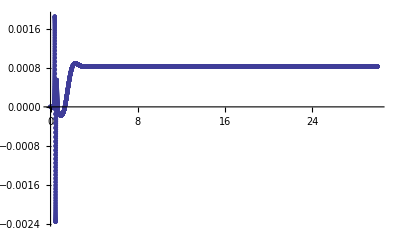

```mathematica
ListPlot[(b4plotlist),PlotRange->All]
```

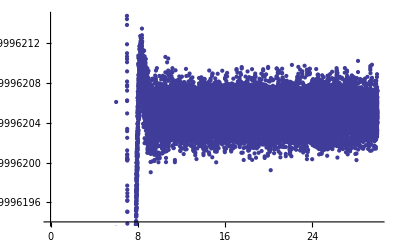

```mathematica
ListPlot[(b4plotlist)]
```

```mathematica
b4plotlist[[8000,2]]
```

0.000829996

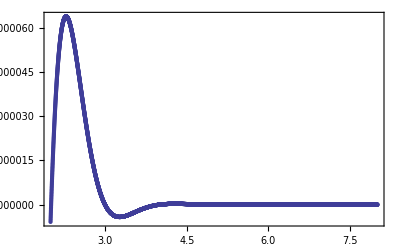

```mathematica
Show[ListPlot[b4plotlistshift[[2001;;8000]]],Plot[Normal[nlm],{x,2,8}],Frame->True,PlotRange->All]
```

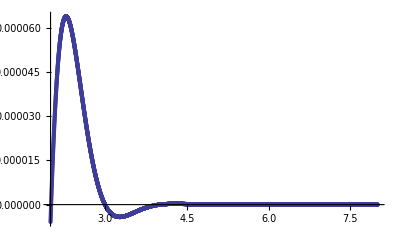

```mathematica
ListPlot[b4plotlistshift[[2001;;8000]],PlotRange->All]
```

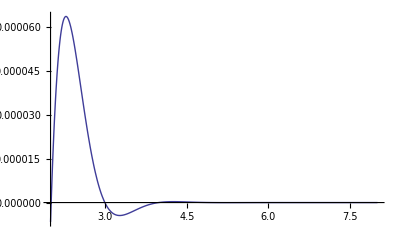

```mathematica
Plot[Normal[nlm],{x,2,8},PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.317781

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

```mathematica
0.75/0.31778069851986424^4
```

73.5447

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.06359×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.1416

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.24834

### QNM1 = {}

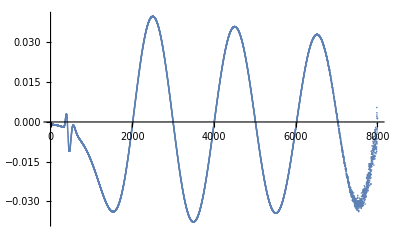

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 30.}}, <>]

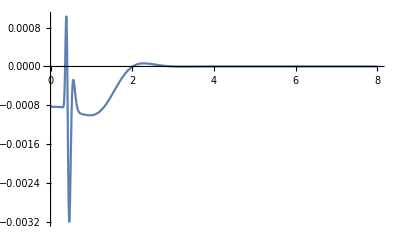

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{2.01061,2.9987,4.00555,5.01344,6.02085,7.02847}

{0.988087,1.00685,1.0079,1.00741,1.00763}

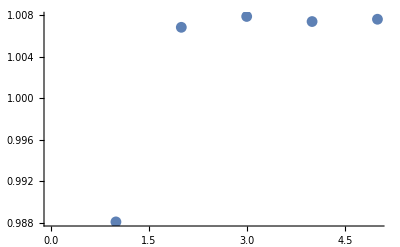

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 2;
endroot = Length[templist];
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.01489

```mathematica
μ1 = 2π/λ1
```

3.11838

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.00184268,-0.00139653,0.000121621,-0.000565947}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00119173

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.479943

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.49664

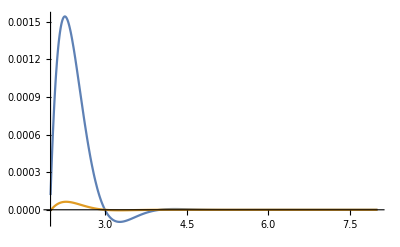

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→0.171175
ν→-2.5241) | (A→0.171175
ν→-2.5241) | (A→0.171175
ν→-2.5241) | (A→0.171175
ν→-2.5241) | (A→0.171175
ν→-2.5241)
(A→0.210081
ν→-2.60596) | (A→0.210081
ν→-2.60596) | (A→0.210081
ν→-2.60596) | (A→0.210081
ν→-2.60596) | (A→0.210081
ν→-2.60596)
(A→0.246004
ν→-2.66773) | (A→0.246004
ν→-2.66773) | (A→0.246004
ν→-2.66773) | (A→0.246004
ν→-2.66773) | (A→0.246004
ν→-2.66773)
(A→0.277384
ν→-2.7134) | (A→0.277384
ν→-2.7134) | (A→0.277384
ν→-2.7134) | (A→0.277384
ν→-2.7134) | (A→0.277384
ν→-2.7134)
(A→0.302002
ν→-2.74457) | (A→0.302002
ν→-2.74457) | (A→0.302002
ν→-2.74457) | (A→0.302002
ν→-2.74457) | (A→0.302002
ν→-2.74457)
(A→0.317669
ν→-2.76221) | (A→0.317669
ν→-2.76221) | (A→0.317669
ν→-2.76221) | (A→0.317669
ν→-2.76221) | (A→0.317669
ν→-2.76221)
(A→0.325624
ν→-2.77029) | (A→0.325624
ν→-2.77029) | (A→0.325624
ν→-2.77029) | (A→0.325624
ν→-2.77029) | (A→0.325624
ν→-2.77029)
(A→0.329002
ν→-2.77345) | (A→0.329002
ν→-2.77345) | (A→0.329002
ν→-2.77345) | (A→0.329002
ν→-2.77345) | (A→0.329002
ν→-2.77345)
(A→0.325406
ν→-2.77022) | (A→0.325406
ν→-2.77022) | (A→0.325406
ν→-2.77022) | (A→0.325406
ν→-2.77022) | (A→0.325406
ν→-2.77022)
(A→0.319903
ν→-2.76521) | (A→0.319903
ν→-2.76521) | (A→0.319903
ν→-2.76521) | (A→0.319903
ν→-2.76521) | (A→0.319903
ν→-2.76521))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 2;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

32

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.5241

```mathematica
Table[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]
```

{{-2.60596,-2.60596,-2.60596,-2.60596},{-2.66773,-2.66773,-2.66773,-2.66773},{-2.7134,-2.7134,-2.7134,-2.7134},{-2.74457,-2.74457,-2.74457,-2.74457},{-2.76221,-2.76221,-2.76221,-2.76221},{-2.77029,-2.77029,-2.77029,-2.77029},{-2.77345,-2.77345,-2.77345,-2.77345},{-2.77022,-2.77022,-2.77022,-2.77022}}

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.72598

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0567756

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

1.21828×10^-6

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.11838+0.00119173 x,-2.72598+0.0567756 x}

```mathematica
fxy/T^2
```

0.99025

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

72.9802

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.35738+0.00128306 x,-2.9349+0.061127 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.12357,-2.73052}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.11838-2.72598 ⅈ}

{3.35092-2.92925 ⅈ}

{3.35738-2.9349 ⅈ}

{3.12357-2.73052 ⅈ}

{3.11838-2.72598 ⅈ}

```mathematica
g=1
```

1

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-1.12993

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

24.1633

### Testing Accuracy of Mode

```mathematica
ListPlot[b4plotlist]
```

-Graphics-

```mathematica
nlm=NonlinearModelFit[b4plotlist[[1501;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2001;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2501;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3001;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3501;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4001;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4501;;30000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.25583 | 0.000452795 | 7190.52 | 1.604416536×10^-46435
ν | -2.52312 | 0.000260125 | -9699.64 | 3.315158539×10^-50138
ϕ | 1.31695 | 0.000879183 | 1497.92 | 2.25943488×10^-27097
C0 | 0.00083002 | 1.60842×10^-9 | 516046. | 8.697885744×10^-99317
A | -0.0256357 | 0.0000105435 | -2431.42 | 1.457803462×10^-33043

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.18985 | 0.000159063 | 20054. | 1.40604576×10^-58195
ν | -2.7223 | 0.000283301 | -9609.19 | 3.380301897×10^-49252
ϕ | 1.44738 | 0.000325566 | 4445.74 | 7.579678449×10^-39888
C0 | 0.000829998 | 2.57869×10^-10 | 3.21868×10^6 | 1.807193225×10^-119937
A | -0.0415117 | 0.0000286099 | -1450.96 | 7.263198903×10^-26346

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15703 | 0.000143928 | 21934.8 | 3.263305729×10^-58334
ν | -2.76001 | 0.0000785695 | -35128.2 | 2.385185222×10^-63957
ϕ | 1.54259 | 0.000421517 | 3659.62 | 2.482669707×10^-36963
C0 | 0.000829996 | 3.25502×10^-11 | 2.5499×10^7 | 9.767912991×10^-142617
A | -0.0458214 | 9.12362×10^-6 | -5022.28 | 3.448893655×10^-40737

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.12564 | 0.0000305328 | 102370. | 2.038771376×10^-75441
ν | -2.76662 | 0.0000561198 | -49298.6 | 6.439332521×10^-66875
ϕ | 1.63896 | 0.0000924496 | 17728.2 | 5.368062601×10^-54885
C0 | 0.000829996 | 3.19233×10^-12 | 2.59997×10^8 | 7.20310398×10^-167354
A | -0.0468767 | 9.02271×10^-6 | -5195.41 | 8.229073648×10^-40501

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.11699 | 0.0000169215 | 184202. | 3.614624715×10^-80911
ν | -2.75187 | 9.26757×10^-6 | -296936. | 2.287658807×10^-86405
ϕ | 1.67293 | 0.000066521 | 25148.9 | 3.528626947×10^-57999
C0 | 0.000829996 | 2.46962×10^-13 | 3.36083×10^9 | 2.317532924×10^-193810
A | -0.0444829 | 1.45423×10^-6 | -30588.5 | 3.397513356×10^-60252

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.12202 | 2.57132×10^-6 | 1.21417×10^6 | 2.334815963×10^-100781
ν | -2.74738 | 4.62294×10^-6 | -594292. | 1.268883359×10^-92715
ϕ | 1.65257 | 0.0000103593 | 159526. | 3.933135341×10^-77868
C0 | 0.000829996 | 1.73719×10^-14 | 4.77782×10^10 | 4.447001408×10^-220227
A | -0.0436069 | 8.93464×10^-7 | -48806.6 | 1.461240999×10^-64497

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.12367 | 9.79375×10^-6 | 318945. | 5.645821891×10^-84149
ν | -2.74854 | 5.52791×10^-6 | -497211. | 4.695928095×10^-89065
ϕ | 1.64446 | 0.0000483115 | 34038.6 | 1.693412561×10^-59374
C0 | 0.000829996 | 9.46158×10^-15 | 8.77228×10^10 | 2.171389516×10^-222826
A | -0.0438371 | 1.09762×10^-6 | -39938.2 | 3.121537377×10^-61144

```mathematica
nlm=NonlinearModelFit[b4plotlist[[2500;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;9500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;9000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;8500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;7500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;7000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,0.04}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15777 | 0.000278077 | 11355.7 | 6.9046862547×10^-15878
ν | -2.76042 | 0.000155666 | -17733. | 8.3829689805×10^-17329
ϕ | 1.54033 | 0.000815868 | 1887.96 | 3.6427726124×10^-10040
C0 | 0.000829995 | 1.27627×10^-10 | 6.50328×10^6 | 3.8510793214×10^-36551
A | -0.045867 | 0.0000180732 | -2537.85 | 1.1318925985×10^-11001

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15782 | 0.000288028 | 10963.6 | 4.5613925988×10^-14817
ν | -2.76047 | 0.000161616 | -17080.4 | 4.6654564794×10^-16164
ϕ | 1.54015 | 0.000845248 | 1822.12 | 1.1543155257×10^-9367
C0 | 0.000829994 | 1.37615×10^-10 | 6.03129×10^6 | 3.2714026771×10^-33989
A | -0.0458728 | 0.0000187646 | -2444.64 | 3.3956750424×10^-10259

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15789 | 0.000299133 | 10556.8 | 3.3096329114×10^-13756
ν | -2.76053 | 0.000168313 | -16401.2 | 4.0663250016×10^-14999
ϕ | 1.53993 | 0.000878066 | 1753.78 | 4.3193106554×10^-8695
C0 | 0.000829994 | 1.49305×10^-10 | 5.55905×10^6 | 8.8659940824×10^-31435
A | -0.0458797 | 0.000019543 | -2347.63 | 1.5869949926×10^-9516

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15798 | 0.000311637 | 10133.5 | 2.7120298385×10^-12695
ν | -2.76061 | 0.00017593 | -15691.5 | 6.3416620227×10^-13834
ϕ | 1.53967 | 0.000915054 | 1682.6 | 2.0067924682×10^-8022
C0 | 0.000829994 | 1.63177×10^-10 | 5.08648×10^6 | 2.3101054316×10^-28888
A | -0.0458881 | 0.0000204285 | -2246.28 | 1.3184589845×10^-8773

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15808 | 0.000325862 | 9691.46 | 2.6058784122×10^-11634
ν | -2.7607 | 0.000184701 | -14946.8 | 2.1385624667×10^-12668
ϕ | 1.53935 | 0.000957185 | 1608.21 | 1.2396441003×10^-7349
C0 | 0.000829994 | 1.79906×10^-10 | 4.61349×10^6 | 1.4883436367×10^-26350
A | -0.0458985 | 0.0000214486 | -2139.93 | 2.3505631665×10^-8030

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15821 | 0.000342245 | 9227.91 | 3.0991908722×10^-10573
ν | -2.76081 | 0.000194957 | -14161.1 | 2.0117551808×10^-11502
ϕ | 1.53894 | 0.00100579 | 1530.09 | 1.1253431157×10^-6676
C0 | 0.000829994 | 2.00483×10^-10 | 4.13996×10^6 | 4.9934040139×10^-23822
A | -0.0459116 | 0.0000226418 | -2027.74 | 1.158408794×10^-7286

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.15838 | 0.000361398 | 8739.34 | 4.8284559474×10^-9512
ν | -2.76096 | 0.000207178 | -13326.5 | 7.594109228×10^-10336
ϕ | 1.53841 | 0.00106272 | 1447.61 | 1.7564605342×10^-6003
C0 | 0.000829993 | 2.26421×10^-10 | 3.66571×10^6 | 1.4910534252×10^-21303
A | -0.0459289 | 0.0000240644 | -1908.58 | 2.2469448107×10^-6542

```mathematica
Table[{b4plotlist[[29901+i,1]],b4plotlist[[29901+i,2]]-b4plotlist[[-1,2]]},{i,0,100}]
```

{{29.9,5.27522×10^-13},{29.901,1.67032×10^-12},{29.902,1.75446×10^-12},{29.903,1.63569×10^-12},{29.904,3.06309×10^-12},{29.905,2.73936×10^-12},{29.906,6.30829×10^-13},{29.907,-6.3298×10^-13},{29.908,-5.55195×10^-13},{29.909,2.79328×10^-12},{29.91,2.97132×10^-12},{29.911,3.34689×10^-12},{29.912,3.23055×10^-12},{29.913,3.24542×10^-12},{29.914,3.16477×10^-12},{29.915,3.06707×10^-12},{29.916,1.48109×10^-12},{29.917,4.71831×10^-13},{29.918,-9.99617×10^-14},{29.919,-3.99167×10^-13},{29.92,3.33414×10^-13},{29.921,1.04999×10^-12},{29.922,1.41873×10^-12},{29.923,1.45749×10^-12},{29.924,1.15762×10^-12},{29.925,8.14779×10^-13},{29.926,1.19355×10^-12},{29.927,1.93087×10^-12},{29.928,1.68653×10^-12},{29.929,1.44727×10^-12},{29.93,-2.86368×10^-13},{29.931,-1.22835×10^-12},{29.932,1.22077×10^-12},{29.933,6.38864×10^-13},{29.934,-1.39903×10^-12},{29.935,-1.03029×10^-12},{29.936,-5.12909×10^-13},{29.937,1.49325×10^-13},{29.938,2.4887×10^-13},{29.939,1.67803×10^-12},{29.94,1.66855×10^-12},{29.941,2.70532×10^-12},{29.942,1.93492×10^-12},{29.943,1.37976×10^-12},{29.944,-1.64299×10^-13},{29.945,-4.39773×10^-13},{29.946,1.87225×10^-12},{29.947,2.37546×10^-12},{29.948,1.55442×10^-12},{29.949,1.78778×10^-12},{29.95,2.92277×10^-12},{29.951,4.46464×10^-12},{29.952,1.74311×10^-12},{29.953,-1.55928×10^-12},{29.954,-7.0019×10^-13},{29.955,1.22413×10^-12},{29.956,1.32616×10^-13},{29.957,4.57551×10^-14},{29.958,-5.20181×10^-13},{29.959,-6.51201×10^-13},{29.96,1.14729×10^-12},{29.961,2.39614×10^-12},{29.962,4.74605×10^-12},{29.963,3.44941×10^-12},{29.964,8.4327×10^-13},{29.965,-1.47729×10^-12},{29.966,-1.25983×10^-13},{29.967,9.60232×10^-13},{29.968,-3.31388×10^-13},{29.969,2.35006×10^-13},{29.97,3.27197×10^-13},{29.971,-7.49262×10^-14},{29.972,-8.27755×10^-13},{29.973,-1.24017×10^-12},{29.974,-8.69832×10^-13},{29.975,-1.0334×10^-12},{29.976,4.11601×10^-13},{29.977,7.73465×10^-13},{29.978,-1.88558×10^-13},{29.979,2.06453×10^-12},{29.98,1.95217×10^-12},{29.981,2.31473×10^-12},{29.982,1.51158×10^-12},{29.983,4.02789×10^-13},{29.984,8.62699×10^-13},{29.985,2.46808×10^-12},{29.986,3.1657×10^-12},{29.987,3.06717×10^-12},{29.988,3.0457×10^-12},{29.989,3.04475×10^-12},{29.99,1.06219×10^-12},{29.991,1.77051×10^-12},{29.992,1.23174×10^-12},{29.993,5.19099×10^-13},{29.994,8.21912×10^-13},{29.995,7.21451×10^-13},{29.996,1.00851×10^-12},{29.997,2.69451×10^-13},{29.998,-1.57221×10^-13},{29.999,5.4369×10^-13},{30.,0.}}

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
b4plotlist[[2001]]
```

{2.,0.00082413}

```mathematica
tlist[[2000]]
```

1.999

```mathematica
Plot[b4plotlist[[i,
```

```mathematica
b4plotlist[[2001,2]]-b4plotlist[[-1,2]]
b4plotlist[[8001,2]]-b4plotlist[[-1,2]]
b4plotlist[[20001,2]]-b4plotlist[[-1,2]]
```

-6.43499×10^-6

7.7624×10^-13

1.29811×10^-12

```mathematica
LeadQNMplotlist = Table[{tlist[[2001+i]],(b4plotlist[[2001,2]]-b4plotlist[[-1,2]])ⅇ^(-2.7259778940581847tlist[[2001+i]])},{i,0,28000}];
```

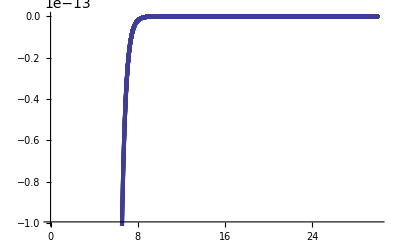

```mathematica
ListPlot[LeadQNMplotlist]
```

```mathematica
Length[LeadQNMplotlist]
```

28001

```mathematica
diffplotlist = Table[{b4plotlist[[2001+i,1]],(b4plotlist[[2001+i,2]]-b4plotlist[[-1,2]])-LeadQNMplotlist[[1+i,2]]},{i,0,28000}];
```

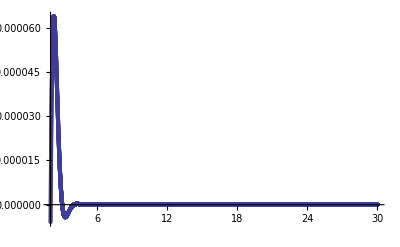

```mathematica
ListPlot[diffplotlist,PlotRange->All]
```

### QNM1 = TEST HIGH

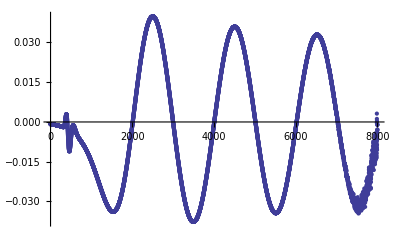

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- (b4list[[-1]]+10^-12)),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-(b4list[[-1]]+10^-12)},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,30.}},<>]

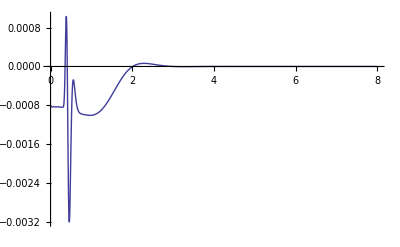

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{2.01061,2.9987,4.00555,5.01344,6.02092,7.02786}

{0.988087,1.00685,1.00789,1.00749,1.00694}

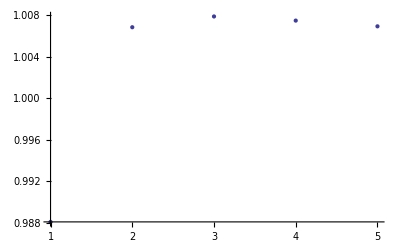

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 2;
endroot = Length[templist];
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.01458

```mathematica
μ1 = 2π/λ1
```

3.11885

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.00136752,-0.00184779,-0.000613786,0.00109625}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00130986

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.480624

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.499

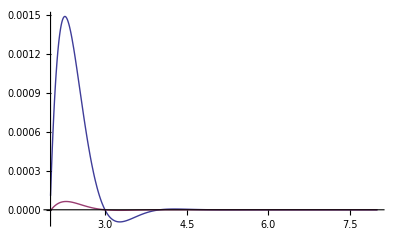

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→0.178911
ν→-2.52883) | (A→0.178911
ν→-2.52883) | (A→0.178911
ν→-2.52883) | (A→0.178911
ν→-2.52883) | (A→0.178911
ν→-2.52883)
(A→0.218896
ν→-2.60946) | (A→0.218896
ν→-2.60946) | (A→0.218896
ν→-2.60946) | (A→0.218896
ν→-2.60946) | (A→0.218896
ν→-2.60946)
(A→0.255741
ν→-2.67035) | (A→0.255741
ν→-2.67035) | (A→0.255741
ν→-2.67035) | (A→0.255741
ν→-2.67035) | (A→0.255741
ν→-2.67035)
(A→0.287711
ν→-2.71516) | (A→0.287711
ν→-2.71516) | (A→0.287711
ν→-2.71516) | (A→0.287711
ν→-2.71516) | (A→0.287711
ν→-2.71516)
(A→0.312322
ν→-2.74525) | (A→0.312322
ν→-2.74525) | (A→0.312322
ν→-2.74525) | (A→0.312322
ν→-2.74525) | (A→0.312322
ν→-2.74525)
(A→0.327251
ν→-2.76155) | (A→0.327251
ν→-2.76155) | (A→0.327251
ν→-2.76155) | (A→0.327251
ν→-2.76155) | (A→0.327251
ν→-2.76155)
(A→0.33393
ν→-2.76815) | (A→0.33393
ν→-2.76815) | (A→0.33393
ν→-2.76815) | (A→0.33393
ν→-2.76815) | (A→0.33393
ν→-2.76815)
(A→0.335806
ν→-2.76988) | (A→0.335806
ν→-2.76988) | (A→0.335806
ν→-2.76988) | (A→0.335806
ν→-2.76988) | (A→0.335806
ν→-2.76988)
(A→0.334933
ν→-2.76911) | (A→0.334933
ν→-2.76911) | (A→0.334933
ν→-2.76911) | (A→0.334933
ν→-2.76911) | (A→0.334933
ν→-2.76911)
(A→0.335812
ν→-2.76988) | (A→0.335812
ν→-2.76988) | (A→0.335812
ν→-2.76988) | (A→0.335813
ν→-2.76988) | (A→0.335813
ν→-2.76988))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 2;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

32

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.52883

```mathematica
Table[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]
```

{{-2.60946,-2.60946,-2.60946,-2.60946},{-2.67035,-2.67035,-2.67035,-2.67035},{-2.71516,-2.71516,-2.71516,-2.71516},{-2.74525,-2.74525,-2.74525,-2.74525},{-2.76155,-2.76155,-2.76155,-2.76155},{-2.76815,-2.76815,-2.76815,-2.76815},{-2.76988,-2.76988,-2.76988,-2.76988},{-2.76911,-2.76911,-2.76911,-2.76911}}

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.72611

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0547621

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

1.20066×10^-6

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.11885+0.00130986 x,-2.72611+0.0547621 x}

```mathematica
fxy/T^2
```

0.99025

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

72.9802

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.35789+0.00141025 x,-2.93505+0.0589591 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.12405,-2.73065}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.11885-2.72611 ⅈ}

{3.35142-2.9294 ⅈ}

{3.35789-2.93505 ⅈ}

{3.12405-2.73065 ⅈ}

{3.11886-2.72612 ⅈ}

```mathematica
g=1
```

1

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-1.12993

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

24.1633

### QNM1 = TEST LOW

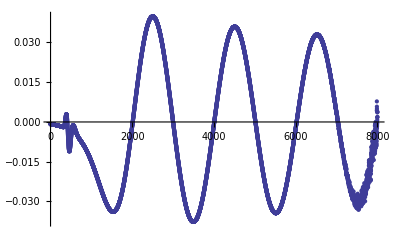

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- (b4list[[-1]]-10^-12)),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-(b4list[[-1]]-10^-12)},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,30.}},<>]

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.2}
```

{2,3,3.5,4.5,5.5,6.2}

{2.01061,2.9987,4.00555,5.01345,6.02077,6.02077}

{0.988087,1.00685,1.0079,1.00732,0.}

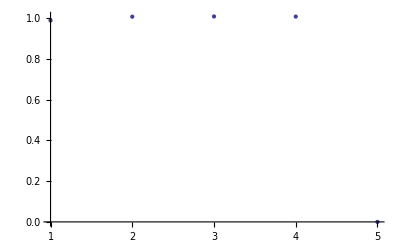

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 2;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.01472

```mathematica
μ1 = 2π/λ1
```

3.11865

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.00157578,-0.00168734,0.000113276}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00133454

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.48034

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.49801

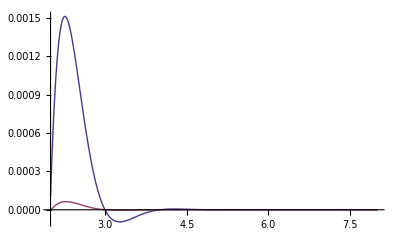

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→0.175626
ν→-2.5269) | (A→0.175626
ν→-2.5269) | (A→0.175626
ν→-2.5269) | (A→0.175626
ν→-2.5269) | (A→0.175626
ν→-2.5269)
(A→0.215151
ν→-2.60804) | (A→0.215151
ν→-2.60804) | (A→0.215151
ν→-2.60804) | (A→0.215151
ν→-2.60804) | (A→0.215151
ν→-2.60804)
(A→0.251602
ν→-2.66929) | (A→0.251602
ν→-2.66929) | (A→0.251602
ν→-2.66929) | (A→0.251602
ν→-2.66929) | (A→0.251602
ν→-2.66929)
(A→0.283316
ν→-2.71444) | (A→0.283316
ν→-2.71444) | (A→0.283316
ν→-2.71444) | (A→0.283316
ν→-2.71444) | (A→0.283316
ν→-2.71444)
(A→0.307918
ν→-2.74497) | (A→0.307918
ν→-2.74497) | (A→0.307918
ν→-2.74497) | (A→0.307918
ν→-2.74497) | (A→0.307918
ν→-2.74497)
(A→0.32314
ν→-2.76181) | (A→0.32314
ν→-2.76181) | (A→0.32314
ν→-2.76181) | (A→0.32314
ν→-2.76181) | (A→0.32314
ν→-2.76181)
(A→0.330334
ν→-2.76901) | (A→0.330334
ν→-2.76901) | (A→0.330334
ν→-2.76901) | (A→0.330334
ν→-2.76901) | (A→0.330334
ν→-2.76901)
(A→0.332817
ν→-2.77131) | (A→0.332817
ν→-2.77131) | (A→0.332817
ν→-2.77131) | (A→0.332817
ν→-2.77131) | (A→0.332817
ν→-2.77131)
(A→0.33086
ν→-2.76957) | (A→0.33086
ν→-2.76957) | (A→0.330861
ν→-2.76957) | (A→0.330861
ν→-2.76957) | (A→0.330861
ν→-2.76957)
(A→0.329138
ν→-2.76804) | (A→0.329138
ν→-2.76804) | (A→0.329138
ν→-2.76804) | (A→0.329138
ν→-2.76804) | (A→0.329138
ν→-2.76804))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 2;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

32

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.5269

```mathematica
Table[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]
```

{{-2.60804,-2.60804,-2.60804,-2.60804},{-2.66929,-2.66929,-2.66929,-2.66929},{-2.71444,-2.71444,-2.71444,-2.71444},{-2.74497,-2.74497,-2.74497,-2.74497},{-2.76181,-2.76181,-2.76181,-2.76181},{-2.76901,-2.76901,-2.76901,-2.76901},{-2.77131,-2.77131,-2.77131,-2.77131},{-2.76957,-2.76957,-2.76957,-2.76957}}

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.72605

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0555751

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

1.20792×10^-6

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.11865+0.00133454 x,-2.72605+0.0555751 x}

```mathematica
fxy/T^2
```

0.99025

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

72.9802

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.35767+0.00143682 x,-2.93498+0.0598345 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.12384,-2.73059}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.11865-2.72605 ⅈ}

{3.3512-2.92934 ⅈ}

{3.35767-2.93498 ⅈ}

{3.12384-2.73059 ⅈ}

{3.11865-2.72606 ⅈ}

```mathematica
g=1
```

1

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-1.12993

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

24.1633

## GuassianR, fxy = 0.5

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS10000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS10000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

0.5

```mathematica
b4list[[-1]]
```

0.0187773

```mathematica
Max[Abs[lambshiftlist]]
```

2.2225×10^-12

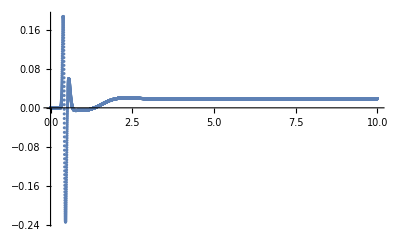

```mathematica
ListPlot[(b4plotlist),PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.305869

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000181783

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14659

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.212445

### QNM1 = {}

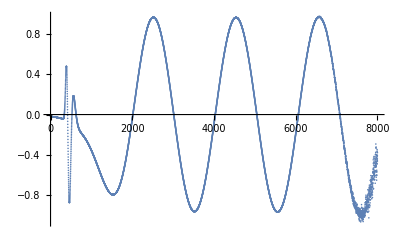

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 10.}}, <>]

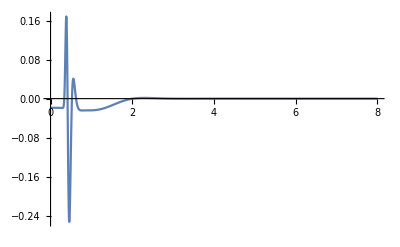

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

InterpolatingFunction::dmval: Input value {11.6541} lies outside the range of data in the interpolating function. Extrapolation will be used.

{2.0139,3.01456,4.03,5.04674,6.06311,7.072}

{1.00067,1.01544,1.01674,1.01636,1.00889}

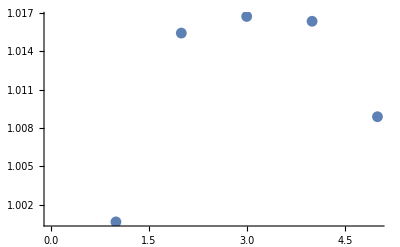

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 2;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.03236

```mathematica
μ1 = 2π/λ1
```

3.09157

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.00225929,-0.00169958,-0.000557024}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00166366

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.473926

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.46517

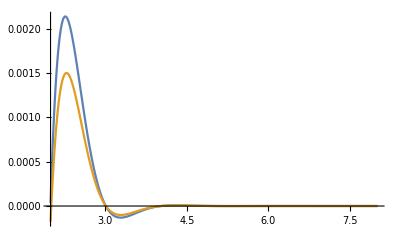

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→2.77155
ν→-2.50431) | (A→2.77155
ν→-2.50431) | (A→2.77155
ν→-2.50431) | (A→2.77155
ν→-2.50431) | (A→2.77155
ν→-2.5043)
(A→3.27998
ν→-2.57144) | (A→3.27998
ν→-2.57144) | (A→3.27998
ν→-2.57144) | (A→3.27998
ν→-2.57144) | (A→3.27998
ν→-2.57144)
(A→3.7468
ν→-2.62337) | (A→3.7468
ν→-2.62337) | (A→3.7468
ν→-2.62337) | (A→3.7468
ν→-2.62337) | (A→3.7468
ν→-2.62337)
(A→4.15664
ν→-2.66276) | (A→4.15664
ν→-2.66276) | (A→4.15664
ν→-2.66276) | (A→4.15664
ν→-2.66276) | (A→4.15664
ν→-2.66276)
(A→4.48652
ν→-2.69071) | (A→4.48652
ν→-2.69071) | (A→4.48652
ν→-2.69071) | (A→4.48652
ν→-2.69071) | (A→4.48652
ν→-2.69071)
(A→4.70833
ν→-2.70753) | (A→4.70833
ν→-2.70753) | (A→4.70833
ν→-2.70753) | (A→4.70833
ν→-2.70753) | (A→4.70833
ν→-2.70753)
(A→4.83107
ν→-2.71594) | (A→4.83107
ν→-2.71594) | (A→4.83107
ν→-2.71594) | (A→4.83107
ν→-2.71594) | (A→4.83107
ν→-2.71594)
(A→4.89421
ν→-2.71992) | (A→4.89421
ν→-2.71992) | (A→4.89421
ν→-2.71992) | (A→4.89421
ν→-2.71992) | (A→4.89421
ν→-2.71992)
(A→4.88213
ν→-2.7192) | (A→4.88213
ν→-2.7192) | (A→4.88213
ν→-2.7192) | (A→4.88213
ν→-2.7192) | (A→4.88213
ν→-2.7192)
(A→4.78918
ν→-2.71359) | (A→4.78918
ν→-2.71359) | (A→4.78918
ν→-2.71359) | (A→4.78918
ν→-2.71359) | (A→4.78918
ν→-2.71359))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

40

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.50431

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.67636

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0505939

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000243409

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.09157+0.00166366 x,-2.67636+0.0505939 x}

```mathematica
fxy/T^2
```

5.3444

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

80.7384

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.37189+0.0018145 x,-2.91903+0.0551814 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.21731,-2.78522}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.09157-2.67636 ⅈ}

{3.32211-2.87593 ⅈ}

{3.37189-2.91903 ⅈ}

{3.21731-2.78522 ⅈ}

{3.09377-2.67826 ⅈ}

```mathematica
g=1
```

1

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-10.6038

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

22.1524

## GuassianR, fxy = 1.0

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS10000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS10000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

1.

```mathematica
b4list[[-1]]
```

0.0520198

```mathematica
Max[Abs[lambshiftlist]]
```

1.36862×10^-11

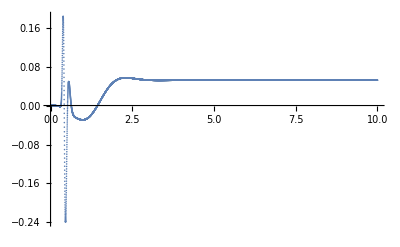

```mathematica
ListPlot[(b4plotlist),PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277847

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00239413

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.14596

### QNM1 = {}

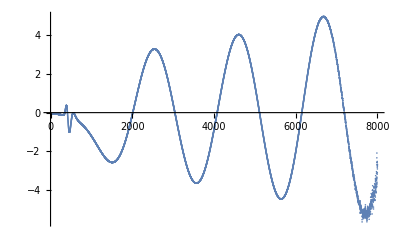

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 10.}}, <>]

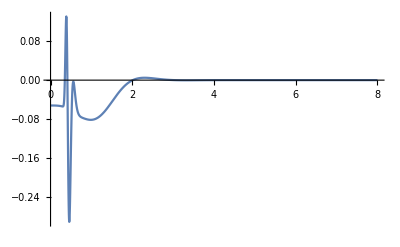

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{2.01144,3.04209,4.07668,5.11275,6.14855,6.14855}

{1.03065,1.03459,1.03608,1.0358,-8.88178×10^-16}

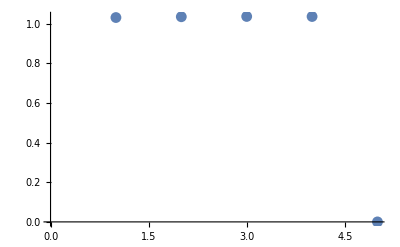

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 1;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.06856

```mathematica
μ1 = 2π/λ1
```

3.03748

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.0106998,-0.000903571,-0.00527105,-0.00447164}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00638519

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.458503

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.39269

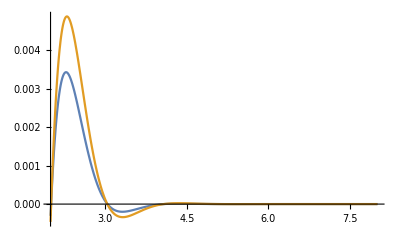

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→6.1135
ν→-2.5382) | (A→6.1135
ν→-2.5382) | (A→6.1135
ν→-2.5382) | (A→6.1135
ν→-2.5382) | (A→6.1135
ν→-2.5382)
(A→6.36768
ν→-2.5544) | (A→6.36768
ν→-2.5544) | (A→6.36768
ν→-2.5544) | (A→6.36768
ν→-2.5544) | (A→6.36768
ν→-2.5544)
(A→6.64805
ν→-2.57116) | (A→6.64805
ν→-2.57116) | (A→6.64805
ν→-2.57116) | (A→6.64805
ν→-2.57116) | (A→6.64805
ν→-2.57116)
(A→6.9029
ν→-2.58539) | (A→6.9029
ν→-2.58539) | (A→6.9029
ν→-2.58539) | (A→6.9029
ν→-2.58539) | (A→6.9029
ν→-2.58539)
(A→7.0783
ν→-2.59456) | (A→7.0783
ν→-2.59456) | (A→7.0783
ν→-2.59456) | (A→7.0783
ν→-2.59456) | (A→7.0783
ν→-2.59456)
(A→7.1307
ν→-2.59715) | (A→7.1307
ν→-2.59715) | (A→7.1307
ν→-2.59715) | (A→7.1307
ν→-2.59715) | (A→7.1307
ν→-2.59715)
(A→7.06819
ν→-2.59431) | (A→7.06819
ν→-2.59431) | (A→7.06819
ν→-2.59431) | (A→7.06819
ν→-2.59431) | (A→7.06819
ν→-2.59431)
(A→6.93328
ν→-2.58845) | (A→6.93328
ν→-2.58845) | (A→6.93328
ν→-2.58845) | (A→6.93328
ν→-2.58845) | (A→6.93328
ν→-2.58845)
(A→6.96108
ν→-2.58957) | (A→6.96108
ν→-2.58957) | (A→6.96108
ν→-2.58957) | (A→6.96108
ν→-2.58957) | (A→6.96108
ν→-2.58957)
(A→8.16506
ν→-2.63556) | (A→8.16507
ν→-2.63556) | (A→8.16507
ν→-2.63556) | (A→8.16508
ν→-2.63556) | (A→8.16508
ν→-2.63556))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

40

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.5382

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.58437

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubf,isubf},{j,jsubi,jsubf}])
```

0.00183792

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000227682

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.03748+0.00638519 x,-2.58437+0.00183792 x}

```mathematica
fxy/T^2
```

12.9535

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

125.845

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.26398+0.00686133 x,-2.77709+0.00197497 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.47982,-2.96073}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.03748-2.58437 ⅈ}

{3.26398-2.77709 ⅈ}

{3.26398-2.77709 ⅈ}

{3.47982-2.96073 ⅈ}

{3.07128-2.61314 ⅈ}

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-15.7626

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

13.9828

## GuassianR, fxy = 1.25

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp5e-07wid0.5uave0.25a2-1.0f30.0fxy1.25TS0.001amp20.0wid20.6uave20.6NS30000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp5e-07wid0.5uave0.25a2-1.0f30.0fxy1.25TS0.001amp20.0wid20.6uave20.6NS30000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

1.25

```mathematica
b4list[[-1]]
```

0.0567525

```mathematica
Max[Abs[lambshiftlist]]
```

8.62261×10^-12

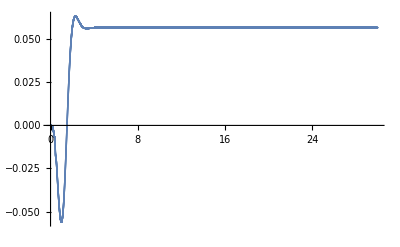

```mathematica
ListPlot[(b4plotlist),PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.264844

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00492246

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.34723

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.136495

### QNM1 = {}

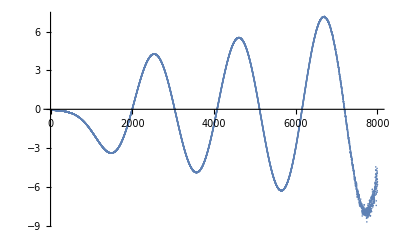

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 30.}}, <>]

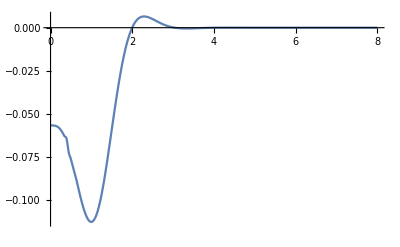

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{1.99741,3.03767,4.07567,5.1149,6.15387,11.476}

{1.04026,1.038,1.03923,1.03897,5.32213}

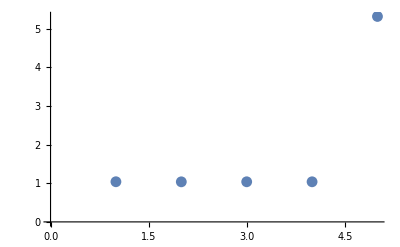

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 1;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.07823

```mathematica
μ1 = 2π/λ1
```

3.02333

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.00333744,0.00326091,-0.000338034,0.000421866}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00234863

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.438876

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.32687

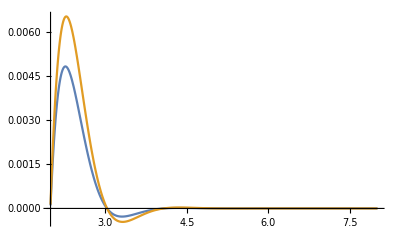

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→5.61915
ν→-2.52156) | (A→5.61915
ν→-2.52156) | (A→5.61915
ν→-2.52156) | (A→5.61915
ν→-2.52156) | (A→5.61915
ν→-2.52156)
(A→5.73268
ν→-2.52951) | (A→5.73268
ν→-2.52951) | (A→5.73268
ν→-2.52951) | (A→5.73268
ν→-2.52951) | (A→5.73268
ν→-2.52951)
(A→5.88942
ν→-2.54) | (A→5.88942
ν→-2.54) | (A→5.88942
ν→-2.54) | (A→5.88942
ν→-2.54) | (A→5.88942
ν→-2.54)
(A→6.07133
ν→-2.55149) | (A→6.07133
ν→-2.55149) | (A→6.07133
ν→-2.55149) | (A→6.07133
ν→-2.55149) | (A→6.07133
ν→-2.55149)
(A→6.26446
ν→-2.56288) | (A→6.26446
ν→-2.56288) | (A→6.26446
ν→-2.56288) | (A→6.26446
ν→-2.56288) | (A→6.26446
ν→-2.56288)
(A→6.44816
ν→-2.57288) | (A→6.44816
ν→-2.57288) | (A→6.44816
ν→-2.57288) | (A→6.44816
ν→-2.57288) | (A→6.44816
ν→-2.57288)
(A→6.60917
ν→-2.58089) | (A→6.60917
ν→-2.58089) | (A→6.60917
ν→-2.58089) | (A→6.60917
ν→-2.58089) | (A→6.60917
ν→-2.58089)
(A→6.75671
ν→-2.5876) | (A→6.75671
ν→-2.5876) | (A→6.75671
ν→-2.5876) | (A→6.75671
ν→-2.5876) | (A→6.75671
ν→-2.5876)
(A→6.79938
ν→-2.58946) | (A→6.79938
ν→-2.58946) | (A→6.79938
ν→-2.58946) | (A→6.79938
ν→-2.58946) | (A→6.79938
ν→-2.58946)
(A→6.36534
ν→-2.57043) | (A→6.36534
ν→-2.57043) | (A→6.36534
ν→-2.57043) | (A→6.36534
ν→-2.57043) | (A→6.36534
ν→-2.57043))

```mathematica
isubi = 4;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

30

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.52156

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.5742

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.0342895

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000181718

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.02333+0.00234863 x,-2.5742+0.0342895 x}

```mathematica
fxy/T^2
```

17.8209

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

170.157

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.1607+0.00245534 x,-2.69116+0.0358474 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.63367,-3.09387}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.02333-2.5742 ⅈ}

{3.24878-2.76616 ⅈ}

{3.1607-2.69116 ⅈ}

{3.63367-3.09387 ⅈ}

{3.10279-2.64186 ⅈ}

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-9.3571

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

3.78835

## GuassianR, fxy = 1.5

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS10000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.5uave0.25a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS10000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

1.5

```mathematica
b4list[[-1]]
```

0.0426478

```mathematica
Max[Abs[lambshiftlist]]
```

3.15267×10^-11

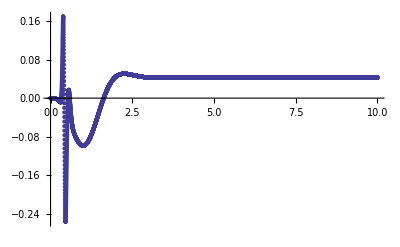

```mathematica
ListPlot[(b4plotlist),PlotRange->All]
```

```mathematica
g=1;
templist=((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-(1/4) a2-2 b4list))/(3/4 (-a2));
templistmuB=((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-(1/4) a2-2 b4list-1/4 fxy^2 Log[fxy]))/(3/4 (-a2)+1/4 fxy^2 Log[fxy]);
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256291

```mathematica
π T
```

0.805162

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00811795

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164704

```mathematica
0.008/0.8051624845670141
```

0.00993588

### QNM1 = {}

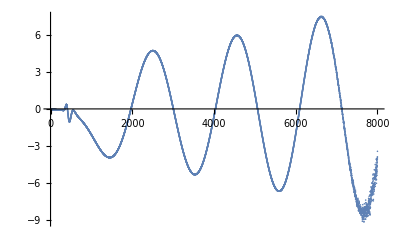

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 10.}}, <>]

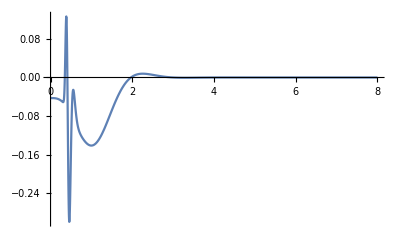

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{1.96753,3.00432,4.03432,5.06505,6.09595,8.024}

{1.03679,1.03001,1.03073,1.0309,1.92805}

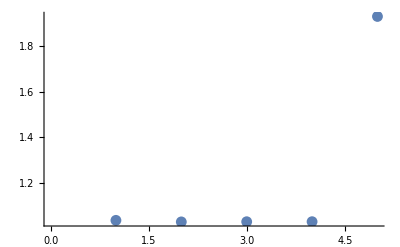

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot =1;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.06421

```mathematica
μ1 = 2π/λ1
```

3.04387

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.0137593,0.0062044,0.00406414,0.00357544}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00801737

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.420578

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.28018

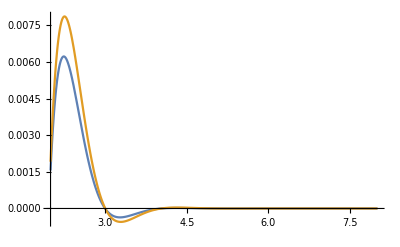

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429)
(A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563)
(A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522)
(A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626)
(A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667)
(A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276)
(A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926)
(A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248)
(A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789)
(A→5.31478
ν→-2.54202) | (A→5.31477
ν→-2.54202) | (A→5.31477
ν→-2.54202) | (A→5.31476
ν→-2.54202) | (A→5.31475
ν→-2.54202))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

40

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.5429

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.58273

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0263504

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000206887

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.04387+0.00801737 x,-2.58273+0.0263504 x}

```mathematica
fxy/T^2
```

22.8362

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

226.692

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.06078+0.00806193 x,-2.59708+0.0264968 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.78044,-3.20771}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.04387-2.58273 ⅈ}

{3.27085-2.77532 ⅈ}

{3.06078-2.59708 ⅈ}

{3.78044-3.20771 ⅈ}

{3.20079-2.71587 ⅈ}

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

5.00439

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-11.3512

### Testing Accuracy of Mode

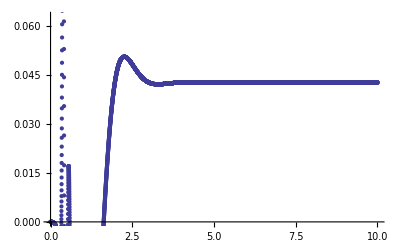

```mathematica
ListPlot[b4plotlist]
```

```mathematica
nlm=NonlinearModelFit[b4plotlist[[1501;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.75218 | 0.000384305 | 9763.54 | 1.5153069446×10^-17205
ν | -3.12782 | 0.00018569 | -16844.4 | 1.8754992745×10^-19217
ϕ | -1.23002 | 0.000598844 | -2053.99 | 6.5930333538×10^-11458
C0 | 0.0426489 | 2.2444×10^-7 | 190023. | 3.9536176318×10^-28157
A | 2.99663 | 0.000722371 | 4148.32 | 2.0918254661×10^-14048

```mathematica
nlm=NonlinearModelFit[b4plotlist[[1501;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2001;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2501;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3001;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3501;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4001;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4501;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.75218 | 0.000384305 | 9763.54 | 1.5153069446×10^-17205
ν | -3.12782 | 0.00018569 | -16844.4 | 1.8754992745×10^-19217
ϕ | -1.23002 | 0.000598844 | -2053.99 | 6.5930333538×10^-11458
C0 | 0.0426489 | 2.2444×10^-7 | 190023. | 3.9536176318×10^-28157
A | 2.99663 | 0.000722371 | 4148.32 | 2.0918254661×10^-14048

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.76466 | 0.000141557 | 26594.6 | 1.683990394×10^-19777
ν | -3.17273 | 0.000280948 | -11292.9 | 1.4586285615×10^-16803
ϕ | -1.25476 | 0.000235357 | -5331.31 | 8.7699240034×10^-14198
C0 | 0.0426486 | 4.79294×10^-8 | 889821. | 6.1783220124×10^-31966
A | 3.27492 | 0.00181034 | 1809.01 | 9.8798276423×10^-10449

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79434 | 0.0000413912 | 91670.2 | 5.8789289076×10^-22674
ν | -3.20782 | 0.0000221142 | -145057. | 8.6416464343×10^-24168
ϕ | -1.32462 | 0.0000983447 | -13469.2 | 1.5662702387×10^-16431
C0 | 0.0426477 | 2.03094×10^-9 | 2.0999×10^7 | 6.2753440922×10^-40362
A | 3.51966 | 0.000159669 | 22043.5 | 5.7539516291×10^-18035

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.78836 | 9.39854×10^-6 | 403079. | 2.628257425×10^-25765
ν | -3.21677 | 0.0000167838 | -191659. | 6.806132758×10^-23507
ϕ | -1.31003 | 0.0000230496 | -56835.3 | 3.6756258194×10^-19814
C0 | 0.0426478 | 2.37085×10^-10 | 1.79884×10^8 | 2.7954178827×10^-44299
A | 3.60817 | 0.000168644 | 21395.2 | 3.4970914388×10^-16846

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.78672 | 0.0000114079 | 331937. | 1.2280695856×10^-23480
ν | -3.2173 | 6.73249×10^-6 | -477877. | 1.5435062383×10^-24508
ϕ | -1.30482 | 0.0000364348 | -35812.5 | 7.6456022222×10^-17200
C0 | 0.0426478 | 4.66662×10^-11 | 9.1389×10^8 | 2.1888714834×10^-45822
A | 3.61398 | 0.0000695886 | 51933.5 | 3.238728137×10^-18248

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.7854 | 3.18418×10^-6 | 1.18881×10^6 | 4.2393711582×10^-25099
ν | -3.21775 | 5.09372×10^-6 | -631710. | 6.785613749×10^-23453
ϕ | -1.30049 | 0.000010418 | -124832. | 2.9220320545×10^-19231
C0 | 0.0426478 | 6.07405×10^-12 | 7.02132×10^9 | 4.5419288657×10^-47708
A | 3.61997 | 0.0000664366 | 54487.6 | 6.7132165292×10^-17073

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.78509 | 0.000012875 | 293988. | 1.325287003×10^-19775
ν | -3.21724 | 8.55576×10^-6 | -376032. | 5.4074080431×10^-20363
ϕ | -1.29922 | 0.0000516586 | -25150.2 | 4.0482668225×10^-13908
C0 | 0.0426478 | 4.51079×10^-12 | 9.45461×10^9 | 2.7046516999×10^-44543
A | 3.61309 | 0.000113957 | 31705.8 | 6.7697550246×10^-14461

```mathematica
nlm=NonlinearModelFit[b4plotlist[[2500;;10000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;9500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;9000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;8500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;7500]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2500;;7000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,3}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79434 | 0.0000412546 | 91973.7 | 1.5887573198×10^-22687
ν | -3.20782 | 0.0000221059 | -145112. | 5.0629023654×10^-24172
ϕ | -1.32462 | 0.000098004 | -13516. | 8.3891158656×10^-16445
C0 | 0.0426477 | 2.03065×10^-9 | 2.10021×10^7 | 1.4154065671×10^-40367
A | 3.51966 | 0.000159541 | 22061.2 | 8.9456439406×10^-18040

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79436 | 0.0000426366 | 88993. | 3.7160695709×10^-21179
ν | -3.20783 | 0.0000228945 | -140113. | 3.0943135973×10^-22558
ϕ | -1.32466 | 0.000101311 | -13075.3 | 3.2789801832×10^-15352
C0 | 0.0426477 | 2.18492×10^-9 | 1.95191×10^7 | 1.6060692764×10^-37557
A | 3.51976 | 0.000165204 | 21305.5 | 1.2751449643×10^-16835

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79438 | 0.0000441629 | 85917.8 | 4.6154471528×10^-19671
ν | -3.20785 | 0.000023773 | -134937. | 1.3925138243×10^-20944
ϕ | -1.32471 | 0.000104966 | -12620.4 | 7.059781595×10^-14260
C0 | 0.0426477 | 2.36448×10^-9 | 1.80368×10^7 | 2.8544200024×10^-34755
A | 3.51987 | 0.000171508 | 20523.1 | 1.3072097714×10^-15631

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.7944 | 0.0000458593 | 82740.1 | 2.5981607322×10^-18163
ν | -3.20787 | 0.0000247594 | -129561. | 4.3560908397×10^-19331
ϕ | -1.32478 | 0.000109035 | -12150.1 | 7.2264443288×10^-13168
C0 | 0.0426477 | 2.57608×10^-9 | 1.65553×10^7 | 2.0010246917×10^-31961
A | 3.52001 | 0.000178581 | 19710.9 | 9.0396761501×10^-14428

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79443 | 0.0000477566 | 79453.6 | 4.515949301×10^-16656
ν | -3.20789 | 0.000025877 | -123967. | 7.4258743636×10^-17718
ϕ | -1.32485 | 0.000113592 | -11663.3 | 2.4302940834×10^-12076
C0 | 0.0426477 | 2.82903×10^-9 | 1.5075×10^7 | 9.3437561636×10^-29177
A | 3.52018 | 0.000186588 | 18866.1 | 3.2833016931×10^-13224

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79447 | 0.0000498902 | 76056.4 | 1.1365841833×10^-15149
ν | -3.20792 | 0.0000271543 | -118137. | 3.765251508×10^-16105
ϕ | -1.32495 | 0.000118727 | -11159.6 | 1.2880950416×10^-10985
C0 | 0.0426477 | 3.13641×10^-9 | 1.35976×10^7 | 2.6831260161×10^-26402
A | 3.52039 | 0.000195728 | 17986.1 | 3.3702412873×10^-12021

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.79452 | 0.0000522989 | 72554.5 | 1.2045441254×10^-13644
ν | -3.20796 | 0.0000286278 | -112058. | 2.1784085017×10^-14493
ϕ | -1.32508 | 0.000124541 | -10639.7 | 3.2866416851×10^-9896
C0 | 0.0426477 | 3.5173×10^-9 | 1.21251×10^7 | 2.3885563567×10^-23639
A | 3.52068 | 0.000206256 | 17069.5 | 3.5757038932×10^-10819

```mathematica
Table[{b4plotlist[[29901+i,1]],b4plotlist[[29901+i,2]]-b4plotlist[[-1,2]]},{i,0,100}]
```

{{29.9,5.27522×10^-13},{29.901,1.67032×10^-12},{29.902,1.75446×10^-12},{29.903,1.63569×10^-12},{29.904,3.06309×10^-12},{29.905,2.73936×10^-12},{29.906,6.30829×10^-13},{29.907,-6.3298×10^-13},{29.908,-5.55195×10^-13},{29.909,2.79328×10^-12},{29.91,2.97132×10^-12},{29.911,3.34689×10^-12},{29.912,3.23055×10^-12},{29.913,3.24542×10^-12},{29.914,3.16477×10^-12},{29.915,3.06707×10^-12},{29.916,1.48109×10^-12},{29.917,4.71831×10^-13},{29.918,-9.99617×10^-14},{29.919,-3.99167×10^-13},{29.92,3.33414×10^-13},{29.921,1.04999×10^-12},{29.922,1.41873×10^-12},{29.923,1.45749×10^-12},{29.924,1.15762×10^-12},{29.925,8.14779×10^-13},{29.926,1.19355×10^-12},{29.927,1.93087×10^-12},{29.928,1.68653×10^-12},{29.929,1.44727×10^-12},{29.93,-2.86368×10^-13},{29.931,-1.22835×10^-12},{29.932,1.22077×10^-12},{29.933,6.38864×10^-13},{29.934,-1.39903×10^-12},{29.935,-1.03029×10^-12},{29.936,-5.12909×10^-13},{29.937,1.49325×10^-13},{29.938,2.4887×10^-13},{29.939,1.67803×10^-12},{29.94,1.66855×10^-12},{29.941,2.70532×10^-12},{29.942,1.93492×10^-12},{29.943,1.37976×10^-12},{29.944,-1.64299×10^-13},{29.945,-4.39773×10^-13},{29.946,1.87225×10^-12},{29.947,2.37546×10^-12},{29.948,1.55442×10^-12},{29.949,1.78778×10^-12},{29.95,2.92277×10^-12},{29.951,4.46464×10^-12},{29.952,1.74311×10^-12},{29.953,-1.55928×10^-12},{29.954,-7.0019×10^-13},{29.955,1.22413×10^-12},{29.956,1.32616×10^-13},{29.957,4.57551×10^-14},{29.958,-5.20181×10^-13},{29.959,-6.51201×10^-13},{29.96,1.14729×10^-12},{29.961,2.39614×10^-12},{29.962,4.74605×10^-12},{29.963,3.44941×10^-12},{29.964,8.4327×10^-13},{29.965,-1.47729×10^-12},{29.966,-1.25983×10^-13},{29.967,9.60232×10^-13},{29.968,-3.31388×10^-13},{29.969,2.35006×10^-13},{29.97,3.27197×10^-13},{29.971,-7.49262×10^-14},{29.972,-8.27755×10^-13},{29.973,-1.24017×10^-12},{29.974,-8.69832×10^-13},{29.975,-1.0334×10^-12},{29.976,4.11601×10^-13},{29.977,7.73465×10^-13},{29.978,-1.88558×10^-13},{29.979,2.06453×10^-12},{29.98,1.95217×10^-12},{29.981,2.31473×10^-12},{29.982,1.51158×10^-12},{29.983,4.02789×10^-13},{29.984,8.62699×10^-13},{29.985,2.46808×10^-12},{29.986,3.1657×10^-12},{29.987,3.06717×10^-12},{29.988,3.0457×10^-12},{29.989,3.04475×10^-12},{29.99,1.06219×10^-12},{29.991,1.77051×10^-12},{29.992,1.23174×10^-12},{29.993,5.19099×10^-13},{29.994,8.21912×10^-13},{29.995,7.21451×10^-13},{29.996,1.00851×10^-12},{29.997,2.69451×10^-13},{29.998,-1.57221×10^-13},{29.999,5.4369×10^-13},{30.,0.}}

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
b4plotlist[[2001]]
```

{2.,0.00082413}

```mathematica
tlist[[2000]]
```

1.999

```mathematica
Plot[b4plotlist[[i,
```

```mathematica
b4plotlist[[2001,2]]-b4plotlist[[-1,2]]
b4plotlist[[8001,2]]-b4plotlist[[-1,2]]
b4plotlist[[20001,2]]-b4plotlist[[-1,2]]
```

-6.43499×10^-6

7.7624×10^-13

1.29811×10^-12

```mathematica
LeadQNMplotlist = Table[{tlist[[2001+i]],(b4plotlist[[2001,2]]-b4plotlist[[-1,2]])ⅇ^(-2.7259778940581847tlist[[2001+i]])},{i,0,28000}];
```

```mathematica
ListPlot[LeadQNMplotlist]
```

-Graphics-

```mathematica
Length[LeadQNMplotlist]
```

28001

```mathematica
diffplotlist = Table[{b4plotlist[[2001+i,1]],(b4plotlist[[2001+i,2]]-b4plotlist[[-1,2]])-LeadQNMplotlist[[1+i,2]]},{i,0,28000}];
```

```mathematica
ListPlot[diffplotlist,PlotRange->All]
```

-Graphics-

### QNM1 = {} Scheme effects???

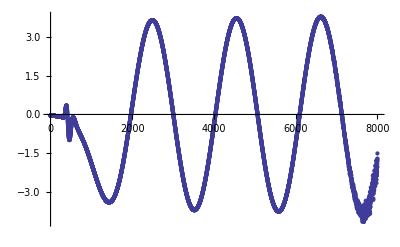

```mathematica
ListPlot[ⅇ^(2.597080030002568tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

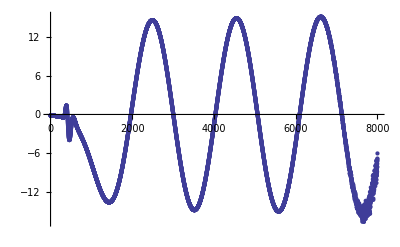

```mathematica
ListPlot[ⅇ^(2.597080030002568tlist[[;;8000]])((templist[[;;8000]])- templist[[-1]]),PlotRange->All]
```

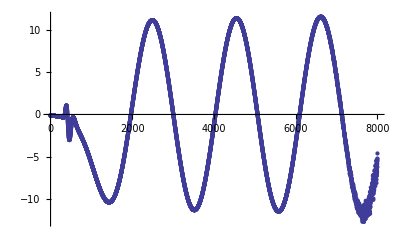

```mathematica
ListPlot[ⅇ^(2.597080030002568tlist[[;;8000]])((templistmuB[[;;8000]])- templistmuB[[-1]]),PlotRange->All]
```

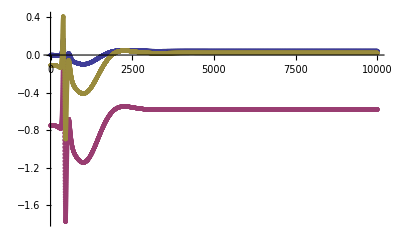

```mathematica
ListPlot[{b4list,templist,templistmuB}]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0., 10.}}, <>]

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{1.96753,3.00432,4.03432,5.06505,6.09595,8.024}

{1.03679,1.03001,1.03073,1.0309,1.92805}

-Graphics-

```mathematica
startroot =1;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.06421

```mathematica
μ1 = 2π/λ1
```

3.04387

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.0137593,0.0062044,0.00406414,0.00357544}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00801737

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.420578

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.28018

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

-Graphics-

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429) | (A→5.55341
ν→-2.5429)
(A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563) | (A→5.5915
ν→-2.54563)
(A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522) | (A→5.68651
ν→-2.5522)
(A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626) | (A→5.84536
ν→-2.5626)
(A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667) | (A→6.0768
ν→-2.57667)
(A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276) | (A→6.36874
ν→-2.59276)
(A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926) | (A→6.7052
ν→-2.60926)
(A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248) | (A→7.05863
ν→-2.6248)
(A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789) | (A→6.43864
ν→-2.59789)
(A→5.31478
ν→-2.54202) | (A→5.31477
ν→-2.54202) | (A→5.31477
ν→-2.54202) | (A→5.31476
ν→-2.54202) | (A→5.31475
ν→-2.54202))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

40

```mathematica
tempmtx[[1,2]][[2,2]]
```

-2.5429

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.58273

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0263504

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000206887

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.04387+0.00801737 x,-2.58273+0.0263504 x}

```mathematica
fxy/T^2
```

22.8362

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

226.692

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{3.06078+0.00806193 x,-2.59708+0.0264968 x}

```mathematica
N[{μ1,ν1}1/(π T)]//Simplify
```

{3.78044,-3.20771}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.04387-2.58273 ⅈ}

{3.27085-2.77532 ⅈ}

{3.06078-2.59708 ⅈ}

{3.78044-3.20771 ⅈ}

{3.20079-2.71587 ⅈ}

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

5.00439

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

-11.3512

## GuassianR, fxy = 2.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.5uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS8000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.5uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS8000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
a2
```

-1.

```mathematica
fxy
```

2.

```mathematica
b4list[[-1]]
```

-0.0701805

```mathematica
Max[Abs[lambshiftlist]]
```

4.17569×10^-11

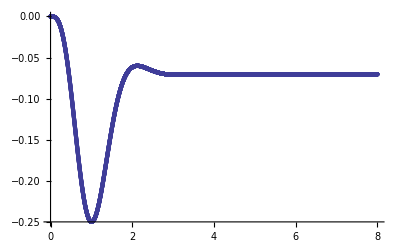

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.257508

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0139963

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42844

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.390361

### QNM1 = {}

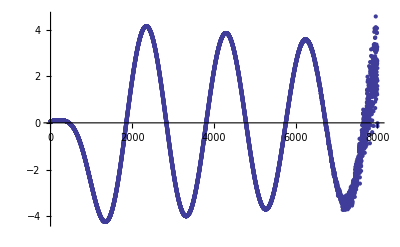

```mathematica
ListPlot[ⅇ^(2.7tlist[[;;8000]])((b4list[[;;8000]])- b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,8.}},<>]

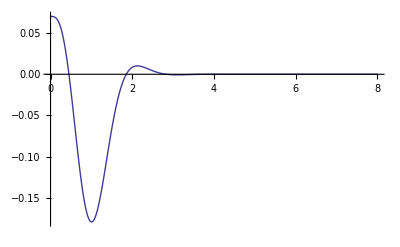

```mathematica
Plot[y[x],{x,0,8},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,5.5,6.5}
```

{2,3,3.5,4.5,5.5,6.5}

{1.85354,2.83486,3.80868,4.78261,5.7562,6.7292}

{0.981317,0.973813,0.973933,0.97359,0.973001}

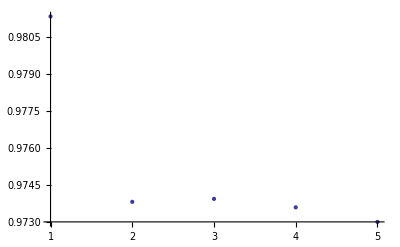

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 1;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

1.95133

```mathematica
μ1 = 2π/λ1
```

3.21996

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.0185524,0.00611702,0.00572071,0.00685854}

\Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.0107398

```mathematica
Δx1 = x4-FindRoot[Cos[μ1 x],{x,n4}][[1,2]]
```

0.392123

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.26262

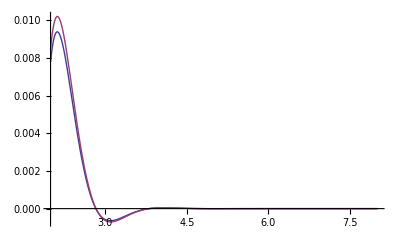

```mathematica
Plot[{7.0 ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.ν->-2.75,y[x]}, {x,2,8},PlotRange->All]
```

```mathematica
ii = 1;
if = 10;
ji = 1;
jf = 5;
```

```mathematica
tempmtx = Table[FindFit[b4plotlistshift[[2000+100*i;;6700- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,8.6},{ν,2.75}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→7.06128
ν→-2.71476) | (A→7.06128
ν→-2.71476) | (A→7.06128
ν→-2.71476) | (A→7.06128
ν→-2.71476) | (A→7.06128
ν→-2.71476)
(A→7.08325
ν→-2.71602) | (A→7.08325
ν→-2.71602) | (A→7.08325
ν→-2.71602) | (A→7.08325
ν→-2.71602) | (A→7.08325
ν→-2.71602)
(A→7.21542
ν→-2.72331) | (A→7.21542
ν→-2.72331) | (A→7.21542
ν→-2.72331) | (A→7.21542
ν→-2.72331) | (A→7.21542
ν→-2.72331)
(A→7.47408
ν→-2.73654) | (A→7.47408
ν→-2.73654) | (A→7.47408
ν→-2.73654) | (A→7.47408
ν→-2.73654) | (A→7.47408
ν→-2.73654)
(A→7.8381
ν→-2.75329) | (A→7.8381
ν→-2.75329) | (A→7.8381
ν→-2.75329) | (A→7.8381
ν→-2.75329) | (A→7.8381
ν→-2.75329)
(A→8.28811
ν→-2.77161) | (A→8.28811
ν→-2.77161) | (A→8.28811
ν→-2.77161) | (A→8.28811
ν→-2.77161) | (A→8.28812
ν→-2.77161)
(A→8.32449
ν→-2.7731) | (A→8.32449
ν→-2.7731) | (A→8.32449
ν→-2.7731) | (A→8.32449
ν→-2.7731) | (A→8.32449
ν→-2.7731)
(A→6.28907
ν→-2.6864) | (A→6.28907
ν→-2.6864) | (A→6.28907
ν→-2.6864) | (A→6.28906
ν→-2.6864) | (A→6.28906
ν→-2.6864)
(A→6.34845
ν→-2.68924) | (A→6.34845
ν→-2.68924) | (A→6.34845
ν→-2.68924) | (A→6.34845
ν→-2.68924) | (A→6.34844
ν→-2.68924)
(A→6.67572
ν→-2.70448) | (A→6.67572
ν→-2.70448) | (A→6.67572
ν→-2.70448) | (A→6.67571
ν→-2.70448) | (A→6.67571
ν→-2.70448))

```mathematica
isubi = 2;
isubf = 9;
jsubi = 1;
jsubf = 5;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

40

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.73119

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,isubi,isubf},{j,jsubi,jsubf}])
```

0.0315522

Here we check that within the windows of each fit, that the corresponding fit is not that far off from the data restricted to each window from which the fit was created. This should be less then the uncertainty in my parameters.

```mathematica
b4listshift =Table[b4plotlistshift[[k,2]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
b4tlistshift = Table[b4plotlistshift[[k,1]],{k,1,Length[b4plotlistshift]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

0.0000225462

So the fit is doing pretty well then.

The frequency we have found is in units of a4, i.e.  omega =

```mathematica
{μ1 +x σμ1,ν1 + x σν1}
```

{3.21996+0.0107398 x,-2.73119+0.0315522 x}

```mathematica
fxy/T^2
```

30.1611

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/T^4
```

328.205

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{2.9378+0.00979874 x,-2.49186+0.0287874 x}

```mathematica
N[{μ1+ x σμ1,ν1 +x σν1}1/(π T)]//Simplify
```

{3.98023+0.0132757 x,-3.37606+0.0390022 x}

```mathematica
Subscript[ω, a2] = {μ1 +ⅈ ν1}
Subscript[ω, ε[1/L]] = {μ1 +ⅈ ν1}1/(-3/4 a2)^(1/4)
Subscript[ω, ε[B^(1/2)]] = {μ1 +ⅈ ν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))
Subscript[ω, πT] = {μ1 +ⅈ ν1}1/(π T)
Subscript[ω, Subscript[r, h]] =  {μ1 +ⅈ ν1} * (1 + lamblist[[-1]])
```

{3.21996-2.73119 ⅈ}

{3.46007-2.93485 ⅈ}

{2.9378-2.49186 ⅈ}

{3.98023-3.37606 ⅈ}

{3.65543-3.10056 ⅈ}

```mathematica
((-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

227.423 (1.17575-1./g^2)

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list + 1/4 fxy^2 Log[fxy])+(-1/4 a2-2 b4list- 1/4 fxy^2 Log[fxy]))[[-1]]/(T^4)
```

75.8077 (-0.302786+2 (0.872967-1./g^2))

### QNM accuracy

```mathematica
ν1
```

-2.73119

```mathematica
Plot[nlm,{x,2,8}]
```

-Graphics-

```mathematica
A->0.040237122759667704
nlm=NonlinearModelFit[b4plotlist[[1501;;8000]],A ⅇ^(ν x) Cos[μ x+ϕ]+ C0/.μ->3.2199556085235246/.ν->-2.7311887123281684,{A,ϕ,C0},x,MaxIterations->10000]
nlm["ParameterTable"]
```

A→0.0402371

FittedModel[-0.0701673+4.36593 ⅇ^(-2.73119 x) Cos[1.25417-3.21996 x]]

| Estimate | Standard Error | t-Statistic | P-Value
A | 4.36593 | 0.00033569 | 13005.8 | 9.6098316223×10^-14347
ϕ | -1.25417 | 0.000071907 | -17441.6 | 9.4558315171×10^-15175
C0 | -0.0701673 | 5.01637×10^-7 | -139877. | 4.8653140586×10^-21049

```mathematica
nlm=NonlinearModelFit[b4plotlist[[1501;;8000]],A ⅇ^(ν x) Cos[μ x+ϕ]+ C0/.A->4.365933438107519,{μ,ν,ϕ,C0},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.18268 | 0.000394058 | 8076.68 | 8.7721959736×10^-13001
ν | -2.72631 | 0.0000552916 | -49307.9 | 1.9151914922×10^-18104
ϕ | -1.18518 | 0.000725591 | -1633.39 | 6.3174740098×10^-8495
C0 | -0.0701781 | 3.41536×10^-7 | -205478. | 5.6205753313×10^-22131

```mathematica
nlm=NonlinearModelFit[b4plotlist[[1501;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2001;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[2501;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3001;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[3501;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4001;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
nlm=NonlinearModelFit[b4plotlist[[4501;;8000]],(A ⅇ^(ν x) Cos[μ x+ϕ]+ C0 /.ν-> (π T)ν/.μ->(π T)μ),{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.95262 | 0.000147876 | 26729.3 | 1.1129282861×10^-16374
ν | -3.35069 | 0.000071186 | -47069.5 | 7.9689469196×10^-17971
ϕ | -1.21395 | 0.000222386 | -5458.76 | 4.0899269741×10^-11894
C0 | -0.0701795 | 9.43017×10^-8 | -744202. | 5.1785093848×10^-25758
A | 4.2378 | 0.00044778 | 9464.03 | 4.2653037854×10^-13446

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.96137 | 0.0000818803 | 48380. | 2.3079794863×10^-16763
ν | -3.36909 | 0.000168545 | -19989.2 | 4.4239484432×10^-14462
ϕ | -1.23192 | 0.000154921 | -7951.89 | 3.1131539431×10^-12062
C0 | -0.0701799 | 2.89449×10^-8 | -2.4246×10^6 | 1.040673452×10^-26954
A | 4.39118 | 0.00140876 | 3117.06 | 1.3639236543×10^-9624

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.98842 | 0.0000243207 | 163993. | 1.359059038×10^-18382
ν | -3.37977 | 0.0000120325 | -280888. | 8.073759552×10^-19667
ϕ | -1.29286 | 0.0000559955 | -23088.6 | 5.174912269×10^-13704
C0 | -0.0701805 | 1.12441×10^-9 | -6.24151×10^7 | 2.9879632755×10^-32562
A | 4.47614 | 0.00012414 | 36057.1 | 8.3598214613×10^-14768

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.98865 | 5.40747×10^-6 | 737619. | 2.1047226403×10^-20075
ν | -3.38509 | 0.0000106445 | -318013. | 2.6915223815×10^-18250
ϕ | -1.2942 | 0.0000147598 | -87684.6 | 1.7429612448×10^-15455
C0 | -0.0701805 | 1.33285×10^-10 | -5.26544×10^8 | 3.7900604408×10^-34329
A | 4.54067 | 0.00013051 | 34791.8 | 2.8877751282×10^-13450

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.98763 | 6.56267×10^-6 | 607623. | 1.4150309136×10^-17790
ν | -3.38578 | 3.43889×10^-6 | -984556. | 9.3103456127×10^-18733
ϕ | -1.29098 | 0.0000203314 | -63497. | 1.6174985076×10^-13381
C0 | -0.0701805 | 2.24443×10^-11 | -3.12687×10^9 | 1.1673166469×10^-34473
A | 4.55061 | 0.0000493588 | 92194.6 | 1.7154248092×10^-14109

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.98726 | 5.85979×10^-6 | 680445. | 1.3253135359×10^-16110
ν | -3.3861 | 0.0000108374 | -312445. | 3.219796818×10^-14760
ϕ | -1.2898 | 0.0000209585 | -61540.9 | 2.6278168355×10^-11941
C0 | -0.0701805 | 1.02267×10^-11 | -6.8625×10^9 | 2.4221656208×10^-32105
A | 4.55558 | 0.000172602 | 26393.5 | 1.7490715217×10^-10472

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.98718 | 0.0000417216 | 95566.3 | 1.3773103068×10^-11216
ν | -3.38603 | 0.0000232494 | -145640. | 4.3625221435×10^-11856
ϕ | -1.28949 | 0.000162473 | -7936.64 | 1.0758775421×10^-7439
C0 | -0.0701805 | 1.10127×10^-11 | -6.37267×10^9 | 1.591539748×10^-28076
A | 4.55447 | 0.000423281 | 10759.9 | 1.2829693454×10^-7901

```mathematica
b4plotlist[[4601]]
```

{4.6,-0.0701719}

```mathematica
nlm[4.6]
```

-0.0701719

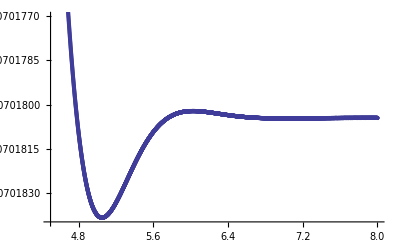

```mathematica
ListPlot[b4plotlist,PlotRange->{{4.5,8},{-0.070184,-0.070177}}]
```

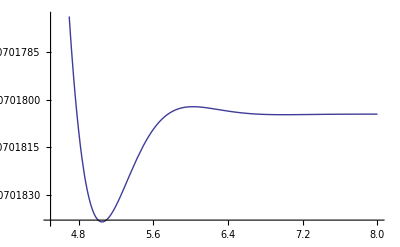

```mathematica
Plot[nlm[x],{x,4.5,8},PlotRange->All]
```

```mathematica
nlm=NonlinearModelFit[b4plotlist[[2001;;8000]],A ⅇ^(ν x) Cos[μ x+ϕ]+ C0,{{μ,3.1},{ν,-2.7},ϕ,C0,{A,4.36}},x,MaxIterations->10000];
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
μ | 3.20469 | 0.0000662401 | 48380. | 2.3079798188×10^-16763
ν | -2.72555 | 0.000136351 | -19989.2 | 4.4239506084×10^-14462
ϕ | -1.23192 | 0.000154921 | -7951.89 | 3.1131514063×10^-12062
C0 | -0.0701799 | 2.89449×10^-8 | -2.4246×10^6 | 1.0406734582×10^-26954
A | 4.39118 | 0.00140876 | 3117.06 | 1.3639254278×10^-9624

```mathematica
tlist[[
```

```mathematica
tlist[[4501]]
```

4.5

```mathematica
b4plotlist[[4501,2]]
```

-0.0701645

```mathematica
a = Table[(nlm[b4plotlist[[i,1]]]-b4plotlist[[i,2]]),{i,4501,8000}];
a.a
```

1.5946×10^-9

```mathematica
nlm[b4plotlist[[i,1]]]-b4plotlist[[i,2]]/.i->4501
```

Part::pspec: Part specification i is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

-5.47637×10^-10

```mathematica
N[{μ1 +x σμ1,ν1 + x σν1}1/((-3/4 a2 + 1/4 fxy^2 Log[fxy])^(1/4))]//Simplify
```

{2.9378+0.00979874 x,-2.49186+0.0287874 x}

```mathematica
N[{μ1+ x σμ1,ν1 +x σν1}1/(π T)]//Simplify
```

{3.98023+0.0132757 x,-3.37606+0.0390022 x}

## GaussianR (difficult to go higher that B/T^2 = 30, with our initial condition set up. Must start from EQ soln)

```mathematica
NSolve[B^2/(-3/4 A + 1/4 B^2 Log[B])== 6.0/.B->0.5]
```

{{A→-0.113318}}

## Guassian B, S Black Brane (No field strength)

## Gaussian B, Schwarzchild, f3 = 0, Fxy = 0 (amp 0.05), T = 0.318310 : QNM1 {3.11962, -2.74651}

```mathematica
a2 = -1;
fxy = 0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.0TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.0TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

8.85308×10^-16

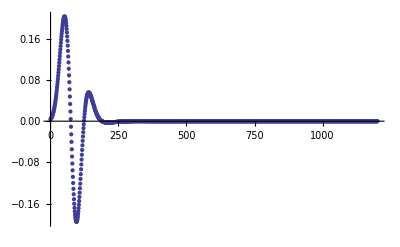

```mathematica
ListPlot[(b4list),PlotRange->All]
```

### QNM1 {3.11962, -2.74651}

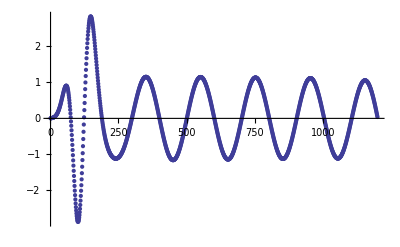

```mathematica
ListPlot[ⅇ^(2.74tlist[[1;;1200]])((b4list)[[1;;1200]]-b4list[[-1]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,200,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{1.99,12.}},<>]

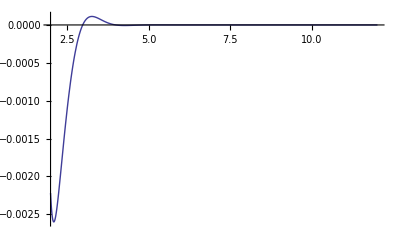

```mathematica
Plot[y[x],{x,2,12},PlotRange->All]
```

{2.98409,3.99447,4.99942,6.00673,7.01384,8.02093,9.02805,10.0349,11.0458}

{1.01039,1.00495,1.00731,1.00711,1.00709,1.00711,1.00686,1.01089}

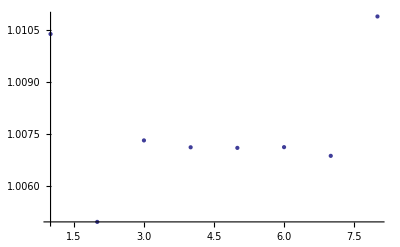

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
n9 = 10;
n10 = 11;
{x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]],x9=FindRoot[y[x],{x,n9}][[1,2]],x10=FindRoot[y[x],{x,n10}][[1,2]]}
templist = { x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7,x9-x8,x10-x9}
ListPlot[%,PlotRange->All]
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,4,7}]/4
```

2.01409

```mathematica
μ1 = 2π/λ1
```

3.11962

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47515

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.6019

```mathematica
lowcut = 800;
highcut = 1200;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→5.39484,ν1→-2.74651}

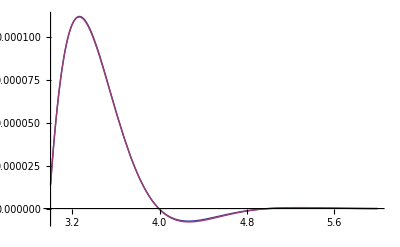

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->3.635715255649085,ν1->-2.6453105473258396})},{x,3,6}]
```

### Thermodynamics

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]] (*dont think this is correct thing for temp with fxy ≠ 0*)
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]]))
```

0.

```mathematica
chem/T
```

0.

## RN in EQ

```mathematica
L = 1;
Clear[m,ρ]
eps[m_] := 3/4 m L^-4
rplusEQ = (rh/L)^2-m (L/rh)^2+1/3(ρ L^3)^2(L/rh)^4
piT[rh_, ρ_]:= rh L^-2(1 - 1/6(ρ L^3)^2(L/rh)^6)
ρmax = 1/L^3(4/3 m^3)^(1/4)
rhlist =  Table[NSolve[rplusEQ ==0,rh][[i,1,2]],{i,1,6}]
NUMj = 5000;
rhtable = Table[{0,0,0},{i,1,2},{j,1,NUMj + 1}];
For[k = 1, k<3,k++,
For[j = 1, j<NUMj + 2, j++,
ρ = 1/NUMj*(j-1 )ρmax;
rhlistnew = {0,0,0,0,0,0};
rhlisttemp = Chop[(rhlist/.ρ->.3ρmax//.m->k)];
For[i = 1, i<7,i++,
If[Abs[Im[rhlisttemp[[i]]]]>0,rhlistnew[[i]] = 0,rhlistnew[[i]]=rhlisttemp[[i]]]];
Clear[rhrule];
rhrule = rh->Max[rhlistnew];
rhtable[[k,j]] ={k,1/NUMj*(j-1 ) ρmax,rhrule[[2]]}//.m->k ]]
rhtable;
```

-m/rh^2+rh^2+ρ^2/(3 rh^4)

(√2 (m^3)^(1/4))/3^(1/4)

{-1. √((0.87358 m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))+0.381571 (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3)),√((0.87358 m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))+0.381571 (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3)),-1. √(-((0.43679-0.756543 ⅈ) m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))-(0.190786+0.330451 ⅈ) (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3)),√(-((0.43679-0.756543 ⅈ) m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))-(0.190786+0.330451 ⅈ) (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3)),-1. √(-((0.43679+0.756543 ⅈ) m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))-(0.190786-0.330451 ⅈ) (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3)),√(-((0.43679+0.756543 ⅈ) m)/((-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))-(0.190786-0.330451 ⅈ) (-3. ρ^2+1.73205 √(-4. m^3+3. ρ^4))^(1/3))}

```mathematica
FullSimplify[eps[m]/ρmax^(4/3),Assumptions->{m>0}]
```

(3 3^(1/3))/(4 2^(2/3))

### T = 0 expansion

```mathematica
Clear[ρ]
```

```mathematica
ρ = x 1/L^3(4/3 m^3)^(1/4);
```

```mathematica
rplusEQ/.rh->z^(1/2)
```

-m/z+z+ρ^2/(3 z^2)

```mathematica
FullSimplify[Solve[(rplusEQ/.rh->z^(1/2))==0,z],Assumptions->{m>0,x>0,x<1}]
%/.m->1/.x->0.0
```

{{z→(2 3^(1/3) m+2^(1/3) (-3 ρ^2+√(-12 m^3+9 ρ^4))^(2/3))/(6^(2/3) (-3 ρ^2+√(-12 m^3+9 ρ^4))^(1/3))},{z→(-2 (3 ⅈ+√3) m+(-3 ρ^2+√(-12 m^3+9 ρ^4))^(2/3) Root[-768+#1^6&,4])/(2 2^(2/3) 3^(5/6) (-3 ρ^2+√(-12 m^3+9 ρ^4))^(1/3))},{z→-((-3 ⅈ+√3) m+(-2)^(1/3) 3^(1/6) (-3 ρ^2+√(-12 m^3+9 ρ^4))^(2/3))/(2^(2/3) 3^(5/6) (-3 ρ^2+√(-12 m^3+9 ρ^4))^(1/3))}}

{{z→(2 3^(1/3)+2^(1/3) (-3 ρ^2+√(-12+9 ρ^4))^(2/3))/(6^(2/3) (-3 ρ^2+√(-12+9 ρ^4))^(1/3))},{z→(-2 (3 ⅈ+√3)+(-3 ρ^2+√(-12+9 ρ^4))^(2/3) Root[-768+#1^6&,4])/(2 2^(2/3) 3^(5/6) (-3 ρ^2+√(-12+9 ρ^4))^(1/3))},{z→-(-3 ⅈ+√3+(-2)^(1/3) 3^(1/6) (-3 ρ^2+√(-12+9 ρ^4))^(2/3))/(2^(2/3) 3^(5/6) (-3 ρ^2+√(-12+9 ρ^4))^(1/3))}}

```mathematica
Clear[rhrh]
```

```mathematica
rhrh[m_,x_]:= (m+(-m^(3/2) x^2+√(m^3 (-1+x^4)))^(2/3))/(√3 (-m^(3/2) x^2+√(m^3 (-1+x^4)))^(1/3))
```

```mathematica
FullSimplify[((m+(-m^(3/2) x^2+√(m^3 (-1+x^4)))^(2/3))/(√3 (-m^(3/2) x^2+√(m^3 (-1+x^4)))^(1/3)))^(1/2),Assumptions->{m>0,x>0}]
```

(√((√m (1+(-x^2+√(-1+x^4))^(2/3)))/((-x^2+√(-1+x^4))^(1/3))))/3^(1/4)

```mathematica
1.333/1
```

```mathematica
4/3//N
```

1.33333

```mathematica
(m/3)^(1/4)((-x^2+ⅈ √(1-x^4))^(1/3)+(-x^2-ⅈ √(1-x^4))^(1/3))^(1/2)/.m->1/.x->0//N
```

1.+0. ⅈ

```mathematica
(√((√m (1+(-x^2+√(-1+x^4))^(2/3)))/((-x^2+√(-1+x^4))^(1/3))))/3^(1/4)/.m->1/.x->0//N
```

1.+3.20494×10^-17 ⅈ

```mathematica
1/3^(1/4)//N
```

0.759836

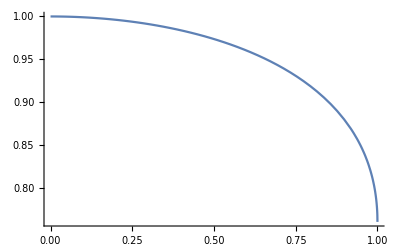
{-Graphics-,-Graphics-}

```mathematica
{Plot[(√((√m (1+(-x^2+√(-1+x^4))^(2/3)))/((-x^2+√(-1+x^4))^(1/3))))/3^(1/4)/.m->1,{x,0,1}],Plot[(m/3)^(1/4)((-x^2+ⅈ √(1-x^4))^(1/3)+(-x^2-ⅈ √(1-x^4))^(1/3))^(1/2)/.m->1,{x,0,1}]}
```

```mathematica
Series[rhrh[1,1-y]^(1/2),{y,0,1}]
```

(√((-1)^(1/3)-(-1)^(2/3)))/3^(1/4)-((-(-1)^(1/6)+(-1)^(5/6)) √y)/(3 (3^(1/4) √((-1)^(1/3)-(-1)^(2/3))))+((-1)^(2/3) √(-(-1)^(1/3) (-1+(-1)^(1/3))) (1+4 (-1)^(1/3)+(-1)^(2/3)) y)/(18 3^(1/4))+O[y]^(3/2)

Now we want eps/ρ^(4/3) as a function of piT^4/ρ^(4/3), so we should expand both in y.

```mathematica
Simplify[eps[m]/ρ^(4/3),Assumptions->{m>0}]
Yexpn = Series[(%/.x->1-η),{η,0,5}]
```

(3 3^(1/3))/(4 2^(2/3) x^(4/3))

(3 3^(1/3))/(4 2^(2/3))+(3^(1/3) η)/2^(2/3)+(7 η^2)/(2 6^(2/3))+(35 η^3)/(9 6^(2/3))+(455 η^4)/(108 6^(2/3))+(182 2^(1/3) η^5)/(81 3^(2/3))+O[η]^6

```mathematica
Simplify[piT[rhrh[m,x]^(1/2),ρ]^4/ρ^(4/3),Assumptions->{m>0}]
%/.x->1-η
Xexpn = FullSimplify[Series[(%/.x->1-η),{η,0,5}],Assumptions->{η>0}]
```

((1+(-x^2+√(-1+x^4))^(2/3))^2 (1+(x^2 (x^2-√(-1+x^4)))/((1+(-x^2+√(-1+x^4))^(2/3))^3))^4)/(6^(2/3) x^(4/3) (-x^2+√(-1+x^4))^(2/3))

((1+(√(-1+(1-η)^4)-(1-η)^2)^(2/3))^2 (1+((-√(-1+(1-η)^4)+(1-η)^2) (1-η)^2)/((1+(√(-1+(1-η)^4)-(1-η)^2)^(2/3))^3))^4)/(6^(2/3) (√(-1+(1-η)^4)-(1-η)^2)^(2/3) (1-η)^(4/3))

24 6^(1/3) η^2-(224 2^(1/3) η^(5/2))/3^(1/6)+(4184 2^(1/3) η^3)/(3 3^(2/3))-(20792 2^(1/3) η^(7/2))/(9 3^(1/6))+(809858 2^(1/3) η^4)/(81 3^(2/3))-(9513097 2^(1/3) η^(9/2))/(729 3^(1/6))+(34555388 2^(1/3) η^5)/(729 3^(2/3))+O[η]^(11/2)

```mathematica
Yexpn -(3 3^(1/3))/(4 2^(2/3))- 3^(1/3)/2^(2/3)1/(√(24 6^(1/3)))Xexpn^(1/2)
```

(7 2^(1/3) η^(3/2))/(3 3^(1/6))-(22 2^(1/3) η^2)/(3 3^(2/3))+(1073 η^(5/2))/(54 2^(2/3) 3^(1/6))-(6886 2^(1/3) η^3)/(243 3^(2/3))+(222893 η^(7/2))/(3888 2^(2/3) 3^(1/6))-(331579 η^4)/(2187 6^(2/3))+O[η]^(9/2)

```mathematica
Yexpn-(3 3^(1/3))/(4 2^(2/3)) - 3^(1/3)/2^(2/3)(Xexpn/(24 6^(1/3)))^(1/2) - (7 2^(1/3))/(3 3^(1/6))(Xexpn/(24 6^(1/3)))^(3/4)
```

3 6^(1/3) η^2-(317 η^(5/2))/(9 (2^(2/3) 3^(1/6)))+(55433/(243 2^(2/3) 3^(2/3))-(6886 2^(1/3))/(243 3^(2/3))) η^3-(18115 η^(7/2))/(81 (2^(2/3) 3^(1/6)))+(8332723/(8748 2^(2/3) 3^(2/3))-331579/(2187 6^(2/3))) η^4+O[η]^(9/2)

```mathematica
Yexpn-(3 3^(1/3))/(4 2^(2/3)) - 3^(1/3)/2^(2/3)(Xexpn/(24 6^(1/3)))^(1/2) - (7 2^(1/3))/(3 3^(1/6))(Xexpn/(24 6^(1/3)))^(3/4)-3 6^(1/3)(Xexpn/(24 6^(1/3)))
```

(-317/(9 2^(2/3) 3^(1/6))+(28 2^(1/3))/3^(1/6)) η^(5/2)+(55433/(243 2^(2/3) 3^(2/3))-(49249 2^(1/3))/(243 3^(2/3))) η^3+(-18115/(81 2^(2/3) 3^(1/6))+(2599 2^(1/3))/(9 3^(1/6))) η^(7/2)+(8332723/(8748 2^(2/3) 3^(2/3))-11596241/(4374 6^(2/3))) η^4+O[η]^(9/2)

```mathematica
(3 3^(1/3))/(4 2^(2/3))-(3/4)^(4/3)
```

0

```mathematica
3^(1/3)/2^(2/3)1/(√(24 6^(1/3)))-1/8(3/4)^(-1/3)
```

0

```mathematica
3^(1/3)/2^(2/3)1/(√(24 6^(1/3)))
```

1/(4 6^(1/3))

```mathematica
1/8(3/4)^(-1/3)
```

1/(4 6^(1/3))

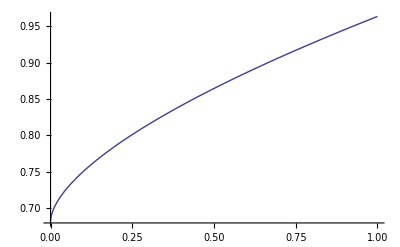

```mathematica
Plot[(3 3^(1/3))/(4 2^(2/3)) + 3^(1/3)/2^(2/3)(x/(24*6^(1/3)))^(1/2)+(7 2^(1/3))/(3 3^(1/6))(x/(24 6^(1/3)))^(3/4),{x,0,1}]
```

#### ρ expasion in terms of πT

```mathematica
Simplify[ρ,Assumptions->{m>0}]
ρexpn = Series[(%/.x->1-η),{η,0,4}]
```

(√2 m^(3/4) x)/3^(1/4)

(√2 m^(3/4))/3^(1/4)-(√2 m^(3/4) η)/3^(1/4)+O[η]^5

```mathematica
Simplify[piT[rhrh[m,x]^(1/2),ρ]^2 ρmax^(1/3),Assumptions->{m>0}]
%/.x->1-η
Zexpn = FullSimplify[Series[(%/.x->1-η),{η,0,5}],Assumptions->{η>0}]
```

(2^(1/6) m^(3/4) (1+(-x^2+√(-1+x^4))^(2/3)) (1+(x^2 (x^2-√(-1+x^4)))/((1+(-x^2+√(-1+x^4))^(2/3))^3))^2)/(3^(7/12) (-x^2+√(-1+x^4))^(1/3))

(2^(1/6) m^(3/4) (1+(√(-1+(1-η)^4)-(1-η)^2)^(2/3)) (1+((-√(-1+(1-η)^4)+(1-η)^2) (1-η)^2)/((1+(√(-1+(1-η)^4)-(1-η)^2)^(2/3))^3))^2)/(3^(7/12) (√(-1+(1-η)^4)-(1-η)^2)^(1/3))

4 2^(1/6) 3^(5/12) m^(3/4) η-(56 (2^(1/6) m^(3/4)) η^(3/2))/(3 3^(1/12))+(194 2^(1/6) m^(3/4) η^2)/(3 3^(7/12))-(1810 (2^(1/6) m^(3/4)) η^(5/2))/(27 3^(1/12))+(46772 2^(1/6) m^(3/4) η^3)/(243 3^(7/12))-(169373 m^(3/4) η^(7/2))/(486 (2^(5/6) 3^(1/12)))+(991009 2^(1/6) m^(3/4) η^4)/(2187 3^(7/12))-(358505111 m^(3/4) η^(9/2))/(472392 (2^(5/6) 3^(1/12)))+(18235190 2^(1/6) m^(3/4) η^5)/(19683 3^(7/12))-(100142628391 m^(3/4) η^(11/2))/(68024448 (2^(5/6) 3^(1/12)))+O[η]^6

```mathematica
Simplify[ρexpn - ρmax-(-(√2 m^(3/4))/3^(1/4))(4 2^(1/6) 3^(5/12) m^(3/4) )^-1 Zexpn,Assumptions->{m>0}]
```

-(14 (√2 m^(3/4)) η^(3/2))/(3 3^(3/4))+(97 m^(3/4) η^2)/(9 √2 3^(1/4))-(905 m^(3/4) η^(5/2))/(27 (√2 3^(3/4)))+(11693 √2 m^(3/4) η^3)/(729 3^(1/4))-(169373 m^(3/4) η^(7/2))/(1944 (√2 3^(3/4)))+(991009 m^(3/4) η^4)/(13122 √2 3^(1/4))-(358505111 m^(3/4) η^(9/2))/(1889568 (√2 3^(3/4)))+O[η]^5

```mathematica
(-(√2 m^(3/4))/3^(1/4))(4 2^(1/6) 3^(5/12) m^(3/4) )^-1
```

```mathematica
-1/(2 6^(2/3))-(-1/8)(3/4)^(-2/3)
```

0

```mathematica
1/12 6^(1/3)
```

1/(2 6^(2/3))

```mathematica
(-(√2 m^(3/4))/3^(1/4))(4 2^(1/6) 3^(5/12) m^(3/4) )^-1
```

(√2 m^(3/4))/3^(1/4)-(14 (√2 m^(3/4)) η^(3/2))/(3 3^(3/4))+(97 m^(3/4) η^2)/(9 √2 3^(1/4))-(905 m^(3/4) η^(5/2))/(27 (√2 3^(3/4)))+(11693 √2 m^(3/4) η^3)/(729 3^(1/4))-(169373 m^(3/4) η^(7/2))/(1944 (√2 3^(3/4)))+(991009 m^(3/4) η^4)/(13122 √2 3^(1/4))-(358505111 m^(3/4) η^(9/2))/(1889568 (√2 3^(3/4)))+(9117595 m^(3/4) η^5)/(59049 √2 3^(1/4))-(100142628391 m^(3/4) η^(11/2))/(272097792 (√2 3^(3/4)))+O[η]^6

```mathematica
(-1)^(2/3)
```

(-1)^(2/3)

### High-T expansion

```mathematica
Simplify[eps[m]/ρ^(4/3),Assumptions->{m>0}]
YHTexpn = Series[%,{x,0,10}]
```

(3 3^(1/3))/(4 2^(2/3) x^(4/3))

(3 3^(1/3))/(4 2^(2/3) x^(4/3))+O[x]^(31/3)

```mathematica
Simplify[piT[rhrh[m,x]^(1/2),ρ]^4/ρ^(4/3),Assumptions->{m>0}]
XHTexpn = FullSimplify[Series[%,{x,0,10}],Assumptions->{x>0}]
```

((1+(-x^2+√(-1+x^4))^(2/3))^2 (1+(x^2 (x^2-√(-1+x^4)))/((1+(-x^2+√(-1+x^4))^(2/3))^3))^4)/(6^(2/3) x^(4/3) (-x^2+√(-1+x^4))^(2/3))

3^(1/3)/(2^(2/3) x^(4/3))+Root[-4+3 #1^6&,1] x^(2/3)+(5 x^(14/3))/(81 2^(2/3) 3^(1/6))+(7 x^(20/3))/(81 6^(2/3))+(35 x^(26/3))/(972 2^(2/3) 3^(1/6))+O[x]^(31/3)

```mathematica
YHTexpn -(3 3^(1/3))/(4 2^(2/3))( XHTexpn/(3^(1/3)/2^(2/3)))//FullSimplify
```

(3^(5/6) x^(2/3))/(2 2^(2/3))-(5 x^(14/3))/(108 (2^(2/3) 3^(1/6)))-(7 x^(20/3))/(108 6^(2/3))-(35 x^(26/3))/(1296 (2^(2/3) 3^(1/6)))+O[x]^(31/3)

```mathematica
YHTexpn -(3 3^(1/3))/(4 2^(2/3))( XHTexpn/(3^(1/3)/2^(2/3)))+3/4 Root[-4+3 #1^6&,1]( XHTexpn/(3^(1/3)/2^(2/3)))^(-1/2)//FullSimplify
```

Root[3+32 #1^3&,1] x^(8/3)-(43 x^(14/3))/(54 (2^(2/3) 3^(1/6)))-(137 x^(20/3))/(108 6^(2/3))-(223 x^(26/3))/(324 (2^(2/3) 3^(1/6)))+O[x]^(31/3)

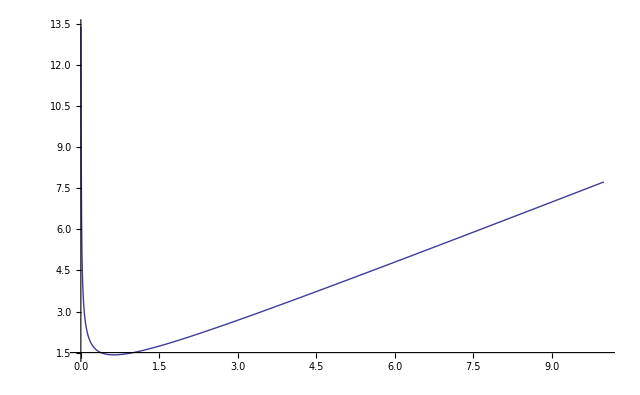

```mathematica
Plot[(3 3^(1/3))/(4 2^(2/3))( x/(3^(1/3)/2^(2/3)))-3/4 Root[-4+3 #1^6&,1]( x/(3^(1/3)/2^(2/3)))^(-1/2),{x,0,10}]
```

### Plots

```mathematica
RNTHERMOrhopiTvsrhoepsLIST = Flatten[Table[{rhtable[[i,j,2]]^(4/3)/piT[rhtable[[i,j,3]], rhtable[[i,j,2]]]^4,rhtable[[i,j,2]]^(4/3)/eps[rhtable[[i,j,1]]]},{i,1,1},{j,1,NUMj+1}],1];
```

```mathematica
ListPlot[RNTHERMOrhopiTvsrhoepsLIST]
```

-Graphics-

```mathematica
CUT = 2000
```

2000

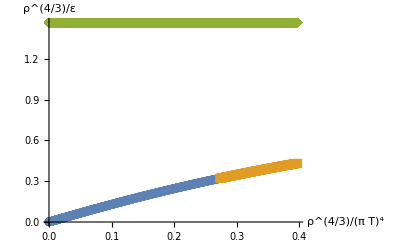

```mathematica
ListPlot[{RNTHERMOrhopiTvsrhoepsLIST[[1;;CUT 4/5]],RNTHERMOrhopiTvsrhoepsLIST[[4 CUT/5;;CUT]],Table[{RNTHERMOrhopiTvsrhoepsLIST[[i,1]],(4/3)^(4/3)},{i,1,Length[RNTHERMOrhopiTvsrhoepsLIST]}][[1;;CUT]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"ρ^(4/3)/(π T)^4","ρ^(4/3)/ε"},AxesStyle->Large,Joined ->True]
```

```mathematica
RNTHERMOTepsvsepsrhoLIST = Flatten[Table[{piT[rhtable[[i,j,3]], rhtable[[i,j,2]]]^4/eps[rhtable[[i,j,1]]],eps[rhtable[[i,j,1]]]/rhtable[[i,j,2]]^(4/3)},{i,1,1},{j,1,NUMj+1}],1];
```

Power::infy: Infinite expression 1/0 encountered.

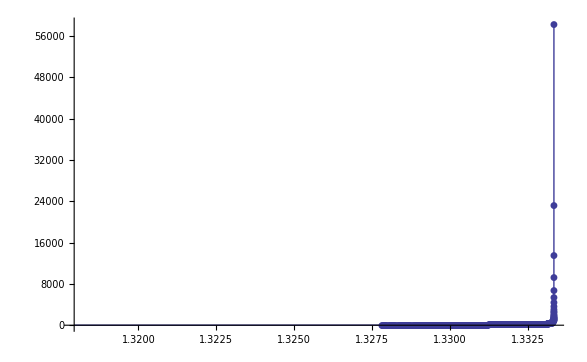

```mathematica
ListPlot[{RNTHERMOTepsvsepsrhoLIST[[1;;501]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"(π T)^4/ε","ε/ρ^(4/3)"},AxesStyle->Large,Joined ->True]
```

```mathematica
RNTHERMOTrhovsepsrhoLIST = Flatten[Table[{piT[rhtable[[i,j,3]], rhtable[[i,j,2]]]^4/rhtable[[i,j,2]]^(4/3),eps[rhtable[[i,j,1]]]/rhtable[[i,j,2]]^(4/3)},{i,1,1},{j,1,NUMj+1}],1];
```

Power::infy: Infinite expression 1/0 encountered.

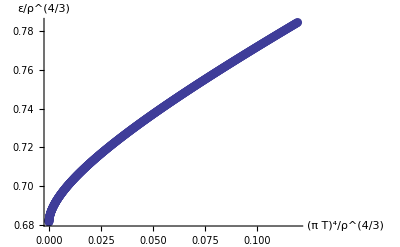

```mathematica
ListPlot[{RNTHERMOTrhovsepsrhoLIST[[4500;;5001]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"(π T)^4/ρ^(4/3)","ε/ρ^(4/3)"},AxesStyle->Large]
```

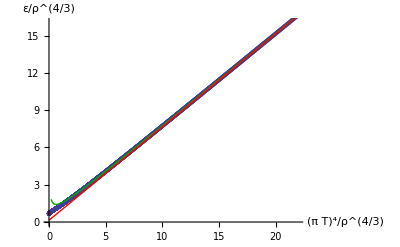

```mathematica
Show[ListPlot[RNTHERMOTrhovsepsrhoLIST[[;;5001]]],Plot[(3 3^(1/3))/(4 2^(2/3)) + 3^(1/3)/2^(2/3)1/(√(24*6^(1/3))) (x)^(1/2),{x,0,0.2},PlotStyle->{Darker[Red],Thick}],Plot[(3 3^(1/3))/(4 2^(2/3))( x/(3^(1/3)/2^(2/3)))-3/4 Root[-4+3 #1^6&,1]( x/(3^(1/3)/2^(2/3)))^(-1/2),{x,0.2,25},PlotStyle->{Darker[Green],Thick}],Plot[ 0.14+3/4 x,{x,0,25},PlotStyle->{Thick,Red}],AxesLabel->{"(π T)^4/ρ^(4/3)","ε/ρ^(4/3)"},AxesStyle->Large]
```

```mathematica
ClearAll[simpleLegend]
simpleLegend[legendItems__,pos_]:=Module[{legendLine,offset,legend},offset=Module[{s,o,insetpts=10},s=pos/.{Left->0,Right->1,Bottom->0,Top->1};
o=insetpts pos/.{Left->1,Right->-1,Bottom->1,Top->-1};
Offset[o,Scaled[s]]];
legendLine[{lbl_,lineStyle_}]:={Graphics[{lineStyle,Line[{{0,0.2},{1,0.2}}]},ImageSize->{60,25},AspectRatio->0.75],Style[lbl,FontFamily->"Tahoma",FontSize->16,Bold,TextAlignment->Left,LineBreakWithin->False]};
legend=GraphicsGrid[legendLine/@legendItems,Alignment->Left];
Graphics@Inset[legend,offset,pos]];
```

```mathematica
labels={"data","eq1","eq2"};
styles={Directive[Purple],Directive[Orange,Dashed,Thick],Directive[Green,Dotted,Thick]};

depth4=Table[{x,(11024 x^(-0.94232))*RandomReal[{0.4,1.6}]}/.x->10^n,{n,0,5,0.1}];

plot=ListLogLogPlot[Sort[depth4],PlotRange->{{1,50000},{1,50000}},Joined->True,PlotStyle->styles[[1]],BaseStyle->{FontSize->14}];

line=LogLogPlot[11024 x^(-0.94232),{x,1,100000},PlotStyle->styles[[2]]];
line2=LogLogPlot[31862 x^(-1.07076),{x,1,100000},PlotStyle->styles[[3]]];

Show[plot,line,line2,simpleLegend[Thread@{labels,styles},{Right,Top}]]
```

-Graphics-

```mathematica
labels={"High-T","Low-T"};
styles={Directive[Darker[Blue],AbsoluteThickness[2.5],Dotted],Directive[Red,AbsoluteThickness[2.5],Dashed]};
ticks = {{{0.02,Null,{0.01,0}},{0.03,Null,{0.01,0}},{0.04,Null,{0.01,0}},{0.05,Null,{0.01,0}},{0.06,Null,{0.01,0}},{0.07,Null,{0.01,0}},{0.08,Null,{0.01,0}},{0.09,Null,{0.01,0}},{0.1,0.1,{0.015,0}},{0.2,Null,{0.01,0}},{0.3,Null,{0.01,0}},{0.4,Null,{0.01,0}},{0.5,Null,{0.01,0}},{0.6,Null,{0.01,0}},{0.7,Null,{0.01,0}},{0.8,Null,{0.01,0}},{0.9,Null,{0.01,0}},{1.0,1,{0.015,0}},{2,Null,{0.01,0}},{3,Null,{0.01,0}},{4,Null,{0.01,0}},{5,Null,{0.01,0}},{6,Null,{0.01,0}},{7,Null,{0.01,0}},{8,Null,{0.01,0}},{9,Null,{0.01,0}},{10,10,{0.015,0}},{20,Null,{0.01,0}},{30,Null,{0.01,0}},{40,Null,{0.01,0}},{50,Null,{0.01,0}},{60,Null,{0.01,0}},{70,Null,{0.01,0}},{80,Null,{0.01,0}},{90,Null,{0.01,0}},{100,100,{0.015,0}}},{{0.1,Null,{0.01,0}},{0.2,Null,{0.01,0}},{0.3,Null,{0.01,0}},{0.4,Null,{0.01,0}},{0.5,Null,{0.01,0}},{0.6,Null,{0.01,0}},{0.7,Null,{0.01,0}},{0.8,Null,{0.01,0}},{0.9,Null,{0.01,0}},{1.0,1,{0.015,0}},{2,Null,{0.01,0}},{3,Null,{0.01,0}},{4,Null,{0.01,0}},{5,Null,{0.01,0}},{6,Null,{0.01,0}},{7,Null,{0.01,0}},{8,Null,{0.01,0}},{9,Null,{0.01,0}},{10,10,{0.015,0}},{20,Null,{0.01,0}},{30,Null,{0.01,0}},{40,Null,{0.01,0}},{50,Null,{0.01,0}},{60,Null,{0.01,0}},{70,Null,{0.01,0}},{80,Null,{0.01,0}},{90,Null,{0.01,0}},{100,100,{0.015,0}}}};
Show[LogLogPlot[ 3/4 x,{x,1.5,100},PlotStyle->styles[[1]],PlotRange->{{0.01,100},{.1,100}},Ticks->ticks],LogLogPlot[(3 3^(1/3))/(4 2^(2/3)) + 3^(1/3)/2^(2/3)1/(√(24*6^(1/3))) (x)^(1/2),{x,0.00001,1.0},PlotStyle->styles[[2]]],ListLogLogPlot[RNTHERMOTrhovsepsrhoLIST[[;;]],Joined->True,PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]],simpleLegend[Thread@{labels,styles},{.2,.95}],ImageSize->{{400},{300}},AspectRatio->Full,AxesLabel->{Style["  (πT)^4/ρ^(4/3)",28],Style["ε/ρ^(4/3)\n",28,LineSpacing->{0,10}]},AxesStyle->Directive[Black,22]]
```

-Graphics-

```mathematica
(0.8 4/3)^(-4/3)
```

0.917547

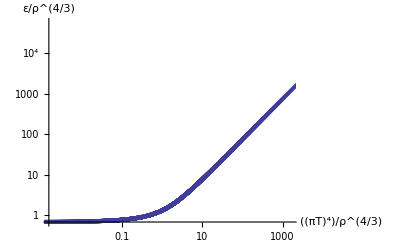

```mathematica
ListLogLogPlot[RNTHERMOTrhovsepsrhoLIST[[2;;]],AxesLabel->{Style["  (πT)^4/ρ^(4/3)",28],Style["ε/ρ^(4/3)\n",28,LineSpacing->{0,10}]},PlotRange->All]
```

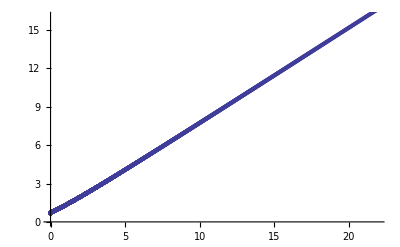

```mathematica
ListPlot[RNTHERMOTrhovsepsrhoLIST[[2;;]]]
```

```mathematica
y = Interpolation[RNTHERMOTrhovsepsrhoLIST[[2;;]]]
yD = Derivative[1][y]
```

InterpolatingFunction[{{1.17791×10^-62,77680.8}},<>]

InterpolatingFunction[{{1.17791×10^-62,77680.8}},<>]

```mathematica
yD = Derivative[1][y]
```

InterpolatingFunction[{{1.17791×10^-62,77680.8}},<>]

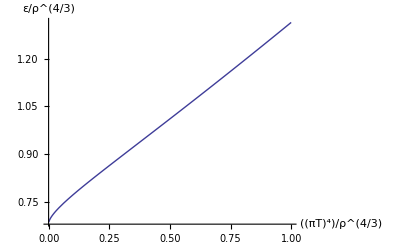

```mathematica
Plot[y[x],{x,0.001,1},PlotRange->All,PlotStyle->Thick,]
```

```mathematica
yD[0.35]
```

0.585988

```mathematica
(yD[0.35])^(-1/4)
```

1.14295

```mathematica
(.75)^(-1/4)
```

1.07457

```mathematica
Abs[(1.074704026705499-1.1429515480159265)/1.1429515480159265]
```

0.0597116

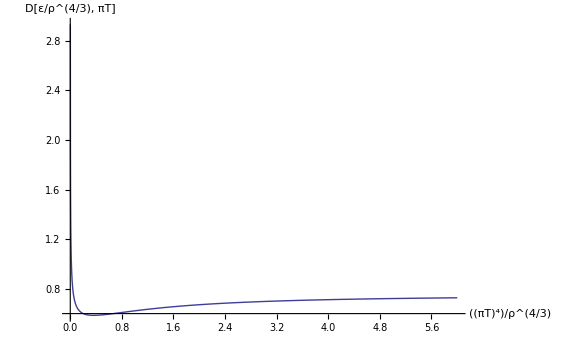

```mathematica
Plot[yD[x],{x,0.001,6},PlotRange->All,PlotStyle->Thick,AxesLabel->{Style["  (πT)^4/ρ^(4/3)",28],Style["D[ε/ρ^(4/3), πT]\n",28,LineSpacing->{0,10}]},AxesStyle->Large]
```

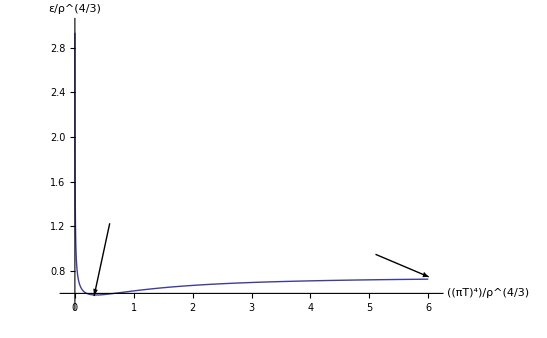

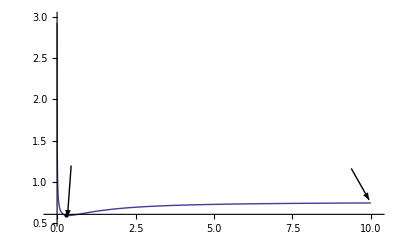

```mathematica
3/4
```

3/4

```mathematica
y[.35]
```

0.922372

```mathematica
NSolve[(y[a]==0.92/.a->x),x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→InverseFunction[InterpolatingFunction[{{1.17791×10^-62,77680.8}},<>],1,1][0.92]}}

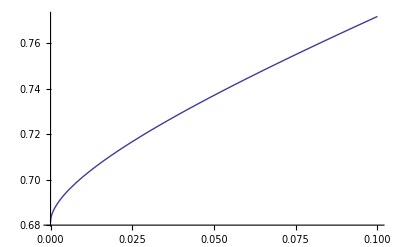

```mathematica
Plot[y[x],{x,0,0.1}]
```

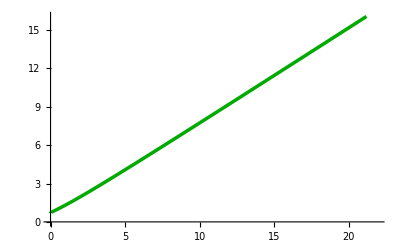

```mathematica
ListPlot[RNTHERMOTrhovsepsrhoLIST[[;;]],Joined->True,PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]]]
```

```mathematica
FullSimplify[3^(1/3)/2^(2/3)1/(√(24*6^(1/3)))]
```

1/(4 6^(1/3))

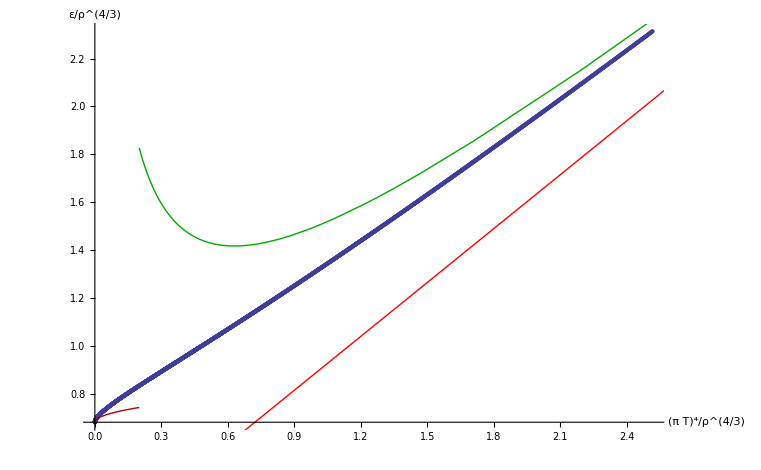

```mathematica
Show[ListPlot[RNTHERMOTrhovsepsrhoLIST[[2000;;5001]]],Plot[(3 3^(1/3))/(4 2^(2/3)) + 3^(1/3)/2^(2/3)1/(√(24*6^(1/3))) (x)^(1/2),{x,0,0.2},PlotStyle->{Darker[Red],Thick}],Plot[(3 3^(1/3))/(4 2^(2/3))( x/(3^(1/3)/2^(2/3)))-3/4 Root[-4+3 #1^6&,1]( x/(3^(1/3)/2^(2/3)))^(-1/2),{x,0.2,25},PlotStyle->{Darker[Green],Thick}],Plot[0.14+ 3/4 x,{x,0,3500},PlotStyle->{Thick,Red}],AxesLabel->{"(π T)^4/ρ^(4/3)","ε/ρ^(4/3)"},AxesStyle->Large]
```

```mathematica
RNTHERMOepsTvsrhoepsLIST = Flatten[Table[{(piT[rhtable[[i,j,3]], rhtable[[i,j,2]]]^4/eps[rhtable[[i,j,1]]])^-1,(eps[rhtable[[i,j,1]]]/rhtable[[i,j,2]]^(4/3))^-1},{i,1,3},{j,1,99}],1];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
ρmax^(4/3)/eps[m]/.m->1//N
```

1.46752

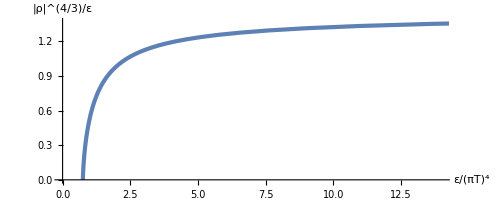

```mathematica
ListPlot[{RNTHERMOepsTvsrhoepsLIST[[1;;96]]},PlotRange->{{0,14},Automatic},Joined ->True,PlotStyle->{AbsoluteThickness[3]},AspectRatio->Full,TicksStyle->Thick,AxesStyle->Directive[18,Black],AxesLabel ->{Style[" ε/(πT)^4",22,Black],Style["|ρ|^(4/3)/ε",22,Black]},ImageSize->{{500},{300}}]
```

```mathematica
RNTHERMOpiTrhovsepsrhoLIST = Flatten[Table[{piT[rhtable[[i,j,3]], rhtable[[i,j,2]]]^4/rhtable[[i,j,2]]^(4/3),eps[rhtable[[i,j,1]]]/rhtable[[i,j,2]]^(4/3)},{i,1,9},{j,1,99}],1];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

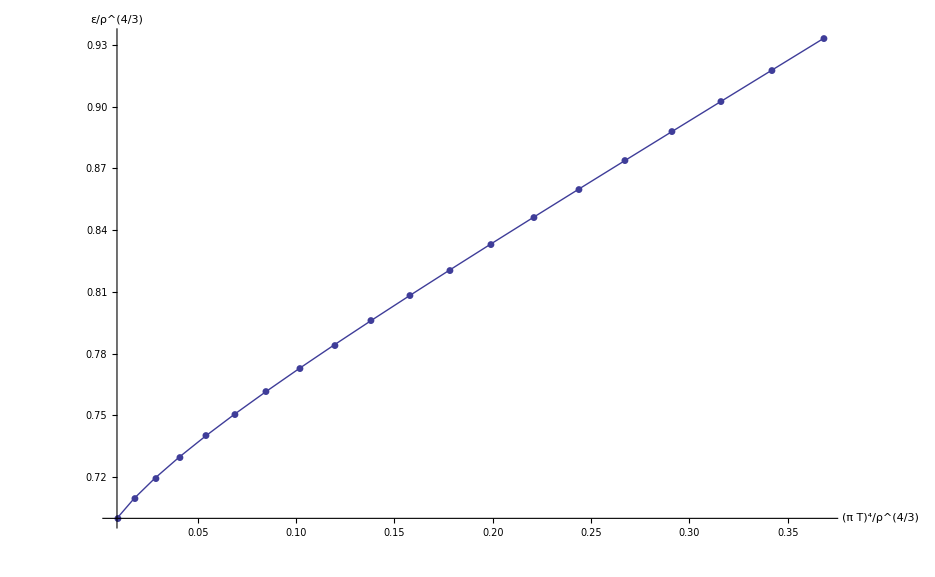

```mathematica
ListPlot[{RNTHERMOpiTrhovsepsrhoLIST[[80;;99]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"(π T)^4/ρ^(4/3)","ε/ρ^(4/3)"},AxesStyle->Large,Joined ->True]
```

```mathematica
RNTHERMOpiTrhovsepsrhoLIST[[99]]
```

{0.00889746,0.700025}

```mathematica
(3/4)^(4/3)//N
```

0.68142

```mathematica
((.99)^(-4/3))*ρmax/.m->1
```

1.08907

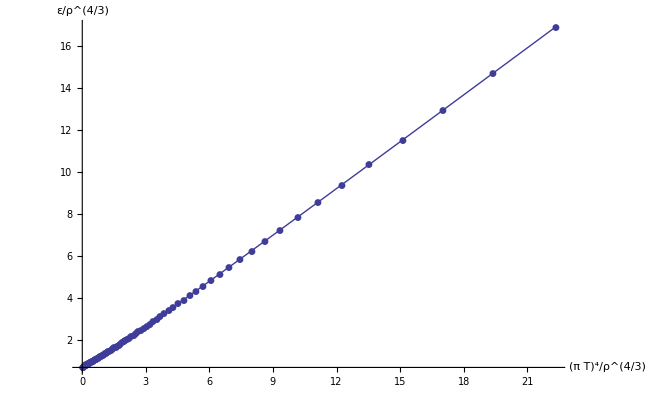

```mathematica
ListPlot[{RNTHERMOpiTrhovsepsrhoLIST[[10;;99]]},PlotRange->All,PlotMarkers->Automatic,AxesLabel->{"(π T)^4/ρ^(4/3)","ε/ρ^(4/3)"},AxesStyle->Large,Joined ->True]
```

### How constant?

#### f

```mathematica
rhtable[[1,81,2]]/ρmax/.m->rhtable[[1,81,1]]//N
```

0.8

We know that T = f(eps/rho^4/3) eps^1/4,  how much does f change over the region rho = 0% to 80%?

```mathematica
1/π piT[rhtable[[1,1,3]],rhtable[[1,1,2]]]/(eps[rhtable[[1,1,1]]] )^(1/4)
```

0.342046

```mathematica
1/π piT[rhtable[[1,81,3]],rhtable[[1,81,2]]]/(eps[rhtable[[1,81,1]]] )^(1/4)
```

0.248671

```mathematica
(0.3420462326952754-0.24867106798756816)/0.3420462326952754
```

0.27299

```mathematica
1/π piT[rhtable[[20,1,3]],rhtable[[20,1,2]]]/(eps[rhtable[[20,1,1]]] )^(1/4)
```

0.342046

```mathematica
1/π piT[rhtable[[20,81,3]],rhtable[[20,81,2]]]/eps[rhtable[[20,81,1]]]^(1/4)
```

0.248671

```mathematica
(0.3420462326952754-0.2486710679875682)/0.3420462326952754
```

0.27299

#### h

#### f*h

[h(0%)*f(0%) - h(80%) f(80%)]/[h(0%)*f(0%)] @ 1% teq

```mathematica
(2.1707440318128075*0.3420462326952754-2.2547881680039663*0.2486710679875682)/(2.1707440318128075*0.3420462326952754)
```

0.244842

[h(0%)*f(0%) - h(80%) f(80%)]/[h(0%)*f(0%)] @ 5% teq

```mathematica
(1.98648*0.3420462326952754 - 2.01497*0.2486710679875682)/(1.98648*0.3420462326952754)
```

0.262563

```mathematica
24/10//N
```

2.4

```mathematica
26/17//N
```

1.52941

## Finding other constant precentages of extremality

Want 80% at constant temp, starting from m = 1, 0%

Try m = 1.5

```mathematica
eps[m]/.m->1.5
```

1.125

```mathematica
Solve[piT[rh,ρ]==1,ρ]
```

{{ρ→-√6 √(-rh^5+rh^6)},{ρ→√6 √(-rh^5+rh^6)}}

```mathematica
Solve[0.8ρmax ==ρ/.ρ->√6 √(-rh^5+rh^6),m]
```

{{m→(-2.01978-3.49837 ⅈ) rh^(10/3) (-1.+1. rh)^(2/3)},{m→(-2.01978+3.49837 ⅈ) rh^(10/3) (-1.+1. rh)^(2/3)},{m→4.03957 rh^(10/3) (-1.+1. rh)^(2/3)}}

```mathematica
(√6 √(-rh^5+rh^6))^2
```

6 (-rh^5+rh^6)

```mathematica
Solve[0.8ρmax == ρ/.m->1.5]
```

{{ρ→1.16518}}

```mathematica
rhlist[[1,2,3]]
```

Part::partw: Part 3 of √0.57735\ m/(-√m^3)^1/3 + 0.57735\ (-√m^3)^1/3 does not exist.

{-1. √((0.57735 m)/((-√(m^3))^(1/3))+0.57735 (-√(m^3))^(1/3)),√((0.57735 m)/((-√(m^3))^(1/3))+0.57735 (-√(m^3))^(1/3)),-1. √(-((0.288675-0.5 ⅈ) m)/((-√(m^3))^(1/3))-(0.288675+0.5 ⅈ) (-√(m^3))^(1/3)),√(-((0.288675-0.5 ⅈ) m)/((-√(m^3))^(1/3))-(0.288675+0.5 ⅈ) (-√(m^3))^(1/3)),-1. √(-((0.288675+0.5 ⅈ) m)/((-√(m^3))^(1/3))-(0.288675-0.5 ⅈ) (-√(m^3))^(1/3)),√(-((0.288675+0.5 ⅈ) m)/((-√(m^3))^(1/3))-(0.288675-0.5 ⅈ) (-√(m^3))^(1/3))}⟦1,2,3⟧

```mathematica
templist = Flatten[Table[{rhtable[[i,j,1]],piT[rhtable[[i,j,3]],rhtable[[i,j,2]]]},{i,1,20},{j,1,101}],1];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

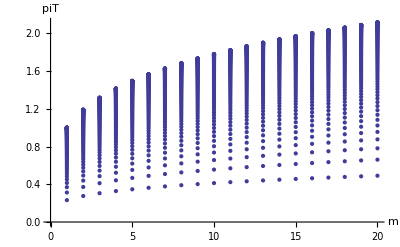

```mathematica
ListPlot[templist,AxesLabel->{"m","piT"}]
```

```mathematica
0.8ρmax /.m->2
```

1.44576

```mathematica
rhtableRN80 = Table[rhtable[[i,81]],{i,1,20}]
```

{{1,0.859656,0.916983},{2,1.44576,1.09048},{3,1.95959,1.20682},{4,2.43147,1.29681},{5,2.87443,1.37121},{6,3.29563,1.43516},{7,3.69954,1.49154},{8,4.08924,1.54218},{9,4.4669,1.58826},{10,4.8342,1.63065},{11,5.19241,1.66997},{12,5.54256,1.7067},{13,5.88548,1.74119},{14,6.22187,1.77375},{15,6.55229,1.80461},{16,6.87725,1.83397},{17,7.19716,1.86197},{18,7.51241,1.88877},{19,7.8233,1.91447},{20,8.13012,1.93918}}

```mathematica
rhtableRN80[[i,2]]
```

3.69954

```mathematica
m->rhtable[[3,1]]
```

m→{3,0.,1.31607}

```mathematica
ρmax
```

(√2 (m^3)^(1/4))/3^(1/4)

Check.

```mathematica
Table[((√2 (rhtableRN80[[i,1]]^3)^(1/4))/3^(1/4))^-1 rhtableRN80[[i,2]],{i,1,20}]
```

{0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8,0.8}

```mathematica
templistRN80 = Table[{rhtableRN80[[i,1]],piT[rhtableRN80[[i,3]],rhtableRN80[[i,2]]]},{i,1,20}]
```

{{1,0.72701},{2,0.864566},{3,0.956799},{4,1.02815},{5,1.08713},{6,1.13783},{7,1.18254},{8,1.22268},{9,1.25922},{10,1.29283},{11,1.324},{12,1.35312},{13,1.38047},{14,1.40628},{15,1.43075},{16,1.45402},{17,1.47623},{18,1.49747},{19,1.51785},{20,1.53744}}

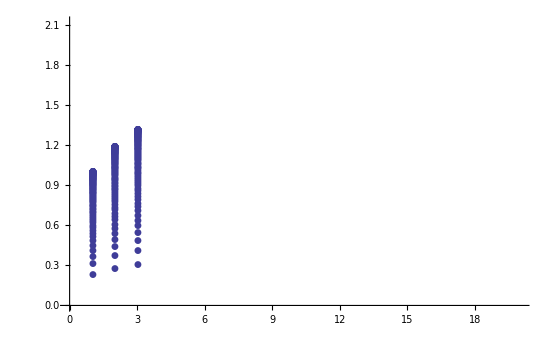

```mathematica
ListPlot[{templist,,templistRN80},PlotMarkers->Automatic]
```

```mathematica
Clear[y]
```

```mathematica
ExtemalityRN80funct= Interpolation[templistRN80]
```

InterpolatingFunction[{{1.,20.}},<>]

```mathematica
FindRoot[y[x]- 1.0==0,{x,3}]
```

{x→3.57744}

```mathematica
3.577442444170634
```

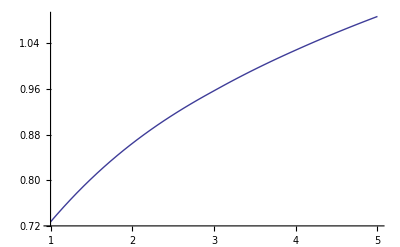

```mathematica
Plot[y[x],{x,1,5}]
```

```mathematica
y[3.5]
```

0.994551

```mathematica
rhtableRN80[[4]]
```

{4,2.43147,1.29681}

## GuassianU B, RN Black Brane QNMs

Extremal charge is when f3^4 = 4/3 m^3 L^2

So max f3 when m = L = 1, is

```mathematica
(4/3)^(1/4)//N
```

1.07457

## GaussianR B (amp 0.0005), f3 = 0.0 (0%), fxy =0 QNM1 = {??} extended *

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS30000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS30000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

-1.2368×10^-38

```mathematica
Max[Abs[lambshiftlist]]
```

6.27127×10^-11

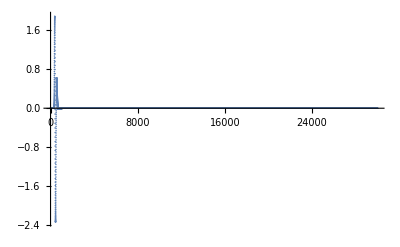

```mathematica
ListPlot[(b4list),PlotRange->All]
```

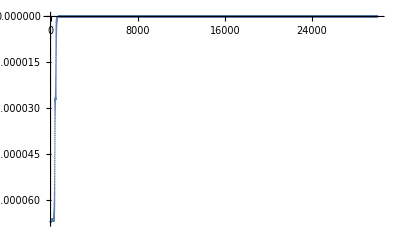

```mathematica
ListPlot[lamblist, PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.40463×10^-80

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

### QNM1 = {3.11346 ± 0.000145, 2.74964 ± 0.00018}

```mathematica
Length[tlist]
```

30001

```mathematica
Length[b4list]
```

30001

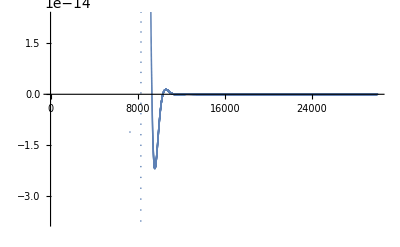

```mathematica
ListPlot[b4list]
```

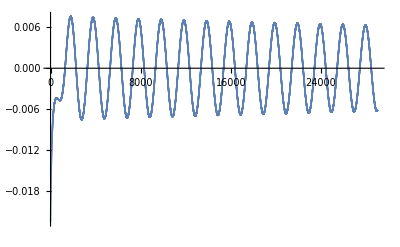

```mathematica
ListPlot[ⅇ^(2.74tlist[[1000;;]])((b4list)[[1000;;]]),PlotRange->All]
```

```mathematica
Length[b4list]
```

30001

```mathematica
b4plotlistshift = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
```

```mathematica
y=Interpolation[b4plotlist]
```

InterpolatingFunction[{{0., 30.}}, <>]

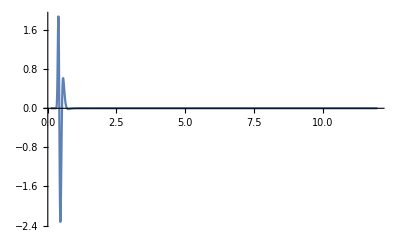

```mathematica
Plot[y[x],{x,0.1,12},PlotRange->All]
```

```mathematica
guesslist = {2,3.5,4.5,5.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}
```

{2,3.5,4.5,5.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

{2.2864,3.26261,4.2655,5.27365,6.28068,7.28777,8.29487,9.30197,10.3091,11.3162,12.3233,13.3304,14.3375,15.3446,16.3517,17.3588,18.3659,19.3729,20.38,21.3871,22.3942,23.4013,24.4084,25.4155,26.4226,27.4297,28.4368,29.4439}

{0.976216,1.00288,1.00815,1.00704,1.00709,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071,1.0071}

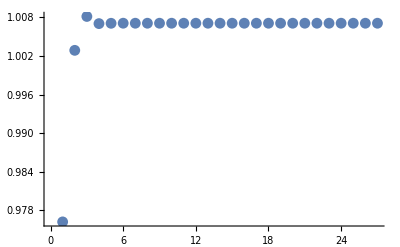

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 4;
endroot = Length[templist]-1;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.01419

```mathematica
μ1 = 2π/λ1
```

3.11946

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.000179836,0.0000243801,-0.0000162755,-9.1769×10^-6,-9.33079×10^-6,-9.43352×10^-6,-9.40868×10^-6,-9.40191×10^-6,-9.41849×10^-6,-9.41058×10^-6,-9.41403×10^-6,-9.4163×10^-6,-9.41181×10^-6,-9.40519×10^-6,-9.39746×10^-6,-9.42766×10^-6,-9.40919×10^-6,-9.40711×10^-6,-9.40796×10^-6,-9.42478×10^-6,-9.40467×10^-6,-9.4105×10^-6,-9.41224×10^-6}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.0000389907

```mathematica
x7
```

8.29487

```mathematica
n7
```

8

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.74875

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-5.45516

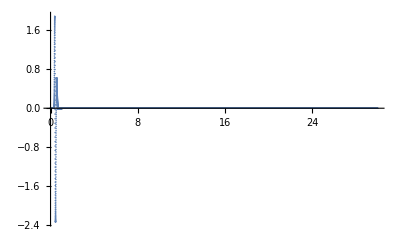

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

```mathematica
Length[b4plotlist]
```

30001

```mathematica
ii = 5;
if = 14;
ji = 1;
jf = 8;
```

```mathematica
tempmtx = Table[FindFit[b4plotlist[[5000+100i;;30000- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{{A,0.056},{ν,-2.7}},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12],{i,ii,if},{j,ji,jf}];
%//MatrixForm
```

((A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597) | (A→-0.00563853
ν→-2.74597)
(A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624) | (A→-0.00564729
ν→-2.74624)
(A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645) | (A→-0.0056544
ν→-2.74645)
(A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661) | (A→-0.00565984
ν→-2.74661)
(A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671) | (A→-0.00566347
ν→-2.74671)
(A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677) | (A→-0.00566567
ν→-2.74677)
(A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681) | (A→-0.00566711
ν→-2.74681)
(A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679) | (A→-0.00566641
ν→-2.74679)
(A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676) | (A→-0.00566519
ν→-2.74676)
(A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677) | (A→-0.00566557
ν→-2.74677))

```mathematica
isubi = 2;
isubf = if-ii-1;
jsubi = 5;
jsubf = 8;
```

```mathematica
tot = (isubf-isubi+1)(jsubf-jsubi+1)
```

28

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2,2]],{i,isubi,isubf},{j,jsubi,jsubf}]/(tot)
```

-2.74663

```mathematica
σν1 = √(1/(24) Sum[(tempmtx[[i,j]][[2,2]]-ν1)^2,{i,4,7},{j,3,8}])
```

0.000126026

```mathematica
{μ1 + x σμ1, ν1 + x σν1}
```

{3.11946+0.0000389907 x,-2.74663+0.000126026 x}

```mathematica
b4listshift =Table[b4plotlist[[k,2]],{k,1,Length[b4plotlist]}];
```

```mathematica
b4tlistshift = Table[b4plotlist[[k,1]],{k,1,Length[b4plotlist]}];
```

```mathematica
Max[Table[Abs[b4listshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]-(A ⅇ^(ν b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]) Cos[-ϕ1] 2 Cos[μ1 b4tlistshift[[2000+100*(i+isubi + ii - 1);;6700- 100*(j+jsubi + ji - 1)]]+ϕ1]/.{tempmtx[[i,j]][[1]],tempmtx[[i,j]][[2]]})],{i,1,1},{j,1,1}]]
```

9.71925×10^-8

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.35208+0.0000418982 x,-2.95144+0.000135423 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.11946+0.0000389907 x,-2.74663+0.000126026 x}

```mathematica
π T
```

1.

```mathematica
omegatilde = {μ1,ν1}
domegatilde = {σμ1,σν1}
```

{3.11946,-2.74663}

{0.0000389907,0.000126026}

```mathematica
fxy
```

0.

```mathematica
1/3(2(-fxy^2/(4 g^2)-1/4 a2+b4list)+(-1/4 a2-2 b4list))[[-1]]/(T^4)
```

```mathematica
24.352272537603838
```

24.3523

```mathematica
1/3(-3/4 a2)
```

0.25

```mathematica
-3/4 a2/T^4
```

73.0568

## Gaussian B (amp 0.05), f3 = 0.107457 (10%), fxy =0 QNM1 {3.11339, -2.75131} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.107457
```

0.107457

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.107456993182fxy0.0TS0.01NS1400FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.107456993182fxy0.0TS0.01NS1400FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

6.4197×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

6.16222×10^-18

```mathematica
Max[Abs[lambshiftlist]]
```

0.00129046

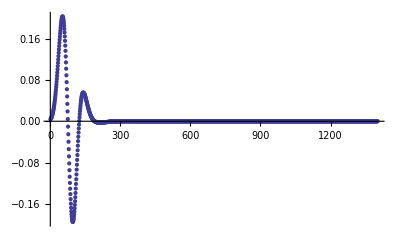

```mathematica
ListPlot[(b4list),PlotRange->All]
```

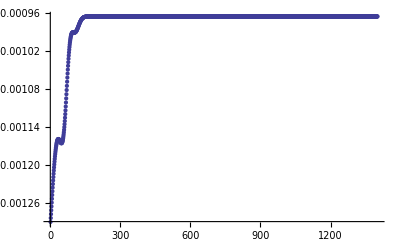

```mathematica
ListPlot[lamblist, PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.317387

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.0538324

```mathematica
chem/T
```

-0.169611

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.10361×10^-37

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.1325

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.244215

### QNM1 {3.11339, -2.75131}

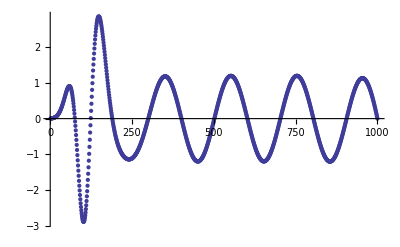

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,14.}},<>]

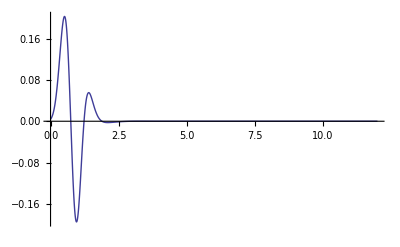

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

{1.88652,2.98676,3.99918,5.00608,6.01531,7.02434,8.03335,9.04237,10.0514,11.0604}

{1.10024,1.01243,1.0069,1.00922,1.00903,1.00902,1.00902,1.00902,1.00905}

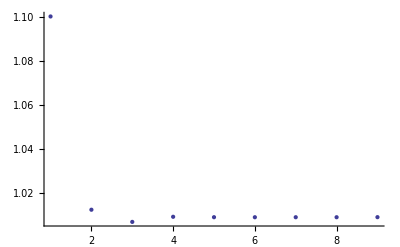

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
n9 = 10;
n10 = 11;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]],x9=FindRoot[y[x],{x,n9}][[1,2]],x10=FindRoot[y[x],{x,n10}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7,x9-x8,x10-x9}
ListPlot[%,PlotRange->All]
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,4,9}]/6
```

2.01812

```mathematica
μ1 = 2π/λ1
```

3.11339

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47447

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.59058

```mathematica
lowcut = 500;
highcut = 1400;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→4.96806,ν1→-2.75131}

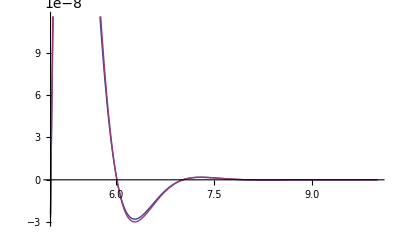

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->5.128462692029635,ν1->-2.74546536671102})},{x,5,10}]
```

```mathematica
Table[FindFit[b4plotlist[[100*i;;1400]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->10000],{i,3,9}]//MatrixForm
```

(A→-3.4655 | ν→-2.65334
A→-4.52031 | ν→-2.73017
A→-4.96806 | ν→-2.75131
A→-4.87932 | ν→-2.74827
A→-4.90261 | ν→-2.74907
A→0. | ν→1.
A→-4.94606 | ν→-2.7501)

## Gaussian B (amp 0.05), f3 = 0.107457 (10%), fxy =0 QNM1 = {3.11346 ± 0.000145, -2.74964 ± 0.00018} extended *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.107457
```

0.107457

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.107456993182fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.107456993182fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-0.99807, -0.996707, -0.992626, -0.985855, -0.97644, -0.964446, -0.949952, -0.933056, -0.91387, -0.892524, -0.869156, -0.843921, -0.816981, -0.788511, -0.75869, « 22 », -0.102946, -0.0880109, -0.0745495, -0.0625151, -0.0518508, -0.0424902, -0.0343586, -0.0273745, -0.0214509, -0.0164967, -0.0124181, -0.00911999, -0.00650765, « 11 »} does not exist.

Part::partw: Part 63 of {-0.99807, -0.996707, -0.992626, -0.985855, -0.97644, -0.964446, -0.949952, -0.933056, -0.91387, -0.892524, -0.869156, -0.843921, -0.816981, -0.788511, -0.75869, « 22 », -0.102946, -0.0880109, -0.0745495, -0.0625151, -0.0518508, -0.0424902, -0.0343586, -0.0273745, -0.0214509, -0.0164967, -0.0124181, -0.00911999, -0.00650765, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-9.9732×10^-8, -9.97045×10^-8, -9.96208×10^-8, -9.94772×10^-8, -9.92678×10^-8, -9.89845×10^-8, -9.86172×10^-8, -9.81542×10^-8, -9.75825×10^-8, -9.68889×10^-8, -9.60604×10^-8, -9.50862×10^-8, -9.39587×10^-8, « 25 », -9.44622×10^-7, -1.08634×10^-6, -1.22482×10^-6, -1.35067×10^-6, -1.45322×10^-6, -1.52162×10^-6, -1.5463×10^-6, -1.52075×10^-6, -1.44307×10^-6, -1.31688×10^-6, -1.15147×10^-6, -9.60646×10^-7, « 11 »} does not exist.

Part::partw: Part 63 of {-9.9732×10^-8, -9.97045×10^-8, -9.96208×10^-8, -9.94772×10^-8, -9.92678×10^-8, -9.89845×10^-8, -9.86172×10^-8, -9.81542×10^-8, -9.75825×10^-8, -9.68889×10^-8, -9.60604×10^-8, -9.50862×10^-8, -9.39587×10^-8, « 25 », -9.44622×10^-7, -1.08634×10^-6, -1.22482×10^-6, -1.35067×10^-6, -1.45322×10^-6, -1.52162×10^-6, -1.5463×10^-6, -1.52075×10^-6, -1.44307×10^-6, -1.31688×10^-6, -1.15147×10^-6, -9.60646×10^-7, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

9.09317×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

1.26153×10^-36

```mathematica
Max[Abs[lambshiftlist]]
```

0.00129046

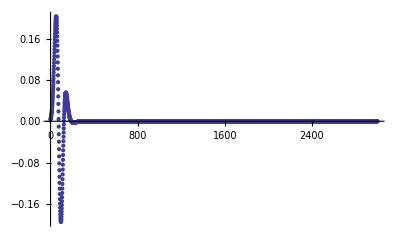

```mathematica
ListPlot[(b4list),PlotRange->All]
```

```mathematica
5*
```

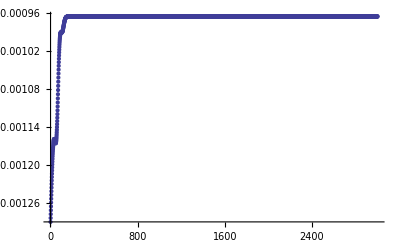

```mathematica
ListPlot[lamblist, PlotRange->All]
```

```mathematica
{3.11346,-2.74964}(4/3)^(1/4)
```

{3.34563,-2.95468}

```mathematica
{3.11346,-2.74964}1/(π T)
```

{3.15048,-2.78234}

```mathematica
π T
```

0.988248

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.317387

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.0538324

```mathematica
chem/T
```

-0.169611

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.49674×10^-75

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.1325

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.244215

### QNM1 = {3.11346 ± 0.000145, 2.74964 ± 0.00018}

```mathematica
{3.11346 + x 0.000145,-2.74964+ x 0.00018}(4/3)^(1/4)//N//Simplify
```

{3.34563+0.000155813 x,-2.95468+0.000193423 x}

```mathematica
{3.11346 + x 0.000145,-2.74964+ x 0.00018}1/(π T)//N//Simplify
```

{3.12251+0.000145422 x,-2.75764+0.000180523 x}

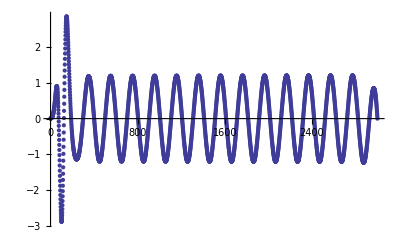

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

```mathematica
4*(3/4)^(1/4)//N
```

3.72242

```mathematica
10*(3/4)^(1/4)//N
```

9.30605

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

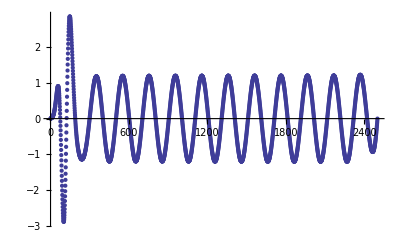

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

{1.10024,1.01243,1.0069,1.00922,1.00903,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00902,1.00901,1.00913,1.00726,1.03955}

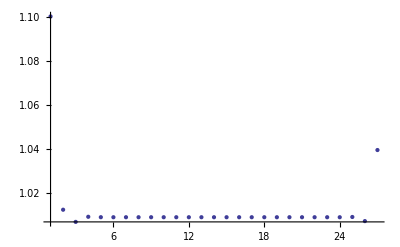

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}];
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.01807

```mathematica
μ1 = 2π/λ1
```

3.11346

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.000583317,9.50435×10^-6,0.0000589101,0.0000427726,0.0000439232,0.0000440561,0.0000440142,0.0000440123,0.0000440137,0.000044015,0.0000440164,0.0000440179,0.0000440193,0.0000440207,0.0000440218,0.0000440226,0.0000440192,0.0000440072,0.000044096,0.0000426918,0.0000652203,-0.000295908}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.000145906

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47463

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.59121

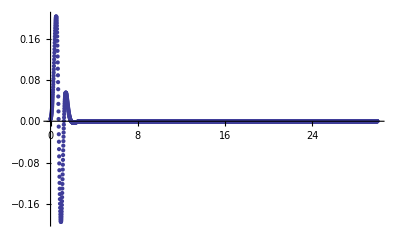

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

(ν→0.999825 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179
ν→0.999931 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247
ν→0.999988 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898
ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936
ν→1. | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496
ν→1. | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975
ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984
ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984
ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975
ν→1. | ν→-2.74958 | ν→-2.74958 | ν→-2.74958 | ν→-2.74958 | ν→-2.74958 | ν→-2.74958 | ν→-2.74959
ν→1. | ν→-2.74935 | ν→-2.74935 | ν→-2.74935 | ν→-2.74935 | ν→-2.74935 | ν→-2.74933 | ν→-5.21878)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999825 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179 | ν→-2.73179
ν→0.999931 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247 | ν→-2.75247
ν→0.999988 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898 | ν→-2.74898
ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936 | ν→-2.74936
ν→1. | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496 | ν→-2.7496
ν→1. | ν→1. | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975
ν→1. | ν→1. | ν→1. | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984
ν→1. | ν→1. | ν→1. | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984 | ν→-2.74984
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.74975 | ν→-2.74975 | ν→-2.74975 | ν→-2.74975
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.74958 | ν→-2.74958 | ν→-2.74959
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.52683)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
tot = (7-4+1)(8-3+1)
```

24

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,4,7},{j,3,8}]/(24)
```

-2.74964

```mathematica
σν1 = √(1/(24) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,4,7},{j,3,8}])
```

0.000180734

QNM = {3.11346 ± 0.000145, 2.74964 ± 0.00018}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.34564+0.000156787 x,-2.95468+0.000194211 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.12252+0.000146331 x,-2.75763+0.000181259 x}

## Gaussian B (amp 0.05), f3 = 0.214913 (20%), fxy =0 QNM1 = {3.09541 ± 0.00018, -2.75859 ± 0.00018} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.2149139
```

0.214914

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.214913986365fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.214913986365fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-0.992211, -0.990868, -0.986847, -0.980176, -0.970898, -0.959075, -0.944784, -0.92812, -0.909192, -0.888122, -0.865047, -0.840117, -0.813489, -0.785333, -0.755826, « 22 », -0.103017, -0.0880746, -0.0746047, -0.0625617, -0.0518891, -0.0425208, -0.0343824, -0.0273924, -0.021464, -0.016506, -0.0124244, -0.00912414, -0.00651024, « 11 »} does not exist.

Part::partw: Part 63 of {-0.992211, -0.990868, -0.986847, -0.980176, -0.970898, -0.959075, -0.944784, -0.92812, -0.909192, -0.888122, -0.865047, -0.840117, -0.813489, -0.785333, -0.755826, « 22 », -0.103017, -0.0880746, -0.0746047, -0.0625617, -0.0518891, -0.0425208, -0.0343824, -0.0273924, -0.021464, -0.016506, -0.0124244, -0.00912414, -0.00651024, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-9.55163×10^-8, -9.54891×10^-8, -9.54062×10^-8, -9.52646×10^-8, -9.50591×10^-8, -9.47826×10^-8, -9.44267×10^-8, -9.39814×10^-8, -9.34364×10^-8, -9.27812×10^-8, -9.20065×10^-8, -9.11057×10^-8, -9.00763×10^-8, « 25 », -9.90605×10^-7, -1.13459×10^-6, -1.27417×10^-6, -1.39972×10^-6, -1.50041×10^-6, -1.56539×10^-6, -1.58525×10^-6, -1.55383×10^-6, -1.46969×10^-6, -1.33702×10^-6, -1.16563×10^-6, -9.6974×10^-7, « 11 »} does not exist.

Part::partw: Part 63 of {-9.55163×10^-8, -9.54891×10^-8, -9.54062×10^-8, -9.52646×10^-8, -9.50591×10^-8, -9.47826×10^-8, -9.44267×10^-8, -9.39814×10^-8, -9.34364×10^-8, -9.27812×10^-8, -9.20065×10^-8, -9.11057×10^-8, -9.00763×10^-8, « 25 », -9.90605×10^-7, -1.13459×10^-6, -1.27417×10^-6, -1.39972×10^-6, -1.50041×10^-6, -1.56539×10^-6, -1.58525×10^-6, -1.55383×10^-6, -1.46969×10^-6, -1.33702×10^-6, -1.16563×10^-6, -9.6974×10^-7, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

7.60053×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

1.35365×10^-36

```mathematica
Max[Abs[lambshiftlist]]
```

0.00423051

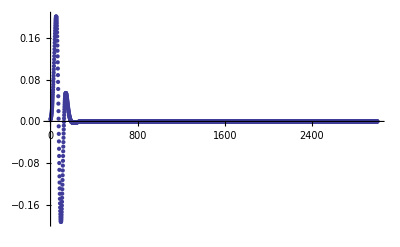

```mathematica
ListPlot[(b4list),PlotRange->All]
```

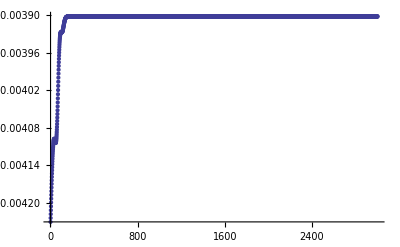

```mathematica
ListPlot[lamblist, PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.1083

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.08897×10^-76

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

### QNM1 = {3.09541 ± 0.00018, -2.75859 ± 0.00018}

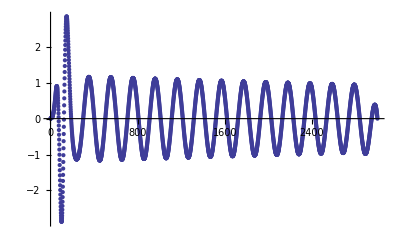

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

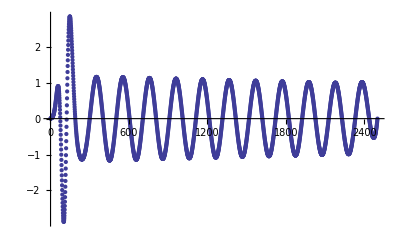

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

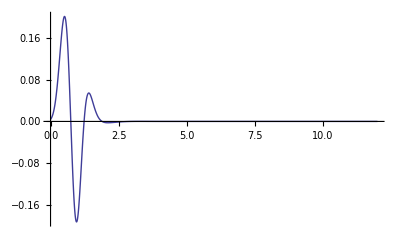

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

{1.10344,1.01866,1.01286,1.01508,1.01491,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.0149,1.01489,1.01513,1.0112,1.08945}

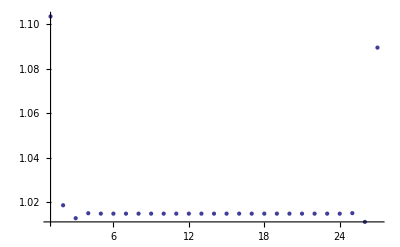

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}];
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.02984

```mathematica
μ1 = 2π/λ1
```

3.09541

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.000502033,0.0000212941,0.0000693476,0.0000551184,0.0000560555,0.0000561564,0.0000561479,0.0000561275,0.0000561508,0.0000561266,0.0000561518,0.0000561256,0.000056153,0.0000561245,0.000056154,0.0000561235,0.0000561542,0.0000561146,0.0000563083,0.0000535602,0.000098326,-0.000637553}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.000181738

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.459365

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.42193

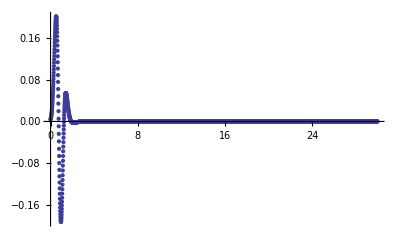

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999401 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423
ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609
ν→0.999998 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819
ν→1. | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864
ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→1. | ν→-2.75877 | ν→-2.75877
ν→1. | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872
ν→1. | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853
ν→1. | ν→-2.75826 | ν→-2.75826 | ν→-2.75826 | ν→-2.75826 | ν→-2.75826 | ν→-2.75826 | ν→-2.75826
ν→1. | ν→-2.75797 | ν→-2.75797 | ν→-2.75797 | ν→-2.75797 | ν→-2.75797 | ν→1. | ν→-2.75797
ν→1. | ν→-2.7577 | ν→-2.7577 | ν→-2.7577 | ν→-2.7577 | ν→-2.7577 | ν→-2.7577 | ν→-2.75764
ν→1. | ν→1. | ν→-2.75747 | ν→-2.75747 | ν→-2.75747 | ν→-2.75747 | ν→-2.7574 | ν→-39.6959)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999401 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423 | ν→-2.7423
ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609 | ν→-2.7609
ν→0.999998 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819 | ν→-2.75819
ν→1. | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864 | ν→-2.75864
ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→-2.75877 | ν→1. | ν→-2.75877 | ν→-2.75877
ν→1. | ν→1. | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872 | ν→-2.75872
ν→1. | ν→1. | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853 | ν→-2.75853
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.75826 | ν→-2.75826 | ν→-2.75826 | ν→-2.75826
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.75797 | ν→-2.75797 | ν→1. | ν→-2.75797
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.7577 | ν→-2.75764
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.52487)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 4;
if = 8;
ji = 2;
jf = 5;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

20

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.75859

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.000180973

QNM1 = {3.09541 ± 0.00018, -2.75859 ± 0.00018}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.32624+0.00019529 x,-2.96429+0.000194468 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.13222+0.000183899 x,-2.79139+0.000183125 x}

## Gaussian B (amp 0.05), f3 = 0.322370 (30%), fxy =0 QNM1 = {3.06466 ± 0.00026, -2.77567 ±0.00033} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.3223709
```

0.322371

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.322370979547fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.322370979547fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-0.982207, -0.980899, -0.976983, -0.970484, -0.961442, -0.949915, -0.935976, -0.919713, -0.901228, -0.880636, -0.858068, -0.833662, -0.807572, -0.779957, -0.750986, « 22 », -0.103144, -0.0881876, -0.0747023, -0.0626437, -0.0519561, -0.0425742, -0.0344238, -0.0274236, -0.0214868, -0.0165221, -0.0124354, -0.00913132, -0.00651472, « 11 »} does not exist.

Part::partw: Part 63 of {-0.982207, -0.980899, -0.976983, -0.970484, -0.961442, -0.949915, -0.935976, -0.919713, -0.901228, -0.880636, -0.858068, -0.833662, -0.807572, -0.779957, -0.750986, « 22 », -0.103144, -0.0881876, -0.0747023, -0.0626437, -0.0519561, -0.0425742, -0.0344238, -0.0274236, -0.0214868, -0.0165221, -0.0124354, -0.00913132, -0.00651472, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-8.86458×10^-8, -8.86205×10^-8, -8.85438×10^-8, -8.84134×10^-8, -8.82255×10^-8, -8.79751×10^-8, -8.76564×10^-8, -8.72631×10^-8, -8.67889×10^-8, -8.62288×10^-8, -8.55798×10^-8, -8.48426×10^-8, -8.4024×10^-8, « 25 », -1.07133×10^-6, -1.21877×10^-6, -1.35972×10^-6, -1.48417×10^-6, -1.58107×10^-6, -1.6396×10^-6, -1.65071×10^-6, -1.60885×10^-6, -1.51343×10^-6, -1.36961×10^-6, -1.18807×10^-6, -9.83731×10^-7, « 11 »} does not exist.

Part::partw: Part 63 of {-8.86458×10^-8, -8.86205×10^-8, -8.85438×10^-8, -8.84134×10^-8, -8.82255×10^-8, -8.79751×10^-8, -8.76564×10^-8, -8.72631×10^-8, -8.67889×10^-8, -8.62288×10^-8, -8.55798×10^-8, -8.48426×10^-8, -8.4024×10^-8, « 25 », -1.07133×10^-6, -1.21877×10^-6, -1.35972×10^-6, -1.48417×10^-6, -1.58107×10^-6, -1.6396×10^-6, -1.65071×10^-6, -1.60885×10^-6, -1.51343×10^-6, -1.36961×10^-6, -1.18807×10^-6, -9.83731×10^-7, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

9.29989×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

7.32126×10^-37

```mathematica
Max[Abs[lambshiftlist]]
```

0.00927103

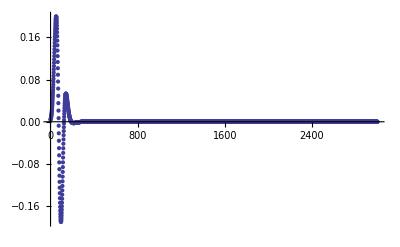

```mathematica
ListPlot[(b4list),PlotRange->All]
```

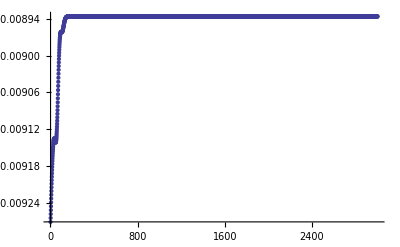

```mathematica
ListPlot[lamblist, PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.309699

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.164105

```mathematica
chem/T
```

-0.529886

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.84225×10^-76

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.05812

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.197097

### QNM1 = {3.06466 ± 0.00026, -2.77567 ±0.00033}

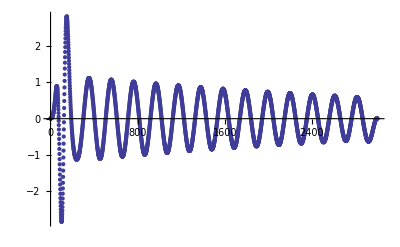

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

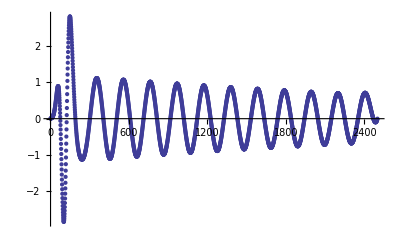

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

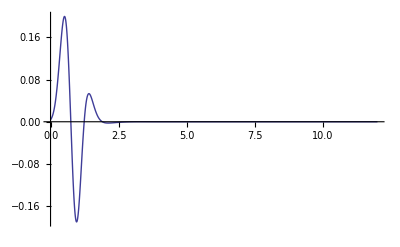

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

{1.10874,1.0294,1.02319,1.02523,1.02509,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02508,1.02506,1.02548,1.01837,1.25443}

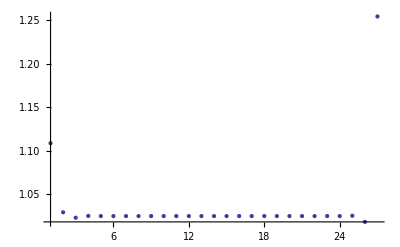

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}];
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.05021

```mathematica
μ1 = 2π/λ1
```

3.06466

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.000376644,0.0000385534,0.0000829761,0.0000717968,0.000072389,0.0000724971,0.000072468,0.0000724769,0.00007247,0.0000724763,0.0000724708,0.0000724755,0.0000724717,0.0000724745,0.0000724726,0.0000724736,0.0000724743,0.0000724593,0.0000727069,0.0000684711,0.000141329,-0.00111325}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.000260958

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.448291

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.37386

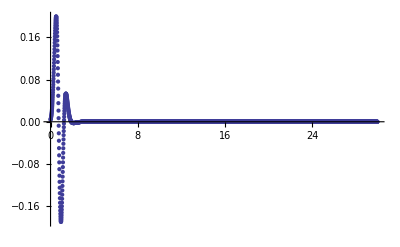

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999853 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574
ν→0.99998 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686
ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581
ν→1. | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617
ν→1. | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592
ν→1. | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563
ν→1. | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536
ν→1. | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516
ν→1. | ν→-2.77502 | ν→-2.77502 | ν→-2.77502 | ν→-2.77502 | ν→-2.77502 | ν→-2.77502 | ν→-2.77502
ν→1. | ν→-2.77494 | ν→-2.77494 | ν→-2.77494 | ν→-2.77494 | ν→-2.77494 | ν→-2.77494 | ν→-2.77487
ν→1. | ν→1. | ν→-2.77492 | ν→-2.77492 | ν→-2.77492 | ν→-2.77491 | ν→-2.77483 | ν→-39.8246)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999853 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574 | ν→-2.76574
ν→0.99998 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686 | ν→-2.77686
ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581 | ν→-2.77581
ν→1. | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617 | ν→-2.77617
ν→1. | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592 | ν→-2.77592
ν→1. | ν→1. | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563 | ν→-2.77563
ν→1. | ν→1. | ν→1. | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536 | ν→-2.77536
ν→1. | ν→1. | ν→1. | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516 | ν→-2.77516
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.77502 | ν→-2.77502 | ν→-2.77502
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.77494 | ν→1. | ν→-2.77487
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.77483 | ν→-2.63067)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 3;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

36

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.77567

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.000337389

QNM1 = {3.06466 ± 0.00026, -2.77567 ±0.00033}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.29319+0.000280418 x,-2.98266+0.000362548 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.14987+0.000268214 x,-2.85285+0.00034677 x}

## Gaussian B (amp 0.05), f3 = 0.429827 (40%), fxy =0 QNM1 = {3.02048 ± 0.00007, -2.80460 ± 0.00007} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.429827
```

0.429827

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.429827972729fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.429827972729fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-0.967656, -0.9664, -0.962638, -0.956394, -0.947703, -0.936617, -0.9232, -0.907531, -0.889702, -0.869818, -0.847996, -0.824366, -0.799067, -0.772248, -0.744067, « 22 », -0.103342, -0.0883616, -0.0748513, -0.0627681, -0.0520575, -0.0426546, -0.0344859, -0.0274703, -0.0215208, -0.016546, -0.0124517, -0.00914194, -0.00652133, « 11 »} does not exist.

Part::partw: Part 63 of {-0.967656, -0.9664, -0.962638, -0.956394, -0.947703, -0.936617, -0.9232, -0.907531, -0.889702, -0.869818, -0.847996, -0.824366, -0.799067, -0.772248, -0.744067, « 22 », -0.103342, -0.0883616, -0.0748513, -0.0627681, -0.0520575, -0.0426546, -0.0344859, -0.0274703, -0.0215208, -0.016546, -0.0124517, -0.00914194, -0.00652133, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-7.9531×10^-8, -7.95122×10^-8, -7.94555×10^-8, -7.93598×10^-8, -7.92235×10^-8, -7.9045×10^-8, -7.88226×10^-8, -7.85553×10^-8, -7.82436×10^-8, -7.78905×10^-8, -7.75029×10^-8, -7.7093×10^-8, -7.66813×10^-8, « 25 », -1.19332×10^-6, -1.34475×10^-6, -1.48646×10^-6, -1.60794×10^-6, -1.69792×10^-6, -1.74573×10^-6, -1.74295×10^-6, -1.68504×10^-6, -1.57273×10^-6, -1.41259×10^-6, -1.21656×10^-6, -1.00046×10^-6, « 11 »} does not exist.

Part::partw: Part 63 of {-7.9531×10^-8, -7.95122×10^-8, -7.94555×10^-8, -7.93598×10^-8, -7.92235×10^-8, -7.9045×10^-8, -7.88226×10^-8, -7.85553×10^-8, -7.82436×10^-8, -7.78905×10^-8, -7.75029×10^-8, -7.7093×10^-8, -7.66813×10^-8, « 25 », -1.19332×10^-6, -1.34475×10^-6, -1.48646×10^-6, -1.60794×10^-6, -1.69792×10^-6, -1.74573×10^-6, -1.74295×10^-6, -1.68504×10^-6, -1.57273×10^-6, -1.41259×10^-6, -1.21656×10^-6, -1.00046×10^-6, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

6.77852×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

-9.6456×10^-38

```mathematica
Max[Abs[lambshiftlist]]
```

0.0166497

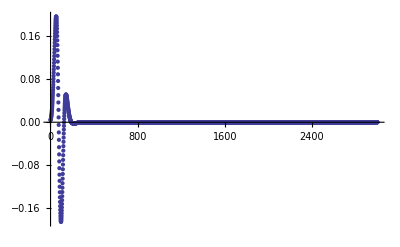

```mathematica
ListPlot[(b4list),PlotRange->All]
```

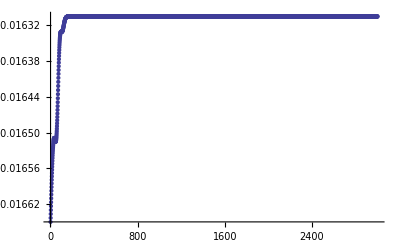

```mathematica
ListPlot[lamblist, PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222097

```mathematica
chem/T
```

-0.734257

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.49166×10^-76

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

### QNM1 = {3.02048 ± 0.00007, -2.80460 ± 0.00007}

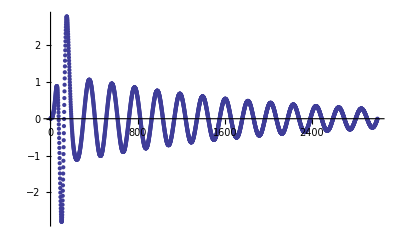

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{1.91233,3.02831,4.0734,5.11183,6.15203,7.19213,8.23222,9.27231,10.3124,11.3525,12.3926,13.4327,14.4728,15.5128,16.5529,17.593,18.6331,19.6732,20.7133,21.7534,22.7935,23.8336,24.8737,25.9137,26.9539,27.9936,29.0398}

{1.11598,1.04508,1.03844,1.0402,1.0401,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04009,1.04011,1.03977,1.04619}

-Graphics-

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.08019

```mathematica
μ1 = 2π/λ1
```

3.02048

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.000295719,-0.0000113702,0.0000254874,0.0000180039,0.0000183034,0.0000183688,0.0000183581,0.0000183585,0.0000183585,0.0000183584,0.0000183586,0.0000183585,0.0000183586,0.0000183585,0.0000183586,0.0000183585,0.0000183581,0.0000183666,0.0000182093,0.0000211193,-0.0000326807}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.0000673002

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.431498

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.30333

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999811 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044
ν→0.999955 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047
ν→0.999999 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453
ν→1. | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473
ν→1. | ν→1. | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463
ν→1. | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458
ν→1. | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456
ν→1. | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456
ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458
ν→1. | ν→-2.80462 | ν→-2.80462 | ν→-2.80462 | ν→-2.80462 | ν→-2.80462 | ν→-2.80462 | ν→-2.80462
ν→1. | ν→-2.80467 | ν→-2.80467 | ν→-2.80467 | ν→-2.80467 | ν→-2.80467 | ν→-2.80469 | ν→-2.62463)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999811 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044 | ν→-2.81044
ν→0.999955 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047 | ν→-2.8047
ν→0.999999 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453 | ν→-2.80453
ν→1. | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473 | ν→-2.80473
ν→1. | ν→1. | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463 | ν→-2.80463
ν→1. | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458
ν→1. | ν→1. | ν→1. | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.80456 | ν→-2.80456 | ν→-2.80456 | ν→-2.80456
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.80458 | ν→-2.80458 | ν→-2.80458 | ν→-2.80458
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.80462 | ν→-2.80462
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.80469 | ν→-2.62463)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 2;
if = 7;
ji = 4;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

30

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.80462

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.0000722221

QNM1 = {3.02048 ± 0.000067, -2.80460 ± 0.000066}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.24572+0.0000723188 x,-3.01376+0.0000776077 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.17857+0.0000708226 x,-2.95141+0.0000760021 x}

## Gaussian B (amp 0.05), f3 = 0.537284 (50%), fxy =0 QNM1 = {2.96273 ± 0.00014, -2.85229 ± 0.000060} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.537284
```

0.537284

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.537284965912fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.537284965912fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

9.00363×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

-9.50389×10^-38

```mathematica
Max[Abs[lambshiftlist]]
```

0.0267656

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.292397

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.283412

```mathematica
chem/T
```

-0.969272

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.41509×10^-78

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.89923

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0977266

### QNM1 = {2.96273 ± 0.00014,-2.85229 ± 0.000060}

```mathematica
ListPlot[ⅇ^(2.85tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

-Graphics-

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.85tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{1.92974,3.05431,4.12014,5.1792,6.23962,7.29999,8.36034,9.4207,10.4811,11.5414,12.6018,13.6621,14.7225,15.7828,16.8432,17.9036,18.9639,20.0243,21.0846,22.145,23.2054,24.2657,25.3261,26.3864,27.447,28.5025,29.7221}

{1.12458,1.06583,1.05906,1.06042,1.06037,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06036,1.06035,1.0606,1.05553,1.2196}

-Graphics-

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.12074

```mathematica
μ1 = 2π/λ1
```

2.96273

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-0.000143635,0.0000192598,0.0000434848,0.0000395845,0.0000396963,0.0000397259,0.0000397221,0.0000397222,0.0000397223,0.0000397221,0.0000397223,0.0000397223,0.0000397224,0.0000397224,0.0000397224,0.0000397227,0.0000397188,0.0000397988,0.0000381543,0.0000720004,-0.000624862}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.000145348

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.407551

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.20746

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->20,AccuracyGoal->20][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999962 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839
ν→0.999998 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284
ν→0.999999 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235
ν→0.999999 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232
ν→1. | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→1. | ν→-2.85222 | ν→-2.85222
ν→1. | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221
ν→1. | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226
ν→1. | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236
ν→1. | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249
ν→1. | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85275
ν→1. | ν→1. | ν→-2.8528 | ν→-2.8528 | ν→-2.8528 | ν→-2.85281 | ν→-2.85293 | ν→-40.5425)

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999962 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839
ν→0.999998 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284
ν→0.999999 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235
ν→0.999999 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232
ν→1. | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→1. | ν→-2.85222 | ν→-2.85222
ν→1. | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221
ν→1. | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226
ν→1. | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236
ν→1. | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249 | ν→-2.85249
ν→1. | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85264 | ν→-2.85275
ν→1. | ν→1. | ν→-2.8528 | ν→-2.8528 | ν→-2.8528 | ν→-2.85281 | ν→-2.85293 | ν→-40.5425)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999962 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839 | ν→-2.86839
ν→0.999998 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284 | ν→-2.85284
ν→0.999999 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235 | ν→-2.85235
ν→0.999999 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232 | ν→-2.85232
ν→1. | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→-2.85222 | ν→1. | ν→-2.85222 | ν→-2.85222
ν→1. | ν→1. | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221 | ν→-2.85221
ν→1. | ν→1. | ν→1. | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226 | ν→-2.85226
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.85236 | ν→-2.85236 | ν→-2.85236 | ν→-2.85236
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.85249 | ν→1. | ν→-2.85249 | ν→-2.85249
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.85264 | ν→-2.85275
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.69955)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 2;
jf = 4;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

18

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.85229

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.0000605237

QNM1 = {2.96273 ± 0.00014,-2.85229 ± 0.000060}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.18366+0.000156186 x,-3.06498+0.000065037 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.22529+0.000158229 x,-3.10506+0.0000658875 x}

## Gaussian B (amp 0.05), f3 = 0.644741 (60%), fxy =0 QNM1 = {2.89707 ± 0.000016, -2.93305 ± 0.000018} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.644741
```

0.644741

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.644741959094fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.644741959094fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

8.14082×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

5.96511×10^-39

```mathematica
Max[Abs[lambshiftlist]]
```

0.040287

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349726

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.4913×10^-80

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245165

### QNM1 = {2.89707 ± 0.000016, -2.93305 ± 0.000018}

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

-Graphics-

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}
```

{2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{1.9535,3.08616,4.17565,5.25917,6.34361,7.42801,8.51241,9.59681,10.6812,11.7656,12.85,13.9344,15.0188,16.1032,17.1876,18.272,19.3564,20.4408,21.5252,22.6096,23.694,24.7784,25.8628,26.9473,28.031,29.132}

{1.13265,1.08949,1.08352,1.08444,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.0844,1.08443,1.08374,1.10099}

-Graphics-

```mathematica
startroot = 5;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.16881

```mathematica
μ1 = 2π/λ1
```

2.89707

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-4.18179×10^-6,5.5383×10^-6,3.991×10^-6,4.05259×10^-6,4.05966×10^-6,4.05657×10^-6,4.0595×10^-6,4.05664×10^-6,4.05893×10^-6,4.05716×10^-6,4.0586×10^-6,4.05808×10^-6,4.05751×10^-6,4.05876×10^-6,4.05637×10^-6,4.06475×10^-6,3.93046×10^-6,7.10054×10^-6,-0.0000691319}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.0000164209

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.379394

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.09913

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->20,AccuracyGoal->20][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999997 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373
ν→0.999998 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338
ν→1. | ν→0.999995 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302
ν→1. | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304
ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306
ν→1. | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308
ν→1. | ν→-2.93309 | ν→-2.93309 | ν→-2.93309 | ν→-2.93309 | ν→1. | ν→-2.93309 | ν→-2.93309
ν→1. | ν→1. | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93313
ν→1. | ν→1. | ν→-2.93317 | ν→-2.93317 | ν→-2.93317 | ν→-2.93317 | ν→-2.93318 | ν→-41.0234)

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999997 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373
ν→0.999998 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338
ν→1. | ν→0.999995 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302
ν→1. | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304
ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306
ν→1. | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308 | ν→-2.93308
ν→1. | ν→-2.93309 | ν→-2.93309 | ν→-2.93309 | ν→-2.93309 | ν→1. | ν→-2.93309 | ν→-2.93309
ν→1. | ν→1. | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93312 | ν→-2.93313
ν→1. | ν→1. | ν→1. | ν→-2.93317 | ν→-2.93317 | ν→-2.93317 | ν→-2.93318 | ν→-41.0234)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999997 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373 | ν→-2.94373
ν→0.999998 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338 | ν→-2.93338
ν→1. | ν→0.999995 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302 | ν→-2.93302
ν→1. | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304 | ν→-2.93304
ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→1. | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305 | ν→-2.93305
ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.93306 | ν→-2.93306 | ν→-2.93306 | ν→-2.93306
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.93308 | ν→-2.93308 | ν→-2.93308
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.93309 | ν→-2.93309
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.93312 | ν→-2.93313
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.74559)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 3;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

36

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.93305

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.0000182204

QNM1 = {2.89707 ± 0.000016, -2.93305 ± 0.000018}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.11311+0.0000176454 x,-3.15177+0.0000195791 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.31032+0.0000187632 x,-3.35142+0.0000208193 x}

## Gaussian B (amp 0.05), f3 = 0.752198 (70%), fxy =0 QNM1 = {2.85715 ± 0.000056, -3.06543 ± 0.000053} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.752198
```

0.752198

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.752198952276fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.752198952276fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

8.57708×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

2.58866×10^-40

```mathematica
Max[Abs[lambshiftlist]]
```

0.058399

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.259388

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.423825

```mathematica
chem/T
```

-1.63394

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.80414×10^-84

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.62618

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0688009

### QNM1 = {2.89707 ± 0.000016, -2.93305 ± 0.000018}

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

-Graphics-

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}
```

{2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{1.98627,3.12077,4.22408,5.32299,6.42258,7.52213,8.62168,9.72123,10.8208,11.9203,13.0199,14.1194,15.219,16.3185,17.4181,18.5176,19.6172,20.7167,21.8163,22.9158,24.0154,25.1149,26.2145,27.3141,28.4108,29.6281}

{1.1345,1.10331,1.09892,1.09959,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09955,1.09965,1.09675,1.21723}

-Graphics-

```mathematica
startroot = 5;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.19911

```mathematica
μ1 = 2π/λ1
```

2.85715

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.0000115812,0.0000135852,0.0000127973,0.0000128602,0.0000128587,0.000012859,0.0000128614,0.0000128607,0.0000128609,0.0000128607,0.0000128611,0.0000128601,0.000012861,0.0000128604,0.0000128592,0.0000128696,0.000012562,0.0000215223,-0.00023922}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.0000564195

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.375025

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.0715

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->20,AccuracyGoal->20][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999989 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185
ν→1. | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576
ν→0.999998 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538
ν→1. | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537
ν→1. | ν→1. | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539
ν→1. | ν→1. | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542
ν→1. | ν→1. | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546
ν→1. | ν→1. | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553
ν→1. | ν→1. | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564
ν→1. | ν→-3.06572 | ν→1. | ν→-3.06572 | ν→-3.06572 | ν→-3.06572 | ν→-3.06572 | ν→-3.06573
ν→1. | ν→1. | ν→-3.06512 | ν→-3.06512 | ν→-3.06512 | ν→-3.06512 | ν→-3.06511 | ν→-5.63745)

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999989 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185
ν→1. | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576
ν→0.999998 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538
ν→1. | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537
ν→1. | ν→1. | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539
ν→1. | ν→1. | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542
ν→1. | ν→1. | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546
ν→1. | ν→1. | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553 | ν→-3.06553
ν→1. | ν→1. | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564 | ν→-3.06564
ν→1. | ν→1. | ν→1. | ν→-3.06572 | ν→-3.06572 | ν→-3.06572 | ν→-3.06572 | ν→-3.06573
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.06512 | ν→-3.06511 | ν→-2.86915)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999989 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185 | ν→-3.07185
ν→1. | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576 | ν→-3.06576
ν→0.999998 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538 | ν→-3.06538
ν→1. | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537 | ν→-3.06537
ν→1. | ν→1. | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539 | ν→-3.06539
ν→1. | ν→1. | ν→1. | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542 | ν→-3.06542
ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.06546 | ν→-3.06546 | ν→-3.06546 | ν→-3.06546
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.06553 | ν→-3.06553 | ν→-3.06553
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.06564
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1.
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-2.86915)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 3;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

36

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-3.06543

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.000053805

QNM1 = {2.85715 ± 0.000056, -3.06543 ± 0.000053}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.11863+0.00265291 x,-3.41376+0.00294724 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.99199+0.00339584 x,-4.36977+0.00377259 x}

## Gaussian B (amp 0.05), f3 = 0.859655 (80%), fxy =0 QNM1 = {2.90222 ± 0.00246881, -3.17755 ± 0.002103} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655
```

0.859655

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.859655945459fxy0.0TS0.01NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.859655945459fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

7.37177×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

6.03061×10^-42

```mathematica
Max[Abs[lambshiftlist]]
```

0.0834909

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511177

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.2559×10^-86

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

### QNM1 = {2.90222 ± 0.00246881, -3.17755 ± 0.002103}

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;3000]])((b4list)[[1;;3000]]- b4list[[3000]]),PlotRange->All]
```

-Graphics-

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.95tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}
```

{2,3,3.5,5,6,7.5,8.5,9.5,10.5,11.5,13,14,15,16,17,18,19.5,20.5,21.5,22.5,23.5,24.5,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{2.03342,3.14755,4.2303,5.31525,6.39521,7.48,8.56058,9.64481,10.7259,11.8097,12.8911,13.9746,15.0563,16.1396,17.2215,18.3045,19.3866,20.4695,21.5517,22.6346,23.7168,24.7996,25.8819,26.9647,28.0466,29.1437}

{1.11413,1.08275,1.08495,1.07996,1.08479,1.08058,1.08423,1.08106,1.08381,1.08143,1.08349,1.0817,1.08325,1.08191,1.08307,1.08207,1.08294,1.08218,1.08284,1.08227,1.08276,1.08233,1.08272,1.08194,1.0971}

-Graphics-

```mathematica
startroot = 6;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.16496

```mathematica
μ1 = 2π/λ1
```

2.90222

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{0.00511297,-0.00468139,0.00380372,-0.0035539,0.00282149,-0.00270621,0.00208394,-0.00206904,0.00153005,-0.0015901,0.00111402,-0.00123019,0.000801543,-0.000959697,0.000566802,-0.000756494,0.000391671,-0.000641388}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

0.00246881

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.441969

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.28269

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->20,AccuracyGoal->20][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

(ν→0.999964 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703
ν→1. | ν→0.999993 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129
ν→1. | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634
ν→1. | ν→0.999999 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252
ν→1. | ν→1. | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721
ν→1. | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763
ν→1. | ν→1. | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399
ν→1. | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482
ν→1. | ν→1. | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816
ν→1. | ν→1. | ν→-3.17085 | ν→-3.17085 | ν→-3.17085 | ν→-3.17085 | ν→-3.17085 | ν→-3.17002
ν→1. | ν→1. | ν→1. | ν→-3.15574 | ν→-3.15574 | ν→-3.15574 | ν→-3.15461 | ν→-5.69971)

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

(ν→0.999964 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703
ν→1. | ν→0.999993 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129
ν→1. | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634
ν→1. | ν→0.999999 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252
ν→1. | ν→1. | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721
ν→1. | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763
ν→1. | ν→1. | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399
ν→1. | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482 | ν→-3.17482
ν→1. | ν→1. | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816 | ν→-3.16816
ν→1. | ν→1. | ν→1. | ν→-3.17085 | ν→-3.17085 | ν→-3.17085 | ν→-3.17085 | ν→-3.17002
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.15574 | ν→-3.15461 | ν→-5.69971)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999964 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703 | ν→-3.1703
ν→1. | ν→0.999993 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129 | ν→-3.20129
ν→1. | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634 | ν→-3.17634
ν→1. | ν→0.999999 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252 | ν→-3.18252
ν→1. | ν→1. | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721 | ν→-3.17721
ν→1. | ν→1. | ν→1. | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763 | ν→-3.1763
ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.17399 | ν→-3.17399 | ν→-3.17399 | ν→-3.17399
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.17482 | ν→-3.17482 | ν→-3.17482
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.16816
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-3.17002
ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→1. | ν→-5.69971)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 3;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

36

```mathematica
Table[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]
```

{{-3.17634,-3.17634,-3.17634,-3.17634,-3.17634,-3.17634},{-3.18252,-3.18252,-3.18252,-3.18252,-3.18252,-3.18252},{-3.17721,-3.17721,-3.17721,-3.17721,-3.17721,-3.17721},{-3.1763,-3.1763,-3.1763,-3.1763,-3.1763,-3.1763},{-3.17399,-3.17399,-3.17399,-3.17399,-3.17399,-3.17399},{-3.17482,-3.17482,-3.17482,-3.17482,-3.17482,-3.17482}}

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-3.17687

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

0.00274271

QNM1 = {2.90222 ± 0.00246881, -3.17755 ± 0.002103}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}(4/3)^(1/4)//N//Simplify
```

{3.11863+0.00265291 x,-3.41376+0.00294724 x}

```mathematica
{μ1+ x σμ1,ν1+ x σν1}1/(π T)//N//Simplify
```

{3.99199+0.00339584 x,-4.36977+0.00377259 x}

## Gaussian B (amp 0.05), f3 = 0.9671129 (90%), fxy =0 QNM1 = {CANNOT FIND, NOT STABLE ENOUGH} *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.9671129
```

0.967113

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.967112938641fxy0.0TS0.01NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.967112938641fxy0.0TS0.01NS3000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

9.81404×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

3.01804×10^-28

```mathematica
Max[Abs[lambshiftlist]]
```

0.121883

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.185003

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.626233

```mathematica
chem/T
```

-3.38499

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.61846×10^-57

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.13165

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.355638

### QNM1 = {3.11346 ± 0.000145, 2.74964 ± 0.0002}

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

That tail oscillation being lower is not acctually there.  It’s weird.  Watch, I’ll lower the window to 2500, where at 2500 you see it’s fine.

```mathematica
ListPlot[ⅇ^(2.75tlist[[1;;2500]])((b4list)[[1;;2500]]- b4list[[2500]]),PlotRange->All]
```

-Graphics-

see? looks like 2500’s messed up...

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,29.99}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
guesslist = {2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}
```

{2,3,3.5,4.5,6,7,8,9,10,11,12,13,14.5,15.5,16.5,17.5,18.5,19.5,20.5,22,23,24,25,26,27,28,29}

```mathematica
Table[ToExpression[
"n"<>ToString[i]<>" = guesslist[[i]]"],{i,1,Length[guesslist]}];
xlist = Table[ToExpression[
"x"<>ToString[i]<>" = FindRoot[y[x],{x,n"<>ToString[i]<>"}][[1,2]]"],{i,1,Length[guesslist]}]
templist = Table[xlist[[i+1]]-xlist[[i]],{i,1,Length[guesslist]-1}]
ListPlot[templist,PlotRange->All]
```

{2.10949,3.15241,4.56968,4.56968,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99,29.99}

{1.04292,1.41727,-2.66454×10^-15,25.4203,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-3.55271×10^-15,-7.10543×10^-15,-2.84217×10^-14,3.90799×10^-14,0.,0.,0.,0.,0.}

-Graphics-

```mathematica
startroot = 4;
endroot = Length[templist]-2;
```

```mathematica
λ1 =2* Sum[templist[[i]],{i,startroot,endroot}]/(endroot - startroot + 1)
```

2.42098

```mathematica
μ1 = 2π/λ1
```

2.5953

```mathematica
Table[2 π/(2 * templist[[i]]),{i,startroot,endroot}]-μ1
```

{-2.47172,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-8.8428×10^14,-4.4214×10^14,-1.10535×10^14,8.03891×10^13,ComplexInfinity,ComplexInfinity,ComplexInfinity}

Standard deviation

```mathematica
σμ1 =√(1/(endroot - startroot + 1) Sum[(2 π/(2 * templist[[i]])-μ1)^2,{i,startroot,endroot}])
```

Indeterminate

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

22.1218

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-57.4128

```mathematica
ListPlot[b4plotlist, PlotRange->All]
```

-Graphics-

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->20,AccuracyGoal->20][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999998 | ν→0.999925 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921
ν→0.999999 | ν→0.99998 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837
ν→0.999997 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323
ν→1. | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198
ν→1. | ν→1. | ν→-0.625155 | ν→-0.625132 | ν→-0.625055 | ν→-0.624854 | ν→-0.624402 | ν→-0.623134
ν→1. | ν→1. | ν→0.75257 | ν→0.769185 | ν→0.786915 | ν→0.804831 | ν→0.832204 | ν→0.87509
ν→1. | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041
ν→1. | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53542
ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35788 | ν→-3.35731
ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26195 | ν→-3.25848 | ν→-3.25968
ν→-0.342192 | ν→-0.334037 | ν→-0.314003 | ν→-0.261182 | ν→-0.145331 | ν→0.15382 | ν→2.13808 | ν→-3.72886)

```mathematica
tempmtx = Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000,PrecisionGoal->12,AccuracyGoal->12][[2]],{i,4,14},{j,1,8}];
%//MatrixForm
```

(ν→0.999998 | ν→0.999925 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921
ν→0.999999 | ν→0.99998 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837
ν→0.999997 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323
ν→1. | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198
ν→1. | ν→1. | ν→-0.625155 | ν→-0.625132 | ν→-0.625055 | ν→-0.624854 | ν→-0.624402 | ν→-0.623134
ν→1. | ν→1. | ν→0.75257 | ν→0.769185 | ν→0.786915 | ν→0.804831 | ν→0.832204 | ν→0.87509
ν→1. | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041
ν→1. | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53542
ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35788 | ν→-3.35731
ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26191 | ν→-3.26195 | ν→-3.25848 | ν→-3.25968
ν→-0.342192 | ν→-0.334037 | ν→-0.314003 | ν→-0.261182 | ν→-0.145331 | ν→0.15382 | ν→2.13808 | ν→-3.72886)

```mathematica
Table[FindFit[b4plotlist[[100*i;;2200- 100*j]],A ⅇ^(ν x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A,ν},x,MaxIterations->100000][[2]],{i,4,14},{j,1,8}]//MatrixForm
```

(ν→0.999998 | ν→0.999925 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921 | ν→-4.73921
ν→0.999999 | ν→0.99998 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837 | ν→-1.82837
ν→0.999997 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323 | ν→-3.47323
ν→1. | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198 | ν→-5.17198
ν→1. | ν→1. | ν→-0.625155 | ν→-0.625132 | ν→-0.625055 | ν→-0.624854 | ν→-0.624402 | ν→-0.623134
ν→1. | ν→1. | ν→0.75257 | ν→0.769185 | ν→0.786915 | ν→0.804831 | ν→0.832204 | ν→0.87509
ν→1. | ν→1. | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041 | ν→-2.86041
ν→1. | ν→1. | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53541 | ν→-2.53542
ν→1. | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35787 | ν→-3.35788 | ν→-3.35731
ν→1. | ν→1. | ν→1. | ν→-3.26191 | ν→-3.26191 | ν→-3.26195 | ν→-3.25848 | ν→-3.25968
ν→1. | ν→1. | ν→1. | ν→1. | ν→-0.145331 | ν→0.15382 | ν→2.13808 | ν→-3.72886)

Larry, I believe these Nu’s -> 1 are because the window is so larger, there is a huge range in numbers taking place, and the precision can’t handle it or something.  Thats why when I increase precision goal I get more numbers. But too much and I get complaints.  I think it is clear here that nu is like 2.7496 +- 0.0002

```mathematica
ii = 3;
if = 8;
ji = 2;
jf = 8;
```

```mathematica
tot = (if-ii+1)(jf-ji+1)
```

42

```mathematica
ν1 = Sum[tempmtx[[i,j]][[2]],{i,ii,if},{j,ji,jf}]/(tot)
```

-2.26701

```mathematica
σν1 = √(1/(tot) Sum[(tempmtx[[i,j]][[2]]-ν1)^2,{i,ii,if},{j,ji,jf}])
```

1.99006

QNM1 = {3.02048 ± 0.000067, -2.80460 ± 0.000066}

## Gaussian B (amp 0.75), f3 = 0.859656 (80%), fxy =0 (zoomed) (Binitnolamb)

```mathematica
a2 = -1;
fxy = 0;
g=1;
f3=0.859656;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.75a2-1.0f30.859656fxy0.0TS0.01NS250FF.h5"
```

/phys/users/fuini/Research/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.75a2-1.0f30.859656fxy0.0TS0.01NS250FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dvB_sub_list,/lamb_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
templistr = b4list;
```

```mathematica
ListPlot[ⅇ^tlist(b4list),PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{radialtlist[[i]],finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[radialtlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve,AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B/u^3  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All, ColorFunction->Function[{x,y,z},Hue[z+.14]]]
```

-Graphics3D-

```mathematica
TeXForm[v]
```

v

## Gaussian B (amp 0.05), f3 = 0.107457 (50%), fxy =0 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.107457
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.05TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.05TS0.01NS1200FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.000122204

```mathematica
sigmadot2[1]
```

-3.1421×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

0.000208125

```mathematica
Max[Abs[lambshiftlist]]
```

0.000523564

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318177

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.91768×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249584

### QNM1 {3.05786, -2.65623}

```mathematica
ListPlot[ⅇ^(2.66tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
n9 = 10;
n10 = 11;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]],x9=FindRoot[y[x],{x,n9}][[1,2]],x10=FindRoot[y[x],{x,n10}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7,x9-x8,x10-x9}
ListPlot[%,PlotRange->All]
```

{1.88438,2.98412,3.99466,4.99969,6.00709,7.0143,8.02148,9.02863,10.0361,11.0455}

{1.09973,1.01054,1.00503,1.00741,1.0072,1.00719,1.00714,1.0075,1.00936}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,4,8}]/5
```

2.01457

```mathematica
μ1 = 2π/λ1
```

3.11886

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47412

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.59757

```mathematica
lowcut = 500;
highcut = 1000;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→5.12846,ν1→-2.74547}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->5.128462692029635,ν1->-2.74546536671102})},{x,5,10}]
```

-Graphics-

## GuassianU B, Magnetic Black Brane QNMs

```mathematica
fxy =0.37 (9.2%), T =0.311295 : QNM1 {3.05786, -2.65623}
```

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =0.05, T =0.318177 : QNM1 {3.11886, -2.74547} *

```mathematica
a2 = -1;
fxy = 0.05;
g=1;
f3=0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.05TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.05TS0.01NS1200FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.000122204

```mathematica
sigmadot2[1]
```

-3.1421×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

0.000208125

```mathematica
Max[Abs[lambshiftlist]]
```

0.000523564

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318177

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.91768×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249584

### QNM1 {3.05786, -2.65623}

```mathematica
ListPlot[ⅇ^(2.66tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
n9 = 10;
n10 = 11;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]],x9=FindRoot[y[x],{x,n9}][[1,2]],x10=FindRoot[y[x],{x,n10}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7,x9-x8,x10-x9}
ListPlot[%,PlotRange->All]
```

{1.88438,2.98412,3.99466,4.99969,6.00709,7.0143,8.02148,9.02863,10.0361,11.0455}

{1.09973,1.01054,1.00503,1.00741,1.0072,1.00719,1.00714,1.0075,1.00936}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,4,8}]/5
```

2.01457

```mathematica
μ1 = 2π/λ1
```

3.11886

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47412

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.59757

```mathematica
lowcut = 500;
highcut = 1000;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→5.12846,ν1→-2.74547}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->5.128462692029635,ν1->-2.74546536671102})},{x,5,10}]
```

-Graphics-

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =0.37 (9.2%), T =0.311295 : QNM1 {3.10567, -2.75267} *

```mathematica
a2 = -1;
fxy = 0.37;
g=1;
f3=0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.37TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.37TS0.01NS1200FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.00669132

```mathematica
sigmadot2[1]
```

8.41127×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots

```mathematica
b4list[[-1]]
```

0.0107876

```mathematica
Max[Abs[lambshiftlist]]
```

0.000419128

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist, PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.311295

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000558992

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14308

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.228425

### QNM1 {3.05786, -2.65623}

```mathematica
ListPlot[ⅇ^(2.66tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7}
ListPlot[%,PlotRange->All]
```

{1.85075,2.97714,4.00072,5.00872,6.02133,7.03366,8.04568,9.05855}

{1.12639,1.02358,1.00801,1.0126,1.01234,1.01202,1.01288}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,7}]/5
```

2.02313

```mathematica
μ1 = 2π/λ1
```

3.10567

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

1.47049

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-4.56685

```mathematica
lowcut = 500;
highcut = 1000;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→2.46245,ν1→-2.75267}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->2.462450433612126,ν1->-2.752674234587022})},{x,5,10}]
```

-Graphics-

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =0.75 (18.7%), T = 0.292564 : QNM1 {3.05786, -2.63251}

```mathematica
a2 = -1;
fxy = 0.75;
g=1;
f3=0;
```

```mathematica
(*inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.75TS0.01NS1200FF.h5"*)
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.75TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy0.75TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.0366705

```mathematica
Max[Abs[lambshiftlist]]
```

1.14169×10^-12

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {3.05786, -2.63251}

```mathematica
ListPlot[ⅇ^(2.66tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
n8 = 9;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7}
ListPlot[%,PlotRange->All]
```

{2.1663,3.04579,4.06521,5.09423,6.12055,7.14694,8.17369,9.20213}

{0.879498,1.01941,1.02902,1.02632,1.02639,1.02675,1.02844}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,7}]/5
```

2.05477

```mathematica
μ1 = 2π/λ1
```

3.05786

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.468306

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.43201

```mathematica
lowcut = 400;
highcut = 1000;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→-2.53318,ν1→-2.63251}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->-2.5331839440323733,ν1->-2.632506476378887})},{x,4,8}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.292564

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000558992

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.17494

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.178872

```mathematica
InputForm[PYBsubCoefs20]
```

{0.07216389250870313, 0.07206593393329079, 0.07177281209350782, 0.07128678186928411, 0.0706115787976029, 0.06975238518616968, 
0.0687157826941026, 0.06750969141553832, 0.06614329553204017, 0.06462695564668786, 0.06297210797888414, 0.06119115069095822, 
0.05929731773817175, 0.05730454078981726, 0.055227299963277104, 0.05308046435145445, 0.05087912360784303, 0.0486384121859549, 
0.04637332820751171, 0.04409854935342966, 0.04182824862145482, 0.03957591325990751, 0.03735417064364646, 0.035174625276343505, 
0.03304771144194072, 0.030982566242276566, 0.028986927794084714, 0.027067063163889626, 0.025227730142015244, 0.023472176157625597, 
0.021802176492907045, 0.02021811247335591, 0.01871908853387734, 0.01730308507209423, 0.015967141926899513, 0.014707565328429047, 
0.013520149445066267, 0.012400402402325842, 0.011343766043277234, 0.010345818871507977, 0.00940245261926051, 0.008510014680377187, 
0.007665411103701218, 0.006866167736766384, 0.006110450154035179, 0.005397045888466774, 0.004725314912413664, 0.004095116048429192, 
0.0035067178834039658, 0.002960702773554817, 0.0024578717309555608, 0.0019991565401723385, 0.0015855435937584363, 0.0012180119210035514, 
0.000897485969339754, 0.0006248021022889984, 0.0004006866536592906, 0.00022574280024433843, 0.00010044346846330024, 
0.000025127879944938795, 0.}

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =1.12 (28.0%), T = 0.271204 : QNM1 {3.02457, -2.58579}

```mathematica
a2 = -1;
fxy =1.12;
g=1;
f3=0;
```

```mathematica
(*inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.12TS0.01NS1200FF.h5"*)
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.12TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.12TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.0561327

```mathematica
b4a21list[[3]] = b4list ;
```

Set::noval: Symbol b4a21list in part assignment does not have an immediate value.

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {3.02457, -2.58579}

```mathematica
ListPlot[ⅇ^(2.58tlist[[1;;1000]])((b4list)[[1;;1000]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{2.059,3.04722,4.08102,5.12025,6.15891,7.19755,8.23578}

{0.988227,1.03379,1.03923,1.03866,1.03864,1.03823}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,6}]/4
```

2.07738

```mathematica
μ1 = 2π/λ1
```

3.02457

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.445594

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.34773

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→-4.40288,ν1→-2.58579}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->-4.402880216651657,ν1->-2.5857855955047357})},{x,3,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.271204

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.30672

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.146796

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =1.49 (37.3%), T = 0.256523 : QNM1 {3.04608, -2.55895}

```mathematica
a2 = -1;
fxy = 1.49;
g=1;
f3=0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.49TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.49TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.0436701

```mathematica
ListPlot[b4list,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(2.58 tlist[[;;800]])(b4list[[;;800]]-b4list[[-1]]),PlotRange->All]
```

-Graphics-

### QNM1 {3.04608, -2.55895}

```mathematica
ListPlot[ⅇ^(2.59tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{1.98741,3.00611,4.0339,5.06539,6.09681,7.12819,8.15933}

{1.0187,1.02779,1.03149,1.03141,1.03138,1.03114}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,6}]/4
```

2.06271

```mathematica
μ1 = 2π/λ1
```

3.04608

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.42415

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.29199

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→-4.58985,ν1→-2.55895}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->-4.589854930096324,ν1->-2.558946337379635})},{x,3,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256523

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.55781

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.16266

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =1.87 (46.8%), T = 0.254831 : QNM1 {3.16323, -2.66609}

```mathematica
a2 = -1;
fxy = 1.87;
g=1;
f3=0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.87TS0.01NS1200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy1.87TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0281332

```mathematica
b4a21list[[5]] = b4list ;
```

Set::noval: Symbol b4a21list in part assignment does not have an immediate value.

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {3.16323, -2.66609}

```mathematica
ListPlot[ⅇ^(2.68tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=6;
n6 = 7;
n7 = 8;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{1.88902,2.89072,3.88145,4.87457,5.86777,6.86093,7.85409}

{1.00169,0.990734,0.993125,0.993198,0.993161,0.993161}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,6}]/4
```

1.98632

```mathematica
μ1 = 2π/λ1
```

3.16323

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

-1.58094

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

5.00086

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→-6.07791,ν1→-2.66609}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->-6.077912024883727,ν1->-2.6660875940115307})},{x,3,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.254831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

Part::partd: Part specification sigmasubscaleathorlist ⟦ -1 ⟧ is longer than depth of object.

π (1.1095+sigmasubscaleathorlist⟦-1⟧)^3

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

3/4-0.800574 (1.1095+sigmasubscaleathorlist⟦-1⟧)^3

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =2.24 (56.0%), T = 0.266139 : QNM1 {3.36525, -2.85139}

```mathematica
a2 = -1;
fxy = 2.24;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.24TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.24TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.174453

```mathematica
b4a21list[[6]] = b4list ;
```

Set::noval: Symbol b4a21list in part assignment does not have an immediate value.

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {3.36525, -2.85139}

```mathematica
ListPlot[ⅇ^(2.85tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=5;
n6 = 6;
n7 = 7;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

-Graphics-

{0.942733,0.931956,0.933463,0.93352,0.933524,0.933654}

{1.82974,2.77247,3.70443,4.63789,5.57141,6.50494,7.43859}

{1.82974,2.77247,3.70443,4.63789,5.57141,6.50494,7.43859}

{0.942733,0.931956,0.933463,0.93352,0.933524,0.933654}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,6}]/4
```

1.86708

1.86708

```mathematica
μ1 = 2π/λ1
```

3.36525

3.36525

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.437039

0.437039

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-1.47074

-1.47074

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→-23.7643,ν1→-2.85139}

{A1→-23.7643,ν1→-2.85139}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->-23.76429788175336,ν1->-2.851388229434849})},{x,3,6}]
```

-Graphics-

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.266139

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.25058

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.647385

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =2.61 (65.2%), T = 0.286435 : QNM1 {3.62631, -3.07557}

```mathematica
a2 = -1;
fxy = 2.61;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.61TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.61TS0.01NS1200FF.h5

```mathematica
2.61/.286^2
```

31.9087

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.409037

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {3.36525, -2.85139}

```mathematica
ListPlot[ⅇ^(3.08tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=5;
n6 = 6;
n7 = 7;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{1.98454,2.85287,3.71919,4.58553,5.45185,6.3182,7.18428}

{0.86833,0.866315,0.866339,0.866326,0.866351,0.866074}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,2,5}]/4
```

1.73267

1.73267

```mathematica
μ1 = 2π/λ1
```

3.62631

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

-1.04588

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

3.7927

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→5.42204,ν1→-3.07557}

{A1→5.42204,ν1→-3.07557}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->5.4220396160435484,ν1->-3.0755680133420413})},{x,3,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.286435

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.58005

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.13475

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =2.99 (74.8%), T = 0.312555 : QNM1 {3.92613, -3.40405}

```mathematica
a2 = -1;
fxy = 2.99;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.99TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy2.99TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.751349

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(3.33tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

### QNM1 {3.92613, -3.40405}

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=5;
n6 = 6;
n7 = 7;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{2.02495,2.83379,3.63402,4.43411,5.2342,6.03432,6.83466}

{0.808841,0.80023,0.800094,0.800087,0.80012,0.800341}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,2,6}]/5
```

1.60035

```mathematica
μ1 = 2π/λ1
```

3.92613

```mathematica
Δx1 = x7-FindRoot[Cos[μ1 x],{x,n7}][[1,2]]
```

0.033179

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-0.130265

```mathematica
lowcut = 200;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→28.5781,ν1→-3.40405}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->28.57807251622735,ν1->-3.4040520029908423})},{x,2,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.312555

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.2841

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.83923

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =3.36 (84.0%), T = 0.340426: QNM1 {4.23063, -3.58722}

```mathematica
a2 = -1;
fxy = 3.36;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy3.36TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy3.36TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-1.19057

```mathematica
400*0.01
```

4.

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(3.58tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

### QNM1 {4.23063, -3.58722}

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=2.5;
n3=3.5;
n4=4.3;
n5=5.;
n6 = 5.5;
n7 = 6;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{1.91794,2.67251,3.41574,4.15819,4.90075,5.64327,6.38542}

{0.754575,0.743222,0.742452,0.742558,0.742522,0.742156}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,2,6}]/5
```

1.48516

```mathematica
μ1 = 2π/λ1
```

4.23063

```mathematica
Δx1 = x6-FindRoot[Cos[μ1 x],{x,n6}][[1,2]]
```

0.073902

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

-0.312652

```mathematica
lowcut = 300;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→61.8956,ν1→-3.58722}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->61.895561111713164,ν1->-3.5872218647247185})},{x,2,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.340426

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

10.2462

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.73806

## Gaussian B (amp 0.05), f3 = 0 (0%), fxy =3.73 (93.3%), T = 0.369173: QNM1 {4.53566, -3.86854}

```mathematica
a2 = -1;
fxy = 3.73;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy3.73TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.05a2-1.0f30.0fxy3.73TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-1.74025

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(3.85tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

### QNM1 {4.53566, -3.86854}

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4list,PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.5;
n5=5;
n6 = 6;
n7 = 7;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{2.4226,3.11595,3.80824,4.50082,5.19323,5.88581,9.59214}

{0.693352,0.692289,0.692586,0.692406,0.69258,3.70633}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,1,5}]/5
```

1.38528

```mathematica
μ1 = 2π/λ1
```

4.53566

```mathematica
Δx1 = x6-FindRoot[Cos[μ1 x],{x,n6}][[1,2]]
```

-0.00165033

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

0.00748533

```mathematica
lowcut = 300;
highcut = 500;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→90.8048,ν1→-3.86854}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->90.80484931071632,ν1->-3.868543500397046})},{x,2,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.369173

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

12.4842

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.85881

## Gaussian B (amp 0.0005), f3 = 0 (0%), fxy =3.92 (98.0%), T = 0.383994: QNM1 {4.69241, -3.98328}

```mathematica
a2 = -1;
fxy = 3.92;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0005a2-1.0f30.0fxy3.92TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0005a2-1.0f30.0fxy3.92TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-2.06714

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(3.99tlist[[1;;800]])((b4list)[[1;;800]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

### QNM1 {4.69241, -3.98328}

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,Length[b4plotlist]}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,12.}},<>]

```mathematica
Plot[y[x],{x,0,12},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4list,PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.;
n5=5;
n6 = 5.5;
n7 = 6;
n8 = 7;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]],x8=FindRoot[y[x],{x,n8}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6,x8-x7}
ListPlot[%,PlotRange->All]
```

{2.29841,2.96878,3.63807,4.30771,4.97716,5.64674,6.31609,6.99363}

{0.670374,0.669289,0.669643,0.669449,0.669581,0.669346,0.677539}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,3,6}]/4
```

1.33901

```mathematica
μ1 = 2π/λ1
```

4.69241

```mathematica
Δx1 = x6-FindRoot[Cos[μ1 x],{x,n6}][[1,2]]
```

-0.0440483

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

0.206693

```mathematica
lowcut = 400;
highcut = 1000;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

$Aborted

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->110.5154850573833,ν1->-3.9832836355309342})},{x,4,6}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.383994

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.7345

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.52398

## Gaussian B (amp 0.000005), f3 = 0 (0%), fxy =3.995 (99.9%), T = 0.389833: QNM1 {4.75377, -4.03666}

```mathematica
a2 = -1;
fxy = 3.995;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-07a2-1.0f30.0fxy3.995TS0.01NS1200FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-07a2-1.0f30.0fxy3.995TS0.01NS1200FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubat0_list,/dvB_sub_list,/lamb_list,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubat0_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-2.20472

```mathematica
lamblist[[1]]
```

0.571171

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### QNM1 {4.75377, -4.03666}

```mathematica
b4plotlistshift = Table[{b4plotlist[[i,1]],b4plotlist[[i,2]]-b4list[[-1]]},{i,1,700}];
```

```mathematica
y=Interpolation[b4plotlistshift]
```

InterpolatingFunction[{{0.,6.99}},<>]

```mathematica
Plot[y[x],{x,0,7},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4list,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[ⅇ^(4.05tlist[[1;;700]])((b4list)[[1;;700]]- b4list[[1000]]),PlotRange->All]
```

-Graphics-

```mathematica
n1=2;
n2=3;
n3=3.5;
n4=4.;
n5=5;
n6 = 5.5;
n7 = 6;
{x1=FindRoot[y[x],{x,n1}][[1,2]],x2=FindRoot[y[x],{x,n2}][[1,2]],x3=FindRoot[y[x],{x,n3}][[1,2]],x4=FindRoot[y[x],{x,n4}][[1,2]],x5=FindRoot[y[x],{x,n5}][[1,2]],x6=FindRoot[y[x],{x,n6}][[1,2]],x7=FindRoot[y[x],{x,n7}][[1,2]]}
templist = {x2-x1, x3-x2, x4-x3,x5-x4,x6-x5,x7-x6}
ListPlot[%,PlotRange->All]
```

{2.23396,2.8956,3.55645,4.21738,4.8782,5.53905,6.19893}

{0.66164,0.660851,0.660926,0.660826,0.660849,0.659872}

-Graphics-

```mathematica
λ1 =2* Sum[templist[[i]],{i,2,5}]/4
```

1.32173

```mathematica
μ1 = 2π/λ1
```

4.75377

```mathematica
Δx1 = x6-FindRoot[Cos[μ1 x],{x,n6}][[1,2]]
```

-0.0782829

```mathematica
ϕ1 = -2π(Δx1)/λ1
```

0.372139

```mathematica
lowcut = 400;
highcut = 700;
```

```mathematica
rule1=FindFit[Partition[Riffle[tlist[[lowcut;;highcut]],y[tlist[[lowcut;;highcut]]]],2],-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1],{A1,ν1},x]
```

{A1→78.6103,ν1→-4.03666}

```mathematica
Plot[{y[x],(-A1 ⅇ^(ν1 x) Cos[-ϕ1] 2 Cos[μ1 x+ϕ1]/.{A1->78.61028218433228,ν1->-4.0366642993610125})},{x,4,7}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.389833

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.2464

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.8037

```mathematica
PYBsubCoefs20
```

{0.246712,0.237183,0.208844,0.16243,0.0991419,0.0206127,-0.0711428,-0.173785,-0.284717,-0.401163,-0.520244,-0.639061,-0.754779,-0.864703,-0.966354,-1.05753,-1.13637,-1.2014,-1.25154,-1.28616,-1.30508,-1.30851,-1.2971,-1.27186,-1.23411,-1.18545,-1.12769,-1.06275,-0.992636,-0.919329,-0.844742,-0.770645,-0.698617,-0.629994,-0.565843,-0.506938,-0.453757,-0.406485,-0.365041,-0.329106,-0.298165,-0.271562,-0.248547,-0.228335,-0.210156,-0.193306,-0.177178,-0.161301,-0.145351,-0.129161,-0.112721,-0.0961587,-0.0797269,-0.0637722,-0.0487058,-0.0349705,-0.0230074,-0.0132246,-0.00596956,-0.00150639,0.}

## Double Valued MAG in EQ

```mathematica
Maga20pt245333list = {{0,0.224021},{0.5,0.171872},{0.7,0.118907},{0.78,0.0897625},{0.815,0.0743078},{0.835,0.064177},{0.848,0.0568059},{0.857,0.0511816},{0.8635,0.0467574},{0.8678,0.0436189},{0.871,0.0411388},{0.874,0.0386781},{0.876,0.0369577},{0.8795,0.033746},{0.881,0.0322799},{0.8823,0.0309559},{0.8835,0.0296871},{0.8845,0.0285836},{0.8854,0.027558},{1.834,0.0517443},{1.85,0.0579637},{1.875,0.06665684233950132},{1.92,0.0802563},{2.0,0.100666},{2.14,0.130238}};
```

```mathematica
LargerB2epslist2= Table[{Maga20pt245333list[[i,1]]^2/(-3/4(-0.245333) + 1/4 Maga20pt245333list[[i,1]]^2 Log[Maga20pt245333list[[i,1]]]),Maga20pt245333list[[i,1]]/(Maga20pt245333list[[i,2]])^2},{i,2,Length[Maga20pt245333list]}];
```

```mathematica
Maga21over8list = {{0,.189268},{0.1, .185399},{0.25,0.163793},{0.4,0.114078},{0.45, 0.0835162},{0.46, 0.0753257},{0.47,0.0658023},{0.476,0.0592142},{0.482,0.0516159},{0.486,0.0457783},{2.14, 0.0760720352443748},{2.18,0.0908563},{2.3,0.125126},{2.5,0.16753},{3.0,0.244696},{3.5,0.304929}};
```

```mathematica
LargerB2epslist3= Table[{Maga21over8list[[i,1]]^2/(-3/4(-1./8) + 1/4 Maga21over8list[[i,1]]^2 Log[Maga21over8list[[i,1]]]),Maga21over8list[[i,1]]/(Maga21over8list[[i,2]])^2},{i,2,Length[Maga21over8list]}]
```

{{0.113645,2.90928},{0.866982,9.31857},{2.80218,30.7366},{3.79743,64.5165},{4.01734,81.0721},{4.24368,108.546},{4.38243,135.755},{4.52328,180.917},{4.61831,231.909},{4.7467,369.797},{4.66074,264.087},{4.42577,146.904},{4.09714,89.0748},{3.50791,50.1034},{3.11678,37.6418}}

The following lists are {B^2/eps(mu = B^1/2) , B/T^2}

```mathematica
B0pt5list = {{0.35376776047909064,5.343983354536858},{0.17162334318529837,3.6060699831547773},{0.08455434596901062,2.499880811302506},{0.04196969978200882,1.7531757612915067},{0.020908817123113176,1.235615470848297}};
B1list = {{1.3333333333333333,12.939564576230193},{0.6666666666666666,7.815746533417264},{0.3333333333333333,5.168044060664963},{0.16666666666666666,3.5508726739573304},{0.08333333333333333,2.4813911776416293}};
B2list = {{2.771720067005216,30.07465302891981},{1.8238630017428819,17.387796050034417},{1.083087081136455,10.960803181944907},{0.5976261827347658,7.292575508793908},{0.31513067193659877,5.008144732538567}};
B3list = {{2.793402164538319,30.564973427110928},{2.265930825217038,22.39076780314943},{1.644773618214407,15.666451395079395},{1.0623382881984516,10.80062916667039},{0.6218958049516766,7.477309936719056}};
B4list = {{2.5416281178906086,26.271794665758268},{2.2710570636566763,22.456045192661225},{1.8724011413404262,17.88259336241556},{1.385860033502608,13.390089051412865},{0.9119315008714409,9.65651872638523}};
LargerB2epslist = {{3.285306902867961,42.34544843264726},{4.013542146711349,80.531965912134},{4.210168783945093,103.19699215484029}};
LargeTpoint ={{0.0036258577562526474,0.514454920768403}};
```

```mathematica
ListPlot[{B0pt5list,B1list,B2list,B3list,B4list,LargerB2epslist,LargerB2epslist2[[;;-6]],LargerB2epslist3[[;;]],LargeTpoint},PlotRange->{{0,5},{0,350}},PlotMarkers->Automatic,AxesStyle->Large,AxesLabel->{"B^2/ε(μ = B^(1/2))","B/T^2"},PlotLegends-> Placed[PointLegend[{Style["BL^2=0.5",22],Style["BL^2=1",22],Style["BL^2=2",22],Style["BL^2=3",22],Style["BL^2=4",22]}],{0.2,0.7}]]
```

-Graphics-

```mathematica
ListPlot[{B0pt5list,B1list,B2list,B3list,B4list,LargerB2epslist,LargerB2epslist2[[;;-6]],LargerB2epslist3[[;;]],LargeTpoint},PlotRange->{{0,.15},{0,10}},PlotMarkers->Automatic,AxesStyle->Large,AxesLabel->{"B^2/ε(μ = B^(1/2))","B/T^2"},PlotLegends-> Placed[PointLegend[{Style["BL^2=0.5",22],Style["BL^2=1",22],Style["BL^2=2",22],Style["BL^2=3",22],Style["BL^2=4",22]}],{0.2,0.7}]]
```

-Graphics-

```mathematica
templist2=Union[Union[Union[Union[Union[Union[Union[Union[B0pt5list,B1list],B2list],B3list],B4list],LargerB2epslist],LargerB2epslist2],LargerB2epslist3],LargeTpoint]
templist=Union[Union[Union[Union[B0pt5list,B1list],B2list],B3list],B4list];
```

{{0.00362586,0.514455},{0.0209088,1.23562},{0.0419697,1.75318},{0.0833333,2.48139},{0.0845543,2.49988},{0.113645,2.90928},{0.166667,3.55087},{0.171623,3.60607},{0.315131,5.00814},{0.333333,5.16804},{0.353768,5.34398},{0.597626,7.29258},{0.621896,7.47731},{0.666667,7.81575},{0.866982,9.31857},{0.911932,9.65652},{1.06234,10.8006},{1.08309,10.9608},{1.33333,12.9396},{1.38586,13.3901},{1.64477,15.6665},{1.77711,16.9262},{1.82386,17.3878},{1.8724,17.8826},{2.26593,22.3908},{2.27106,22.456},{2.54163,26.2718},{2.77172,30.0747},{2.7934,30.565},{2.80218,30.7366},{3.11678,37.6418},{3.28531,42.3454},{3.49234,49.5089},{3.50791,50.1034},{3.79743,64.5165},{4.01354,80.532},{4.01734,81.0721},{4.09714,89.0748},{4.16117,96.8065},{4.21017,103.197},{4.24368,108.546},{4.34066,126.165},{4.38243,135.755},{4.42577,146.904},{4.42728,147.601},{4.52328,180.917},{4.56024,197.362},{4.56992,202.734},{4.61831,231.909},{4.65864,262.79},{4.66074,264.087},{4.69496,298.087},{4.71813,327.155},{4.7467,369.797},{4.7601,394.968},{4.7735,421.999},{4.78739,456.111},{4.80745,514.653},{4.81793,550.63},{4.82607,584.226},{4.83839,641.349},{4.84663,684.974},{4.85973,772.309},{4.8688,845.496},{4.87662,920.724},{4.88381,1002.47},{4.88978,1082.59},{4.89513,1165.85}}

```mathematica
BpiTlist = Table[{templist2[[i,1]],1/π^2 templist2[[i,2]]},{i,1,Length[templist2]}];
```

```mathematica
ListPlot[{BpiTlist},PlotRange->All,AxesStyle->Large,AxesLabel->{"B^2/ε(μ = B^(1/2))","B/(πT)^2"},PlotLegends-> Placed[PointLegend[{Style["BL^2=0.5",22],Style["BL^2=1",22],Style["BL^2=2",22],Style["BL^2=3",22],Style["BL^2=4",22]}],{0.2,0.7}]]
```

-Graphics-

```mathematica
BpiTinverselist = Table[{(BpiTlist[[i,1]])^-1,(BpiTlist[[i,2]])^-1},{i,1,Length[BpiTlist]}];
```

```mathematica
BpiT2inverselist = Table[{BpiTinverselist[[i,1]],BpiTinverselist[[i,2]]^2},{i,1,Length[BpiTinverselist]}];
```

```mathematica
rule = FindFit[BpiT2inverselist[[;;30]],A + B x,{A,B},x]
Show[Plot[A + B x/.rule,{x,0,50},PlotStyle->{Thick,Red}],ListPlot[BpiT2inverselist[[;;]],PlotMarkers->Automatic],AxesStyle->Directive[22,Black],AxesLabel ->{Style["ε_ℬ/ℬ^2",28],Style["(πT)^4/ℬ^2",28]},PlotRange->{{0,3},{0,2}}]
```

{A→-0.356963,B→1.33607}

-Graphics-

```mathematica
BpiT2inverselistSIWTCH = Table[{BpiT2inverselist[[i,2]],BpiT2inverselist[[i,1]]},{i,1,Length[BpiT2inverselist]}];
```

```mathematica
rule = FindFit[BpiT2inverselistSIWTCH[[;;2]],A + B x,{A,B},x]
rule2 = FindFit[BpiT2inverselistSIWTCH[[;;10]],A + B x^(1/2),{A,B},x]
Show[Plot[A + B x/.rule,{x,0,70},PlotStyle->{Thick,Red}],ListPlot[BpiT2inverselistSIWTCH[[;;]],PlotMarkers->Automatic],AxesStyle->Directive[22,Black], AxesLabel ->{Style["(πT)^4/ℬ^2",28],Style["ε_ℬ/ℬ^2",28]},PlotRange->{{0,70},{0,70}}]
```

{A→0.0204218,B→0.749294}

{A→-44.9564,B→15.8388}

-Graphics-

```mathematica
rule = FindFit[BpiT2inverselistSIWTCH[[;;2]],A + B x,{A,B},x]
rule2 = FindFit[BpiT2inverselistSIWTCH[[55;;]],A + B x^(1/2),{A,B},x]
Show[Plot[A + B x/.rule,{x,0,70},PlotStyle->{Thick,Red}],Plot[A + B x^(1/2)/.rule2,{x,0,0.1},PlotStyle->{Thick,Purple}],ListPlot[BpiT2inverselistSIWTCH[[;;]],PlotMarkers->Automatic],AxesStyle->Directive[22,Black], AxesLabel ->{Style["(πT)^4/ℬ^2",28],Style["ε_ℬ/ℬ^2",28]},PlotRange->{{0,1},{0,1}}]
```

{A→0.0204218,B→0.749294}

{A→0.201305,B→0.349968}

-Graphics-

```mathematica
BpiT2inverselistSIWTCH[[1]]
```

{368.048,275.797}

```mathematica
ListPlot[BpiT2inverselistSIWTCH,PlotRange->All]
```

-Graphics-

```mathematica
BpiT2inverselistSIWTCH
```

{{368.048,275.797},{63.8018,47.8267},{31.6919,23.8267},{15.8201,12.},{15.5869,11.8267},{11.5088,8.79935},{7.72555,6.},{7.49085,5.82671},{3.8837,3.17329},{3.64709,3.},{3.4109,2.82671},{1.83163,1.67329},{1.74224,1.60799},{1.59462,1.5},{1.12176,1.15343},{1.04462,1.09657},{0.835029,0.94132},{0.810802,0.923287},{0.581782,0.75},{0.543291,0.721574},{0.396879,0.607986},{0.340001,0.562712},{0.322189,0.548287},{0.304606,0.534074},{0.194295,0.44132},{0.193167,0.440324},{0.14113,0.393449},{0.107696,0.360787},{0.104268,0.357986},{0.103107,0.356865},{0.0687477,0.320844},{0.0543233,0.304386},{0.0397405,0.286341},{0.0388029,0.28507},{0.0234022,0.263336},{0.0150198,0.249156},{0.0148203,0.248921},{0.0122769,0.244073},{0.0103942,0.240317},{0.00914672,0.23752},{0.00826738,0.235645},{0.0061196,0.23038},{0.00528554,0.228184},{0.00451371,0.225949},{0.00447118,0.225872},{0.00297604,0.221078},{0.00250075,0.219287},{0.00236998,0.218822},{0.0018112,0.216529},{0.00141053,0.214655},{0.00139671,0.214558},{0.00109626,0.212994},{0.000910109,0.211948},{0.000712315,0.210673},{0.000624419,0.21008},{0.000546986,0.20949},{0.00046823,0.208882},{0.000367764,0.20801},{0.000321278,0.207558},{0.000285389,0.207208},{0.000236816,0.206681},{0.000207611,0.206329},{0.000163312,0.205773},{0.000136263,0.205389},{0.000114905,0.20506},{0.0000969298,0.204758},{0.0000831135,0.204508},{0.0000716657,0.204285}}

```mathematica
Y:=Interpolation[BpiT2inverselistSIWTCH[[6;;]]]
```

```mathematica
Table[Y[BpiT2inverselistSIWTCH[[i]]
```

```mathematica
Clear[Y]
```

```mathematica
Y2:=Interpolation[Drop[BpiT2inverselistSIWTCH,{3}]]
```

```mathematica
Y2[31.691921789956204]
```

```mathematica
(23.836392875703307-23.826713204860017)/23.826713204860017
```

0.000406253

```mathematica
BpiT2inverselistSIWTCH[[3]]
```

{31.6919,23.8267}

```mathematica
31.691921789956204
```

```mathematica
Y[BpiT2inverselistSIWTCH[[2;;6,1]]]
```

InterpolatingFunction::dmval: Input value {63.8018} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {31.6919} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.8201} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{41.7866,23.4385,11.9912,11.8189,8.79935}

```mathematica
(23.826713204860017-23.43851027089341)/23.43851027089341
```

0.0165626

```mathematica
(11.826713204860013-11.818865931666387)/11.818865931666387
```

0.000663962

```mathematica
(8.799353726751487-8.799353726751487)/8.799353726751487
```

0.

```mathematica
Plot[Y[x],{x,1,4}]
```

-Graphics-

```mathematica
Fit[BpiT2inverselistSIWTCH]
```

Fit::argr: Fit called with 1 argument; 3 arguments are expected.

Fit[{{368.048,275.797},{63.8018,47.8267},{31.6919,23.8267},{15.8201,12.},{15.5869,11.8267},{11.5088,8.79935},{7.72555,6.},{7.49085,5.82671},{3.8837,3.17329},{3.64709,3.},{3.4109,2.82671},{1.83163,1.67329},{1.74224,1.60799},{1.59462,1.5},{1.12176,1.15343},{1.04462,1.09657},{0.835029,0.94132},{0.810802,0.923287},{0.581782,0.75},{0.543291,0.721574},{0.396879,0.607986},{0.340001,0.562712},{0.322189,0.548287},{0.304606,0.534074},{0.194295,0.44132},{0.193167,0.440324},{0.14113,0.393449},{0.107696,0.360787},{0.104268,0.357986},{0.103107,0.356865},{0.0687477,0.320844},{0.0543233,0.304386},{0.0397405,0.286341},{0.0388029,0.28507},{0.0234022,0.263336},{0.0150198,0.249156},{0.0148203,0.248921},{0.0122769,0.244073},{0.0103942,0.240317},{0.00914672,0.23752},{0.00826738,0.235645},{0.0061196,0.23038},{0.00528554,0.228184},{0.00451371,0.225949},{0.00447118,0.225872},{0.00297604,0.221078},{0.00250075,0.219287},{0.00236998,0.218822},{0.0018112,0.216529},{0.00141053,0.214655},{0.00139671,0.214558},{0.00109626,0.212994},{0.000910109,0.211948},{0.000712315,0.210673},{0.000624419,0.21008},{0.000546986,0.20949},{0.00046823,0.208882},{0.000367764,0.20801},{0.000321278,0.207558},{0.000285389,0.207208},{0.000236816,0.206681},{0.000207611,0.206329},{0.000163312,0.205773},{0.000136263,0.205389},{0.000114905,0.20506},{0.0000969298,0.204758},{0.0000831135,0.204508},{0.0000716657,0.204285}}]

```mathematica
rule = FindFit[BpiT2inverselistSIWTCH[[;;2]],B x,{B},x];
rule2 = FindFit[BpiT2inverselistSIWTCH[[55;;]],A + B x^(1/2),{A,B},x]
labels={"High-T","Low-T"};
styles={Directive[Darker[Blue],AbsoluteThickness[2.5],Dotted],Directive[Red,AbsoluteThickness[2.5],Dashed]};
ticks = {{{0.002,Null,{0.01,0}},{0.003,Null,{0.01,0}},{0.004,Null,{0.01,0}},{0.005,Null,{0.01,0}},{0.006,Null,{0.01,0}},{0.007,Null,{0.01,0}},{0.008,Null,{0.01,0}},{0.009,Null,{0.01,0}},{0.01,0.01,{0.015,0}},{0.02,Null,{0.01,0}},{0.03,Null,{0.01,0}},{0.04,Null,{0.01,0}},{0.05,Null,{0.01,0}},{0.06,Null,{0.01,0}},{0.07,Null,{0.01,0}},{0.08,Null,{0.01,0}},{0.09,Null,{0.01,0}},{0.1,0.1,{0.015,0}},{0.2,Null,{0.01,0}},{0.3,Null,{0.01,0}},{0.4,Null,{0.01,0}},{0.5,Null,{0.01,0}},{0.6,Null,{0.01,0}},{0.7,Null,{0.01,0}},{0.8,Null,{0.01,0}},{0.9,Null,{0.01,0}},{1.0,1,{0.015,0}},{2,Null,{0.01,0}},{3,Null,{0.01,0}},{4,Null,{0.01,0}},{5,Null,{0.01,0}},{6,Null,{0.01,0}},{7,Null,{0.01,0}},{8,Null,{0.01,0}},{9,Null,{0.01,0}},{10,10,{0.015,0}},{20,Null,{0.01,0}},{30,Null,{0.01,0}},{40,Null,{0.01,0}},{50,Null,{0.01,0}},{60,Null,{0.01,0}},{70,Null,{0.01,0}},{80,Null,{0.01,0}},{90,Null,{0.01,0}},{100,100,{0.015,0}}},{{0.1,Null,{0.01,0}},{0.2,Null,{0.01,0}},{0.3,Null,{0.01,0}},{0.4,Null,{0.01,0}},{0.5,Null,{0.01,0}},{0.6,Null,{0.01,0}},{0.7,Null,{0.01,0}},{0.8,Null,{0.01,0}},{0.9,Null,{0.01,0}},{1.0,1,{0.015,0}},{2,Null,{0.01,0}},{3,Null,{0.01,0}},{4,Null,{0.01,0}},{5,Null,{0.01,0}},{6,Null,{0.01,0}},{7,Null,{0.01,0}},{8,Null,{0.01,0}},{9,Null,{0.01,0}},{10,10,{0.015,0}},{20,Null,{0.01,0}},{30,Null,{0.01,0}},{40,Null,{0.01,0}},{50,Null,{0.01,0}},{60,Null,{0.01,0}},{70,Null,{0.01,0}},{80,Null,{0.01,0}},{90,Null,{0.01,0}},{100,100,{0.015,0}}}};
Show[LogLogPlot[ B x/.rule,{x,0.6,1000},PlotStyle->styles[[1]],PlotRange->{{.001,100},{0.1,100}},Ticks->ticks],LogLogPlot[A + B x^(1/2)/.rule2,{x,0.00001,0.3},PlotStyle->styles[[2]]],ListLogLogPlot[BpiT2inverselistSIWTCH[[;;]],PlotStyle->Directive[Darker[Green],AbsoluteThickness[2.5]],Joined->True],simpleLegend[Thread@{labels,styles},{.2,.95}],ImageSize->{{400},{300}},AspectRatio->Full,AxesLabel->{Style[" (πT)^4/ℬ^2",28],Style["ε_ℬ/ℬ^2\n",28,LineSpacing->{0,10}]},AxesStyle->Directive[Black,22]]
```

{A→0.201305,B→0.349968}

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,-Graphics-,-Graphics-,simpleLegend[{{High-T,Directive[RGBColor[0,0,2/3],AbsoluteThickness[2.5],Dashing[{0,Small}]]},{Low-T,Directive[RGBColor[1,0,0],AbsoluteThickness[2.5],Dashing[{Small,Small}]]}},{0.2,0.95}],ImageSize→{{400},{300}},AspectRatio→Full,AxesLabel→{ (πT)^4/ℬ^2,ε_ℬ/ℬ^2
},AxesStyle→Directive[GrayLevel[0],22]]

```mathematica
ListPlot[{BL0pt5list,BL1list,BL2list,BL3list,BL4list},PlotRange->All,PlotMarkers->Automatic,AxesStyle->Large,AxesLabel->{"B^2/ε(μ = L^-1)","B/T^2"},PlotLegends-> Placed[PointLegend[{Style["BL^2=0.5",22],Style["BL^2=1",22],Style["BL^2=2",22],Style["BL^2=3",22],Style["BL^2=4",22]}],{0.5,0.4}]]
```

-Graphics-

```mathematica
PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["20%",22],Style["40%",22], Style["60%",22], Style["80%",22]}],{.76,.68}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full
```

```mathematica
YY[XX_] := εL/XX+ 1/4 Log[XX]
```

```mathematica
Plot[{(YY[x]/.εL->0.75),(YY[x]/.εL->-0.75)},{x,0.2,40},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dashed]},{Style["ε_LL^4 = 0.75",22],Style["ε_LL^4 = -0.75",22]}],{.56,.24}],AxesStyle->Directive[22,Black],PlotRange->All,PlotRange->All,AxesStyle->Directive[22,Black],AxesLabel ->{Style[" |ℬ|L^2",28],Style["ε_ℬ/ℬ^2",28]},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

## fxy = 0.5, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.04083×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13104×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.04281×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.4877×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99933×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.305881

```mathematica
fxy/T^2
```

5.34398

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.353768

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000185392

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14659

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.212483

## fxy = 0.5, a2 = - 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.07153×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.31439×10^-16

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.13083×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.67009×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99445×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.372364

```mathematica
fxy/T^2
```

3.60607

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.171623

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/2

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000054253

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.34388

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.48987

## fxy = 0.5, a2 = - 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.46945×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.66134×10^-16

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.28466×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.77947×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99689×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.447224

```mathematica
fxy/T^2
```

2.49988

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.0845543

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000163116

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.98369

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.01772

## fxy = 0.5, a2 = - 8

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.03577×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.49401×10^-16

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.92619×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.67617×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99933×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.534038

```mathematica
fxy/T^2
```

1.75318

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.0419697

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.91511×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

15.0662

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.04594

## fxy = 0.5, a2 = - 16

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16f30.0fxy0.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.1684×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.52656×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.4122×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.05815×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.636126

```mathematica
fxy/T^2
```

1.23562

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.0209088

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.47546×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

25.2692

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.07442

## fxy = 1.0, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.38538×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.14353×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99889×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277997

```mathematica
fxy/T^2
```

12.9396

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.33333

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00244053

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22464

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.146441

## fxy = 1.0, a2 = - 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.93889×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.80331×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.4861×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.63123×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99989×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.357697

```mathematica
fxy/T^2
```

7.81575

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.666667

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/2

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000738364

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.56221

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.489583

## fxy = 1.0, a2 = - 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.55351×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.10703×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.61506×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99756×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.439883

```mathematica
fxy/T^2
```

5.16804

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.333333

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000232649

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

9.29714

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.08965

## fxy = 1.0, a2 = - 8

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.21965×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.12683×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.61192×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.53068

```mathematica
fxy/T^2
```

3.55087

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.166667

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000729207

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

15.4426

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.19506

## fxy = 1.0, a2 = - 16

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.44009×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.37668×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.14436×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99645×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.634823

```mathematica
fxy/T^2
```

2.48139

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.0833333

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000225213

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

25.6832

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.30427

## fxy = 2.0, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.37668×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.98348×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.996×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.257878

```mathematica
fxy/T^2
```

30.0747

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.77172

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0140897

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42843

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.391996

## fxy = 2.0, a2 = - 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.11022×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.5099×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.08358×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99911×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.339151

```mathematica
fxy/T^2
```

17.3878

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.82386

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00596012

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.92267

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.84783

## fxy = 2.0, a2 = - 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.11022×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.47895×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.427163

```mathematica
fxy/T^2
```

10.9608

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.08309

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00236111

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

10.8094

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.61736

## fxy = 2.0, a2 = - 8

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.37668×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.17124×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.86326×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.52369

```mathematica
fxy/T^2
```

7.29258

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.597626

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000869289

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

17.0786

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.94388

## fxy = 2.0, a2 = - 16

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.17604×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.08365×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99911×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.631941

```mathematica
fxy/T^2
```

5.00814

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.315131

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000299862

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

27.4017

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-5.31626

## fxy = 3.0, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.73035×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.72813×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99878×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.313292

```mathematica
fxy/T^2
```

30.565

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.7934

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0174359

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.05541

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.77369

## fxy = 3.0, a2 = - 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.19744×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.12719×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.32907×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.366038

```mathematica
fxy/T^2
```

22.3908

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.26593

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0111233

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

10.2583

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.25491

## fxy = 3.0, a2 = - 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.19744×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.91402×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.437598

```mathematica
fxy/T^2
```

15.6665

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.64477

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00603075

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9772

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.11639

## fxy = 3.0, a2 = - 8

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.3145×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.27591×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99845×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.527031

```mathematica
fxy/T^2
```

10.8006

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.06234

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00279931

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

20.1672

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.62872

## fxy = 3.0, a2 = - 16

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.75016×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.69642×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.22569×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99911×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.633414

```mathematica
fxy/T^2
```

7.47731

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.621896

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000299862

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

27.4017

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-5.31626

## fxy = 4.0, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.42109×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.57252×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.18412×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99756×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.390198

```mathematica
fxy/T^2
```

26.2718

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.54163

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0163273

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9104

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.67782

## fxy = 4.0, a2 = - 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-2.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.24345×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.92779×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.02425×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422049

```mathematica
fxy/T^2
```

22.456

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.27106

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0129097

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

15.7559

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-5.14977

## fxy = 4.0, a2 = - 4

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-4.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.06581×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.57252×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.22489×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.99361×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99889×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.472949

```mathematica
fxy/T^2
```

17.8826

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.8724

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00885768

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

19.1029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-6.03468

## fxy = 4.0, a2 = - 8

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-8.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.04805×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.76748×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.16462×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.546561

```mathematica
fxy/T^2
```

13.3901

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.38586

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00512502

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

24.972

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.64872

## fxy = 4.0, a2 = - 16

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-16.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.79412×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.45137×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.75082×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99867×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.643605

```mathematica
fxy/T^2
```

9.65652

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

0.911932

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00249444

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

35.0151

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-10.5359

## Larger B^2/eps_B

Want to maximize this.

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

Or rather minimize

```mathematica
(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1
```

(-(3 a2)/4+1/4 fxy^2 Log[fxy])/fxy^2

```mathematica
Clear[fxy,a2]
```

```mathematica
NMinimize[{(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1,fxy>0.1}/.a2->-0.7,{fxy}]
```

{0.304386,{fxy→2.04939}}

```mathematica
NMinimize[{(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1,fxy>0.1}/.a2->-0.45,{fxy}]
```

{0.249156,{fxy→1.64317}}

```mathematica
NMinimize[{(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1,fxy>0.1}/.a2->-0.41,{fxy}]
```

{0.23752,{fxy→1.56844}}

```mathematica
{0.2491564716262854,{fxy->1.6431676752678248}}
```

```mathematica
Plot[{(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1/.a2->-0.3,(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1/.a2->-0.8,(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1/.a2->-2,(fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy]))^-1/.a2->-3},{fxy,0,10}]
```

-Graphics-

```mathematica
1/0.3043855656611653
```

3.28531

```mathematica
1/2.793402164538319
```

0.357986

## fxy = 1.3, a2 = 0.7

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.5uave0.5a2-0.7f30.0fxy1.3TS0.001amp20.0wid20.6uave20.6NS5000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.5uave0.5a2-0.7f30.0fxy1.3TS0.001amp20.0wid20.6uave20.6NS5000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.79412×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.45137×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.75082×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99867×10^-12

### Thermo

```mathematica
lamblist[[-1]]
```

-0.0699806

```mathematica
PYBsubCoefs100
```

{0.261172,0.261143,0.261059,0.260919,0.260722,0.260469,0.260161,0.259797,0.259377,0.258903,0.258373,0.257789,0.257151,0.256459,0.255713,0.254915,0.254064,0.253162,0.252208,0.251203,0.250148,0.249043,0.24789,0.246688,0.245439,0.244144,0.242802,0.241415,0.239984,0.238509,0.236992,0.235434,0.233834,0.232195,0.230517,0.228801,0.227048,0.225259,0.223436,0.221578,0.219689,0.217767,0.215815,0.213834,0.211824,0.209787,0.207725,0.205637,0.203526,0.201392,0.199237,0.197062,0.194868,0.192656,0.190427,0.188183,0.185925,0.183654,0.181371,0.179077,0.176774,0.174463,0.172144,0.16982,0.167491,0.165158,0.162823,0.160486,0.158149,0.155813,0.153478,0.151147,0.14882,0.146498,0.144182,0.141874,0.139573,0.137282,0.135001,0.132731,0.130472,0.128227,0.125995,0.123778,0.121576,0.119391,0.117222,0.115071,0.112939,0.110826,0.108732,0.106659,0.104607,0.102577,0.100569,0.0985835,0.0966214,0.094683,0.0927687,0.090879,0.0890142,0.0871748,0.085361,0.0835731,0.0818114,0.0800761,0.0783675,0.0766857,0.0750308,0.0734031,0.0718025,0.0702291,0.068683,0.0671642,0.0656727,0.0642084,0.0627712,0.0613611,0.059978,0.0586216,0.0572918,0.0559885,0.0547114,0.0534602,0.0522348,0.0510349,0.0498601,0.0487102,0.0475848,0.0464835,0.0454061,0.0443521,0.0433212,0.042313,0.041327,0.0403628,0.03942,0.0384982,0.0375969,0.0367156,0.035854,0.0350115,0.0341877,0.0333821,0.0325943,0.0318237,0.03107,0.0303327,0.0296112,0.0289052,0.0282141,0.0275376,0.0268753,0.0262265,0.0255911,0.0249684,0.0243582,0.02376,0.0231734,0.0225981,0.0220337,0.0214798,0.0209362,0.0204024,0.0198782,0.0193632,0.0188572,0.0183599,0.017871,0.0173903,0.0169176,0.0164526,0.0159951,0.015545,0.015102,0.014666,0.0142369,0.0138144,0.0133985,0.0129891,0.0125861,0.0121893,0.0117987,0.0114142,0.0110358,0.0106633,0.0102969,0.00993633,0.00958171,0.00923299,0.00889015,0.0085532,0.00822214,0.00789699,0.00757775,0.00726447,0.00695715,0.00665583,0.00636055,0.00607134,0.00578825,0.00551131,0.00524058,0.00497609,0.00471791,0.00446607,0.00422063,0.00398164,0.00374915,0.00352321,0.00330387,0.00309118,0.0028852,0.00268597,0.00249353,0.00230795,0.00212926,0.0019575,0.00179273,0.00163498,0.00148429,0.0013407,0.00120425,0.00107498,0.000952912,0.000838083,0.000730522,0.000630257,0.000537314,0.000451718,0.000373491,0.000302652,0.00023922,0.000183212,0.000134643,0.0000935243,0.0000598672,0.0000336804,0.0000149707,3.74291×10^-6,0.}

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.214908

```mathematica
fxy/T^2
```

28.1474

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

2.65786

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00249444

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

35.0151

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-10.5359

## fxy = 2.049, a2 = 0.7

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.7f30.0fxy2.04939TS0.001amp20wid20uave20NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.7f30.0fxy2.04939TS0.001amp20wid20uave20NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.24345×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.67644×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.471×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.01047×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99656×10^-12

### Thermo

```mathematica
lamblist[[-1]]
```

0.0689516

```mathematica
PYBsubCoefs100
```

{0.354116,0.35408,0.353971,0.35379,0.353536,0.35321,0.352812,0.352342,0.3518,0.351187,0.350502,0.349746,0.348919,0.348022,0.347054,0.346017,0.344911,0.343736,0.342492,0.341181,0.339802,0.338357,0.336845,0.335268,0.333626,0.33192,0.330151,0.328318,0.326424,0.324468,0.322451,0.320376,0.318241,0.316048,0.313799,0.311493,0.309133,0.306718,0.30425,0.30173,0.299159,0.296538,0.293868,0.291151,0.288386,0.285577,0.282723,0.279826,0.276887,0.273908,0.270889,0.267833,0.264739,0.261611,0.258448,0.255252,0.252026,0.248769,0.245484,0.242172,0.238835,0.235473,0.232088,0.228683,0.225257,0.221813,0.218353,0.214877,0.211388,0.207886,0.204374,0.200853,0.197324,0.193789,0.190249,0.186707,0.183164,0.179621,0.176079,0.172541,0.169008,0.165481,0.161962,0.158453,0.154954,0.151469,0.147997,0.144541,0.141103,0.137683,0.134283,0.130904,0.127549,0.124218,0.120913,0.117634,0.114385,0.111164,0.107975,0.104819,0.101696,0.0986072,0.095555,0.09254,0.0895635,0.0866264,0.0837298,0.0808748,0.0780622,0.075293,0.0725679,0.0698879,0.0672537,0.0646662,0.0621261,0.059634,0.0571908,0.054797,0.0524532,0.05016,0.0479178,0.0457269,0.0435876,0.0415002,0.0394649,0.0374819,0.0355512,0.0336729,0.0318472,0.030074,0.0283535,0.0266855,0.0250699,0.0235064,0.0219949,0.020535,0.0191262,0.017768,0.0164599,0.0152013,0.0139916,0.0128303,0.0117167,0.0106501,0.00963007,0.00865575,0.00772649,0.00684152,0.00600004,0.00520117,0.00444397,0.00372745,0.00305055,0.00241216,0.00181116,0.0012464,0.000716747,0.000221083,-0.000241656,-0.000672493,-0.00107241,-0.00144238,-0.00178334,-0.00209628,-0.00238221,-0.00264219,-0.00287734,-0.00308879,-0.00327773,-0.00344531,-0.00359268,-0.00372094,-0.00383114,-0.00392427,-0.00400128,-0.00406304,-0.00411039,-0.00414408,-0.00416482,-0.00417324,-0.00416995,-0.0041555,-0.00413045,-0.00409539,-0.00405099,-0.00399803,-0.00393737,-0.00386998,-0.00379689,-0.00371909,-0.00363755,-0.00355304,-0.00346616,-0.00337728,-0.00328655,-0.00319391,-0.00309917,-0.00300209,-0.00290243,-0.00280009,-0.00269508,-0.00258762,-0.00247814,-0.0023672,-0.00225552,-0.00214388,-0.00203307,-0.00192384,-0.00181682,-0.00171255,-0.00161138,-0.00151354,-0.00141913,-0.00132812,-0.0012404,-0.00115581,-0.00107418,-0.000995317,-0.000919075,-0.000845336,-0.000774031,-0.000705141,-0.000638694,-0.000574758,-0.000513439,-0.000454867,-0.000399191,-0.000346568,-0.000297158,-0.000251118,-0.000208595,-0.000169728,-0.000134638,-0.000103436,-0.0000762158,-0.0000530559,-0.000034022,-0.000019166,-8.52724×10^-6,-2.13315×10^-6,0.}

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.219993

```mathematica
fxy/T^2
```

42.3454

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

3.28531

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00249444

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

35.0151

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-10.5359

## fxy = 1.64317, a2 = 0.45

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.45f30.0fxy1.64317TS0.001amp20wid20uave20NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.45f30.0fxy1.64317TS0.001amp20wid20uave20NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.95395×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.54397×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.47851×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99928×10^-12

```mathematica
Plot[sigmadot1[x],{x,0.6,1}]
```

-Graphics-

### Thermo

```mathematica
lamblist[[-1]]
```

-0.145765

```mathematica
PYBsubCoefs100
```

{0.519833,0.519763,0.519552,0.519201,0.518709,0.518078,0.517308,0.516399,0.515352,0.514168,0.512847,0.511392,0.509802,0.508079,0.506225,0.50424,0.502127,0.499887,0.497521,0.495031,0.49242,0.489689,0.48684,0.483876,0.480798,0.477608,0.47431,0.470906,0.467397,0.463787,0.460078,0.456273,0.452375,0.448386,0.444309,0.440147,0.435903,0.43158,0.427181,0.422709,0.418167,0.413558,0.408886,0.404153,0.399363,0.394519,0.389623,0.38468,0.379693,0.374664,0.369597,0.364495,0.359361,0.354199,0.349012,0.343803,0.338575,0.333331,0.328074,0.322808,0.317536,0.312259,0.306983,0.301709,0.29644,0.29118,0.285932,0.280697,0.275479,0.27028,0.265104,0.259952,0.254827,0.249732,0.244669,0.239641,0.23465,0.229698,0.224787,0.219918,0.215095,0.21032,0.205593,0.200917,0.196293,0.191724,0.187211,0.182755,0.178358,0.174022,0.169746,0.165533,0.161383,0.157298,0.153279,0.149325,0.14544,0.141622,0.137873,0.134194,0.130584,0.127045,0.123576,0.120177,0.116849,0.113592,0.110405,0.107289,0.104245,0.10127,0.098367,0.0955337,0.0927703,0.0900761,0.0874505,0.0848928,0.0824025,0.079979,0.0776215,0.0753295,0.0731022,0.0709387,0.0688381,0.0667993,0.0648211,0.0629023,0.0610419,0.0592388,0.0574918,0.0558,0.0541621,0.0525772,0.0510438,0.0495605,0.0481261,0.0467392,0.0453982,0.0441021,0.0428496,0.0416394,0.0404703,0.0393409,0.0382499,0.0371956,0.0361768,0.0351919,0.0342398,0.0333192,0.0324292,0.0315688,0.0307367,0.0299319,0.0291528,0.028398,0.0276661,0.0269557,0.0262659,0.0255958,0.0249446,0.0243118,0.0236967,0.0230985,0.0225162,0.0219487,0.0213949,0.0208537,0.0203243,0.019806,0.0192983,0.018801,0.0183135,0.0178354,0.0173661,0.0169051,0.0164517,0.0160053,0.0155656,0.0151323,0.0147055,0.0142851,0.013871,0.0134631,0.0130611,0.0126645,0.0122728,0.0118856,0.0115026,0.0111237,0.010749,0.0103789,0.0100139,0.00965456,0.00930121,0.00895411,0.00861324,0.00827833,0.0079489,0.00762437,0.00730413,0.00698765,0.00667459,0.00636483,0.00605849,0.00575596,0.00545783,0.00516479,0.00487764,0.00459717,0.00432409,0.00405902,0.00380241,0.00355461,0.00331578,0.00308596,0.0028651,0.00265307,0.00244968,0.00225473,0.00206803,0.0018894,0.00171869,0.00155579,0.00140065,0.00125323,0.00111356,0.000981676,0.000857649,0.000741566,0.00063353,0.000533648,0.000442029,0.000358781,0.000284005,0.000217796,0.00016024,0.000111411,0.0000713726,0.0000401776,0.0000178664,4.46804×10^-6,0.}

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.142842

```mathematica
fxy/T^2
```

80.532

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

4.01354

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00249444

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

35.0151

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-10.5359

## fxy = 1.56844, a2 = 0.41

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.41f30.0fxy1.56844TS0.001amp20wid20uave20NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-0.41f30.0fxy1.56844TS0.001amp20wid20uave20NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

8.95395×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.54397×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.47851×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99928×10^-12

```mathematica
Plot[sigmadot1[x],{x,0.6,1}]
```

-Graphics-

### Thermo

```mathematica
lamblist[[-1]]
```

0.0689516

```mathematica
PYBsubCoefs100
```

{0.519833,0.519763,0.519552,0.519201,0.518709,0.518078,0.517308,0.516399,0.515352,0.514168,0.512847,0.511392,0.509802,0.508079,0.506225,0.50424,0.502127,0.499887,0.497521,0.495031,0.49242,0.489689,0.48684,0.483876,0.480798,0.477608,0.47431,0.470906,0.467397,0.463787,0.460078,0.456273,0.452375,0.448386,0.444309,0.440147,0.435903,0.43158,0.427181,0.422709,0.418167,0.413558,0.408886,0.404153,0.399363,0.394519,0.389623,0.38468,0.379693,0.374664,0.369597,0.364495,0.359361,0.354199,0.349012,0.343803,0.338575,0.333331,0.328074,0.322808,0.317536,0.312259,0.306983,0.301709,0.29644,0.29118,0.285932,0.280697,0.275479,0.27028,0.265104,0.259952,0.254827,0.249732,0.244669,0.239641,0.23465,0.229698,0.224787,0.219918,0.215095,0.21032,0.205593,0.200917,0.196293,0.191724,0.187211,0.182755,0.178358,0.174022,0.169746,0.165533,0.161383,0.157298,0.153279,0.149325,0.14544,0.141622,0.137873,0.134194,0.130584,0.127045,0.123576,0.120177,0.116849,0.113592,0.110405,0.107289,0.104245,0.10127,0.098367,0.0955337,0.0927703,0.0900761,0.0874505,0.0848928,0.0824025,0.079979,0.0776215,0.0753295,0.0731022,0.0709387,0.0688381,0.0667993,0.0648211,0.0629023,0.0610419,0.0592388,0.0574918,0.0558,0.0541621,0.0525772,0.0510438,0.0495605,0.0481261,0.0467392,0.0453982,0.0441021,0.0428496,0.0416394,0.0404703,0.0393409,0.0382499,0.0371956,0.0361768,0.0351919,0.0342398,0.0333192,0.0324292,0.0315688,0.0307367,0.0299319,0.0291528,0.028398,0.0276661,0.0269557,0.0262659,0.0255958,0.0249446,0.0243118,0.0236967,0.0230985,0.0225162,0.0219487,0.0213949,0.0208537,0.0203243,0.019806,0.0192983,0.018801,0.0183135,0.0178354,0.0173661,0.0169051,0.0164517,0.0160053,0.0155656,0.0151323,0.0147055,0.0142851,0.013871,0.0134631,0.0130611,0.0126645,0.0122728,0.0118856,0.0115026,0.0111237,0.010749,0.0103789,0.0100139,0.00965456,0.00930121,0.00895411,0.00861324,0.00827833,0.0079489,0.00762437,0.00730413,0.00698765,0.00667459,0.00636483,0.00605849,0.00575596,0.00545783,0.00516479,0.00487764,0.00459717,0.00432409,0.00405902,0.00380241,0.00355461,0.00331578,0.00308596,0.0028651,0.00265307,0.00244968,0.00225473,0.00206803,0.0018894,0.00171869,0.00155579,0.00140065,0.00125323,0.00111356,0.000981676,0.000857649,0.000741566,0.00063353,0.000533648,0.000442029,0.000358781,0.000284005,0.000217796,0.00016024,0.000111411,0.0000713726,0.0000401776,0.0000178664,4.46804×10^-6,0.}

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.123282

```mathematica
fxy/T^2
```

103.197

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

4.21017

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

12.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00249444

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

35.0151

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-10.5359

## Showing Double Valuedness, Keeping B fixed, upping ϵ(μ = B^(1/2))

```mathematica
(-3/4 a2
```

```mathematica
(-3/4 a2 + 1/4 fxy^2 Log[fxy])/.fxy->0.75
```

-0.0404553-(3 a2)/4

## fxy = 1.0, a2 = - 1

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-1f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.38538×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.14353×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99889×10^-12

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277997

```mathematica
fxy/T^2
```

12.9396

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

1.33333

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00244053

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22464

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.146441

## GuassianU (GAUSSIAN U!!) B, Magnetic Black Brane Equilibrium Exploration

```mathematica
fxy =0.37 (9.2%), T =0.311295 : QNM1 {3.05786, -2.65623}
```

## Gaussian B (amp 0.75), f3 = 0, fxy =0 (zoomed)

```mathematica
a2 = -1;
fxy =3.5;
g=1;
f3=0.0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.75a2-1f30.0fxy3.5TS0.01NS250FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.75a2-1f30.0fxy3.5TS0.01NS250FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
templistr = b4list;
```

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
lamblist[[2]]
```

0.423039

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{radialtlist[[i]],finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[radialtlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve,AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B/u^3  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All, ColorFunction->Function[{x,y,z},Hue[z+.14]]]
```

-Graphics3D-

```mathematica
2.99/(.312)^2
```

30.7158

## Equilibrium Exploration of Mag Brane

```mathematica
ListPlot[b4a21list[[1;;6]],PlotRange->All]
```

-Graphics-

## Guassian B, Mag Brane a2 = -1/2

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =0.0, T = 0.267666

```mathematica
a2 = -1/2;
fxy = 0.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy0.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy0.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

7.7921×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.69347×10^-13

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.94704×10^-13

```mathematica
lamblist[[1]]
```

-0.163554

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.267666

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.04208×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.868

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.125

```mathematica
InputForm[PYBsubCoefs20]
```

{1.078217201484981*^-6, 1.0787453404511008*^-6, 1.080323686943245*^-6, 1.0829338473007436*^-6, 1.0865445573667691*^-6, 1.0911107710471698*^-6, 1.0965723868537353*^-6, 1.1028526179386455*^-6, 
1.109856017041227*^-6, 1.117466177144107*^-6, 1.1255431424173523*^-6, 1.133920583207355*^-6, 1.1424028143685158*^-6, 1.1507617689773416*^-6, 1.1587340799450534*^-6, 1.166018470257531*^-6, 
1.1722737076711082*^-6, 1.1771174396077503*^-6, 1.180126284995452*^-6, 1.1808376160930418*^-6, 1.1787535067199168*^-6, 1.1733473430633523*^-6, 1.1640735763817748*^-6, 1.1503810290549787*^-6, 
1.1317300322662343*^-6, 1.1076134633615033*^-6, 1.0775814575208819*^-6, 1.0412691950580517*^-6, 9.984267286724582*^-7, 9.489493462337995*^-7, 8.929065124907721*^-7, 8.305670598474706*^-7, 
7.624180744000782*^-7, 6.891749172217365*^-7, 6.117800862774513*^-7, 5.31389187192094*^-7, 4.493431280439728*^-7, 3.6712672608227137*^-7, 2.86315111553011*^-7, 2.085105025605236*^-7, 
1.3527295882768505*^-7, 6.804946517658016*^-8, 8.106044500193798*^-9, -4.3532497060811035*^-8, -8.613112516045763*^-8, -1.1927827224835421*^-7, -1.429026799061516*^-7, -1.5727268523245753*^-7, 
-1.629785157518964*^-7, -1.6089927628771524*^-7, -1.5215718596759923*^-7, -1.3806219918240504*^-7, -1.2005040812955826*^-7, -9.961960111638279*^-8, -7.826509284147998*^-8, 
-5.7418520075795385*^-8, -3.839178362135253*^-8, -2.232778556578068*^-8, -1.0159117704300077*^-8, -2.5754431907590237*^-9, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =0.5, T = 0.242963

```mathematica
a2 = -1/2;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy0.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0140653

```mathematica
sigmadot2[1]
```

7.65776×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.95994×10^-12

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99756×10^-13

```mathematica
lamblist[[1]]
```

-0.170141

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.242963

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000640274

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.79186

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0603549

```mathematica
InputForm[PYBsubCoefs20]
```

{0.0687351131509079, 0.06862618310276625, 0.06830058818311993, 0.06776189241257276, 0.06701596410991356, 0.06607086992681716, 0.06493672967998972, 0.06362553508413774, 0.062150936267375154, 
0.06052800064528121, 0.058772949333739714, 0.05690287677362888, 0.05493545961869839, 0.05288866118492301, 0.050780437875171336, 0.04862845396407267, 0.046449810957868896, 0.044260797423140284, 
0.04207666471360721, 0.039911433410039346, 0.037777734536558916, 0.03568668872767937, 0.033647825514064464, 0.031669043781499324, 0.02975661326910484, 0.027915215734091524, 0.02614802316963394, 
0.024456809260908926, 0.022842089165266127, 0.021303281758181292, 0.019838887764875655, 0.018446676745675652, 0.01712387577275631, 0.015867352845385714, 0.014673788650815124, 
0.013539831157334667, 0.012462228681154812, 0.011437938416309799, 0.010464208869730885, 0.009538636090584458, 0.008659194928711937, 0.007824247703673933, 0.0070325335520243, 0.006283142297640083, 
0.005575476954938736, 0.004909208938460062, 0.00428422976385917, 0.003700602535976639, 0.0031585159031760016, 0.0026582424730831355, 0.002200103000850101, 0.0017844370195027254, 
0.0014115800262618293, 0.0010818468846958932, 0.0007955207673477811, 0.000552846739992855, 0.0003540289751229595, 0.00019923055786833896, 0.00008857490037991792, 0.000022147885230102982, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.0, T = 0.187989

```mathematica
a2 = -1/2;
fxy = 1.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0568097

```mathematica
sigmadot2[1]
```

-7.53841×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.05851×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[1]]
```

-0.18145

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.187989

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00907265

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.6425

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0662285

```mathematica
InputForm[PYBsubCoefs20]
```

{0.2623068975054256, 0.2618268664762739, 0.26039240130988006, 0.25802028233654845, 0.2547381343450027, 0.25058392106942456, 0.2456052535073761, 0.23985852757058723, 0.23340791028391278, 
0.22632419694331124, 0.21868356428920044, 0.2105662467640391, 0.20205516430847123, 0.193234530861169, 0.18418847280223302, 0.17499968599688867, 0.16574815891827474, 0.15650998755112358, 
0.14735630548374254, 0.138352349791577, 0.12955668009873078, 0.12102056459040073, 0.11278754284833668, 0.10489317121481231, 0.09736495207580641, 0.09022244401604819, 0.08347754536214043, 
0.0771349392275435, 0.07119268394419681, 0.0656429287649068, 0.06047273111971504, 0.05566494860578838, 0.05119917649997977, 0.04705270004653969, 0.04320143032589103, 0.039620793283944966, 
0.03628654366458918, 0.03317547914597092, 0.030266034909306044, 0.027538744930334962, 0.02497656318164853, 0.02256504517788902, 0.020292397389973522, 0.018149408412897833, 0.016129280929557167, 
0.014227387051400999, 0.012440971351410032, 0.010768825773650454, 0.009210958798129413, 0.007768278039454972, 0.006442301313787219, 0.005234906552269863, 0.004148126256507717, 
0.0031839878486640385, 0.0023443976063169847, 0.0016310630678427155, 0.0010454469780374572, 0.0005887449920947569, 0.0002618794063617642, 0.00006550195600111317, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.3, T = 0.16297

```mathematica
a2 = -1/2;
fxy = 1.3;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.3TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.3TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0964151

```mathematica
sigmadot2[1]
```

-4.0945×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.13777×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[1]]
```

-0.186362

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.16297

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0201108

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.65505

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.105278

```mathematica
InputForm[PYBsubCoefs20]
```

{0.38969690696158116, 0.3889193319929108, 0.3865960125800099, 0.3827549888336542, 0.377442410928607, 0.3707216797877422, 0.3626722747254341, 0.3533882971228359, 0.34297676540913974, 
0.331555701496123, 0.3192520523539592, 0.3061994926273825, 0.2925361552118756, 0.278402336632055, 0.2639382230733453, 0.24928168110021812, 0.23456615461189229, 0.21991870647645467, 
0.20545823967511545, 0.19129392867293327, 0.17752388722908644, 0.16423409394476154, 0.15149759165325008, 0.1393739712608745, 0.12790914500068712, 0.11713540823456077, 0.10707178308495624, 
0.09772463124710923, 0.08908851746108293, 0.08114729925163075, 0.07387541281593807, 0.06723931934629504, 0.06119907085037717, 0.055709949821607124, 0.05072413332897346, 0.04619232959328378, 
0.04206533446120597, 0.038295456811356626, 0.03483776629885976, 0.0316511241245066, 0.028698967675684278, 0.025949832438136634, 0.023377608751716353, 0.020961545607422184, 0.01868602748640622, 
0.016540161870768778, 0.014517223431283593, 0.012614005234258327, 0.010830127378984932, 0.009167349488512666, 0.007628926161333667, 0.0062190348415307435, 0.004942294800553905, 
0.0038033852012371687, 0.0028067606059367024, 0.001956454569958157, 0.0012559566540822225, 0.0007081454667516916, 0.00031526010205082324, 0.00007889418412313637, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.5, T = 0.15736

```mathematica
a2 = -1/2;
fxy = 1.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.124436

```mathematica
sigmadot2[1]
```

-7.97862×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.1479×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99756×10^-13

```mathematica
lamblist[[1]]
```

-0.369489

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.15736

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0267896

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.78817

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0936141

```mathematica
InputForm[PYBsubCoefs20]
```

{0.4438110178955521, 0.44289872162282107, 0.44017268138567067, 0.43566524573948273, 0.4294296768952827, 0.4215391907031947, 0.412085647746857, 0.40117792846604566, 0.3889400317844461, 
0.3755089415904993, 0.36103230863244395, 0.3456659970760724, 0.3295715453663742, 0.3129135903660375, 0.2958573022742498, 0.2785658757355321, 0.26119812001357773, 0.243906188187223, 
0.22683348212628482, 0.21011276648480398, 0.19386452117932526, 0.1781955577168465, 0.1631979203918389, 0.14894808869417794, 0.13550649238590348, 0.12291734551921951, 0.11120880031653904, 
0.10039341618985212, 0.09046893334474251, 0.08141933422361643, 0.07321616956355632, 0.06582011892104023, 0.05918274828569784, 0.05324841989651728, 0.04795630198456641, 0.04324241931272376, 
0.0390416798629141, 0.03528980965589585, 0.03192512749955129, 0.028890095270773054, 0.02613258777535504, 0.023606839370273358, 0.0212740418809198, 0.019102588677619232, 0.017067981317681, 
0.015152435727550836, 0.013344242290531312, 0.011636946501433999, 0.010028422786490382, 0.008519913224090746, 0.007115095705892302, 0.00581923378898441, 0.004638444909082334, 
0.003579106802937444, 0.002647405926824667, 0.0018490180646418316, 0.0011889014036573825, 0.0006711767802989381, 0.0002990685628037906, 0.00007488223701635616, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.75, T = 0.163659

```mathematica
a2 = -1/2;
fxy = 1.75;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.75TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.75TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.160777

```mathematica
sigmadot2[1]
```

-8.22675×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.07461×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99811×10^-13

```mathematica
lamblist[[1]]
```

-0.087979

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.163659

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0310811

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.14908

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.023284

```mathematica
InputForm[PYBsubCoefs20]
```

{0.46353168977888004, 0.46259289770960677, 0.45978662892034267, 0.4551430492240128, 0.4487119170713702, 0.4405618190160045, 0.43077912330745793, 0.41946667404606014, 0.4067422527642387, 
0.3927368376109873, 0.37759269248431854, 0.36146131965655215, 0.3445013097988013, 0.326876123084573, 0.30875183440060944, 0.29029487481576394, 0.27166980047098266, 0.25303711904181925, 
0.23455120294579268, 0.2163583174931859, 0.19859479124119125, 0.18138535479723591, 0.16484167326666735, 0.1490610962874023, 0.13412564820056627, 0.12010127915882236, 0.10703739593240355, 
0.09496668855781479, 0.08390526579037728, 0.07385310819727503, 0.0647948425739668, 0.05670083474942099, 0.04952858965188548, 0.04322443742830627, 0.03772547257794423, 0.03296169967312054, 
0.028858325082248264, 0.025338120266332864, 0.022323770331177738, 0.019740113446550845, 0.017516174460955835, 0.01558690118851069, 0.013894525349116482, 0.012389491882256841, 
0.011030928872221334, 0.009786662967359876, 0.008632818275571765, 0.007553066298238405, 0.006537616763767761, 0.005582051560599627, 0.004686105037495876, 0.003852484214494447, 
0.003085803844322943, 0.0023916869705836855, 0.0017760552849518827, 0.0012446089462738812, 0.000802475613544154, 0.0004539954870078702, 0.00020260391798879832, 0.000050775350495965124, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.85, T = 0.169456

```mathematica
a2 = -1/2;
fxy = 1.85;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.85TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.85TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.175594

```mathematica
sigmadot2[1]
```

-9.33142×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.92355×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99867×10^-13

```mathematica
lamblist[[1]]
```

-0.0600964

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.169456

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0315411

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.35641

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0243084

```mathematica
InputForm[PYBsubCoefs20]
```

{0.45985112566080577, 0.45894108494355496, 0.4562200964129833, 0.4517154358446074, 0.4454721483691398, 0.4375524352540198, 0.4280348119547971, 0.41701305296503255, 0.40459494205669577, 
0.3909008488236569, 0.3760621539617342, 0.36021954661583494, 0.3435212174582343, 0.32612097116379013, 0.30817628171462075, 0.2898463136911464, 0.27128993246397276, 0.2526637260895371, 
0.23412006177407385, 0.21580519999549025, 0.1978574897886152, 0.1804056692016858, 0.16356729555552355, 0.14744733069887453, 0.13213690700051414, 0.11771230009350013, 0.10423413442165527, 
0.09174684708312186, 0.08027843428134425, 0.06984050240796111, 0.06042864223059573, 0.05202313926240322, 0.04459002590447502, 0.0380824708661551, 0.03244248862447472, 0.027602936265668416, 
0.023489747594496884, 0.020024335920521358, 0.017126079184232708, 0.014714786263829565, 0.012713033946435711, 0.01104826260558025, 0.009654526939068963, 0.008473816977483454, 
0.0074568931697508445, 0.006563615317048544, 0.005762784492239813, 0.005031555084352729, 0.004354505729659426, 0.003722479062460558, 0.0031313082892552137, 0.0025805431162450694, 
0.002072270024200557, 0.0016100956917957086, 0.0011983318303693217, 0.0008413896307492647, 0.0005433665711822793, 0.00030779077866489933, 0.0001374799218979318, 0.000034472788938698684, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =1.9, T = 0.172877

```mathematica
a2 = -1/2;
fxy = 1.9;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.9TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy1.9TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.184186

```mathematica
sigmadot2[1]
```

5.9408×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.179×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[1]]
```

-0.0533

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.172877

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0315681

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.47304

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0525305

```mathematica
InputForm[PYBsubCoefs20]
```

{0.45637317781105347, 0.45548330353612176, 0.4528222410555156, 0.44841556317778086, 0.44230553242037185, 0.4345505694054492, 0.42522452150095147, 0.41441574378745555, 0.40222600679011256, 
0.3887692472079402, 0.3741701790283174, 0.3585627831109472, 0.34208869359097815, 0.3248954995096932, 0.3071349799986461, 0.28896129130916653, 0.2705291240502384, 0.25199184927755275, 
0.23349967260147825, 0.21519781625224382, 0.19722475008604723, 0.1797104937382794, 0.1627750135672788, 0.1465267394971582, 0.1310612284072722, 0.11646000205333033, 0.10278958866576636, 
0.09010079797184149, 0.0784282593719693, 0.06779025184491709, 0.058188851659906886, 0.04961041947961712, 0.0420264416310285, 0.035394730575293944, 0.02966097675490779, 0.02476062788163306, 
0.02062105287627477, 0.017163927019652782, 0.014307754178241794, 0.011970423540843132, 0.010071684947218254, 0.00853542146673504, 0.007291602744084926, 0.006277819111980829, 0.005440324232862095, 
0.004734550982514835, 0.0041251074343251724, 0.00358530204996818, 0.003096283879811804, 0.0026459098741573013, 0.0022274638428427833, 0.0018383491050597972, 0.0014788605598571808, 
0.0011511151915647468, 0.0008581875170143295, 0.0006034635697419352, 0.0003901984754960861, 0.00022124242732783056, 0.00009888980919161593, 0.000024806635723176306, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =2.5, T = 0.227696

```mathematica
a2 = -1/2;
fxy = 2.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy2.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy2.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.270526

```mathematica
sigmadot2[1]
```

8.29892×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.10567×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9809×10^-13

```mathematica
lamblist[[1]]
```

0.156283

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.227696

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0274485

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.45749

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.63995

```mathematica
InputForm[PYBsubCoefs20]
```

{0.3859843285777748, 0.38530899564614646, 0.3832877553866606, 0.37993482486989383, 0.375273706303919, 0.3693369055249225, 0.3621655530695922, 0.35380894213984654, 0.3443240003698925, 
0.3337747142183217, 0.32223152541531097, 0.30977071860475014, 0.2964738176242144, 0.28242700525290754, 0.2677205773618901, 0.25244843778527376, 0.23670763469625694, 0.22059793342827702, 
0.20422141451401946, 0.1876820798434295, 0.17108544443563206, 0.15453808696138718, 0.13814712917185717, 0.12201961327404064, 0.10626174747183598, 0.09097799368263408, 0.07626997825542342, 
0.06223521639612738, 0.04896565415571225, 0.03654604784462537, 0.025052219321380242, 0.014549245663471785, 0.005089662157975589, -0.0032882236607156877, -0.010561794181064654, 
-0.016725238921269956, -0.021790206545112857, -0.025785884450919283, -0.028758425641435548, -0.030769683844213743, -0.03189527188022743, -0.032222020576783784, -0.03184497928044866, 
-0.030864154767804887, -0.02938122332795224, -0.027496461748420017, -0.025306121770772086, -0.022900418884223322, -0.02036222692026025, -0.01776647674118276, -0.015180166910172483, 
-0.01266282259414901, -0.010267199474524893, -0.008040028000852661, -0.0060226285080126315, -0.004251289391679499, -0.0027573741119078597, -0.0015671907804512264, -0.000701706476845489, 
-0.00017620776569741316, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =3.0, T = 0.278057

```mathematica
a2 = -1/2;
fxy = 3.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy3.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy3.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.344082

```mathematica
sigmadot2[1]
```

9.4158×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.41732×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[1]]
```

0.324272

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278057

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0235497

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.78856

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.5126

```mathematica
InputForm[PYBsubCoefs20]
```

{0.333445469248333, 0.33218835280780634, 0.32844048466275577, 0.32227160722943654, 0.31379564531557436, 0.3031673234616286, 0.29057759891144774, 0.27624807226444315, 0.260424573417127, 
0.24337015023534925, 0.22535770777311756, 0.20666255858271307, 0.18755514658452713, 0.16829420047174726, 0.14912055523952547, 0.1302518551317396, 0.11187831634385932, 0.09415968672252828, 
0.07722349142173864, 0.061164601932945886, 0.04604611068818631, 0.03190143869291028, 0.018737549453598245, 0.006539093003051524, -0.004726740530461905, -0.015104913629209241, 
-0.024647061929760496, -0.033406136844296795, -0.04143146396799082, -0.04876449446794195, -0.055435494809535836, -0.06146137151399124, -0.06684476437088235, -0.07157446418837694, 
-0.075627124519965, -0.07897014428176966, -0.08156550789301782, -0.08337428803768572, -0.08436145424810179, -0.08450059580553927, -0.08377816985691833, -0.08219692809233183, -0.07977825958480188, 
-0.07656330427970738, -0.07261282890263869, -0.06800599190630678, -0.06283823532722527, -0.05721860553414656, -0.05126681103368996, -0.04511027111122916, -0.038881310892436204, 
-0.032714540658035154, -0.026744354608021638, -0.0211024232343033, -0.015915053100290996, -0.011300344668012694, -0.007365176226818218, -0.004202145839078789, -0.0018866816358105176, 
-0.000474555282081843, 0.}

## Gaussian B a2 = -1/2 (amp 0.000005), f3 = 0 (0%), fxy =3.5, T = 0.326409

```mathematica
a2 = -1/2;
fxy = 3.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy3.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.5f30.0fxy3.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.423121

```mathematica
sigmadot2[1]
```

-8.62199×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.39697×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9809×10^-13

```mathematica
lamblist[[1]]
```

0.463554

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.326409

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/8

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0207129

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

9.62833

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.76777

```mathematica
InputForm[PYBsubCoefs20]
```

{0.295099922456093, 0.2916049476683154, 0.2812060799438648, 0.26415888720289965, 0.24088072672270713, 0.21193815769800667, 0.17802989978213898, 0.1399658977050074, 0.09864317737216637, 
0.05501928662881676, 0.010084190595358731, -0.03516845559555456, -0.07976971649165139, -0.12280253744699396, -0.16342677163666292, -0.20090125816909796, -0.2346022402537415, -0.2640375363964347, 
-0.2888560276544045, -0.3088521859765134, -0.323965546796548, -0.33427520837896185, -0.33998962407872746, -0.34143212647858356, -0.3390227869466979, -0.33325735571009635, -0.3246841487919867, 
-0.3138798352589566, -0.3014251345821976, -0.28788144715750547, -0.27376941593750154, -0.25955034344571926, -0.24561127330649327, -0.23225438174841215, -0.21969112341994282, -0.20804133514597575, 
-0.19733723831110303, -0.18753200036605644, -0.1785122441207943, -0.17011364276328655, -0.16213854121428906, -0.15437441578911693, -0.14661195335153998, -0.13866160143474493, 
-0.13036762014814524, -0.12161892844887998, -0.1123563563106111, -0.10257623456918341, -0.09233053526322392, -0.08172396772603358, -0.07090853013500789, -0.06007601322044983, 
-0.049448897403792484, -0.039270017704139376, -0.029791347235661996, -0.021262284353077213, -0.013917919447931307, -0.007967854830296215, -0.0035862064340994137, -0.0009033718285711058, 0.}

## Guassian B, Mag Brane a2 = -1/3

## Gaussian B a2 = -5/12 (amp 0.000005), f3 = 0 (0%), fxy =1.75, T = 0.137023

```mathematica
a2 = -5/12;
fxy = 1.75;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.416666666667f30.0fxy1.75TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.416666666667f30.0fxy1.75TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.169392

```mathematica
sigmadot2[1]
```

-9.90874×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.00941×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99756×10^-13

```mathematica
lamblist[[1]]
```

-0.150184

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.137023

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

5/16

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0422046

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.73392

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0749121

```mathematica
InputForm[PYBsubCoefs20]
```

{0.5592910142924676, 0.5580523891785246, 0.5543517679764203, 0.5482346111268623, 0.5397756904199139, 0.5290776330351807, 0.516268954733856, 0.5015016464559138, 0.4849483878746806, 
0.4667994660020005, 0.4472594772923504, 0.426543888853048, 0.4048755294303407, 0.38248107486376004, 0.35958758652705, 0.33641915544699275, 0.3131936996237211, 0.29011995756129, 
0.26739471710669094, 0.24520031508316265, 0.22370243976931672, 0.20304826466064324, 0.18336493815330865, 0.1647584495220313, 0.14731288698773612, 0.1310900985665949, 0.11612976101973219, 
0.10244985635511789, 0.09004754919841426, 0.07890045162164103, 0.06896825479694345, 0.06019469870399132, 0.052509842099268254, 0.045832584752589854, 0.04007338286007348, 0.03513708680868121, 
0.030925819071627093, 0.027341800108072318, 0.024290023473096358, 0.021680679659002115, 0.019431233239806382, 0.01746807079219136, 0.015727658093456703, 0.014157173269758811, 
0.012714615658501799, 0.01136842483643665, 0.010096676612441331, 0.008885948905679317, 0.007729967151916667, 0.006628144367855863, 0.005584125007454423, 0.004604425678690397, 
0.0036972423280142203, 0.002871466171478474, 0.0021359231203368144, 0.0014988271162937807, 0.0009674191891458382, 0.0005477528046166739, 0.000244582484313551, 0.00006131614083260053, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =0.0, T = 0.241863

```mathematica
a2 = -1/3;
fxy = 0.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

9.85323×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.87794×10^-12

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99423×10^-13

```mathematica
lamblist[[1]]
```

-0.249844

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.241863

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.02731×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.37819

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0833333

```mathematica
InputForm[PYBsubCoefs20]
```

{2.1563270318309392*^-6, 2.153831323769928*^-6, 2.1463030720498604*^-6, 2.133618924110697*^-6, 2.115573425947959*^-6, 2.0918793405921254*^-6, 2.0621683330977422*^-6, 2.0259922672691004*^-6, 
1.9828254370766274*^-6, 1.932068136926199*^-6, 1.873052057774067*^-6, 1.8050480767920885*^-6, 1.7272770808273668*^-6, 1.6389245193902596*^-6, 1.5391594093058266*^-6, 1.4271584951328607*^-6, 
1.3021361886570451*^-6, 1.1633807468170986*^-6, 1.0102968797258506*^-6, 8.424545911167881*^-7, 6.596435315115477*^-7, 4.619314905815939*^-7, 2.4972488824969815*^-7, 2.3828285998164796*^-8, 
-2.1450090023116162*^-7, -4.6350704927058154*^-7, -7.209054395911442*^-7, -9.838710848527544*^-7, -1.2490522809389798*^-6, -1.5126129763837093*^-6, -1.7703065905897052*^-6, 
-2.0175818325740704*^-6, -2.249718544981636*^-6, -2.461988835330503*^-6, -2.6498360560494*^-6, -2.8090618930627953*^-6, -2.936010244396768*^-6, -3.027735973843994*^-6, -3.082147153193337*^-6, 
-3.098111056631211*^-6, -3.0755167872654813*^-6, -3.0152907122936713*^-6, -2.919364487943718*^-6, -2.790598967588417*^-6, -2.632670337418992*^-6, -2.4499271260994903*^-6, -2.2472281134953204*^-6, 
-2.029771568342004*^-6, -1.8029257395612136*^-6, -1.5720692648505994*^-6, -1.342448354448019*^-6, -1.119055491951028*^-6, -9.065321950283*^-7, -7.090962944182385*^-7, -5.304923739338049*^-7, 
-3.7396257263133654*^-7, -2.4223394066679664*^-7, -1.3751797886562289*^-7, -6.151786150581893*^-8, -1.5439100608101535*^-8, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =0.5, T = 0.204532

```mathematica
a2 = -1/3;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy0.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0153551

```mathematica
sigmadot2[1]
```

9.94094×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.54005×10^-12

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99811×10^-13

```mathematica
lamblist[[1]]
```

-0.270727

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.204532

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00142876

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.23572

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0027441

```mathematica
InputForm[PYBsubCoefs20]
```

{0.10921859300897643, 0.10903719301841185, 0.10849504371887722, 0.1075982574608172, 0.10635689026204186, 0.10478474837048254, 0.10289912418886207, 0.10072046807633893, 0.09827200411008595, 
0.09557929922679431, 0.09266979626344624, 0.08957232221837381, 0.08631658356398263, 0.082932660616392, 0.07945051282682247, 0.07589950637632849, 0.0723079746689874, 0.06870282121825728, 
0.06510917306466174, 0.06155009125771271, 0.058046343156820876, 0.0546162393794686, 0.05127553624186452, 0.04803740253580043, 0.04491244756774506, 0.041908805596236255, 0.039032270243606844, 
0.03628647116453156, 0.03367308431323369, 0.0311920665751341, 0.028841905369951775, 0.026619874062135666, 0.02452228463719748, 0.02254473004148068, 0.020682309799282428, 0.018929833900672162, 
0.017282001432279086, 0.015733551878647615, 0.014279388398069139, 0.01291467357536316, 0.011634899156477406, 0.010435932022138189, 0.009314039187959573, 0.008265894914704128, 
0.007288573135396328, 0.006379528364964219, 0.005536568121530868, 0.004757819662403992, 0.004041693578706051, 0.0033868464901634088, 0.002792144774705958, 0.0022566309313568626, 
0.0017794938376520001, 0.001360043795658582, 0.0009976928923470184, 0.0006919408085078097, 0.0004423658325649126, 0.0002486204619163465, 0.00011043065108459977, 0.000027597497871002326, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.0, T = 0.112191

```mathematica
a2 = -1/3;
fxy = 1.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0660284

```mathematica
sigmadot2[1]
```

-9.9834×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.59581×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99617×10^-13

```mathematica
lamblist[[1]]
```

-0.351104

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.112191

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0279668

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.82363

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.157596

```mathematica
InputForm[PYBsubCoefs20]
```

{0.5156577115039447, 0.5145581647165155, 0.5112755880668926, 0.5058576951160422, 0.4983824466677393, 0.4889558093960891, 0.4777088071506387, 0.46479402567422795, 0.45038174355629085, 
0.4346558584027054, 0.4178097613700423, 0.40004228988190255, 0.3815538623342497, 0.36254287331266893, 0.34320240583153294, 0.3237172991408968, 0.3042615969542725, 0.28499639063865323, 
0.2660680642886326, 0.24760694250762336, 0.22972633662599093, 0.21252198022286567, 0.19607184013926027, 0.18043628430663253, 0.16565858292993588, 0.1517657146758726, 0.13876944488734522, 
0.12666763833530958, 0.11544576501911667, 0.1050785539412718, 0.0955317470666807, 0.08676390382138384, 0.07872820601513823, 0.07137421401023232, 0.06464952777334186, 0.05850131101466309, 
0.052877643144842806, 0.04772867180906103, 0.04300754811733143, 0.038671136581886825, 0.03468050176463604, 0.031001182820445883, 0.02760327511557915, 0.024461344216627323, 0.02155420174639564, 
0.018864574613893764, 0.016378699313143896, 0.01408587141589427, 0.011977977651373978, 0.010049034243570343, 0.008294751043474534, 0.0067121365279851925, 0.005299154373847291, 
0.004054437989816663, 0.0029770654120633913, 0.002066393202609915, 0.0013219447075868366, 0.0007433451219589905, 0.00033029355837008715, 0.00008256070567795709, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.1, T = 0.0934733

```mathematica
a2 = -1/3;
fxy = 1.1;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.1TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.1TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0812485

```mathematica
sigmadot2[1]
```

-8.21482×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.72828×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99201×10^-13

```mathematica
lamblist[[1]]
```

-0.369489

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0934733

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0419332

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.72643

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.182098

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6438736632891918, 0.6423846008483833, 0.6379422257523064, 0.6306200092925986, 0.6205372749051554, 0.6078548009052971, 0.5927692017856604, 0.5755065143317452, 0.5563154114158836, 
0.5354604141171034, 0.5132153915574358, 0.4898575475153182, 0.46566200994789403, 0.44089707344644263, 0.415820099036021, 0.3906740488712158, 0.3656846214613677, 0.34105795076624423, 
0.31697883558534, 0.29360947027000317, 0.2710886519722086, 0.24953144187719986, 0.22902925813746366, 0.2096503763440489, 0.19144081012051525, 0.1744255399469379, 0.15861005343297493, 
0.14398215497527855, 0.13051399771043126, 0.11816428581876438, 0.10688059117941023, 0.09660172510775376, 0.08726010416621757, 0.07878404892138414, 0.07109995677206293, 0.0641342945651143, 
0.057815364085917885, 0.05207480318221362, 0.046848797129491304, 0.04207898784188412, 0.03771308207610612, 0.03370517256169919, 0.030015797384257793, 0.02661177187937117, 0.02346583357908112, 
0.020556143915611395, 0.017865690865916935, 0.015381634595985481, 0.013094634269794446, 0.010998188817398712, 0.009088018463158116, 0.007361507372671151, 0.005817221524979384, 
0.004454509804041969, 0.0032731907600264732, 0.002273322336079303, 0.0014550474381136394, 0.0008185043801712916, 0.0003637883305173098, 0.00009094786521911049, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.25, T = 0.0717835

```mathematica
a2 = -1/3;
fxy = 1.25;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.25TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.25TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.102511

```mathematica
sigmadot2[1]
```

7.99166×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.28678×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99562×10^-13

```mathematica
lamblist[[1]]
```

-0.344069

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0717835

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0672935

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.61349

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.205962

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8367877738877597, 0.8345878106409501, 0.8280339346033245, 0.8172614935006078, 0.8024874761790626, 0.7839988807492323, 0.7621386142604559, 0.7372904746992714, 0.709864558166294, 
0.6802840498225603, 0.6489739264089306, 0.6163517222172538, 0.5828202438923044, 0.5487619714046187, 0.5145348335816765, 0.48046906437534825, 0.4468648996301743, 0.4139909386981437, 
0.3820830556812187, 0.3513437929360254, 0.32194220278285834, 0.294014122531744, 0.2676628760515855, 0.2429603947291619, 0.2199487452153391, 0.1986420426811668, 0.17902871866071934, 
0.16107410252958582, 0.14472326641778924, 0.12990407468983306, 0.11653037176264516, 0.10450523570225467, 0.09372422061288367, 0.08407850834133797, 0.07545789057719528, 0.06775350616981943, 
0.06086026630516987, 0.05467891173034589, 0.04911766158489324, 0.04409343132109308, 0.03953261685146943, 0.03537146148325825, 0.03155604021319449, 0.02804191070412963, 0.024793491107355736, 
0.021783230858705722, 0.018990642066987133, 0.016401256189947585, 0.014005564588380766, 0.011797992853975486, 0.00977594893422284, 0.007938974511583562, 0.0062880189195610205, 
0.0048248451745812465, 0.003551569140592343, 0.0024703252000207137, 0.0015830455323407224, 0.000891334927334175, 0.00039641940887191464, 0.00009914468393724564, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.065036

```mathematica
a2 = -1/3;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.35TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.35TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.119525

```mathematica
sigmadot2[1]
```

7.63889×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.08882×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99312×10^-13

```mathematica
lamblist[[1]]
```

-0.343672

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.065036

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0807759

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.594996

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.211304

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9203012915028025, 0.9177383538663347, 0.9101081490125171, 0.8975825497393236, 0.8804354911942147, 0.859026281934706, 0.8337798167189115, 0.8051661132660297, 0.7736811465351321, 
0.7398302511424781, 0.704114642827177, 0.6670210370842392, 0.6290139844547598, 0.5905303858173223, 0.5519756449491204, 0.5137209968962358, 0.47610166752252225, 0.43941563619342033, 
0.403922871275577, 0.36984497932392796, 0.337365254338143, 0.30662913680595555, 0.2777450993937113, 0.250785971811145, 0.22579070668655296, 0.20276657409904672, 0.18169175774187446, 
0.1625183113970132, 0.14517542183515098, 0.12957291306860558, 0.11560491768634547, 0.10315363320931631, 0.0920930757554506, 0.08229273964172311, 0.07362107105680206, 0.06594866682612067, 
0.0591511167619293, 0.05311142002466697, 0.047721922727738966, 0.04288574451475302, 0.03851768520933616, 0.03454462662708033, 0.030905467680891162, 0.02755065056101361, 0.02444135085663377, 
0.021548413516218952, 0.018851119645157496, 0.016335866243763306, 0.013994833486052249, 0.011824702887425338, 0.00982547655714481, 0.007999433562830185, 0.006350245756513684, 
0.004882262579934275, 0.003599963280821803, 0.0025075654801298575, 0.0016087716237662409, 0.0009066291898969692, 0.00040347695990896015, 0.00010094794520185877, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.45, T = 0.0661784

```mathematica
a2 = -1/3;
fxy = 1.45;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.45TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.45TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.136591

```mathematica
sigmadot2[1]
```

-9.21124×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.72353×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99256×10^-13

```mathematica
lamblist[[1]]
```

-0.33326

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0661784

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0852552

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.649618

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.207009

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9315693770622445, 0.9289533246975707, 0.9211633410260021, 0.9083701943843833, 0.8908465938899625, 0.8689512651753184, 0.8431099739171135, 0.8137957615444916, 0.7815102577470833, 
0.7467672934843678, 0.7100793728602268, 0.671947025076377, 0.6328507145869716, 0.5932448316602441, 0.5535532709886773, 0.5141661757377268, 0.475437530290393, 0.43768339281511226, 
0.4011806503407242, 0.36616624618714955, 0.33283687254909017, 0.3013491426073462, 0.2718202622295933, 0.24432921551259748, 0.21891846611766438, 0.19559616042605865, 0.17433880214490993, 
0.15509435212468453, 0.13778569330531137, 0.12231438858130939, 0.10856464955282001, 0.09640742588423254, 0.08570451888623765, 0.07631261863153989, 0.06808716249429762, 0.06088591471907871, 
0.05457217286863033, 0.049017517999302075, 0.044104041979995054, 0.03972600673250569, 0.03579091574818083, 0.03222000582317062, 0.028948194717035927, 0.02592354546020296, 0.023106328444515004, 
0.020467776054757178, 0.0179886309238602, 0.015657587491579087, 0.013469718667847174, 0.011424966115305675, 0.009526756195414926, 0.007780785424375258, 0.006194001402112027, 
0.0047737885031625986, 0.003527353401975077, 0.002461293861184463, 0.0015813256792308792, 0.0008921369220854639, 0.00039733571898577165, 0.00009945754529205726, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.55, T = 0.0739535

```mathematica
a2 = -1/3;
fxy = 1.55;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.55TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.55TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.150936

```mathematica
sigmadot2[1]
```

-7.51399×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.08111×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99506×10^-13

```mathematica
lamblist[[1]]
```

-0.296067

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0739535

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0814583

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.779555

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.192349

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8839951084312585, 0.8815828265809718, 0.874393749279238, 0.8625686546381344, 0.8463340926163921, 0.8259913746481546, 0.8019031006229793, 0.7744786180251002, 0.744159639755506, 
0.7114069193012819, 0.6766885059427697, 0.6404697681350511, 0.6032051305193183, 0.5653313303598011, 0.5272619480136355, 0.4893829761819929, 0.4520492370467053, 0.4155815124718947, 
0.3802643059426948, 0.34634419735599803, 0.3140287806987492, 0.2834861898248207, 0.2548452215625674, 0.22819606048856655, 0.20359159931823223, 0.1810493349680177, 0.16055380558023957, 
0.1420595190651599, 0.1254943105115566, 0.11076305399830423, 0.09775164455109053, 0.0863311575707342, 0.07636208645887307, 0.06769855395852704, 0.06019238981203735, 0.053696966974116835, 
0.04807069224400251, 0.043180055395257426, 0.03890215491403758, 0.03512663819318895, 0.031757019378192454, 0.028711367283857064, 0.02592238707189845, 0.023336949588071434, 0.020915148827751428, 
0.018628987985001844, 0.016460806420370913, 0.01440156251833187, 0.012449081448679294, 0.010606363310571356, 0.008880028389978995, 0.007278954367515306, 0.0058131379215400365, 
0.004492791983912523, 0.0033276717176664583, 0.002326607762121323, 0.0014972151380227196, 0.0008457402041511709, 0.00037700613640777515, 0.000094418899983838, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.6, T = 0.0795094

```mathematica
a2 = -1/3;
fxy = 1.6;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.6TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.6TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.161091

```mathematica
sigmadot2[1]
```

-9.19681×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.04521×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98868×10^-13

```mathematica
lamblist[[1]]
```

-0.297873

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0795094

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0779294

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.868402

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.180954

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8496654982409853, 0.8473923646209636, 0.8406149843450705, 0.829457465359025, 0.8141203758188401, 0.7948720919854161, 0.7720380400710072, 0.745988836094351, 0.7171282416536183, 
0.6858816504246128, 0.6526855700369396, 0.617978327351883, 0.5821920407947646, 0.5457457850541971, 0.509039816812558, 0.4724507200389044, 0.4363273484328969, 0.400987474838489, 0.366715091721052, 
0.33375833560640744, 0.3023280287390635, 0.272596841880485, 0.24469908448315644, 0.21873112364150965, 0.19475242378171242, 0.17278718642558852, 0.15282655578742577, 0.13483134217381207, 
0.11873520256661864, 0.10444820627411143, 0.09186070378601878, 0.08084740836318745, 0.07127159283252692, 0.06298929810616051, 0.05585344590061346, 0.04971774625156251, 0.04444029212704518, 
0.039886739503112154, 0.03593298310588875, 0.03246725590859383, 0.029391604630003183, 0.026622722547480878, 0.024092153227170406, 0.021745911218695013, 0.019543595499880582, 0.017457095168753274, 
0.015469002446926245, 0.013570853850708971, 0.011761316563778794, 0.010044424431087383, 0.008427948882207919, 0.006921966799364827, 0.005537662811041873, 0.004286379894485446, 
0.0031789116617255545, 0.002225013342235289, 0.0014330971367678884, 0.000810071228850311, 0.0003612801377976144, 0.00009050651576795832, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =1.75, T = 0.0995442

```mathematica
a2 = -1/3;
fxy = 1.75;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.75TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.75TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.185819

```mathematica
sigmadot2[1]
```

-8.5898×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.52762×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99645×10^-13

```mathematica
lamblist[[1]]
```

-0.256959

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0995442

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.066151

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.20709

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.129841

```mathematica
InputForm[PYBsubCoefs20]
```

{0.7421474749626538, 0.7402823607859937, 0.734715493651676, 0.7255314056908279, 0.7128680729936446, 0.6969127804328211, 0.6778967552328382, 0.65608891110142, 0.6317890499953694, 
0.6053208363271342, 0.5770248023070371, 0.5472515778287244, 0.516355476278979, 0.48468851676011293, 0.4525949269541026, 0.42040614874459453, 0.38843635825140416, 0.3569785092736022, 
0.326300910887063, 0.2966443528353154, 0.26821979454496364, 0.24120663349172491, 0.21575156606580875, 0.19196804867675005, 0.16993635940424054, 0.14970425121633882, 0.13128817774357024, 
0.11467506197462381, 0.0998245679427465, 0.08667182532512871, 0.075130547385487, 0.06509647333782019, 0.056451057241795416, 0.049065316495109555, 0.04280374436987344, 0.03752818305174426, 
0.03310154756502639, 0.02939128794907631, 0.026272479009395045, 0.023630435316109373, 0.021362765246499864, 0.019380801918292136, 0.017610380136370823, 0.015991964672092705, 0.014480173137191313, 
0.013042772274956461, 0.011659255732169426, 0.01031913080800152, 0.009020049310825996, 0.007765912940824021, 0.006565067869215786, 0.00542867890783706, 0.004369344398304253, 
0.0033999823376519482, 0.0025329898005996567, 0.0017796540948273826, 0.0011497771532742087, 0.0006514652230980363, 0.00029103380445094087, 0.0000729820983642098, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =2.0, T = 0.136076

```mathematica
a2 = -1/3;
fxy = 2.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy2.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy2.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.209659

```mathematica
sigmadot2[1]
```

8.65585×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.76651×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98868×10^-13

```mathematica
lamblist[[1]]
```

-0.0860519

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.136076

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0505701

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.94414

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0145498

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6003811751731664, 0.5990411233638899, 0.5950365013832651, 0.5884136231044822, 0.5792487341914272, 0.5676466325755427, 0.5537388067538014, 0.5376811536543187, 0.5196513456754267, 
0.4998459194011974, 0.478477157065778, 0.45576982734492094, 0.4319578456939095, 0.40728090751622115, 0.38198114081514406, 0.356299819316732, 0.33047417263087464, 0.30473432684865265, 
0.27930040693959646, 0.2543798310488785, 0.23016482611705777, 0.20683019368287522, 0.18453135423921876, 0.16340269764653031, 0.14355626601548138, 0.12508079374382602, 0.1080411273062597, 
0.09247804452033313, 0.07840848960205721, 0.06582623582111351, 0.05470298203873195, 0.04498988210607329, 0.036619496866809535, 0.02950814656124243, 0.023558626708770302, 0.018663232809104403, 
0.014707019193233679, 0.01157119618080891, 0.009136549577481563, 0.007286750215041636, 0.005911412024937551, 0.004908758195157746, 0.004187768681836529, 0.003669709634842166, 
0.0032889849226135047, 0.0029932985203789206, 0.002743168591486432, 0.0025108831813068218, 0.002279026940691883, 0.0020387330247501464, 0.0017878211827793765, 0.0015289720021899758, 
0.001268060787125353, 0.0010127375467334253, 0.0007712979311394641, 0.0005518500064486014, 0.0003617487043397595, 0.00020724759936957549, 0.00009330788598903072, 0.000023506889917443527, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =2.5, T = 0.204483

```mathematica
a2 = -1/3;
fxy = 2.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy2.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy2.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.278625

```mathematica
sigmadot2[1]
```

4.88054×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.68195×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99201×10^-13

```mathematica
lamblist[[1]]
```

0.117462

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.204483

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0341521

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.87941

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.543275

```mathematica
InputForm[PYBsubCoefs20]
```

{0.4404298163531306, 0.4396602709030855, 0.4373564583667302, 0.4335328242524642, 0.4282133585553876, 0.42143146918010593, 0.41322980882239135, 0.40366005895897, 0.39278267481137624, 
0.3806665951027707, 0.3673889196708673, 0.35303455692953595, 0.337695841424443, 0.3214721197397873, 0.3044693005270501, 0.2867993618925695, 0.268579806668079, 0.24993305362583915, 
0.2309857505022209, 0.21186799312887433, 0.1927124342076298, 0.17365326557208885, 0.15482505946564631, 0.13636145755730383, 0.11839370151763419, 0.1010490059158734, 0.08444878337526004, 
0.06870674298846953, 0.05392689617235285, 0.04020151867115375, 0.02760913309146511, 0.016212591806661677, 0.006057354363986728, -0.0028299354579275826, -0.01044246185856955, 
-0.016793729231170645, -0.021917436856350243, -0.02586666233371049, -0.0287123167361322, -0.03054088354906122, -0.03145151205446482, -0.03155259846158539, -0.03095804709189889, 
-0.02978344972688077, -0.028142444605175992, -0.026143509865240895, -0.02388740655493353, -0.02146541600435668, -0.018958424596975627, -0.01643680948835208, -0.013960988516033522, 
-0.0115824316040558, -0.009344900719489515, -0.007285694341942095, -0.005436716674406446, -0.003825259868144787, -0.002474464273700586, -0.0014034903135788444, -0.0006274831682961292, 
-0.00015742993558223002, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =3.0, T = 0.264172

```mathematica
a2 = -1/3;
fxy = 3.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy3.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy3.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.34946

```mathematica
sigmadot2[1]
```

9.05942×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.93859×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98757×10^-13

```mathematica
lamblist[[1]]
```

0.302989

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.264172

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0265088

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.32758

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.42157

```mathematica
InputForm[PYBsubCoefs20]
```

{0.3578830924156448, 0.3567464253929663, 0.3533554287574226, 0.34776656197407835, 0.3400720977816936, 0.3303974521098109, 0.3188975818858901, 0.3057525811782681, 0.2911626345092854, 
0.27534250985853564, 0.2585157897449865, 0.24090904836593913, 0.22274618345473884, 0.20424310530770767, 0.1856029702834948, 0.16701212448612612, 0.14863689389861956, 0.13062132285265446, 
0.11308592262107832, 0.09612744933051087, 0.07981968510074872, 0.06421515171107865, 0.04934764242325174, 0.0352354182248741, 0.021884880250812023, 0.009294503654406122, -0.0025411996315804503, 
-0.013627928251927402, -0.02396828259126453, -0.033559114349459546, -0.04238971666560874, -0.050440990291229684, -0.05768566237938543, -0.06408956438913628, -0.06961389870912588, 
-0.07421834374226478, -0.07786477179032046, -0.08052128970816523, -0.08216626870006896, -0.08279201382390862, -0.08240774386632754, -0.08104160997893874, -0.07874157632285739, 
-0.0755751074691887, -0.07162774148145162, -0.0670007516071132, -0.06180819244111428, -0.05617366715422388, -0.05022713272171124, -0.0441019813175988, -0.03793251770900875, -0.03185182137201488, 
-0.0259898730232752, -0.020471764283196428, -0.015415813027207405, -0.010931470414442729, -0.007117010003055155, -0.00405710030870792, -0.0018204475660720115, -0.00045772755342703006, 0.}

## Gaussian B a2 = -1/3 (amp 0.000005), f3 = 0 (0%), fxy =3.5, T = 0.317213

```mathematica
a2 = -1/3;
fxy = 3.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy3.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy3.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.428139

```mathematica
sigmadot2[1]
```

9.25704×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.75524×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98313×10^-13

```mathematica
lamblist[[1]]
```

0.447499

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.317213

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0222687

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

9.23993

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.68103

```mathematica
InputForm[PYBsubCoefs20]
```

{0.3080630063854276, 0.30484364910071876, 0.2952637064360198, 0.27955519805893286, 0.258097007428757, 0.2314034293440956, 0.20010866860095422, 0.1649478026118162, 0.12673483542729572, 
0.0863385689834852, 0.04465708725081911, 0.00259169683517911, -0.038978817227839524, -0.07922277101738263, -0.11737818971441631, -0.15277270303742943, -0.18484008326969953, -0.2131328958227656, 
-0.23733087085848792, -0.25724475402150654, -0.2728155584459885, -0.2841093053108713, -0.29130750892177565, -0.2946938208199999, -0.2946373978403353, -0.2915736879633185, -0.28598343734949117, 
-0.2783707996093023, -0.269241476874963, -0.2590818305116527, -0.24833987134368915, -0.23740896602949763, -0.22661498399211674, -0.21620745215351106, -0.206355092824491, -0.19714589237034505, 
-0.18859160105181663, -0.18063630355920027, -0.17316844950852098, -0.1660355066502758, -0.15906022707464376, -0.1520574130422266, -0.14485006047123755, -0.13728384634510313, -0.12923911589628295, 
-0.12063978842586358, -0.11145890952302849, -0.10172087729312104, -0.0915006213462746, -0.08092017066524418, -0.07014310427210732, -0.05936734286800605, -0.048816658130132896, 
-0.038731192878065944, -0.02935725406052802, -0.020936675422222176, -0.01369614420404368, -0.00783699536174208, -0.0035260471925275343, -0.0008880262756556044, 0.}

## Guassian B, Mag Brane a2 = -0.32

```mathematica
Maga20pt32list = {{1.25,0.0541088},{1.3,0.0487438},{1.35,0.0460363},{1.4,0.0462394},{1.5,0.054095}};
```

```mathematica
ListPlot[Maga20pt245333list,PlotRange->All]
```

-Graphics-

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.25, T = 0.0541088

```mathematica
a2 = -0.320;
fxy = 1.25;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.25TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.25TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.105501

```mathematica
sigmadot2[1]
```

8.45327×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.75336×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99231×10^-12

```mathematica
lamblist[[1]]
```

-0.375525

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0541088

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0893382

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.454747

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.215394

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0107426419119603, 1.0077254706399392, 0.9987590828742584, 0.9840911296841867, 0.9641102265575964, 0.939314845375665, 0.9102781809985595, 0.8776141519192152, 0.841948204795985, 
0.8038947190392788, 0.7640411791665735, 0.7229382175253436, 0.681094153590378, 0.6389726225759161, 0.5969921061401057, 0.5555264923126311, 0.5149060994093198, 0.4754188493243766, 
0.43731145573383856, 0.4007906072371324, 0.36602418845601126, 0.3331426078187156, 0.30224030286759807, 0.27337748186916155, 0.24658214209450763, 0.2218523843135764, 0.19915902313909298, 
0.17844847443677664, 0.15964588512702121, 0.14265845659717014, 0.12737890113407832, 0.1136889606364578, 0.10146290932795066, 0.09057095721696373, 0.08088247000769644, 0.07226892414876074, 
0.06460652375818986, 0.057778418681887586, 0.05167647994213655, 0.04620260860361257, 0.04126957562524987, 0.03680141120778484, 0.03273338128155788, 0.029011604073039564, 0.02559237070802367, 
0.022441239604561663, 0.01953197570098173, 0.01684540244321987, 0.01436822838342089, 0.012091901694372985, 0.010011536363257408, 0.008124943530054827, 0.006431791453945056, 0.004932907747173563, 
0.0036297285142142346, 0.0025238904917485048, 0.001616954800926442, 0.0009102441977134331, 0.0004047704206196138, 0.00010122435143155899, 0.}

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.3, T = 0.0487438

```mathematica
a2 = -0.320;
fxy = 1.3;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.3TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.3TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.114574

```mathematica
sigmadot2[1]
```

6.97059×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.23057×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99767×10^-12

```mathematica
lamblist[[1]]
```

-0.379945

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0487438

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.101415

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.424297

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.219318

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0878402175633672, 1.084399740303655, 1.0741866447864494, 1.0575146485714266, 1.0348716420972037, 1.0068755083489869, 0.9742256427139432, 0.9376578545156962, 0.8979076182046658, 
0.8556835707326712, 0.8116507366978215, 0.7664215950638826, 0.7205526780251108, 0.6745445875334902, 0.6288437975321508, 0.5838451443010867, 0.5398943679824006, 0.49729040968313454, 
0.45628739290326265, 0.41709634668923606, 0.37988678813593757, 0.34478829667427363, 0.3118922011319532, 0.2812534751553573, 0.2528929065363996, 0.22679957568588915, 0.20293365135853716, 
0.18122948802465372, 0.1615989897443912, 0.14393518881114215, 0.12811597397879682, 0.11400789174242103, 0.1014699356928356, 0.09035723319517695, 0.08052453698838205, 0.0718294319022098, 
0.06413517499489887, 0.05731310051955543, 0.05124453939093915, 0.04582222448590309, 0.040951177103181, 0.036549093598196254, 0.03254627314704652, 0.028885145395785978, 0.02551946975687148, 
0.022413285143676787, 0.01953969067349742, 0.016879534402273598, 0.014420080113862366, 0.012153712195184954, 0.010076727415573444, 0.008188250380723525, 0.006489297813684354, 
0.004982005511105749, 0.0036690216292539057, 0.00255306046687738, 0.0016366027583274768, 0.0009217213185321043, 0.00041000538312165464, 0.00010255308634464342, 0.}

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0460363

```mathematica
a2 = -0.320;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.124159

```mathematica
sigmadot2[1]
```

-9.0162×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.27865×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99056×10^-12

```mathematica
lamblist[[1]]
```

-0.385227

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0460363

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.109952

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.415132

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.220889

```mathematica
InputForm[PYBsubCoefs20]
```

{1.135834487030251, 1.1321131285362858, 1.121073322722823, 1.1030739600698616, 1.0786702951923277, 1.0485603898051565, 1.0135273307751524, 0.9743867194542287, 0.931945207864889, 
0.886971878597574, 0.8401813202103597, 0.7922257380465629, 0.7436931235299664, 0.6951089054014209, 0.6469391911020859, 0.5995943940597854, 0.553432600095761, 0.5087624184115431, 
0.4658453069067731, 0.42489749202982885, 0.38609165632059284, 0.3495585708050794, 0.3153888266836826, 0.2836347850705387, 0.25431282484825857, 0.2274059314862537, 0.2028666373332356, 
0.1806202964617512, 0.16056865516089106, 0.14259366108675883, 0.12656143982103626, 0.1123263557957148, 0.09973506581777924, 0.08863046737089285, 0.07885544192410823, 0.07025629581269456, 
0.0626858093138134, 0.05600581796818717, 0.050089269351981, 0.044821721680555246, 0.04010227675815224, 0.03584396606290416, 0.031973633487590684, 0.028431378714346114, 0.02516964042769229, 
0.022152007106472617, 0.01935184554165509, 0.016750833548280226, 0.014337475332626692, 0.012105666435443039, 0.01005336208587017, 0.008181388774828992, 0.006492425378106506, 0.004990167241755976, 
0.003678675186317598, 0.002561901002803784, 0.001643372335323024, 0.0009260124709639856, 0.00041206513900826197, 0.00010309081975407998, 0.}

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.4, T = 0.0462394

```mathematica
a2 = -0.320;
fxy = 1.4;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.4TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.4TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.131917

```mathematica
sigmadot2[1]
```

-6.27426×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.47119×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97691×10^-12

```mathematica
lamblist[[1]]
```

-0.372035

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0462394

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.113193

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.432245

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.220013

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1445278726171655, 1.1407650971913923, 1.1296008858077522, 1.1113938456527381, 1.0866992977284653, 1.0562163331961534, 1.0207305962705762, 0.9810621547942171, 0.9380241788061452, 
0.8923942387776463, 0.8448971296888121, 0.7961966249095438, 0.7468932380667733, 0.6975254558342996, 0.648572574554837, 0.6004579503971599, 0.5535520236967919, 0.5081748670779429, 
0.4645982499190908, 0.423047341770771, 0.38370223010858345, 0.34669943142599047, 0.3121335512178861, 0.2800592116059358, 0.2504933252902594, 0.22341775581848147, 0.19878237045543876, 
0.17650846339172663, 0.1564925043203533, 0.1386101489866802, 0.12272043406002314, 0.10867006707384273, 0.09629771368502912, 0.08543817855678151, 0.075926374152666, 0.06760097383457876, 
0.06030765345999845, 0.05390183902543646, 0.048250897385530234, 0.04323573117730775, 0.03875176680722104, 0.03470935284973132, 0.031033613566176305, 0.027663825446169594, 0.02455240237276228, 
0.02166358542980113, 0.018971936814024096, 0.016460733734224634, 0.014120349367873358, 0.011946694879982813, 0.00993978142448252, 0.00810244484747398, 0.006439260238010797, 0.004955658759606866, 
0.0036572463715529467, 0.0025493127973856833, 0.0016365100376643225, 0.0009226724153968013, 0.00041074513787202615, 0.00010278542864230927, 0.}

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.5, T = 0.054095

```mathematica
a2 = -0.320;
fxy = 1.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.5TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.5TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.145702

```mathematica
sigmadot2[1]
```

7.17226×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.32483×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98279×10^-12

```mathematica
lamblist[[1]]
```

-0.329693

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.054095

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.105959

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.544066

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.210569

```mathematica
InputForm[PYBsubCoefs20]
```

{1.067194051208366, 1.063900888398187, 1.0541112350219701, 1.0380867389999873, 1.0162389252637443, 0.9890975069369887, 0.9572745147257763, 0.9214294477352467, 0.8822391453883213, 
0.8403741923303685, 0.7964820307480253, 0.7511758870785679, 0.7050281465166447, 0.6585667808592467, 0.612273661476858, 0.5665839090442115, 0.5218857433755495, 0.4785205497383722, 
0.4367830588122749, 0.3969216507986034, 0.3591388542650607, 0.3235921313664274, 0.2903950370647153, 0.25961882059822894, 0.23129451115485444, 0.20541550099999245, 0.18194061230326156, 
0.16079760966108908, 0.14188710030807877, 0.12508674744633122, 0.11025570928645621, 0.0972392060048742, 0.08587310922539497, 0.07598844314854673, 0.06741568421335935, 0.05998874737923137, 
0.05354855341575428, 0.04794608328865706, 0.04304484388732698, 0.0387226931213045, 0.034873001238268586, 0.03140515653964977, 0.028244455389468515, 0.02533144510187925, 0.02262081177432434, 
0.02007992083571283, 0.017687125410748235, 0.015429956040705456, 0.01330329632610221, 0.011307633890968616, 0.009447457308318464, 0.007729848919432764, 0.006163303178550457, 0.004756781226838041, 
0.003518996261293812, 0.0024579109835630806, 0.0015804186044320353, 0.0008921721100752861, 0.00039752299237487616, 0.000099529929710743, 0.}

## Guassian B, Mag Brane a2 = -0.3127

```mathematica
Maga20pt3127list = {{1.25,0.0407541},{1.3,0.0337772},{1.35,0.0304955},{1.4,0.0314165},{1.45,0.0361242}};
```

```mathematica
ListPlot[Maga20pt3127list,PlotRange->All]
```

-Graphics-

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.25, T = 0.0407541

```mathematica
a2 = -0.3127;
fxy = 1.25;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.25TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.25TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.107884

```mathematica
sigmadot2[1]
```

6.21046×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.14035×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99838×10^-12

```mathematica
lamblist[[1]]
```

-0.399767

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0407541

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.1129

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.339308

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.220697

```mathematica
InputForm[PYBsubCoefs20]
```

{1.189068840529299, 1.1849512186410007, 1.172759087713447, 1.1529533292914977, 1.126237119700659, 1.093477032608333, 1.0556212708163182, 1.0136294577771308, 0.9684214782818604, 
0.9208462757744371, 0.871667291610325, 0.8215595990838942, 0.7711139758833716, 0.720844225266249, 0.6711953042974119, 0.622550883461836, 0.5752397296176486, 0.5295407882539032, 
0.4856871071829055, 0.4438688615743791, 0.40423576779591036, 0.36689915101175835, 0.3319338863593451, 0.29938038102713965, 0.26924671433445174, 0.24151100829143693, 0.21612406416396104, 
0.19301227007793298, 0.172080760318107, 0.15321678660225344, 0.13629324502009357, 0.1211722882474238, 0.10770894195639057, 0.09575463686932756, 0.08516056523386896, 0.0757807726811305, 
0.06747490463688922, 0.06011053984695362, 0.05356506206899532, 0.04772704246110409, 0.04249712849583959, 0.037788457629301386, 0.03352663423642788, 0.02964932431045885, 0.02610553387262998, 
0.022854643009335724, 0.01986526892859881, 0.017114028488209608, 0.014584264925020135, 0.012264795352128577, 0.010148726511756793, 0.008232376289529228, 0.0065143286829183675, 
0.004994639885876671, 0.0036742036618749524, 0.002554274728262033, 0.0016361402162047758, 0.0009209210915387499, 0.00040947863707841667, 0.00010239575318129566, 0.}

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.3, T = 0.0337772

```mathematica
a2 = -0.3127;
fxy = 1.3;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.3TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.3TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.117416

```mathematica
sigmadot2[1]
```

4.06999×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.60711×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99885×10^-12

```mathematica
lamblist[[1]]
```

-0.406491

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0337772

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.133116

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.291759

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.22467

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3202554575521728, 1.31514918308934, 1.300075402359022, 1.275728911421098, 1.2431471643465966, 1.2035704205841313, 1.1583061741039649, 1.1086234016412253, 1.055685810693475, 1.0005204767321627, 
0.9440121011672802, 0.8869124135634139, 0.8298563855401435, 0.7733797984497072, 0.7179351893229361, 0.663904938577614, 0.6116113099892312, 0.5613237919354829, 0.5132643044523792, 
0.467610868260679, 0.42450027242300326, 0.38403018060609717, 0.3462610129744587, 0.3112178455008687, 0.278892487988982, 0.2492458367464766, 0.22221054730843448, 0.1976940335487107, 
0.17558177007063494, 0.15574085147907782, 0.1380237439436305, 0.12227214935285541, 0.1083208909252676, 0.09600172097842519, 0.08514694838881189, 0.07559278523485094, 0.06718232066745287, 
0.059768044448699396, 0.05321386291164646, 0.04739657407693302, 0.04220679503446647, 0.03754936037512119, 0.03334323394558299, 0.02952099492008897, 0.026027972703385138, 0.022821112342255256, 
0.01986765395558117, 0.017143706297458202, 0.014632787813310556, 0.012324398916613188, 0.01021267849839102, 0.008295185997744026, 0.00657183896790789, 0.005044024585110983, 0.0037138928182150516, 
0.0025838284449696877, 0.0016560895695661557, 0.0009325913939457501, 0.0004148066977349558, 0.0001037488144075755, 0.}

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0304955

```mathematica
a2 = -0.3127;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.128476

```mathematica
sigmadot2[1]
```

-7.31062×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.96357×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97982×10^-12

```mathematica
lamblist[[1]]
```

-0.422153

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0304955

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.146963

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.27201

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.22623

```mathematica
InputForm[PYBsubCoefs20]
```

{1.4015222355745238, 1.395709791064803, 1.3785874505305284, 1.3510415576639696, 1.3143763794866596, 1.270119611329914, 1.2198423640164944, 1.1650280833364868, 1.1069986752400078, 
1.0468881650907034, 0.9856475610563012, 0.9240657525597069, 0.8627956395402584, 0.8023791965608621, 0.7432685660518941, 0.6858423880028913, 0.6304176925227136, 0.5772581575468836, 
0.5265796465988791, 0.478553873596881, 0.4333109013463986, 0.3909410233830574, 0.35149643315044155, 0.3149929598680779, 0.28141205028646765, 0.25070309732298823, 0.22278615804433527, 
0.19755505975045334, 0.17488086117112508, 0.1546156116693996, 0.13659633321689243, 0.12064913518763118, 0.1065933610200457, 0.09424565788107182, 0.08342385740570177, 0.0739505575925811, 
0.065656304747996, 0.05838228943130044, 0.05198249196853856, 0.046325239050965625, 0.04129416191043298, 0.03678857522414053, 0.03272332247680883, 0.02902815502435872, 0.02564672783877506, 
0.022535303442386526, 0.01966125782407087, 0.017001478274643964, 0.014540735142550495, 0.012270098168165678, 0.010185455386695491, 0.008286178907686495, 0.006573968657204436, 
0.005051892108037222, 0.003723626064870191, 0.002592895132654937, 0.001663091389289364, 0.0009370505728570634, 0.00041695274015318907, 0.00010430983017135814, 0.}

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.4, T = 0.0314165

```mathematica
a2 = -0.3127;
fxy = 1.4;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.4TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.4TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.135095

```mathematica
sigmadot2[1]
```

2.31926×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.81354×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97454×10^-12

```mathematica
lamblist[[1]]
```

-0.397892

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0314165

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.148359

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.291308

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.225373

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3921547130949108, 1.3864838791611092, 1.369764177073878, 1.342821817110352, 1.3068791842769127, 1.2633791150823566, 1.2138196712714666, 1.159630909120162, 1.1021024991570376, 
1.0423548275604908, 0.9813395879754055, 0.9198562830736894, 0.8585746129143639, 0.7980566776311673, 0.7387760235804334, 0.6811325710089043, 0.6254635735467762, 0.572051267628679, 
0.5211280224567734, 0.47287976799061404, 0.42744836407462167, 0.38493343433793953, 0.3453940535474628, 0.30885055827359137, 0.2752866531142593, 0.24465190709846285, 0.216864675994424, 
0.19181544192217673, 0.1693705295318644, 0.14937613390693072, 0.13166257765576872, 0.11604870062186483, 0.10234627536545358, 0.09036433419199165, 0.07991329068406532, 0.07080874065970613, 
0.06287483612048406, 0.05594714076260014, 0.04987489757726621, 0.04452266597008963, 0.039771316454127355, 0.03551840191163583, 0.031677953656719236, 0.028179774749963804, 0.02496832109241247, 
0.022001271002832636, 0.019247886983125843, 0.016687269254275067, 0.014306591537432538, 0.012099396370878542, 0.010064012353021045, 0.008202139716142264, 0.0065176352908103, 0.005015513129161334, 
0.0037011638552181475, 0.002579783670075158, 0.0016559936265456664, 0.0009336208114493709, 0.0004156062766448601, 0.00010399981974143926, 0.}

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.45, T = 0.0361242

```mathematica
a2 = -0.3127;
fxy = 1.45;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.45TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.45TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.141618

```mathematica
sigmadot2[1]
```

7.82459×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.15509×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99251×10^-12

```mathematica
lamblist[[1]]
```

-0.372883

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0361242

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.139455

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.347982

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.221954

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3124980013986742, 1.3075555053862826, 1.2929427261078816, 1.2692714896449222, 1.2374642522983053, 1.1986392348594916, 1.1539961008616508, 1.1047232503648166, 1.0519356100343238, 
0.9966415538927973, 0.9397320433845965, 0.8819838020235369, 0.8240695795340192, 0.7665706725387045, 0.7099888702064456, 0.6547564945574889, 0.601244170765367, 0.5497665010581687, 
0.5005860635784876, 0.4539162278223749, 0.4099232522572586, 0.3687280576068939, 0.3304079820758051, 0.29499873795601517, 0.2624967117291438, 0.23286168429087084, 0.20601999577906727, 
0.18186813866515986, 0.16027673236024448, 0.14109480947385328, 0.12415432693905175, 0.10927480198612533, 0.09626796342800567, 0.0849423019329864, 0.07510740034990407, 0.06657792690794558, 
0.05917718214783517, 0.05274010471577697, 0.04711566250872134, 0.0421685824920032, 0.037780403784543136, 0.03384987105673092, 0.030292716718870474, 0.02704090723184974, 0.024041449539096156, 
0.02125486595441542, 0.018653450140663285, 0.01621941298055041, 0.01394301723454087, 0.01182078503598028, 0.009853845088405998, 0.00804646795710796, 0.006404820106239093, 0.004935950585700693, 
0.0036470096919701666, 0.0025446861287399007, 0.001634838876548982, 0.000922291625089933, 0.0004107518648284248, 0.00010281331909986333, 0.}

## Guassian B, Mag Brane a2 = -1/4

## Gaussian B a2 = -1/4 (amp 0.000005), f3 = 0 (0%), fxy =0.5, T = 0.174038

```mathematica
a2 = -1/4;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0164658

```mathematica
sigmadot2[1]
```

-9.07052×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.46693×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[-1]]
```

-0.336436

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.174038

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/16

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00271262

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.906695

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.029701

```mathematica
InputForm[PYBsubCoefs20]
```

{0.15841645219829306, 0.15814499825916414, 0.15733368920861399, 0.15599162372677286, 0.15413376919385763, 0.15178067173428356, 0.14895806142471246, 0.1456963633122781, 0.14203012728072364, 
0.13799739171084024, 0.1336389973156969, 0.12899786839993083, 0.1241182791476073, 0.11904512233580013, 0.11382319719044716, 0.10849653193062417, 0.10310775500364988, 0.09769752710142397, 
0.09230404390117346, 0.08696261710774597, 0.08170533892996111, 0.07656083261927688, 0.07155408927406806, 0.06670638878062068, 0.06203530065227684, 0.057554758641074615, 0.053275201444086005, 
0.04920377058782492, 0.045344555734902675, 0.04169887716605816, 0.03826559510118128, 0.035041435749338885, 0.03202132454033579, 0.029198717774423906, 0.026565924930602017, 0.024114414971096988, 
0.021835101167321368, 0.019718600135242244, 0.01775546192290456, 0.015936369050720184, 0.014252303411343389, 0.01269468082701773, 0.011255453902230586, 0.009927184545111272, 
0.008703088226605876, 0.007577052641538868, 0.006543633981423903, 0.005598034450453735, 0.004736064991582167, 0.00395409735684522, 0.003249009691899149, 0.002618129634817358, 
0.002059178604157768, 0.0015702204186471365, 0.0011496167249959517, 0.0007959908876006518, 0.000508201113616569, 0.00028532265389253486, 0.00012663805273431384, 0.00003163364999053481, 0.}

## Gaussian B a2 = -1/4 (amp 0.000005), f3 = 0 (0%), fxy =0.7, T = 0.122924

```mathematica
a2 = -1/4;
fxy = 0.7;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.7TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.7TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0344588

```mathematica
sigmadot2[1]
```

-7.92727×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.48774×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98979×10^-13

```mathematica
lamblist[[-1]]
```

-0.386202

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.122924

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/16

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0139137

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.678191

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.104134

```mathematica
InputForm[PYBsubCoefs20]
```

{0.376150677551676, 0.37541782417717245, 0.37322895934118416, 0.369612909929884, 0.36461687151464894, 0.35830518191772115, 0.35075769385493605, 0.3420678250288794, 0.3323403726666155, 
0.3216891809553184, 0.3102347453801759, 0.298101829059799, 0.28541715478114604, 0.27230722402363994, 0.25889630229368693, 0.24530459922780443, 0.23164666276558785, 0.21802999914628896, 
0.2045539245820174, 0.19130864975525694, 0.1783745946464076, 0.1658219281308698, 0.15371032421508082, 0.1420889243184206, 0.1309964926983055, 0.12046174970464787, 0.11050386522008414, 
0.10113309227264658, 0.09235151869959238, 0.08415391286730255, 0.07652863816782991, 0.0694586102956498, 0.06292227146434781, 0.05689455663366423, 0.051347828654590595, 0.04625276173904107, 
0.04157915585333864, 0.0372966681496963, 0.03337545135696887, 0.029786692771698885, 0.026503051131654912, 0.02349899191310348, 0.020751024570272378, 0.018237847718424932, 0.015940410422601622, 
0.01384189942612867, 0.0119276635237718, 0.010185087181187089, 0.008603426089780411, 0.007173617429025953, 0.005888077334285298, 0.004740497244581182, 0.003725649597040038, 0.002839211593033778, 
0.0020776137027494323, 0.00143791712148945, 0.0009177218237252486, 0.0005151041802867077, 0.00022858064369099806, 0.00005709184923135772, 0.}

## Gaussian B a2 = -1/4 (amp 0.000005), f3 = 0 (0%), fxy =0.78, T = 0.0954886

```mathematica
a2 = -1/4;
fxy = 0.78;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.78TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.78TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0439251

```mathematica
sigmadot2[1]
```

-9.88348×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.15391×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99395×10^-13

```mathematica
lamblist[[1]]
```

-0.447726

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0954886

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/16

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0262847

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.542804

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.135668

```mathematica
InputForm[PYBsubCoefs20]
```

{0.5357714335161674, 0.5346131184651928, 0.5311568403700543, 0.5254578559007945, 0.51760584759414, 0.5077215376205668, 0.49595236919324953, 0.4824675927208146, 0.4674530933363617, 
0.4511062567304096, 0.43363110591780274, 0.41523386796849715, 0.39611906012009646, 0.3764861272444421, 0.3565266213052316, 0.33642188776596194, 0.3163412116098013, 0.29644037286532526, 
0.27686056501472883, 0.25772763612031035, 0.23915162002202248, 0.22122653179294294, 0.20403040723488805, 0.1876255698585994, 0.17205911070557992, 0.1573635663353199, 0.14355777885202983, 
0.13064791904119308, 0.11862865026094589, 0.10748440690076518, 0.09719075779178901, 0.08771582213206944, 0.07902170396608069, 0.07106591101382209, 0.06380272507017917, 0.057184493941692977, 
0.0511628190236933, 0.04568961754175422, 0.0407180440902215, 0.036203261740105394, 0.03210305860785974, 0.028378310845879013, 0.024993297650843994, 0.021915877732073222, 0.019117539998430282, 
0.016573343752626587, 0.014261765727848463, 0.012164472606322613, 0.010266038490990073, 0.008553626864198999, 0.007016656096614674, 0.005646466266946139, 0.004436003175749388, 
0.00337953274818024, 0.0024723958557600297, 0.0017108098186758857, 0.0010917189106394581, 0.0006126920732101472, 0.00027186226989515575, 0.0000678985972203225, 0.}

## Gaussian B a2 = -1/4 (amp 0.000005), f3 = 0 (0%), fxy =0.82, T = 0.0791585

```mathematica
a2 = -1/4;
fxy = 0.82;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.82TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.25f30.0fxy0.82TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0491899

```mathematica
sigmadot2[1]
```

-6.61332×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.11908×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98174×10^-13

```mathematica
lamblist[[1]]
```

-0.461776

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0791585

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/16

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0371971

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.457452

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.151289

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6549131690370562, 0.6533709410680671, 0.648774085434344, 0.6412104608146305, 0.6308212874222351, 0.6177940156913456, 0.6023535557571048, 0.5847527678350606, 0.5652630354918109, 
0.5441655576691169, 0.5217437632624952, 0.49827702881520775, 0.47403570186089133, 0.44927731380149255, 0.42424380486707935, 0.399159567185743, 0.3742301254453891, 0.3496413038105319, 
0.32555876253800947, 0.3021278210014365, 0.27947351234156387, 0.25770083694239176, 0.23689519769212777, 0.21712300975175725, 0.19843248254267631, 0.18085457240007405, 0.1644041020633916, 
0.1490810383719039, 0.13487191343212696, 0.12175136762328406, 0.10968378632618137, 0.0986249966076402, 0.08852398626381841, 0.07932460567981116, 0.07096721343796762, 0.0633902290652607, 
0.05653156081326047, 0.050329882099101074, 0.04472573702480414, 0.03966246234653621, 0.0350869202751075, 0.030950042847728187, 0.027207194445794648, 0.023818363882502355, 0.020748201674806357, 
0.01796592132122225, 0.01544508601542073, 0.013163303908524495, 0.011101856129900793, 0.00924528190777044, 0.007580944592428162, 0.006098600792849299, 0.004789992515670464, 
0.0036484788410300357, 0.002668719706254744, 0.0018464196325952097, 0.0011781342709088986, 0.0006611374518590551, 0.0002933416565548421, 0.0000732606322037589, 0.}

## Guassian B, Mag Brane a2 = -0.245333

```mathematica
ListPlot[Maga20pt245333list,PlotRange->All]
```

-Graphics-

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.0, T = 0.224021

```mathematica
a2 = -0.245333;
fxy = 0.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.0TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.0TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

9.71279×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.17394×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99201×10^-13

```mathematica
lamblist[[-1]]
```

-0.296217

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.224021

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.2536×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.09513

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0613332

```mathematica
InputForm[PYBsubCoefs20]
```

{-5.604571621353006*^-7, -5.591818367916958*^-7, -5.553420626611578*^-7, -5.488965888170466*^-7, -5.397771560638265*^-7, -5.278892861205805*^-7, -5.131134878155425*^-7, -4.953069813261088*^-7, 
-4.743060693400617*^-7, -4.499293099275669*^-7, -4.2198166819462126*^-7, -3.90259839937745*^-7, -3.545589471558339*^-7, -3.146807980753918*^-7, -2.7044387811466223*^-7, -2.2169518710489946*^-7, 
-1.6832395606048593*^-7, -1.1027715833890208*^-7, -4.7576571249973606*^-8, 1.9663055856027236*^-8, 9.12154085486475*^-8, 1.6672453581222885*^-7, 2.4568852078146334*^-7, 3.274463706484556*^-7, 
4.1116980444336073*^-7, 4.95861720472835*^-7, 5.80363081066179*^-7, 6.633697140212547*^-7, 7.434600609191739*^-7, 8.191341860788784*^-7, 8.888634122791235*^-7, 9.511488288368458*^-7, 
1.0045857308397362*^-6, 1.04792994775287*^-6, 1.080161189154601*^-6, 1.1005381622858146*^-6, 1.1086404514262303*^-6, 1.104393063551343*^-6, 1.0880710922865173*^-6, 1.0602839554350719*^-6, 
1.0219408292861649*^-6, 9.742008834627547*^-7, 9.18413377535534*^-7, 8.560533767223312*^-7, 7.886586972960447*^-7, 7.177727959034167*^-7, 6.448969077908533*^-7, 5.714531294518047*^-7, 
4.987586368225869*^-7, 4.28010058606537*^-7, 3.602762971295662*^-7, 2.964978011785107*^-7, 2.3749035499182267*^-7, 1.8395172221626075*^-7, 1.3646984259127486*^-7, 9.553162356498115*^-8, 
6.153164384627847*^-8, 3.478027624618396*^-8, 1.5510856151259355*^-8, 3.885595798371533*^-9, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.5, T = 0.171872

```mathematica
a2 = -0.245333;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.5TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.5TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0164875

```mathematica
sigmadot2[1]
```

8.72663×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.65755×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99867×10^-13

```mathematica
lamblist[[-1]]
```

-0.341262

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.171872

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00284031

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.886458

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0316421

```mathematica
InputForm[PYBsubCoefs20]
```

{0.16271726784725274, 0.16243770099108937, 0.16160214399879133, 0.1602199661050645, 0.1583065794420522, 0.15588314007256573, 0.15297614106122578, 0.14961690866850885, 0.14584101521907084, 
0.1416876241467615, 0.13719878416524026, 0.13241869036402748, 0.12739293034412127, 0.12216773323908175, 0.11678923871535579, 0.11130280179688608, 0.10575234773892293, 0.10017978919186325, 
0.09462451568742111, 0.08912296306267527, 0.08370826795643928, 0.07841000998307779, 0.07325404175156322, 0.06826240456089176, 0.06345332549666308, 0.05884128977206235, 0.05443718061175789, 
0.05024847774231972, 0.04627950471437655, 0.04253171478403673, 0.03900400497912392, 0.03569304818094835, 0.03259363358807335, 0.029699006678910216, 0.027001200757931172, 0.024491353229461603, 
0.022160000896487855, 0.01999734971482075, 0.017993515568460183, 0.0161387336812002, 0.014423535292394086, 0.01283889113630352, 0.011376322141024896, 0.01002797854720452, 0.008786689402736655, 
0.007645985050268813, 0.00660009583871434, 0.0056439307756713354, 0.004773040230698968, 0.003983567011174454, 0.0032721901996198752, 0.0026360659856013197, 0.002072769399663547, 
0.001580240307284846, 0.001156736326493195, 0.0008007944701308413, 0.0005112023878495372, 0.0002869790998837525, 0.00012736419878372815, 0.00003181368135524838, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.7, T = 0.118907

```mathematica
a2 = -0.245333;
fxy = 0.7;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.7TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.7TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0349161

```mathematica
sigmadot2[1]
```

-7.9256×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.06972×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99062×10^-13

```mathematica
lamblist[[-1]]
```

-0.39385

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.118907

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0149242

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.649247

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.106799

```mathematica
InputForm[PYBsubCoefs20]
```

{0.392283393180081, 0.3915104314638873, 0.3892019754679948, 0.3853890205314725, 0.38012226897802026, 0.37347075316117057, 0.3655200166664993, 0.3563699477965973, 0.3461323684187222, 
0.33492848116683227, 0.3228862706463922, 0.31013794177924403, 0.29681746335769543, 0.28305826919319127, 0.26899115471963536, 0.25474239431115697, 0.24043209448007968, 0.2261727903012959, 
0.2120682867442323, 0.19821274244707718, 0.18468999056348176, 0.17157308902526056, 0.15892409073391586, 0.14679402235658257, 0.13522305857821482, 0.12424087657153801, 0.11386717328710998, 
0.1041123258232076, 0.09497817294988935, 0.08645889382838101, 0.07854195848725336, 0.071209123689615, 0.06443744779387697, 0.05820029896324608, 0.05246833280926213, 0.04721041798955506, 
0.04239449146076205, 0.03798832862663099, 0.033960217493726255, 0.03027952975701721, 0.026917185500217378, 0.023846011592938456, 0.021040997005989128, 0.01847945091968886, 0.016141071844562285, 
0.014007937824455145, 0.012064429337891114, 0.010297097561095673, 0.00869449137142601, 0.007246956638945992, 0.005946421128736579, 0.004786177510887359, 0.0037606757247009752, 
0.0028653341112294993, 0.0020963765470765083, 0.0014507002020258798, 0.0009257758047187493, 0.0005195794371188733, 0.00023055224584508544, 0.000057582145946934156, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.78, T = 0.0897625

```mathematica
a2 = -0.245333;
fxy = 0.78;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.78TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.78TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0452533

```mathematica
sigmadot2[1]
```

-8.09769×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.30559×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98479×10^-13

```mathematica
lamblist[[-1]]
```

-0.427277

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0897625

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0289846

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.505032

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.138667

```mathematica
InputForm[PYBsubCoefs20]
```

{0.5691021454396435, 0.5678404148270456, 0.5640767177456047, 0.5578745864832859, 0.5493368348255353, 0.5386012781303261, 0.5258353376161705, 0.5112299940692547, 0.4949935427746239, 
0.4773455326150691, 0.458511171862561, 0.4387163749660962, 0.418183527659753, 0.3971279725603182, 0.37575516776088, 0.3542584443384623, 0.3328172804033759, 0.3115960131052639, 
0.29074292082060155, 0.27038962111984777, 0.2506507435350964, 0.23162384762917518, 0.21338956587933344, 0.19601195684336123, 0.17953905735167058, 0.16400362302534244, 0.1494240449796685, 
0.1358054273333426, 0.12314080600719213, 0.1114124845893292, 0.10059345871742408, 0.09064889675948046, 0.08153764234272708, 0.07321370348621595, 0.06562769415947947, 0.05872819663620892, 
0.05246301710280825, 0.046780311958682604, 0.04162956800140484, 0.03696242552116875, 0.03273333918826247, 0.02890007694298217, 0.0254240620212334, 0.022270567389686084, 0.01940877549684622, 
0.016811719083098677, 0.014456121143484928, 0.01232215370655928, 0.010393136153254321, 0.008655194018101314, 0.007096898835134594, 0.005708908285130608, 0.004483623945694736, 
0.003414881088361293, 0.0024976815723185067, 0.0017279768201497567, 0.0011025035985546617, 0.000618670865211565, 0.0002744918394684398, 0.00006855184649426315, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.815, T = 0.0743078

```mathematica
a2 = -0.245333;
fxy = 0.815;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.815TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.815TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0492732

```mathematica
sigmadot2[1]
```

-9.59899×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.80572×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99645×10^-13

```mathematica
lamblist[[1]]
```

-0.476562

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0743078

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0401701

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.424101

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.152486

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6888285132016572, 0.6871598251369581, 0.6821882175024964, 0.674014979491904, 0.6628022856444059, 0.6487641911263633, 0.6321557024068633, 0.6132611354546439, 0.5923828328049757, 
0.5698310268206445, 0.5459153035451068, 0.5209378177893784, 0.4951881821506398, 0.4689398137109369, 0.44244746277250796, 0.41594564651838206, 0.38964774426403054, 0.36374556037556904, 
0.33840921298967525, 0.31378725321898904, 0.2900069574353845, 0.26717476332254714, 0.24537683975570218, 0.22467979209468264, 0.2051315099560655, 0.18676216486793937, 0.16958536196866653, 
0.15359944377547788, 0.1387889364508961, 0.12512612056201913, 0.11257270042092558, 0.10108153919141051, 0.0905984221209615, 0.0810638075640984, 0.07241452545028042, 0.06458538502199582, 
0.05751065806240798, 0.05112540956518765, 0.045366654676093694, 0.04017432782074535, 0.035492057123866105, 0.031267743791593715, 0.027453952219159396, 0.024008121719040168, 0.020892615282615937, 
0.01807462433330358, 0.015525951388156458, 0.013222694547519228, 0.011144859114343715, 0.009275921985000317, 0.00760237405104668, 0.006113264293510987, 0.0047997668797245836, 
0.0036547890703238907, 0.002672633565714224, 0.0018487239011665746, 0.0011793962257276676, 0.0006617552696397123, 0.0002935872124995064, 0.0000733176796418422, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.835, T = 0.064177

```mathematica
a2 = -0.245333;
fxy = 0.835;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.835TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.835TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.052086

```mathematica
sigmadot2[1]
```

-9.41636×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.74302×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99686×10^-13

```mathematica
lamblist[[1]]
```

-0.484008

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.064177

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0495823

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.369384

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.160294

```mathematica
InputForm[PYBsubCoefs20]
```

{0.7821630089388051, 0.7801214849602883, 0.7740464891273894, 0.7640830029249992, 0.7504608179282898, 0.7334788381207469, 0.7134866407160712, 0.6908656843643851, 0.6660121006916566, 
0.6393222980239891, 0.6111818812050294, 0.5819578121910469, 0.5519933705167019, 0.5216053102148199, 0.49108259903235535, 0.4606862050584274, 0.43064951397152684, 0.40117908163200733, 
0.3724555330381826, 0.3446345018712006, 0.31784756509372847, 0.2922031670011673, 0.2677875513679505, 0.2446657323789855, 0.22288253855821433, 0.20246376089760149, 0.18341742915606907, 
0.16573522987377576, 0.14939406779073827, 0.1343577598459264, 0.12057883936480658, 0.1080004379942845, 0.09655820566102871, 0.0861822243713861, 0.0767988706389898, 0.06833258310392647, 
0.06070749647699268, 0.05384890922781538, 0.04768456015445199, 0.04214569700392957, 0.03716792851006857, 0.03269185872039731, 0.028663509462546123, 0.025034542697599357, 0.021762299719251754, 
0.018809678272297046, 0.016144872124717484, 0.013741000004044775, 0.011575652480332734, 0.009630385854382612, 0.00789019172900632, 0.0063429692247912554, 0.00497902414117587, 
0.0037906153939864825, 0.0027715643056566413, 0.0019169365947115722, 0.001222800883088452, 0.0006860612105110248, 0.00030435521177091474, 0.00007600446944048103, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.848, T = 0.0568059

```mathematica
a2 = -0.245333;
fxy = 0.848;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.848TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.848TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0541168

```mathematica
sigmadot2[1]
```

8.89566×10^-15

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.36883×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99284×10^-13

```mathematica
lamblist[[1]]
```

-0.491779

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0568059

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0578103

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.328774

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.165323

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8601743233088744, 0.8577760026725184, 0.8506480480483756, 0.8389854518139473, 0.8230943078506976, 0.8033672852797176, 0.7802556651445518, 0.7542419769468084, 0.7258162372406466, 
0.6954574039419362, 0.6636203832445439, 0.6307280269299894, 0.5971670934672135, 0.5632870359455706, 0.5294005937443617, 0.4957853820674809, 0.46268591000392023, 0.43031566628667167, 
0.3988590745431183, 0.36847323495649864, 0.33928944448149967, 0.31141453208657294, 0.2849320682749656, 0.25990351585175975, 0.23636938704151506, 0.21435046347825262, 0.19384912304256152, 
0.17485080214728088, 0.15732560573517773, 0.14123006072226668, 0.1265089936045827, 0.11309750003641157, 0.10092296472702272, 0.0899070840188938, 0.07996784161858794, 0.07102138941492056, 
0.0629837900556563, 0.05577258471642412, 0.04930815792226119, 0.04351488010003548, 0.03832201756335731, 0.033664407905706135, 0.0294829064824741, 0.025724616189316537, 0.022342918532052666, 
0.019297328579621093, 0.016553200282144163, 0.01408131134100579, 0.011857358749176901, 0.009861396730168746, 0.008077248461024101, 0.006491921138046261, 0.005095051064160159, 
0.003878401102403059, 0.0028354276305352687, 0.0019609278399762356, 0.0012507715956312732, 0.0007017151088589955, 0.0003112872530613452, 0.00007773368341777727, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.857, T = 0.0511816

```mathematica
a2 = -0.245333;
fxy = 0.857;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.857TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.857TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0556015

```mathematica
sigmadot2[1]
```

-9.18515×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.15568×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99478×10^-13

```mathematica
lamblist[[1]]
```

-0.49806

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0511816

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0650764

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.297349

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.168781

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9271023199712902, 0.9243598188306075, 0.9162188777622755, 0.9029302186623257, 0.8848838460168891, 0.8625735621878907, 0.8365576148910528, 0.8074216266129954, 0.7757479972060994, 
0.7420936198335418, 0.7069757895468854, 0.670864970372376, 0.6341826061266976, 0.5973022007959756, 0.5605522116607414, 0.5242197012656862, 0.4885540697858066, 0.45377048732777137, 
0.4200528579024358, 0.38755628399457165, 0.3564090813173511, 0.3267144343069811, 0.29855179857049063, 0.2719781561075134, 0.24702921956553203, 0.22372066637331212, 0.20204946518479702, 
0.18199533664809742, 0.16352236986536256, 0.14658079568176266, 0.13110889985002513, 0.11703504371967093, 0.10427974878696353, 0.09275779419300828, 0.08238027368250538, 0.07305655978315996, 
0.06469612788811689, 0.057210200124767525, 0.05051317794033831, 0.044523841828073396, 0.03916630634166931, 0.034370727467394356, 0.030073767738601466, 0.026218831535012695, 0.022756089285677617, 
0.019642314303415804, 0.016840560240203434, 0.01431971014578107, 0.01205393027311939, 0.010022062509172303, 0.008206989009360104, 0.006595000706247704, 0.0051751983101407375, 
0.003938949791046599, 0.00287942275329654, 0.001991203365207465, 0.0012700063922847602, 0.0007124734011751499, 0.0003160492988214116, 0.00007892127576022994, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8635, T = 0.0467574

```mathematica
a2 = -0.245333;
fxy = 0.8635;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8635TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8635TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0567073

```mathematica
sigmadot2[1]
```

-9.69003×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.81733×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99895×10^-13

```mathematica
lamblist[[1]]
```

-0.502889

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0467574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0715242

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.272373

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.171264

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9853476323389755, 0.9822732371519961, 0.9731579928649751, 0.9583131661727646, 0.9382187993017561, 0.9134752600643877, 0.8847508862779638, 0.8527344073181384, 0.8180975515028808, 
0.7814696595343651, 0.7434233932281978, 0.704469158145595, 0.6650554764184486, 0.6255728440475598, 0.5863591975612494, 0.5477057358871426, 0.5098623638722272, 0.4730424038468439, 
0.4374264711939724, 0.4031655572555926, 0.3703834395224075, 0.3391785699650263, 0.3096255966088122, 0.28177666246751615, 0.2556626074302971, 0.2312941759772654, 0.2086633093140722, 
0.18774457531246683, 0.16849676506791197, 0.15086466139258517, 0.13478096381576754, 0.1201683371612358, 0.10694153792121557, 0.09500956437612383, 0.0842777733117063, 0.07464990730529733, 
0.06602998168124931, 0.058323987847026325, 0.05144137932156837, 0.04529631685108746, 0.03980865933452894, 0.03490469675682962, 0.030517630163519265, 0.02658781122131082, 0.023062760604262707, 
0.01989698980989262, 0.017051655592684366, 0.014494079447092677, 0.012197166935799787, 0.010138762506676861, 0.008300975184792688, 0.006669508555568284, 0.005233025262338661, 0.00398257137175056, 
0.002911080077985409, 0.0020129670900135514, 0.0012838225293621396, 0.0007201962572113682, 0.0003194662501170091, 0.00007977319461871566, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8678, T = 0.0436189

```mathematica
a2 = -0.245333;
fxy = 0.8678;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8678TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8678TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0571845

```mathematica
sigmadot2[1]
```

-1.80939×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.25746×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99284×10^-13

```mathematica
lamblist[[1]]
```

-0.50125

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0436189

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.076569

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.254493

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.172899

```mathematica
InputForm[PYBsubCoefs20]
```

{1.030335982372868, 1.0269826698009392, 1.017050514904809, 1.000906665310618, 0.9791133664409823, 0.9523667447943557, 0.9214320497554264, 0.887086529463888, 0.8500763593981645, 
0.8110891758544679, 0.7707403375512866, 0.7295694248021719, 0.6880432956927472, 0.6465626230402532, 0.605469708549956, 0.5650561947470812, 0.525569937896972, 0.48722074525854925, 
0.45018495038459105, 0.41460894691988637, 0.38061186779335837, 0.34828761470064235, 0.3177064347546867, 0.28891621985925064, 0.2619436776643844, 0.23679549392663252, 0.21345957695415477, 
0.1919064457974695, 0.17209079622709406, 0.15395325256917228, 0.1374222907415074, 0.12241629878024295, 0.10884572718417583, 0.09661527241167465, 0.08562603342041945, 0.07577758220661006, 
0.06696989461873334, 0.059105095668589305, 0.05208898359747987, 0.045832307495242204, 0.04025178405746356, 0.03527084896281252, 0.030820147581385626, 0.026837777579599726, 0.02326930299973654, 
0.020067565028678517, 0.01719231949948334, 0.014609734608261978, 0.012291784848960416, 0.01021557810547184, 0.008362652619274456, 0.006718278537404024, 0.005270795450934238, 0.00401101228679798, 
0.0029316898090430217, 0.00202711858005639, 0.0012927974183500955, 0.0007252091655980009, 0.00032168298349836516, 0.00008032569125055555, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.871, T = 0.0411388

```mathematica
a2 = -0.245333;
fxy = 0.871;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.871TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.871TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.057701

```mathematica
sigmadot2[1]
```

-9.65823×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.44689×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.96758×10^-12

```mathematica
lamblist[[1]]
```

-0.502969

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0411388

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.080855

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.240318

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.174113

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0682369267090177, 1.0646319699401312, 1.0539642428811842, 1.0366551610530164, 1.0133460603204014, 0.9848239561608937, 0.9519444781709325, 0.9155656757885829, 0.8764999645442141, 
0.8354852796366786, 0.7931724321009581, 0.7501240028893753, 0.70682019222434, 0.6636679931266263, 0.6210112202477871, 0.5791399415308561, 0.5382986080817218, 0.49869266249610333, 
0.4604936857028566, 0.4238432813377547, 0.38885594905905946, 0.3556212016116899, 0.3242051597568208, 0.29465182779100874, 0.26698421806698736, 0.2412054582273055, 0.21729998150305993, 
0.19523486818858, 0.17496137626726319, 0.156416671176838, 0.13952574037851279, 0.1242034581084051, 0.11035675085253449, 0.09788680454158827, 0.0866912507686429, 0.07666627038812208, 
0.06770855835615054, 0.0597171019176622, 0.05259473465380312, 0.046249439828424097, 0.040595387645251044, 0.03555370127392229, 0.03105295605821966, 0.02702942445916374, 0.023427086561466658, 
0.020197431833911036, 0.017299082867874793, 0.0146972754189175, 0.012363231727039249, 0.01027346510309993, 0.008409053578603892, 0.00675491836875115, 0.0052991395219271886, 0.004032335937603684, 
0.0029471306459072253, 0.0020377146104100232, 0.0012995142607440324, 0.0007289594822449245, 0.0003233409606601993, 0.00008073885893126923, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.874, T = 0.0386781

```mathematica
a2 = -0.245333;
fxy = 0.874;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.874TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.874TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0584318

```mathematica
sigmadot2[1]
```

-7.00061×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.24566×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99642×10^-12

```mathematica
lamblist[[1]]
```

-0.50898

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0386781

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0854

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.22622

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.17525

```mathematica
InputForm[PYBsubCoefs20]
```

{1.108180986417804, 1.1042927807310565, 1.0927987594262962, 1.0741857636300194, 1.0491895939067617, 1.0187043527499766, 0.9836902954027025, 0.9450970107391405, 0.9038100336395974, 
0.860621085228684, 0.8162173594505215, 0.7711836831271556, 0.7260118870886906, 0.6811131465477953, 0.6368305698267379, 0.593450550614421, 0.5512122552315086, 0.5103151386306499, 
0.47092466218047635, 0.4331765085407162, 0.3971796205320193, 0.36301837506003726, 0.33075416683195696, 0.3004266333613946, 0.2720547098215309, 0.24563766140578017, 0.22115620301829342, 
0.19857378053953212, 0.17783805522139914, 0.1588826027594278, 0.14162881268405658, 0.12598795221519846, 0.11186334304138441, 0.09915258941874179, 0.08774979207863134, 0.07754768351187805, 
0.06843962591677294, 0.06032142167139982, 0.05309289699838311, 0.046659230822538325, 0.04093201239744344, 0.03583002188766819, 0.031279737986539005, 0.02721558508343378, 0.02357994004275604, 
0.020322924752563233, 0.01740201584629646, 0.014781506769700579, 0.01243186015112962, 0.010328989523579841, 0.008453509289264199, 0.006789989736516055, 0.005326250459009811, 0.004052720190093267, 
0.0029618845915663533, 0.002047835675045404, 0.0013059282346607364, 0.0007325399314473916, 0.00032492360041497085, 0.00008113321625136264, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.876, T = 0.0369577

```mathematica
a2 = -0.245333;
fxy = 0.876;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.876TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.876TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.058623

```mathematica
sigmadot2[1]
```

-7.53374×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.07662×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98138×10^-12

```mathematica
lamblist[[1]]
```

-0.507607

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0369577

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0887815

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.216308

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.176005

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1377425463229283, 1.1336329992074299, 1.1214944221097634, 1.1018677349747137, 1.0755661677053237, 1.0435705360438532, 1.006924498659875, 0.9666492372403722, 0.92368617688327, 
0.8788670037708946, 0.8329049466698922, 0.7863998546621127, 0.7398505390655782, 0.6936696847942243, 0.6481984533925594, 0.6037193042483924, 0.5604664912696291, 0.5186342335105951, 
0.47838282941437854, 0.4398430885620905, 0.40311946734078913, 0.3682922626828698, 0.335419168963644, 0.3045364505656798, 0.2756599330780181, 0.24878597056795962, 0.22389250525398605, 
0.20094029793674686, 0.17987437304315423, 0.1606256907112454, 0.1431130313325429, 0.12724505562933408, 0.11292248708090741, 0.1000403530980038, 0.08849021730840347, 0.07816233643374473, 
0.06894768113064499, 0.06073976899229723, 0.05343626901154285, 0.046940348438655556, 0.041161744836926126, 0.03601755701498003, 0.03143275865351248, 0.027340447092683674, 0.02368184749293627, 
0.020406098848661198, 0.017469853734700683, 0.014836727557741432, 0.012476635970433086, 0.01036506025441881, 0.008482280345912526, 0.0068126130732660975, 0.0053436896572178144, 
0.004065801083028243, 0.002971333348046555, 0.0020543065627944435, 0.0013100234093296316, 0.0007348235369760365, 0.00032593223432998084, 0.00008138442835390715, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.878, T = 0.035156

```mathematica
a2 = -0.245333;
fxy = 0.878;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.878TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.878TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0591545

```mathematica
sigmadot2[1]
```

-9.42404×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.96286×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98629×10^-12

```mathematica
lamblist[[1]]
```

-0.512304

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.035156

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0925076

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.205919

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.17676

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1702323604013356, 1.1658657884475483, 1.1529801072401111, 1.1321825396470127, 1.1043804630461636, 1.0706588608148433, 1.032160021083264, 0.9899881598031497, 0.9451479941292054, 
0.8985151064493174, 0.850830118717741, 0.8027075775648557, 0.7546519873351492, 0.7070758050901367, 0.6603163872813744, 0.6146504710492163, 0.5703057773853242, 0.5274698743825735, 
0.4862966915605942, 0.44691115387591357, 0.40941239123869094, 0.373875926518222, 0.340355180592387, 0.3088825695226405, 0.2794704119070479, 0.25211181382490516, 0.22678165415740884, 
0.20343775257692218, 0.1820222661202143, 0.16246332737827415, 0.14467690920010443, 0.12856887761927766, 0.11403717787130804, 0.10097408761941967, 0.08926846736274077, 0.07880793918545873, 
0.06948093110583167, 0.06117853339117893, 0.05379612464053877, 0.04723473739889504, 0.041402145257980257, 0.03621366456258769, 0.031592674245865454, 0.0274708661972321, 0.023788246526917422, 
0.02049291454182068, 0.01754065181474749, 0.014894357753838936, 0.012523371071757437, 0.010402717765002782, 0.008512326107964253, 0.00683624703748621, 0.00536191472214805, 0.004079476557940948, 
0.0029812150857283525, 0.0020610761258384167, 0.0013143087650138883, 0.0007372137105920714, 0.00032698810333298925, 0.00008164742985062852, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8795, T = 0.033746

```mathematica
a2 = -0.245333;
fxy = 0.8795;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8795TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8795TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0593674

```mathematica
sigmadot2[1]
```

-9.79236×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.15704×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99942×10^-12

```mathematica
lamblist[[1]]
```

-0.512491

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.033746

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0955706

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.197768

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.177326

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1968525410106432, 1.192265583670319, 1.1787403417180855, 1.156943535679894, 1.1278663777200597, 1.0926855790031573, 1.0526290427656075, 1.0088718118761255, 0.9624714502674785, 
0.9143392028320816, 0.8652370832780694, 0.8157903098126682, 0.7665066451891671, 0.7177970736001472, 0.669994734007865, 0.6233707746730621, 0.578146848444171, 0.5345045177601752, 
0.4925920687951148, 0.452529285345543, 0.4144106968425308, 0.37830774375415605, 0.34427022598170015, 0.312327327219801, 0.2824884450613134, 0.2547440018692073, 0.22906636402016328, 
0.20541095466384654, 0.18371760731313952, 0.16391217357661683, 0.14590836934601595, 0.1296098199135357, 0.11491224721679956, 0.10170573141246984, 0.08987697476927058, 0.07931149712569993, 
0.06989569843705062, 0.061518733280901655, 0.05407415389756952, 0.04746129057310404, 0.04158635062366569, 0.03636322863661888, 0.03171403124242803, 0.027569328758370464, 0.023868154178015324, 
0.02055777657995798, 0.017593281731699363, 0.01493699679700482, 0.012557799134692403, 0.010430350438647368, 0.008534297385313071, 0.006853477806995925, 0.005375167777973313, 
0.0040893993595680555, 0.0029883718920973726, 0.0020659713825906976, 0.0013174037291837051, 0.0007389382462848559, 0.00032774938618402395, 0.00008183697320324838, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.881, T = 0.0322799

```mathematica
a2 = -0.245333;
fxy = 0.881;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.881TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.881TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0597984

```mathematica
sigmadot2[1]
```

-9.55164×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.35613×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99213×10^-12

```mathematica
lamblist[[1]]
```

-0.516512

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0322799

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0989104

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.189266

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.17789

```mathematica
InputForm[PYBsubCoefs20]
```

{1.225855229400565, 1.221015776111095, 1.2067591052027158, 1.18382343583433, 1.153299912009149, 1.1164733011629642, 1.074670823297581, 1.0291481232183353, 0.9810214730364809, 0.9312404757545446, 
0.8805890292634027, 0.8297021797166466, 0.7790894208139, 0.7291584855372429, 0.6802365237825975, 0.6325874653685948, 0.5864254651157497, 0.5419248620797253, 0.4992272820556265, 
0.45844652889343057, 0.4196718449449553, 0.38297002809895797, 0.34838679992317506, 0.3159477365101946, 0.2856590036896241, 0.2575080791135567, 0.23146459340016404, 0.20748137805165293, 
0.18549576857576505, 0.16543117611868627, 0.14719891106290275, 0.1307002175660152, 0.11582846031679259, 0.10247139355947046, 0.09051343818331861, 0.07983789402524366, 0.0703290210197595, 
0.0618739324403756, 0.054364255481945886, 0.0476975269569383, 0.041778304610661766, 0.03651898620703503, 0.03184033938469879, 0.02767175454994084, 0.023951241390031252, 0.020625196348872336, 
0.01764797425310376, 0.014981301523874732, 0.012593571581433698, 0.010459064365776082, 0.008557131836601754, 0.00687138914776961, 0.00538894750747758, 0.004099719001309214, 0.0029958166788805678, 
0.0020710647192663857, 0.0013206245265843558, 0.0007407331655177397, 0.00032854182550295675, 0.00008203428685656488, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8823, T = 0.0309559

```mathematica
a2 = -0.245333;
fxy = 0.8823;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8823TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8823TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0600862

```mathematica
sigmadot2[1]
```

-9.64057×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.39469×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99499×10^-12

```mathematica
lamblist[[1]]
```

-0.518457

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0309559

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.102066

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.181575

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.178379

```mathematica
InputForm[PYBsubCoefs20]
```

{1.2532125529112557, 1.2481240486530547, 1.2331471718762685, 1.2090937714842398, 1.1771570745910795, 1.138730950156551, 1.0952413996819086, 1.0480227623519935, 0.998247314929877, 
0.9469001211464425, 0.8947843056095828, 0.8425425493940346, 0.7906844078042059, 0.7396131768283224, 0.6896492306165249, 0.6410487994727619, 0.594018280406554, 0.5487246823925359, 
0.5053029658578202, 0.46386101477214103, 0.4244828846098042, 0.3872308548986045, 0.35214670728898173, 0.319252557381414, 0.2885514923446073, 0.2600282031979488, 0.2336497477159775, 
0.20936653367878885, 0.18711357163542883, 0.1668120102564898, 0.14837093675662827, 0.1316893998383565, 0.1166585945495085, 0.10316413703581911, 0.09108835289621153, 0.08031250430444138, 
0.07071888775129685, 0.06219274412542623, 0.054623935138055565, 0.047908352894299386, 0.04194904240755599, 0.03665702873238023, 0.03195185145221104, 0.027761818710176023, 0.02402400145909984, 
0.020683995512515284, 0.01769548495824472, 0.015019644849752429, 0.012624424348206754, 0.010483752854863082, 0.00857671163553879, 0.006886711252717064, 0.005400711388749717, 0.004108513824105661, 
0.003002152249931035, 0.0020753939744009163, 0.0013233594758665626, 0.0007422561633909165, 0.0003292138445609424, 0.00008220156070346771, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8835, T = 0.0296871

```mathematica
a2 = -0.245333;
fxy = 0.8835;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8835TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8835TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0604399

```mathematica
sigmadot2[1]
```

-9.5358×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.42157×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98819×10^-12

```mathematica
lamblist[[1]]
```

-0.521765

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0296871

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.105236

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.174175

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.178829

```mathematica
InputForm[PYBsubCoefs20]
```

{1.280687954518143, 1.2753370061626113, 1.259602617235609, 1.2343777625633658, 1.2009671922006266, 1.160882499924651, 1.115654575775581, 1.0666996504416058, 1.0152467910448886, 
0.9623157256804564, 0.9087271992356342, 0.8551296657837357, 0.8020309533709754, 0.7498283622789154, 0.6988342112920027, 0.6492960212994181, 0.6014116561545666, 0.5553402115572786, 
0.5112095511335996, 0.4691213247010501, 0.42915417581749415, 0.39136570811420374, 0.35579365677910124, 0.32245660900148415, 0.2913545348126065, 0.2624693227566467, 0.23576545948485048, 
0.2111909445153605, 0.18867848969743206, 0.16814701595651318, 0.14950342863663704, 0.13264462723477774, 0.1174596869486959, 0.10383213789707267, 0.09164226360126082, 0.08076934189602951, 
0.07109375834149279, 0.06249893233199614, 0.0548730086684149, 0.048110280431339233, 0.04211232224608017, 0.03678882513903477, 0.0320581354556523, 0.027847509944414955, 0.024093107767053742, 
0.020739747245792875, 0.017740461269328378, 0.015055889737535464, 0.012653550766815916, 0.010507033794323255, 0.008595157703220913, 0.006901134887288913, 0.005411778394295988, 
0.004116783384890892, 0.0030081069537639866, 0.00207946160957332, 0.001325928465030565, 0.0007436864496940677, 0.0003298448617425578, 0.0000823586146367272, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8845, T = 0.0285836

```mathematica
a2 = -0.245333;
fxy = 0.8845;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8845TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8845TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0606014

```mathematica
sigmadot2[1]
```

-6.91086×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.60754×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99408×10^-12

```mathematica
lamblist[[1]]
```

-0.522192

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0285836

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.108093

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.167758

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.179205

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3054128601696557, 1.2998166623659504, 1.2833755359969066, 1.2570610662995658, 1.2222852364148267, 1.1806715873708313, 1.1338493441686752, 1.0833101805378311, 1.0303343330468244, 
0.975971789754873, 0.9210577943099966, 0.8662445884791311, 0.8120371831336362, 0.758826437748189, 0.7069165993298774, 0.6565467248057936, 0.6079065332015365, 0.5611476586931156, 
0.5163913336388405, 0.4737334245128208, 0.4332475848115618, 0.39498713016568443, 0.35898610388265245, 0.3252598898447189, 0.29380564193078207, 0.2646027288430441, 0.2376133358355575, 
0.21278331564817954, 0.19004333829823114, 0.1693103516998933, 0.1504893332714341, 0.13347528676197604, 0.11815541990111175, 0.10441142679584688, 0.09212179474828154, 0.08116405686492902, 
0.07141691893155763, 0.0627621993870019, 0.05508653405484701, 0.04828281060737172, 0.042251311220526715, 0.03690055419116773, 0.032147836744290656, 0.027919491053781564, 0.0241508743048725, 
0.020786120805709858, 0.01777769038282539, 0.015085751846661229, 0.012677443730058245, 0.010526055963236441, 0.00861017615224132, 0.006912841908751546, 0.005420736859193705, 0.004123461985457708, 
0.0030129066670070152, 0.0020827349293876716, 0.0013279930374004761, 0.0007448347039230232, 0.00033035107020961215, 0.00008248454742173638, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =0.8854, T = 0.027558

```mathematica
a2 = -0.245333;
fxy = 0.8854;
g=1;
f3=0;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8854TS0.01NS500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy0.8854TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

Import::nffil: File not found during Import.

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partd: Part specification $Failed ⟦ -1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of $Failed ⟦ 20 ⟧ does not exist.

Part::partw: Part 4 of $Failed ⟦ 20 ⟧ does not exist.

Part::partw: Part 5 of $Failed ⟦ 20 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

Part::partd: Part specification $Failed ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

0.916291 (-0.0418098+0.0334478 $Failed⟦1⟧-0.0200687 ($Failed⟦1⟧)^2+0.0107033 ($Failed⟦1⟧)^3)

```mathematica
sigmadot2[1]
```

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

Part::partw: Part 3 of $Failed ⟦ 2 ⟧ does not exist.

Part::partw: Part 4 of $Failed ⟦ 2 ⟧ does not exist.

Part::partw: Part 5 of $Failed ⟦ 2 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.54832×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99695×10^-12

```mathematica
lamblist[[1]]
```

-0.524204

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

```mathematica
0.027558029327460026
```

```mathematica
fxy/0.027558029327460026^2
```

1165.85

```mathematica
fxy^2/(-3/4 a2 + 1/4 fxy^2 Log[fxy])
```

4.89513

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.110864

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.161765

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.179542

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3294164411672051, 1.3235714763244555, 1.3064147805982917, 1.2790008657648482, 1.2428539176207725, 1.1997132317781432, 1.1513081495800446, 1.0992056559022714, 1.044735748117966, 
0.9889766910658173, 0.9327761927077206, 0.8767884915836023, 0.8215143486687274, 0.7673371128753547, 0.71455220448106, 0.6633897112718004, 0.6140308890618748, 0.5666197258940537, 
0.5212707308324979, 0.4780739572683088, 0.4370980798343738, 0.39839216381699016, 0.3619866153148864, 0.3278936806967753, 0.29610777111467257, 0.26660581454467114, 0.23934777863321888, 
0.2142774572716401, 0.19132357036309008, 0.1704011879521524, 0.1514134576100744, 0.1342535876961962, 0.11880702027738664, 0.10495371572308376, 0.09257046677904013, 0.08153316174846213, 
0.07171892371125001, 0.0630080633035616, 0.05528579565268467, 0.048443685613341184, 0.04238079915733517, 0.037004551275748955, 0.03223125238648476, 0.02798636518954875, 0.024204492858599203, 
0.02082912675869895, 0.0178121882180801, 0.01511340352135004, 0.012699554779189631, 0.010543650832149773, 0.008624062368035042, 0.006923663198929563, 0.005429015785226262, 0.004129633049588889, 
0.003017341154144899, 0.0020857589416439647, 0.0013299002601299067, 0.0007458954026685856, 0.0003308186667351511, 0.00008260087250013776, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =1.834, T = 0.0517443

```mathematica
a2 = -0.245333;
fxy = 1.834;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.834TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.834TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.213119

```mathematica
sigmadot2[1]
```

-5.92582×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.87591×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99956×10^-12

```mathematica
lamblist[[1]]
```

-0.305553

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0517443

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.131948

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.632778

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.151257

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1594339042563018, 1.155634106207326, 1.1443392025752916, 1.1258532043944156, 1.10065333931833, 1.0693523599454584, 1.0326563877860324, 0.9913245991638209, 0.9461350448123313, 
0.8978584932381302, 0.8472402015542738, 0.794988305883935, 0.7417670625539032, 0.688193238319453, 0.6348342894509932, 0.5822073899026436, 0.5307787533119371, 0.4809629922519657, 
0.4331224634465313, 0.3875666711028741, 0.34455186186349884, 0.30428096198000393, 0.26690399647822494, 0.23251910211358912, 0.20117421014315184, 0.17286943620021297, 0.14756017768731317, 
0.12516088549818669, 0.10554944876239199, 0.08857210802530067, 0.07404879438805712, 0.061778777859701324, 0.051546497361852774, 0.0431274357691782, 0.03629389647219516, 0.03082053281571827, 
0.026489480236137557, 0.023094944157677492, 0.02044710741794826, 0.01837524046200363, 0.01672992726734769, 0.015384358993580514, 0.014234693988187205, 0.013199532756716972, 0.012218605254005959, 
0.011250809595134647, 0.010271771657689735, 0.009271110370171176, 0.008249592916908712, 0.00721634823648626, 0.006186279298850166, 0.005177778486471075, 0.004210810942866363, 
0.0033053919869653796, 0.002480450497396006, 0.0017530426898870882, 0.0011378615536494288, 0.0006469764470897647, 0.0002897346607405543, 0.00007276091109084994, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =1.85, T = 0.0579637

```mathematica
a2 = -0.245333;
fxy = 1.85;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.85TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.85TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.214382

```mathematica
sigmadot2[1]
```

-9.00263×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.43248×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99778×10^-12

```mathematica
lamblist[[1]]
```

-0.292764

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0579637

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.12135

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.71767

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.142401

```mathematica
InputForm[PYBsubCoefs20]
```

{1.090189357523506, 1.086782350323218, 1.0766440886859245, 1.0600165713915628, 1.0372833908482417, 1.0089439191177834, 0.9755835147707151, 0.9378437829452617, 0.8963959061767722, 
0.8519186987985495, 0.8050817839569018, 0.7565334128525226, 0.7068919965468615, 0.6567403211261745, 0.6066215376797233, 0.5570362390030098, 0.5084401711139352, 0.4612423320282152, 
0.41580336468268564, 0.3724342535342865, 0.33139539311399685, 0.2928961210356766, 0.2570948083239127, 0.2240995840362642, 0.19396974653196467, 0.16671788449331754, 0.14231270144652314, 
0.12068250956824747, 0.10171933435734107, 0.08528355099680575, 0.0712089567228853, 0.059308169834620714, 0.049378235132667016, 0.04120630608712908, 0.034575266311727075, 0.029269146627451736, 
0.025078190865977987, 0.021803424788560267, 0.019260590761493595, 0.017283327629239596, 0.01572550225635112, 0.014462635935483819, 0.013392413883544141, 0.01243431546580144, 0.011528452111770001, 
0.010633743341918387, 0.009725594214781192, 0.008793255791012715, 0.007837052508453728, 0.006865646897820727, 0.0058934857304122085, 0.004938536201797247, 0.0040203810998346075, 
0.003158702370298072, 0.002372147195007213, 0.0016775421532659713, 0.0010894010543306353, 0.0006196608958711664, 0.0002775777887023571, 0.00006971934694701937, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =1.875, T = 0.0666568

```mathematica
a2 = -0.245333;
fxy = 1.875;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.875TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.875TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.218505

```mathematica
sigmadot2[1]
```

-7.95553×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.08827×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99481×10^-12

```mathematica
lamblist[[1]]
```

-0.284039

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0666568

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.108788

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.840932

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.127946

```mathematica
InputForm[PYBsubCoefs20]
```

{1.006774235246113, 1.0037943681182806, 0.994917458050754, 0.9803277935504682, 0.9603205011299495, 0.9352854324972146, 0.9056879003222355, 0.872048512024069, 0.8349239553999966, 
0.794889954951289, 0.7525269582704863, 0.7084085796784382, 0.6630924888666874, 0.6171132792171169, 0.5709768382217459, 0.5251558145499969, 0.4800858847434585, 0.4361626332716014, 
0.39373895424599775, 0.3531229531195964, 0.31457637202147914, 0.2783135853863478, 0.24450121845381198, 0.21325843406306313, 0.1846579180453336, 0.15872757325959302, 0.1354529106202308, 
0.11478010363225755, 0.09661965321200414, 0.08085059185012121, 0.06732514140182995, 0.05587372588296226, 0.04631022976826354, 0.038437382186342635, 0.0320521384827861, 0.026950922606815583, 
0.02293458826611299, 0.01981295503139641, 0.017408780219224294, 0.015561040220780793, 0.014127417965534851, 0.01298592646070736, 0.012035640893390993, 0.011196560253307359, 0.010408669506731456, 
0.009630319282000525, 0.008836076672950638, 0.00801422356396468, 0.00716408563771577, 0.006293365576384416, 0.005415630223929168, 0.00454806723076568, 0.0037095869240849674, 
0.0029193045156109877, 0.0021954007586941593, 0.0015543288762684198, 0.0010103141426524827, 0.0005750805606932367, 0.00025773632883810383, 0.00006475499052161805, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =1.92, T = 0.0802563

```mathematica
a2 = -0.245333;
fxy = 1.92;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.92TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy1.92TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.221607

```mathematica
sigmadot2[1]
```

-8.64434×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.14829×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98435×10^-12

```mathematica
lamblist[[1]]
```

-0.246432

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0802563

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0930629

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.04628

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.10003

```mathematica
InputForm[PYBsubCoefs20]
```

{0.899432631990831, 0.8969435255820235, 0.8895201852212854, 0.8772926151328048, 0.8604712755724232, 0.839338507266837, 0.8142378439126552, 0.7855621907192643, 0.7537417639378244, 
0.7192324891981454, 0.6825053129047628, 0.6440366501254057, 0.6043000121869606, 0.5637587415392531, 0.5228597263492221, 0.48202795830420503, 0.4416618173259527, 0.4021290007182104, 
0.36376305063037795, 0.3268604650681293, 0.2916784008584289, 0.25843299042846196, 0.2272982990962016, 0.19840594662890243, 0.17184540854577826, 0.14766500019881998, 0.12587353244499844, 
0.10644261242558183, 0.08930954834053394, 0.07438080307062654, 0.06153592894200016, 0.050631904028127984, 0.041507779369579376, 0.033989535349234976, 0.027895034525429022, 0.02303894727919246, 
0.01923751707789781, 0.016313025288742903, 0.014097813940619718, 0.012437730841701411, 0.011194877489193221, 0.01024956723538007, 0.009501439076097134, 0.008869718768693184, 
0.008292669843656248, 0.00772632684716573, 0.0071426460798153305, 0.006527239755533513, 0.0058768743525874105, 0.00519691147583926, 0.004498851027691301, 0.003798105073747973, 
0.00311209133506654, 0.002458692971890025, 0.0018550913605518554, 0.0013169449497256415, 0.0008578628353758935, 0.0004891077470791741, 0.00021945956764833258, 0.00005517612239188414, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =2.0, T = 0.100666

```mathematica
a2 = -0.245333;
fxy = 2.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy2.0TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy2.0TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.228555

```mathematica
sigmadot2[1]
```

-6.67055×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

9.18265×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99889×10^-12

```mathematica
lamblist[[1]]
```

-0.188157

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.100666

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0756516

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.38787

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0442889

```mathematica
InputForm[PYBsubCoefs20]
```

{0.7750581056012269, 0.7730806303145459, 0.7671770166312905, 0.7574328438509518, 0.7439879525037815, 0.7270324760035602, 0.7068016858671711, 0.6835699743810996, 0.6576443030906215, 
0.6293574142001389, 0.5990610477725173, 0.5671193446573143, 0.5339025552141075, 0.49978112491257665, 0.46512019318701836, 0.4302745212590644, 0.39558385564624304, 0.36136873314547724, 
0.32792673690903296, 0.2955292186192894, 0.2644185068471047, 0.234805624727562, 0.20686854083415274, 0.1807509749765897, 0.15656177630520055, 0.13437488448604107, 0.11422987691469141, 
0.09613309591708663, 0.08005934065305013, 0.06595409866027607, 0.053736282240602486, 0.04330142443934468, 0.03452527832851928, 0.027267750765445024, 0.021377087914975078, 0.016694214330107385, 
0.013057111383728282, 0.010305105606062591, 0.00828292562258271, 0.006844380659646313, 0.005855517222379374, 0.0051971259486354345, 0.004766499122883464, 0.004478380127137339, 
0.004265096316579696, 0.004075921395506131, 0.0038757659494416605, 0.003643338673765245, 0.00336895030819878, 0.003052143719482221, 0.0026993260697233392, 0.002321554547635674, 
0.0019325899965985912, 0.0015472887563314493, 0.0011803582631987482, 0.0008454621126356166, 0.0005546296000610564, 0.00031790594844039626, 0.0001431730184177962, 0.000036075396563593374, 0.}

## Gaussian B a2 = -0.245333 (amp 0.000005), f3 = 0 (0%), fxy =2.14, T = 0.130238

```mathematica
a2 = -0.245333;
fxy = 2.14;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy2.14TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.245333f30.0fxy2.14TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.2365

```mathematica
sigmadot2[1]
```

5.81929×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.45542×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99995×10^-12

```mathematica
lamblist[[1]]
```

-0.0680577

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.130238

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.184

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0585598

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.96909

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0724512

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6443507508060988, 0.6428819568425213, 0.6384925028362891, 0.6312328523136721, 0.6211860578347355, 0.6084662277280566, 0.5932164675551043, 0.575606372940369, 0.5558291583227786, 
0.5340985072796627, 0.5106452254447855, 0.4857137686730954, 0.459558708791979, 0.4324411888841317, 0.4046254107442418, 0.3763751897869933, 0.34795060749850626, 0.31960478842329304, 
0.2915808273783865, 0.2641088925222507, 0.23740353076009943, 0.21166120308056832, 0.18705807870799668, 0.16374811781746393, 0.1418614731905984, 0.1215032410457955, 0.10275259073453227, 
0.08566230149559921, 0.0702587323808529, 0.056542248101826204, 0.04448811905351312, 0.0340479071803503, 0.025151340475652633, 0.01770866663106507, 0.01161346042159642, 0.006745839173278329, 
0.0029760166401431635, 0.00016809870914140742, -0.0018160030938711605, -0.0031126891529226325, -0.003852987246066383, -0.004159239705246461, -0.004142327881754471, -0.0038995741823841827, 
-0.0035134196039082735, -0.00305091847662181, -0.0025640281726015653, -0.0020906077945557636, -0.0016559851669274823, -0.0012749133138811204, -0.0009537212419337642, -0.0006924705952240877, 
-0.00048695750251910976, -0.0003304420381605738, -0.0002150388397157901, -0.00013275323206954318, -0.00007619057559500676, -0.00003899675434686726, -0.000016102243369592185, 
-3.840764124990183*^-6, 0.}

## Guassian B, Mag Brane a2 = -1/8

{{0,0.189268},{0.1,0.185399},{0.25,0.163793},{0.4,0.114078},{0.45,0.0835162},{0.46,0.0753257},{0.47,0.0658023},{0.476,0.0592142},{0.482,0.0516159},{0.486,0.0457783},{2.14,0.076072},{2.18,0.0908563},{2.3,0.125126},{2.5,0.16753},{3.,0.244696},{3.5,0.304929}}

```mathematica
ListPlot[Maga21over8list, PlotRange->All]
```

-Graphics-

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.0, T = 0.189268

```mathematica
a2 = -1/8;
fxy = 0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-0.125f30.0fxy0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-0.125f30.0fxy0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-7.45959×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.95843×10^-13

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.88237×10^-13

```mathematica
lamblist[[-1]]
```

-0.405396

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.189268

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.31251×10^-27

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.660438

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.03125

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.1, T = 0.185399

```mathematica
a2 = -1/8;
fxy = 0.1;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-0.125f30.0fxy0.1TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-0.125f30.0fxy0.1TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.000696779

```mathematica
sigmadot2[1]
```

5.1853×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.01339×10^-13

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.93899×10^-13

```mathematica
lamblist[[-1]]
```

-0.409574

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.185399

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000120731

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.646578

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0261248

```mathematica
PYBsubCoefs20
```

{0.0111876,0.0111692,0.0111141,0.011023,0.0108967,0.0107364,0.0105438,0.0103207,0.0100691,0.00979152,0.00949044,0.00916855,0.00882867,0.00847369,0.00810654,0.00773015,0.00734738,0.00696106,0.00657387,0.0061884,0.00580703,0.005432,0.00506532,0.00470879,0.00436399,0.00403225,0.00371469,0.00341216,0.0031253,0.00285452,0.00260001,0.00236178,0.00213964,0.00193327,0.00174218,0.0015658,0.00140346,0.0012544,0.00111786,0.000993027,0.000879091,0.000775261,0.000680771,0.000594898,0.000516962,0.000446339,0.000382464,0.000324825,0.000272972,0.000226506,0.00018508,0.000148396,0.000116195,0.000088258,0.0000643991,0.000044463,0.0000283216,0.0000158721,7.03565×10^-6,1.75612×10^-6,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.25, T = 0.163793

```mathematica
a2 = -1/8;
fxy = 0.25;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy0.25TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy0.25TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.00445951

```mathematica
sigmadot2[1]
```

8.29198×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.19241×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99673×10^-13

```mathematica
lamblist[[-1]]
```

-0.43364

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.163793

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000572737

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.568996

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.000552196

```mathematica
PYBsubCoefs20
```

{0.0787019,0.0785666,0.078162,0.0774923,0.0765643,0.0753876,0.073974,0.0723376,0.0704946,0.0684628,0.0662615,0.0639111,0.061433,0.0588491,0.0561814,0.0534518,0.0506822,0.0478934,0.0451056,0.0423379,0.0396079,0.0369318,0.0343243,0.0317982,0.0293647,0.0270329,0.0248102,0.0227021,0.0207125,0.0188435,0.0170955,0.0154676,0.0139577,0.0125625,0.0112777,0.0100983,0.00901872,0.00803305,0.00713508,0.00631855,0.00557725,0.00490516,0.00429653,0.00374595,0.00324843,0.00279941,0.00239476,0.00203083,0.00170438,0.00141262,0.0011531,0.000923726,0.00072273,0.000548602,0.000400075,0.000276095,0.000175798,0.0000984928,0.0000436499,0.0000108938,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.4, T = 0.114078

```mathematica
a2 = -1/8;
fxy = 0.4;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.4TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.4TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0124978

```mathematica
sigmadot2[1]
```

-9.21915×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.68365×10^-7

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9834×10^-13

```mathematica
lamblist[[1]]
```

-0.530945

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.114078

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00641795

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.390617

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0491891

```mathematica
PYBsubCoefs20
```

{0.2802,0.27964,0.277968,0.275205,0.271388,0.266565,0.260796,0.254152,0.246712,0.238563,0.229793,0.220498,0.210773,0.200714,0.190414,0.179965,0.169456,0.158969,0.148582,0.138367,0.128387,0.118702,0.109359,0.100401,0.091862,0.0837683,0.0761385,0.0689844,0.0623105,0.0561156,0.0503925,0.0451293,0.0403098,0.0359143,0.0319203,0.0283034,0.0250379,0.0220972,0.0194551,0.0170853,0.0149628,0.0130636,0.0113656,0.00984803,0.0084923,0.00728162,0.00620115,0.00523789,0.0043806,0.00361963,0.00294681,0.00235522,0.00183911,0.00139366,0.0010149,0.000699564,0.000445009,0.000249138,0.000110355,0.0000275328,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.45, T = 0.0835162

```mathematica
a2 = -1/8;
fxy = 0.45;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.45TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.45TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0163842

```mathematica
sigmadot2[1]
```

-6.73905×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.47689×10^-6

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9741×10^-13

```mathematica
lamblist[[1]]
```

-0.567671

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0835162

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0155513

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.282619

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0701467

```mathematica
PYBsubCoefs20
```

{0.459691,0.458617,0.455416,0.450146,0.442901,0.433804,0.423007,0.410679,0.397003,0.382169,0.366371,0.3498,0.332643,0.315079,0.297277,0.279398,0.261588,0.243983,0.226704,0.20986,0.193546,0.177844,0.162822,0.148535,0.135023,0.122317,0.110433,0.0993768,0.0891445,0.0797219,0.0710872,0.0632114,0.0560596,0.0495924,0.043767,0.0385383,0.03386,0.0296857,0.0259697,0.0226676,0.0197374,0.0171394,0.0148371,0.0127972,0.0109896,0.00938776,0.00796821,0.00671073,0.00559797,0.00461521,0.00375007,0.00299226,0.00233324,0.00176598,0.00128473,0.000884814,0.00056247,0.000314734,0.000139359,0.0000347614,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.46, T = 0.0753257

```mathematica
a2 = -1/8;
fxy = 0.46;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.46TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-07a2-0.125f30.0fxy0.46TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0168996

```mathematica
sigmadot2[1]
```

7.52995×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.08587×10^-6

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97452×10^-13

```mathematica
lamblist[[1]]
```

-0.554153

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0753257

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0192806

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.253946

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0746214

```mathematica
PYBsubCoefs20
```

{0.520833,0.519546,0.51571,0.509405,0.500757,0.48993,0.477122,0.462553,0.446457,0.42907,0.410631,0.391372,0.371514,0.351266,0.330823,0.310365,0.290058,0.270048,0.250471,0.231441,0.213063,0.19542,0.178584,0.16261,0.147541,0.133402,0.120208,0.107962,0.096653,0.0862628,0.0767629,0.0681179,0.0602859,0.0532205,0.0468717,0.0411874,0.0361145,0.0315998,0.0275913,0.0240389,0.020895,0.0181149,0.0156577,0.0134861,0.0115665,0.00986921,0.0083683,0.00704134,0.00586912,0.00483543,0.00392669,0.00313159,0.00244082,0.00184673,0.00134306,0.000924748,0.000587735,0.000328819,0.000145579,0.0000363104,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.47, T = 0.0658023

```mathematica
a2 = -1/8;
fxy = 0.47;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.47TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.47TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0179584

```mathematica
sigmadot2[1]
```

8.72913×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

7.78029×10^-6

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98895×10^-13

```mathematica
lamblist[[1]]
```

-0.572626

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0658023

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0245712

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.220999

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0792077

```mathematica
PYBsubCoefs20
```

{0.601199,0.599593,0.594813,0.586975,0.576261,0.562907,0.547191,0.529413,0.509887,0.488925,0.466831,0.443891,0.420374,0.396528,0.372579,0.348731,0.325167,0.30205,0.279522,0.257708,0.236714,0.216629,0.197523,0.17945,0.16245,0.146546,0.131746,0.118046,0.105429,0.0938691,0.0833282,0.0737622,0.0651201,0.0573459,0.0503805,0.0441624,0.0386297,0.033721,0.0293763,0.025538,0.0221518,0.019167,0.016537,0.0142196,0.012177,0.010376,0.00878734,0.00738604,0.00615071,0.00506335,0.00410892,0.00327499,0.0025513,0.0019295,0.00140275,0.00096557,0.000613535,0.000343192,0.000151922,0.0000378897,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.476, T = 0.0592142

```mathematica
a2 = -1/8;
fxy = 0.476;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.476TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.476TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0185629

```mathematica
sigmadot2[1]
```

9.3793×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.3604×10^-7

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99534×10^-13

```mathematica
lamblist[[1]]
```

-0.580661

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0592142

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0290277

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.19832

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0820067

```mathematica
PYBsubCoefs20
```

{0.664866,0.662974,0.657349,0.648144,0.635602,0.62003,0.601786,0.581252,0.558814,0.534852,0.509726,0.48377,0.45729,0.430561,0.40383,0.377316,0.351214,0.325692,0.300899,0.276961,0.253984,0.232056,0.211247,0.191607,0.173173,0.155962,0.139978,0.125211,0.111638,0.0992256,0.0879295,0.0776981,0.068473,0.060191,0.0527857,0.0461889,0.0403318,0.0351466,0.0305674,0.0265311,0.0229782,0.0198536,0.0171066,0.0146914,0.0125671,0.0106977,0.00905177,0.00760236,0.00632654,0.00520503,0.00422177,0.00336348,0.00261928,0.0019803,0.00143931,0.000990525,0.000629285,0.000351955,0.000155787,0.0000388515,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.482, T = 0.0516159

```mathematica
a2 = -1/8;
fxy = 0.482;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.482TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.482TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0194021

```mathematica
sigmadot2[1]
```

9.48644×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

0.0000127034

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98951×10^-13

```mathematica
lamblist[[1]]
```

-0.6005

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0516159

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0351578

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.172434

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0848497

```mathematica
PYBsubCoefs20
```

{0.74812,0.745802,0.738924,0.727707,0.712491,0.693709,0.671847,0.647414,0.620911,0.592815,0.563566,0.533558,0.503143,0.472627,0.44228,0.412333,0.382989,0.354421,0.326777,0.300182,0.274739,0.250532,0.227626,0.206066,0.18588,0.167081,0.149663,0.133609,0.118888,0.105455,0.0932576,0.0822354,0.0723203,0.0634397,0.0555182,0.0484788,0.0422444,0.0367392,0.03189,0.027627,0.0238846,0.020602,0.0177236,0.0151993,0.0129846,0.01104,0.00933166,0.00783024,0.00651097,0.00535307,0.00433927,0.00345535,0.00268968,0.00203279,0.00147702,0.00101622,0.000645483,0.00036096,0.000159756,0.0000398386,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.486, T = 0.0457783

```mathematica
a2 = -1/8;
fxy = 0.486;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.486TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.486TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0199135

```mathematica
sigmadot2[1]
```

9.91429×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.21018×10^-6

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99548×10^-13

```mathematica
lamblist[[1]]
```

-0.6103

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0457783

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0408339

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.152606

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.086764

```mathematica
PYBsubCoefs20
```

{0.821993,0.819243,0.811095,0.797851,0.779968,0.758019,0.732635,0.704459,0.674111,0.642162,0.609123,0.575442,0.541504,0.507638,0.474126,0.441205,0.409077,0.377913,0.347856,0.319027,0.291524,0.265422,0.240781,0.217638,0.196016,0.175919,0.157334,0.140236,0.124586,0.110331,0.0974111,0.0857566,0.0752916,0.0659359,0.0576063,0.0502184,0.0436881,0.0379333,0.0328747,0.0284368,0.0245491,0.0211462,0.0181687,0.0155628,0.0132809,0.0112812,0.00952738,0.0079885,0.00663826,0.00545467,0.00441951,0.00351781,0.00273735,0.00206822,0.0015024,0.00103348,0.000656341,0.000366986,0.000162409,0.0000404981,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =0.486, T = 0.0457783

```mathematica
a2 = -1/8;
fxy = 0.486;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.486TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-10a2-0.125f30.0fxy0.486TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.0199135

```mathematica
sigmadot2[1]
```

9.91429×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.21018×10^-6

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99548×10^-13

```mathematica
lamblist[[1]]
```

-0.6103

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0457783

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0408339

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.152606

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.086764

```mathematica
PYBsubCoefs20
```

{0.821993,0.819243,0.811095,0.797851,0.779968,0.758019,0.732635,0.704459,0.674111,0.642162,0.609123,0.575442,0.541504,0.507638,0.474126,0.441205,0.409077,0.377913,0.347856,0.319027,0.291524,0.265422,0.240781,0.217638,0.196016,0.175919,0.157334,0.140236,0.124586,0.110331,0.0974111,0.0857566,0.0752916,0.0659359,0.0576063,0.0502184,0.0436881,0.0379333,0.0328747,0.0284368,0.0245491,0.0211462,0.0181687,0.0155628,0.0132809,0.0112812,0.00952738,0.0079885,0.00663826,0.00545467,0.00441951,0.00351781,0.00273735,0.00206822,0.0015024,0.00103348,0.000656341,0.000366986,0.000162409,0.0000404981,0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =2.14, T = 0.076072

```mathematica
a2 = -1/8;
fxy = 2.14;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.14TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.14TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.266783

```mathematica
sigmadot2[1]
```

-7.11847×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.53139×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99562×10^-13

```mathematica
lamblist[[1]]
```

-0.210505

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.076072

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.109274

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.09893

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.0101519

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9656478965584931, 0.9628749282782957, 0.9546058047134418, 0.9409875202931132, 0.9222575390712602, 0.8987334955878885, 0.8708005139882429, 0.8388974030868097, 0.8035028428051176, 
0.7651223898504652, 0.72427679489106, 0.6814918203897764, 0.6372895243455661, 0.5921808432131587, 0.5466592560356894, 0.5011953184772456, 0.456231895836359, 0.41217997786611654, 
0.36941501172817054, 0.32827373421438905, 0.28905151750864333, 0.25200026313791535, 0.21732688827759977, 0.18519244847768082, 0.15571193423365823, 0.12895476691937183, 0.10494600526840638, 
0.08366825748746028, 0.06506427836416293, 0.04904021521563787, 0.03546945241684213, 0.02419699048159598, 0.015044282495219207, 0.007814436552169493, 0.0022976777215224144, -0.0017230539614354276, 
-0.004466510804711871, -0.006147708873694338, -0.006972836231853124, -0.007134677708170939, -0.0068087315922540186, -0.006150174814813889, -0.005291797710413073, -0.0043429781257523755, 
-0.003389700920804388, -0.002495559306944498, -0.0017036072605436923, -0.0010388762779477178, -0.0005113324987062832, -0.00011903649554183442, 0.00014872111824199556, 0.00030850237011440304, 
0.00038016812500232025, 0.00038477563892982275, 0.0003429574063244763, 0.000273760052793946, 0.00019388286165289946, 0.00011723167147215216, 0.00005469584809195176, 0.000014062624703648273, 0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =2.18, T = 0.0908563

```mathematica
a2 = -1/8;
fxy = 2.18;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.18TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.18TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.274781

```mathematica
sigmadot2[1]
```

-2.9371×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.15202×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99922×10^-13

```mathematica
lamblist[[1]]
```

-0.201861

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0908563

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0930688

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.35011

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0289157

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8625278919228982, 0.8602156862107726, 0.8533144546434965, 0.8419291282557748, 0.8262306237497445, 0.8064502779395578, 0.7828727529989608, 0.7558279533489326, 0.7256824765207777, 
0.6928310388531712, 0.6576882012589108, 0.6206805993167348, 0.5822397769757154, 0.5427956459081186, 0.5027705455318507, 0.46257385819405966, 0.42259713313393915, 0.3832096839663343, 
0.3447546412267287, 0.3075454588088368, 0.27186288815868287, 0.2379524447227932, 0.2060223973690793, 0.17624231283538025, 0.14874218500286993, 0.12361217299759199, 0.10090296445703466, 
0.08062677075400998, 0.06275895103948208, 0.0472402512404897, 0.033979633548989044, 0.02285766045193315, 0.013730385171304437, 0.006433686095937545, 0.0007879663160727376, -0.0033968801582239063, 
-0.006316355634446658, -0.008166242431908466, -0.009137647041479893, -0.009412384393008776, -0.009158887507466622, -0.00852881932903888, -0.00765453780616294, -0.006647521621441762, 
-0.005597804631082164, -0.00457439754661217, -0.003626603787723445, -0.0027860720515737575, -0.0020693798719380297, -0.0014809167572406821, -0.00101583543889031, -0.0006628641069323461, 
-0.0004068165142208321, -0.00023069292358926055, -0.00011732460152052782, -0.00005056954773225006, -0.000016110926150234086, -1.937686892494818*^-6, 1.4021181448559038*^-6, 6.900845890313992*^-7, 
0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =2.3, T = 0.125126

```mathematica
a2 = -1/8;
fxy = 2.3;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.3TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.3TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.278994

```mathematica
sigmadot2[1]
```

-8.6614×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.04262×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99756×10^-13

```mathematica
lamblist[[2]]
```

-0.0933217

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.125126

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0673866

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.01387

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.158236

```mathematica
InputForm[PYBsubCoefs20]
```

{0.6882750694747128, 0.6866789180163815, 0.6819085888140491, 0.6740181069526305, 0.6630963634098048, 0.649265447195018, 0.6326784195558184, 0.6135166235732753, 0.5919866298593429, 
0.5683169173910777, 0.5427543795029095, 0.5155607316559007, 0.48700888234793316, 0.4573793139829416, 0.42695650815949304, 0.396025440691415, 0.3648681658755042, 0.3337605068184066, 
0.3029688685135731, 0.27274719200856623, 0.24333407095498902, 0.21495005520995206, 0.18779516985699438, 0.16204668124651175, 0.1378571446993498, 0.11535277064860427, 0.09463214773837968, 
0.07576536200677307, 0.05879355130672926, 0.04372893264838447, 0.030555337478042413, 0.0192292847969879, 0.00968161428582816, 0.0018196896900757491, -0.004469833845450007, -0.009317707266928557, 
-0.012868306893598639, -0.015275465946404687, -0.01669804525213532, -0.017295406081037586, -0.017222978562003777, -0.016628138239006034, -0.015646605359669486, -0.014399562046969242, 
-0.012991640156231913, -0.011509869473270486, -0.010023598422751438, -0.008585317138696043, -0.007232237237240531, -0.0059884247210133905, -0.004867250632070433, -0.0038739220084366885, 
-0.0030078823702887883, -0.002264920162500507, -0.0016388862699114025, -0.0011229868554354977, -0.0007106754469217789, -0.00039621002908302774, -0.00017496275543786005, -0.00004357065292765533, 
0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =2.5, T = 0.16753

```mathematica
a2 = -1/8;
fxy = 2.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy2.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.304663

```mathematica
sigmadot2[1]
```

-9.1821×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.03521×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99589×10^-13

```mathematica
lamblist[[2]]
```

0.00400071

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.16753

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0486354

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.04092

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.415695

```mathematica
InputForm[PYBsubCoefs20]
```

{0.5468000858897418, 0.5457436062583376, 0.5425820889764273, 0.537339240462154, 0.5300543777557692, 0.5207821418080079, 0.5095921030068234, 0.49656826474512317, 0.48180847087654155, 
0.4654237223199316, 0.4475374065811919, 0.42828444210659966, 0.4078103370582068, 0.3862701598987584, 0.3638274170598379, 0.34065283143448494, 0.31692301448123716, 0.29281902465704174, 
0.2685248057538581, 0.24422550058904458, 0.22010563852719142, 0.19634719936629522, 0.17312756146294325, 0.15061734826365447, 0.12897819502546037, 0.10836046589689306, 0.08890096110763396, 
0.07072066398551179, 0.05392258819724541, 0.038589795870712075, 0.024783667073616934, 0.012542508897834832, 0.001880597485426923, -0.00721225343102965, -0.01477050982813842, 
-0.020852047358961907, -0.025536545136364528, -0.028923129960243738, -0.03112730375562368, -0.0322772418292644, -0.03250960863568059, -0.03196509437914405, -0.030783921539090525, 
-0.0291015961238594, -0.02704517647688153, -0.02473029808538258, -0.022259126931979446, -0.019719322870436762, -0.017183990747735384, -0.014712495956959223, -0.012351939226262551, 
-0.010139035475807844, -0.008102130940381862, -0.006263120722592856, -0.004639088212036237, -0.003243564857959605, -0.002087388393672217, -0.0011792043568820446, -0.0005256991116676761, 
-0.00013166668416365063, 0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =3.0, T = 0.244696

```mathematica
a2 = -1/8;
fxy = 3.0;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy3.0TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy3.0TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.39165

```mathematica
sigmadot2[1]
```

-8.77409×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.41424×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99645×10^-13

```mathematica
lamblist[[2]]
```

0.152834

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.244696

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.031312

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.71371

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.30437

```mathematica
InputForm[PYBsubCoefs20]
```

{0.39551404657270245, 0.3944930075275572, 0.39144384608116195, 0.38640804975161874, 0.37945351320939924, 0.3706727107212498, 0.3601802337765982, 0.34810978605807524, 0.334610747634297, 
0.31984443654052147, 0.3039802063694371, 0.28719152437100687, 0.26965217383532725, 0.25153271880285094, 0.23299735685621042, 0.2142012688357282, 0.19528855174856366, 0.176390795133402, 
0.15762633119307323, 0.13910015752786514, 0.1209044982922124, 0.10311993752967635, 0.08581702774757317, 0.06905824986582905, 0.05290017825226217, 0.037395688796016215, 0.022596039716308056, 
0.008552655789329709, -0.004681542458326264, -0.017051401260484086, -0.028499491851656237, -0.038966825059948466, -0.04839433017773139, -0.05672504594370604, -0.06390690772777365, 
-0.06989595194550399, -0.07465970287561874, -0.07818046494126975, -0.0804582233738151, -0.08151286416247701, -0.08138546605741072, -0.08013849315447209, -0.07785482287077988, 
-0.07463566874829505, -0.0705975845810507, -0.06586884322640425, -0.06058555014451839, -0.05488786057561128, -0.048916615969529606, -0.042810606264204826, -0.036704522983834496, 
-0.030727523454417788, -0.025002213281677996, -0.01964379713369867, -0.01475916010066712, -0.010445715539336648, -0.006789969179860828, -0.0038658685630495885, -0.001733099675182385, 
-0.0004355324727069095, 0.}

## Gaussian B a2 = -1/8 (amp 0.000005), f3 = 0 (0%), fxy =3.5, T = 0.304929

```mathematica
a2 = -1/8;
fxy = 3.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy3.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.125f30.0fxy3.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.43705

```mathematica
sigmadot2[1]
```

9.87099×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.14215×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99978×10^-13

```mathematica
lamblist[[1]]
```

0.419321

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.304929

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/32

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0245318

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.73769

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.57063

```mathematica
InputForm[PYBsubCoefs20]
```

{0.32632357529515044, 0.3234407592723528, 0.3148605983523876, 0.30078587920485744, 0.2815477318290911, 0.25759559804614773, 0.22948365797016107, 0.1978541678552465, 0.16341826381341928, 
0.1269348724795982, 0.08918843091538911, 0.050966159605654954, 0.013035644912738021, -0.023876521989179025, -0.05910434158383456, -0.09205958949569397, -0.1222460250962655, -0.14927016646694294, 
-0.17284829701191487, -0.1928095027650467, -0.20909468581586405, -0.22175164639801234, -0.2309264759894415, -0.23685164423786592, -0.23983129506753575, -0.24022438028890997, -0.23842635380791158, 
-0.23485021530811268, -0.22990773095183906, -0.22399166072641888, -0.2174597906272465, -0.21062149537880673, -0.2037274491260913, -0.196962952948839, -0.19044516825777213, -0.1842243343106555, 
-0.17828882133525417, -0.17257363488072905, -0.1669717646756191, -0.16134757586201678, -0.1555512997913806, -0.1494336095313959, -0.14285928433815112, -0.1357190774007169, -0.12793910235697567, 
-0.11948731682562838, -0.11037697533656067, -0.10066719604490748, -0.0904609973479659, -0.07990127266637628, -0.06916518324354931, -0.05845737278939194, -0.048002295307658566, 
-0.03803584540691606, -0.02879644166558482, -0.02051575120100693, -0.013409350441385219, -0.00766774121276906, -0.0034482301920176423, -0.0008681757783206391, 0.}

## Guassian B, Mag Brane a2 = 0

```mathematica
Maga20list = {{2.3,0.067962},{2.32,0.0780403},{2.35,0.0909977},{2.4,0.10904808611378788},{2.285,0.0592416}};
```

```mathematica
ListPlot[Maga20list,PlotRange->{{2.2,2.4},{0,.11}}]
```

-Graphics-

```mathematica
temprule = FindFit[Maga20list,c5 x^5 + c4 x^4+c3 x^3+ c2 x^2+ c1 x +c0,{c0,c1,c2,c3,c4,c5},x]
```

{c0→-902.811,c1→1138.85,c2→-316.242,c3→-138.537,c4→86.6793,c5→-12.1749}

```mathematica
Plot[c5 x^5 + c4 x^4+c3 x^3+ c2 x^2+ c1 x +c0/.temprule,{x,2.2,2.4}]
```

-Graphics-

## Gaussian B a2 = 0.0 (amp 0.000005), f3 = 0 (0%), fxy =2.4, T = 0.109048

```mathematica
a2 = -0;
fxy = 2.4;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.4TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.4TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nslim: Limit of summation 1.  + Num is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.305744

```mathematica
sigmadot2[1]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-0.682571,-0.680123,-0.672813,-0.660742,-0.644073,-0.623033,-0.597909,-0.569041,-0.53682,-0.501681,-0.464096,-0.42457,-0.38363,-0.341819,-0.29969,-0.257791,-0.216661,-0.176819,-0.138754,-0.102912,-0.0696925,-0.0394341,-0.012408,0.0111897,0.0312428,0.0477187,0.0606685,0.0702247,0.0765951,0.0800541,0.0809305,0.0795929,0.0764341,0.071854,0.0662431,0.059968,0.0533587,0.0466996,0.0402233,0.034109,0.0284837,0.0234263,0.0189739,0.0151296,0.0118704,0.00915512,0.00693117,0.00514064,0.0037246,0.00262625,0.00179288,0.00117676,0.000735502,0.000431895,0.000233614,0.000112905,0.0000463342,0.0000146804,2.89918×10^-6,1.80679×10^-7,0.}⟦j⟧+1/2 (0.89916+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.0729817,-0.0730315,-0.073181,-0.0734304,-0.0737799,-0.0742296,-0.0747798,-0.0754303,-0.0761808,-0.0770302,-0.0779772,-0.0790193,-0.0801534,-0.0813749,-0.082678,-0.0840553,-0.0854976,-0.0869933,-0.088529,-0.0900883,-0.0916524,-0.0931994,-0.094704,-0.0961382,-0.0974704,-0.098666,-0.0996876,-0.100495,-0.101047,-0.101299,-0.10121,-0.100736,-0.0998368,-0.0984778,-0.0966281,-0.0942653,-0.0913759,-0.0879577,-0.084021,-0.07959,-0.0747031,-0.0694138,-0.0637895,-0.0579107,-0.0518692,-0.0457655,-0.0397056,-0.0337978,-0.0281484,-0.0228582,-0.018018,-0.0137047,-0.0099773,-0.00687376,-0.00440628,-0.00256061,-0.0012896,-0.000519389,-0.000135747,-0.0000108492,0.}⟦j⟧)^2

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.01248×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9778×10^-12

```mathematica
lamblist[[2]]
```

-0.1013

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.109048

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0839745

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.80237

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.196545

```mathematica
InputForm[PYBsubCoefs20]
```

{0.7817064096782602, 0.7797690770765959, 0.7739812580877846, 0.7644148984799355, 0.751187979605666, 0.7344617620570668, 0.7144371771334321, 0.6913505713308464, 0.6654690149834895, 
0.6370853695842424, 0.6065132759131873, 0.5740821854923769, 0.5401325182500248, 0.5050109953186231, 0.4690661703700716, 0.4326441667102835, 0.39608461958346713, 0.35971682201012783, 
0.3238560760530664, 0.2888002575337023, 0.2548266096326593, 0.22218878791638738, 0.19111418589919868, 0.16180157521864794, 0.13441909841055105, 0.1091026543107627, 0.08595471723211155, 
0.06504363047753607, 0.04640341346180706, 0.030034118741327543, 0.015902771277472107, 0.003944915876513703, -0.005933210013867229, -0.013851873978186754, -0.019954430354181943, 
-0.024403323726891513, -0.027375582407564374, -0.029057906748654765, -0.02964149746183912, -0.02931680937246761, -0.028268450419982653, -0.02667046745748499, -0.02468226271684605, 
-0.022445362418659725, -0.020081210023945202, -0.017690083365220613, -0.015351144839922198, -0.013123538159563856, -0.011048357534405208, -0.00915124835975066, -0.007445362421886568, 
-0.005934389541739267, -0.0046154200550570035, -0.003481451112924416, -0.0025234237400614547, -0.0017317539232761736, -0.001097388220522992, -0.000612462819139654, -0.00027067002668191366, 
-0.00006743663258146446, 0.}

```mathematica
Length[{0.7817064096782602,0.7797690770765959,0.7739812580877846,0.7644148984799355,0.751187979605666,0.7344617620570668,0.7144371771334321,0.6913505713308464,0.6654690149834895,0.6370853695842424,0.6065132759131873,0.5740821854923769,0.5401325182500248,0.5050109953186231,0.4690661703700716,0.4326441667102835,0.39608461958346713,0.35971682201012783,0.3238560760530664,0.2888002575337023,0.2548266096326593,0.22218878791638738,0.19111418589919868,0.16180157521864794,0.13441909841055105,0.1091026543107627,0.08595471723211155,0.06504363047753607,0.04640341346180706,0.030034118741327543,0.015902771277472107,0.003944915876513703,-0.005933210013867229,-0.013851873978186754,-0.019954430354181943,-0.024403323726891513,-0.027375582407564374,-0.029057906748654765,-0.02964149746183912,-0.02931680937246761,-0.028268450419982653,-0.02667046745748499,-0.02468226271684605,-0.022445362418659725,-0.020081210023945202,-0.017690083365220613,-0.015351144839922198,-0.013123538159563856,-0.011048357534405208,-0.00915124835975066,-0.007445362421886568,-0.005934389541739267,-0.0046154200550570035,-0.003481451112924416,-0.0025234237400614547,-0.0017317539232761736,-0.001097388220522992,-0.000612462819139654,-0.00027067002668191366,-0.00006743663258146446,0.}]
```

61

## Gaussian B a2 = 0.0 (amp 0.000005), f3 = 0 (0%), fxy =2.35, T = 0.0909977

```mathematica
a2 = -0;
fxy = 2.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nslim: Limit of summation 1.  + Num is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.304335

```mathematica
sigmadot2[1]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-0.589493,-0.586932,-0.579286,-0.56667,-0.549275,-0.527359,-0.501252,-0.47134,-0.438068,-0.401926,-0.363446,-0.32319,-0.281745,-0.23971,-0.197687,-0.156273,-0.116046,-0.0775557,-0.0413126,-0.00777587,0.0226568,0.0496591,0.0729853,0.0924769,0.108067,0.119784,0.127748,0.132167,0.133328,0.131584,0.127343,0.121042,0.113137,0.104079,0.0942972,0.0841849,0.0740863,0.0642887,0.0550186,0.0464414,0.038665,0.0317457,0.0256962,0.0204946,0.0160932,0.0124272,0.0094216,0.00699746,0.0050762,0.00358276,0.00244746,0.0016069,0.00100437,0.000589638,0.000318813,0.000154009,0.0000631758,0.0000200106,3.95262×10^-6,2.46591×10^-7,0.}⟦j⟧+1/2 (0.856782+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.0889976,-0.0890412,-0.0891722,-0.0893909,-0.0896975,-0.0900925,-0.0905759,-0.0911475,-0.0918064,-0.092551,-0.0933787,-0.0942857,-0.0952668,-0.0963151,-0.0974222,-0.0985777,-0.0997689,-0.100981,-0.102197,-0.103397,-0.104559,-0.105657,-0.106665,-0.107552,-0.108285,-0.10883,-0.109151,-0.109211,-0.108971,-0.108396,-0.107449,-0.106098,-0.104314,-0.102074,-0.099361,-0.0961669,-0.0924927,-0.0883501,-0.0837623,-0.0787644,-0.0734039,-0.0677398,-0.0618424,-0.0557912,-0.0496737,-0.0435825,-0.0376128,-0.0318597,-0.0264143,-0.0213612,-0.0167748,-0.0127162,-0.00923019,-0.00634272,-0.00405707,-0.00235354,-0.00118373,-0.000476317,-0.000124432,-9.94348×10^-6,0.}⟦j⟧)^2

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.8982×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99528×10^-12

```mathematica
lamblist[[2]]
```

-0.145744

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0909977

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.100375

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.4542

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.132329

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8844316739010629, 0.8820527347903303, 0.8749511177269707, 0.8632312252144592, 0.8470631834778745, 0.8266774096751117, 0.8023576971802018, 0.7744333537710523, 0.7432709071701734, 
0.709265809201748, 0.672834452656262, 0.6344066928316928, 0.5944189599600219, 0.5533079711935066, 0.5115050039408668, 0.46943067244608977, 0.42749014968396665, 0.38606878928425375, 
0.3455281209357592, 0.30620221235051365, 0.26839440864149317, 0.2323744736243542, 0.19837616710316355, 0.16659529694844905, 0.13718828604774772, 0.11027129176493408, 0.08591991111656226, 
0.06416949814640607, 0.04501611257845665, 0.028418110076398356, 0.014298375424411905, 0.002547189387947059, -0.006974291837517413, -0.014429980664216214, -0.020004280140066454, 
-0.023897061875301395, -0.026318305737885593, -0.027482539179043572, -0.0276032471172528, -0.02688745349162817, -0.025530697050371264, -0.023712630576289775, -0.02159345897757808, 
-0.019311394155611387, -0.01698124358514778, -0.014694169621170415, -0.012518566588876345, -0.010501914308130978, -0.00867339251234916, -0.007046991219684, -0.005624834432802331, 
-0.0044004497895260295, -0.003361761110349255, -0.0024936454857803236, -0.0017799708259958371, -0.0012051018942737617, -0.0007549230988561729, -0.00041746724181175186, -0.00018325816420732019, 
-0.00004547177276674914, 0.}

## Gaussian B a2 = 0.0 (amp 0.000005), f3 = 0 (0%), fxy =2.32, T = 0.0780403

```mathematica
a2 = -0;
fxy = 2.32;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.32TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.32TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nslim: Limit of summation 1.  + Num is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.303784

```mathematica
sigmadot2[1]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-0.524733,-0.522089,-0.514199,-0.501193,-0.483279,-0.460746,-0.433954,-0.403328,-0.369351,-0.332556,-0.293515,-0.25283,-0.211128,-0.169042,-0.127208,-0.086252,-0.0467746,-0.00934423,0.0255177,0.0573473,0.0857503,0.110412,0.131105,0.1477,0.160164,0.168568,0.173078,0.173953,0.171534,0.166228,0.158491,0.148808,0.137675,0.125577,0.112967,0.100258,0.0878018,0.075888,0.0647388,0.0545102,0.0452969,0.0371394,0.0300333,0.0239389,0.018791,0.0145076,0.0109978,0.00816757,0.00592455,0.00418095,0.00285549,0.00187426,0.00117106,0.000687224,0.000371422,0.000179352,0.0000735462,0.0000232895,4.60018×10^-6,2.87086×10^-7,0.}⟦j⟧+1/2 (0.829073+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.104689,-0.104706,-0.104759,-0.10485,-0.104982,-0.105159,-0.105387,-0.105669,-0.10601,-0.106412,-0.106877,-0.107405,-0.107994,-0.108639,-0.109334,-0.110069,-0.110833,-0.111611,-0.112386,-0.113139,-0.113846,-0.114483,-0.115021,-0.115431,-0.11568,-0.115732,-0.115554,-0.115108,-0.114358,-0.113269,-0.111808,-0.109945,-0.107655,-0.104919,-0.101724,-0.0980663,-0.093953,-0.0894003,-0.0844362,-0.0791007,-0.0734448,-0.067531,-0.0614314,-0.0552263,-0.0490024,-0.0428503,-0.0368617,-0.0311262,-0.0257292,-0.020748,-0.0162493,-0.0122867,-0.00889738,-0.00610072,-0.00389452,-0.00225519,-0.00113246,-0.000455044,-0.000118734,-9.48102×10^-6,0.}⟦j⟧)^2

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.05533×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98346×10^-12

```mathematica
lamblist[[2]]
```

-0.173745

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0780403

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.115394

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.22123

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0953054

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9748806869785532, 0.9720871928329861, 0.9637543691027375, 0.9500230627875729, 0.9311211896497933, 0.907354363091888, 0.8790943102548465, 0.8467661960930923, 0.81083585938479, 
0.7717977169604325, 0.7301637972183905, 0.6864540923987525, 0.6411882137872414, 0.594878208829096, 0.5480223461717124, 0.5010996751723742, 0.4545651994521427, 0.40884555147079016, 
0.36433510428103943, 0.32139249943812587, 0.280337603362244, 0.24144892671336135, 0.204961554039147, 0.1710656347442641, 0.13990548407773543, 0.11157933508496108, 0.08613977204820726, 
0.0635948630808959, 0.043909996479102556, 0.02701041172778211, 0.012784403113613856, 0.0010871604340411958, -0.00825480233289096, -0.015438695268313613, -0.020680060632319565, -0.024207045859948, 
-0.026254471761310013, -0.027057854216293073, -0.026847564996836167, -0.025843340039967164, -0.024249355739008816, -0.02225009008040836, -0.020007161006993773, -0.017657287271016914, 
-0.0153114489448098, -0.013055241575795348, -0.010950329348828614, -0.009036820213210815, -0.007336321467661682, -0.005855396808645197, -0.004589140217423655, -0.003524607655579953, 
-0.002643899038284223, -0.0019267510842221616, -0.0013525757333563522, -0.0009019480398388356, -0.000557603307236618, -0.00030503962077758966, -0.0001328369919858178, -0.00003279872128001484, 0.}

## Gaussian B a2 = 0.0 (amp 0.000005), f3 = 0 (0%), fxy =2.3, T = 0.067962

```mathematica
a2 = -0;
fxy = 2.3;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.3TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.3TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

NSum::nslim: Limit of summation 1.  + Num is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.304393

```mathematica
sigmadot2[1]
```

Part::pspec: Part specification j is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-0.473129,-0.470417,-0.462329,-0.449002,-0.430661,-0.407617,-0.380254,-0.349025,-0.314444,-0.277074,-0.23752,-0.196418,-0.154423,-0.112203,-0.0704205,-0.0297265,0.00925468,0.045937,0.0797858,0.11033,0.137176,0.160014,0.178631,0.192919,0.202873,0.208597,0.210298,0.208278,0.202923,0.194686,0.184065,0.171588,0.157786,0.143172,0.128224,0.113368,0.0989653,0.0853074,0.0726127,0.0610293,0.0506406,0.0414734,0.0335085,0.0266911,0.0209406,0.0161609,0.0122471,0.00909276,0.00659378,0.00465184,0.00317605,0.00208393,0.00130157,0.000763524,0.000412507,0.000199123,0.0000816298,0.0000258437,5.10435×10^-6,3.18603×10^-7,0.}⟦j⟧+1/2 (0.807095+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.119252,-0.119239,-0.119204,-0.119151,-0.119088,-0.119026,-0.118976,-0.118949,-0.118956,-0.119005,-0.119104,-0.119256,-0.119464,-0.119724,-0.120033,-0.120381,-0.120758,-0.12115,-0.121538,-0.121903,-0.12222,-0.122464,-0.122605,-0.122613,-0.122454,-0.122093,-0.121495,-0.120624,-0.119444,-0.117921,-0.116023,-0.113724,-0.111,-0.107836,-0.104223,-0.100161,-0.0956623,-0.0907463,-0.0854458,-0.0798046,-0.0738774,-0.0677291,-0.0614336,-0.0550722,-0.048731,-0.0424989,-0.0364647,-0.0307145,-0.0253285,-0.0203788,-0.0159262,-0.0120184,-0.0086871,-0.00594648,-0.00379025,-0.00219181,-0.00109931,-0.00044126,-0.000115039,-9.18099×10^-6,0.}⟦j⟧)^2

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.44281×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99664×10^-12

```mathematica
lamblist[[2]]
```

-0.196168

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.067962

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.129637

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.04827

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0712423

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0584192619985533, 1.0552133851396597, 1.0456582896178512, 1.0299380344660642, 1.0083481131286332, 0.9812803119238349, 0.9492045499098212, 0.9126497871064784, 0.8721857327498269, 
0.8284065041703678, 0.7819167755459768, 0.7333204558997307, 0.6832116107199189, 0.6321671895050192, 0.5807411025955502, 0.5294592539786716, 0.47881523763299794, 0.42926651133307886, 
0.38123095552013925, 0.3350837971864328, 0.29115492890548744, 0.2497266825833288, 0.21103213080156452, 0.175253988758947, 0.1425241815393929, 0.112924126680429, 0.0864857645319788, 
0.0631933494041817, 0.04298599572902363, 0.025760955076797078, 0.01137758347032888, -0.000338057354756934, -0.009588035923458482, -0.01659691141248242, -0.021605723092433374, 
-0.02486573401765265, -0.02663207708977655, -0.02715747617751118, -0.02668623768599866, -0.02544872478671925, -0.023656531698249102, -0.02149856387708398, -0.019138197679654894, 
-0.01671163907943702, -0.014327528073916435, -0.012067750365929511, -0.009989330826825484, -0.008127205761593426, -0.006497614014820059, -0.005101818340005784, -0.00392987156570568, 
-0.002964175022437888, -0.002182633131946327, -0.0015612784349945835, -0.0010763151372521745, -0.0007055963782599911, -0.00042960323931830847, -0.00023202685049835716, -0.0001000676260804686, 
-0.00002455873368062993, 0.}

## Gaussian B a2 = 0.0 (amp 0.000005), f3 = 0 (0%), fxy =2.285, T = 0.0592416

```mathematica
a2 = -0;
fxy = 2.285;
g=1;
f3=0;
```

```mathematica
(*inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.285TS0.01NS500FF.h5"*)
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.285TS0.01NS500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupcustomN60amp5e-15a2-0.0f30.0fxy2.285TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.306659

```mathematica
sigmadot2[1]
```

-8.69468×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.42888×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99897×10^-12

```mathematica
lamblist[[2]]
```

-0.219711

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0592416

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.144354

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.903474

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0535233

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1431610778289971, 1.139499308959474, 1.1285962836816306, 1.1106929817271307, 1.0861725816226877, 1.0555362475656873, 1.0193750508285897, 0.9783417564721617, 
0.9331252999209753, 0.8844295358030709, 0.8329566822446376, 0.7793950551333058, 0.7244102490225057, 0.6686388088779326, 0.6126835346842647, 0.5571097591766014, 
0.5024421585571798, 0.44916185104952694, 0.39770368970579933, 0.348453760623439, 0.3017471619992912, 0.2578661709739096, 0.21703891366189135, 
0.17943864543787658, 0.14518373054263303, 0.11433838555726163, 0.08691422490895725, 0.06287261934576083, 0.04212785328833173, 0.02455104375383458, 
0.009974763802991239, -0.001801704419115761, -0.011006577709910072, -0.017889347564881107, -0.0227142469261095, -0.025753550222006073, -0.027280869621376314, 
-0.027564631876272137, -0.026861938737519988, -0.025413025653402102, -0.023436532599759984, -0.021125782790162816, -0.018646226186632694, -0.01613414516725258, 
-0.013696642939804172, -0.011412848984943809, -0.00933619033085804, -0.007497504327969038, -0.0059087179808922944, -0.004566797669959456, -0.003457683352531089, 
-0.002559960166679836, -0.0018480806840001122, -0.0012950231390648952, -0.0008743444618784083, -0.0005616523880122531, -0.0003355713575854787, 
-0.00017830795919363316, -0.0000759325938715172, -0.0000184862206471238, 0.}

## Guassian B, Mag Brane Moving a2, f3 = 1.35

## Gaussian B a2 = -0.333333 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.065036

```mathematica
a2 = -1/3;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.35TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.35TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.119525

```mathematica
sigmadot2[1]
```

7.63889×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.08882×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99312×10^-13

```mathematica
lamblist[[1]]
```

-0.343672

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.065036

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0807759

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.594996

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.211304

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9203012915028025, 0.9177383538663347, 0.9101081490125171, 0.8975825497393236, 0.8804354911942147, 0.859026281934706, 0.8337798167189115, 0.8051661132660297, 0.7736811465351321, 
0.7398302511424781, 0.704114642827177, 0.6670210370842392, 0.6290139844547598, 0.5905303858173223, 0.5519756449491204, 0.5137209968962358, 0.47610166752252225, 0.43941563619342033, 
0.403922871275577, 0.36984497932392796, 0.337365254338143, 0.30662913680595555, 0.2777450993937113, 0.250785971811145, 0.22579070668655296, 0.20276657409904672, 0.18169175774187446, 
0.1625183113970132, 0.14517542183515098, 0.12957291306860558, 0.11560491768634547, 0.10315363320931631, 0.0920930757554506, 0.08229273964172311, 0.07362107105680206, 0.06594866682612067, 
0.0591511167619293, 0.05311142002466697, 0.047721922727738966, 0.04288574451475302, 0.03851768520933616, 0.03454462662708033, 0.030905467680891162, 0.02755065056101361, 0.02444135085663377, 
0.021548413516218952, 0.018851119645157496, 0.016335866243763306, 0.013994833486052249, 0.011824702887425338, 0.00982547655714481, 0.007999433562830185, 0.006350245756513684, 
0.004882262579934275, 0.003599963280821803, 0.0025075654801298575, 0.0016087716237662409, 0.0009066291898969692, 0.00040347695990896015, 0.00010094794520185877, 0.}

## Gaussian B a2 = -0.325 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0582715

```mathematica
a2 = -0.325;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.328f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.328f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.123038

```mathematica
sigmadot2[1]
```

-9.02234×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.20392×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99159×10^-12

```mathematica
lamblist[[1]]
```

-0.375367

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0582715

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24375

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0897959

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.530127

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.212859

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9880841045903318, 0.9851962679700548, 0.9766068767672552, 0.9625323571475058, 0.9433147844211199, 0.9193975169815926, 0.8912970960467157, 0.8595752553136825, 0.824813941247541, 
0.7875949583485011, 0.7484846585284483, 0.7080232427076915, 0.666717795717685, 0.6250380618365926, 0.5834140682317287, 0.542234903362129, 0.5018481764007867, 0.462559875353333, 
0.4246344875111031, 0.3882953437405411, 0.3537252052266068, 0.321067136774313, 0.2904257149485122, 0.26186860973685416, 0.23542856200028459, 0.21110575947679175, 0.18887059501558937, 
0.1686667729146464, 0.1504147140178878, 0.13401519700757397, 0.11935316259001476, 0.10630159824127561, 0.09472541457633464, 0.0844852200062641, 0.07544089942387566, 0.06745490540759004, 
0.06039517813513373, 0.05413762265702083, 0.0485680897870927, 0.04358382827199854, 0.03909440020237933, 0.0350220763829067, 0.03130175197581904, 0.027880442630264894, 0.02471643640328763, 
0.021778185587822352, 0.019043025362953943, 0.016495802948360186, 0.014127493198391534, 0.011933865157001101, 0.009914250914265248, 0.00807045395334053, 0.006405820553728396, 
0.004924484961223316, 0.003630787842118512, 0.0025288577730839283, 0.0016223377116621786, 0.0009142321803794581, 0.00040684673168066277, 0.00010178892632827614, 0.}

## Gaussian B a2 = -0.324 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0525563

```mathematica
a2 = -0.324;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.324f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.324f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.124525

```mathematica
sigmadot2[1]
```

-8.93918×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.33818×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99203×10^-12

```mathematica
lamblist[[1]]
```

-0.388424

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0525563

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.243

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0985216

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.47599

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.217984

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0525770760539137, 1.0493480554187042, 1.03975385554852, 1.0240644028111678, 1.002702583163053, 0.9762096294790193, 0.94520630682647, 0.9103557020724213, 0.8723316446858308, 0.8317946157497168, 
0.7893751686626974, 0.7456637312321419, 0.7012051849894284, 0.6564966357792802, 0.611987074959455, 0.5680780026150233, 0.5251244338189569, 0.4834359855847955, 0.4432779355018068, 
0.40487226182164726, 0.3683987364891687, 0.3339961638864455, 0.30176385424340096, 0.271763402199591, 0.24402081643659995, 0.21852901998907115, 0.1952507164641616, 0.17412159562315116, 
0.15505383369378026, 0.13793982844669567, 0.1226560967749852, 0.10906725225229699, 0.09702997259469302, 0.08639686181531869, 0.07702011048682504, 0.0687548600992857, 0.06146218537162951, 
0.055011621275930185, 0.04928317984197827, 0.04416882401614581, 0.03957339097664007, 0.03541498274647167, 0.03162486604877894, 0.028146943487699236, 0.024936873271821283, 0.02196092335634835, 
0.019194648469312018, 0.01662147501694844, 0.014231270964254234, 0.012018966285459953, 0.00998327641855931, 0.008125567049397903, 0.006448884988231831, 0.00495716702082425, 0.0036546273123189282, 
0.0025453139078097137, 0.0016328166843949535, 0.0009201023822674082, 0.00040944761793072017, 0.00010243788024093386, 0.}

## Gaussian B a2 = -0.323 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0510108

```mathematica
a2 = -0.323;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.323f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.323f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.12431

```mathematica
sigmadot2[1]
```

-8.75736×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.48443×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99931×10^-12

```mathematica
lamblist[[1]]
```

-0.386553

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0510108

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24225

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.101069

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.461504

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.218708

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0712170628410098, 1.0678837566544783, 1.0579828958165538, 1.0418020216470627, 1.0197904211312527, 0.992520942036068, 0.9606475256380596, 0.9248649557553309, 0.8858752127527105, 
0.844362324319799, 0.8009755535511165, 0.7563195244867726, 0.7109494227557572, 0.665369487861423, 0.6200333702070985, 0.5753453584843672, 0.5316618751572353, 0.48929293988396244, 
0.4485035067728778, 0.4095147045522698, 0.3725050701709763, 0.3376118850874961, 0.30493271641934977, 0.27452724344619056, 0.24641942263796576, 0.22060001586544425, 0.19702948041990023, 
0.17564119648833257, 0.15634498879669975, 0.13903088318564621, 0.12357302614327358, 0.10983368470511894, 0.09766723631031951, 0.08692405285435684, 0.07745418167257481, 0.06911072870684795, 
0.06175285702138069, 0.05524832685646076, 0.049475521911653886, 0.04432492897984964, 0.03970006341213997, 0.035517858523429084, 0.03170856129314997, 0.028215196922178082, 0.02499267995478324, 
0.02200665829621675, 0.019232178993665115, 0.01665226112015027, 0.014256453168165255, 0.012039440842755201, 0.009999757995957924, 0.00813863935321829, 0.006459040139729156, 0.004964834827620557, 
0.003660195889280682, 0.0025491433308530965, 0.001635247481384476, 0.0009214606392748941, 0.00041004829488249336, 0.00010258758531160168, 0.}

## Gaussian B a2 = -0.322 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0494084

```mathematica
a2 = -0.322;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.322f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.322f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.12333

```mathematica
sigmadot2[1]
```

-8.87138×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.50791×10^-11

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98907×10^-12

```mathematica
lamblist[[1]]
```

-0.377945

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0494084

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.2415

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.103805

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.446565

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.219436

```mathematica
InputForm[PYBsubCoefs20]
```

{1.0911846996169579, 1.087735633672752, 1.0774946717881992, 1.0607697217472998, 1.0380404716790244, 1.0099159570060836, 0.9770877977481572, 0.9402864316365485, 0.900245142942488, 
0.8576737913247781, 0.8132418388038842, 0.7675689410081873, 0.7212209313626478, 0.674709185599543, 0.6284917984396966, 0.582975508597609, 0.5385177491244372, 0.49542853032768835, 
0.45397208171721687, 0.4143683063878171, 0.37679416138498595, 0.34138509277565215, 0.3082366429052348, 0.27740632174445595, 0.24891580364561658, 0.222753479760683, 0.19887736845797976, 
0.17721836174057218, 0.15768376579488666, 0.14016107718088205, 0.12452192295479578, 0.11062608202675821, 0.09832549694717696, 0.08746817974246116, 0.07790191377472719, 0.06947765606012049, 
0.062052552438964244, 0.055492491141162274, 0.04967413899759117, 0.04448642721356919, 0.039831479223002654, 0.035624998975191016, 0.03179616240380473, 0.028287075112343688, 0.02505187448072241, 
0.02205556298910695, 0.01927266204669976, 0.016685772032567967, 0.014284116294271934, 0.012062135321025748, 0.010018184175998979, 0.008153372199146303, 0.006470570468152662, 0.004973599608139882, 
0.0036665991676813822, 0.002553569582558145, 0.0016380693315924788, 0.0009230428583131041, 0.00041074978125051417, 0.00010276268340268755, 0.}

## Gaussian B a2 = -0.321 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0477546

```mathematica
a2 = -0.321;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.321f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.321f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.123731

```mathematica
sigmadot2[1]
```

-9.40467×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.01501×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99337×10^-12

```mathematica
lamblist[[1]]
```

-0.381477

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0477546

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24075

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.106756

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.431126

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.220162

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1126549090258222, 1.1090772806125737, 1.0984589472096227, 1.0811313574458965, 1.057609182574952, 1.0285428289000857, 0.9946666297028812, 0.9567510282331794, 0.9155640126700819, 
0.8718436821670068, 0.8262812211308302, 0.7795121348214329, 0.7321132075755594, 0.6846029083496659, 0.6374435205787184, 0.5910438619349893, 0.5457619553559672, 0.5019073730522867, 
0.4597432073264782, 0.4194877515839289, 0.38131603236453443, 0.3453613435857081, 0.31171691780490857, 0.28043783910756975, 0.25154326787955283, 0.22501901377120168, 0.20082046315086674, 
0.17887584153230837, 0.1590897705717172, 0.14134706190056645, 0.12551667633373895, 0.11145576561086573, 0.09901370541924757, 0.08803602263727717, 0.07836811794432022, 0.06985868734181089, 
0.062362754136589545, 0.0557442362224285, 0.049877992419113226, 0.04465131454216162, 0.039964857735797554, 0.03573302764937578, 0.03188386759623832, 0.028358509201611728, 0.025110265241861964, 
0.022103451939762684, 0.01931203042790456, 0.016718153461244348, 0.014310695473430052, 0.012083832534749135, 0.010035725658026823, 0.00816734684760664, 0.0064814737844453105, 
0.004981866133643298, 0.003672625047956955, 0.002557727154483575, 0.0016407157686512868, 0.0009245248827861843, 0.00041140624746414196, 0.00010292645233361593, 0.}

## Gaussian B a2 = -0.320 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0460363

```mathematica
a2 = -0.320;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.124159

```mathematica
sigmadot2[1]
```

-9.0162×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.27865×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99056×10^-12

```mathematica
lamblist[[1]]
```

-0.385227

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0460363

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.109952

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.415132

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.220889

```mathematica
InputForm[PYBsubCoefs20]
```

{1.135834487030251, 1.1321131285362858, 1.121073322722823, 1.1030739600698616, 1.0786702951923277, 1.0485603898051565, 1.0135273307751524, 0.9743867194542287, 0.931945207864889, 
0.886971878597574, 0.8401813202103597, 0.7922257380465629, 0.7436931235299664, 0.6951089054014209, 0.6469391911020859, 0.5995943940597854, 0.553432600095761, 0.5087624184115431, 
0.4658453069067731, 0.42489749202982885, 0.38609165632059284, 0.3495585708050794, 0.3153888266836826, 0.2836347850705387, 0.25431282484825857, 0.2274059314862537, 0.2028666373332356, 
0.1806202964617512, 0.16056865516089106, 0.14259366108675883, 0.12656143982103626, 0.1123263557957148, 0.09973506581777924, 0.08863046737089285, 0.07885544192410823, 0.07025629581269456, 
0.0626858093138134, 0.05600581796818717, 0.050089269351981, 0.044821721680555246, 0.04010227675815224, 0.03584396606290416, 0.031973633487590684, 0.028431378714346114, 0.02516964042769229, 
0.022152007106472617, 0.01935184554165509, 0.016750833548280226, 0.014337475332626692, 0.012105666435443039, 0.01005336208587017, 0.008181388774828992, 0.006492425378106506, 0.004990167241755976, 
0.003678675186317598, 0.002561901002803784, 0.001643372335323024, 0.0009260124709639856, 0.00041206513900826197, 0.00010309081975407998, 0.}

## Gaussian B a2 = -0.3185 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0433303

```mathematica
a2 = -0.3185;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3185f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3185f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.125363

```mathematica
sigmadot2[1]
```

-6.82017×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

5.0735×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97402×10^-12

```mathematica
lamblist[[1]]
```

-0.395692

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0433303

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.238875

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.1153

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.389948

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.221978

```mathematica
InputForm[PYBsubCoefs20]
```

{1.1744967627234795, 1.170523103847675, 1.1587445617284393, 1.1395711361050127, 1.1136331291280688, 1.081715813610683, 1.0446903001849248, 1.0034523908570407, 0.9588760763318778, 
0.9117831682276794, 0.8629269875439368, 0.8129864149810088, 0.7625664914446113, 0.7122024509791608, 0.6623650147245231, 0.6134656456404479, 0.5658611282142181, 0.519857279829711, 
0.475711859729142, 0.4336368682277928, 0.3938004701487879, 0.3563287668831346, 0.3213076062715398, 0.2887845735132988, 0.2587712597155265, 0.23124586171223382, 0.2061561304295487, 
0.18342265491359236, 0.1629424453566388, 0.14459275915205083, 0.12823509890726134, 0.11371929890800839, 0.10088760731060023, 0.08957866489456033, 0.07963127902044517, 0.07088789367604593, 
0.06319766464025252, 0.05641906245909257, 0.05042194545721706, 0.04508906861576696, 0.0403170207247029, 0.036016608864916956, 0.03211273428963411, 0.028543824384487597, 0.025260900669660358, 
0.022226371312237665, 0.019412638969282546, 0.01680061103948158, 0.0143781913725143, 0.012138820949695196, 0.010080122011473135, 0.008202686126577886, 0.006509033258183978, 0.0050027559457389735, 
0.003687851191814191, 0.0025682320987233426, 0.0016474023994848931, 0.0009282693634256431, 0.0004130648295472915, 0.00010334021005142503, 0.}

## Gaussian B a2 = -0.317 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0404394

```mathematica
a2 = -0.317;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.317f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.317f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.12684

```mathematica
sigmadot2[1]
```

-8.53577×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.97966×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99693×10^-12

```mathematica
lamblist[[1]]
```

-0.408351

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0404394

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.23775

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.121478

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.363068

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.223068

```mathematica
InputForm[PYBsubCoefs20]
```

{1.2190064139816823, 1.2147218257677155, 1.2020347970780483, 1.1814233559543437, 1.1536167022993051, 1.1195133711704226, 1.0800966524269566, 1.0363622290727739, 0.9892656824053402, 
0.9396906447922855, 0.888434033740977, 0.8362031737732751, 0.7836198734630078, 0.7312276726460575, 0.6794997873705303, 0.6288463871481995, 0.5796206276946928, 0.5321233536166762, 
0.48660665092954564, 0.4432765421903827, 0.40229513790231775, 0.363782528009929, 0.3278186448680516, 0.29444526960841366, 0.2636682973337196, 0.23546032660603797, 0.2097635976387002, 
0.18649327034794827, 0.16554100766547286, 0.14677880891272324, 0.13006302206485673, 0.11523845063598136, 0.10214246119637561, 0.09060899068762246, 0.08047235026795972, 0.0715707245662633, 
0.06374927347838742, 0.05686275757616163, 0.05077762815145501, 0.04537354700769994, 0.04054432818575384, 0.03619832087488784, 0.03225827809337276, 0.0286607765097495, 0.025355268135243338, 
0.022302853102078857, 0.019474865051546518, 0.01685135685941349, 0.014419566389909712, 0.012172430452461783, 0.010107202160371894, 0.008224212965059211, 0.006525807244710075, 
0.005015464366541745, 0.0036971115278584374, 0.002574619953710659, 0.001651467878758658, 0.0009305457524203033, 0.0004140730356807341, 0.00010359170458229887, 0.}

## Gaussian B a2 = -0.316 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.03835

```mathematica
a2 = -0.316;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.316f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.316f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.126394

```mathematica
sigmadot2[1]
```

-9.90633×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.73289×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98898×10^-12

```mathematica
lamblist[[1]]
```

-0.404551

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.03835

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.237

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.126171

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.344012

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.223807

```mathematica
InputForm[PYBsubCoefs20]
```

{1.2526234715173274, 1.2480914380190051, 1.2346827066150319, 1.2129328023143737, 1.1836537728119043, 1.14783782209279, 1.1065595005854296, 1.0608941544183899, 1.0118609400763527, 
0.9603903401396292, 0.9073111815798857, 0.8533506314018637, 0.7991413075339437, 0.7452312110957553, 0.6920938110594416, 0.640136905130293, 0.5897097574041683, 0.541108532037876, 
0.4945803035929604, 0.45032602076246253, 0.4085028014482161, 0.3692258895336314, 0.33257053691676874, 0.29857400410863816, 0.26723780849252804, 0.2385302940776821, 0.2123895520350359, 
0.18872668581154312, 0.16742938747178127, 0.14836577042233243, 0.13138838710972267, 0.11633834673742677, 0.10304943797973422, 0.09135215454616208, 0.08107751884458032, 0.07206060107525096, 
0.06414363942787764, 0.05717868119349258, 0.0510296848695292, 0.04557404778364212, 0.04070355120418663, 0.03632474227766115, 0.03235879770472469, 0.028740934986968957, 0.025419452497193625, 
0.02235448810284206, 0.01951658835857768, 0.016885176457990043, 0.01444699910164956, 0.012194620943134777, 0.010125022351691057, 0.008238342348475973, 0.006536795212381641, 0.0050237762740664715, 
0.0037031607384432302, 0.0025787885115904708, 0.0016541186715813678, 0.0009320289939112243, 0.0004147296177811654, 0.00010375543373331214, 0.}

## Gaussian B a2 = -0.3151 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0363847

```mathematica
a2 = -0.3151;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3151f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3151f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.126977

```mathematica
sigmadot2[1]
```

-6.7253×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.13341×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98661×10^-12

```mathematica
lamblist[[1]]
```

-0.409518

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0363847

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.236325

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.130913

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.32593

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.224466

```mathematica
InputForm[PYBsubCoefs20]
```

{1.2866047155084257, 1.2818068357636538, 1.2676242857643623, 1.2446583846833945, 1.213815125689569, 1.1761915256949083, 1.1329625003202224, 1.0852891507313536, 1.0342573015152337, 
0.9808449767086098, 0.9259119859468415, 0.8702035080257264, 0.8143607722369345, 0.7589340244367015, 0.704394947486946, 0.6511471952716192, 0.5995346586491856, 0.5498476170161049, 
0.5023271763046359, 0.4571684655658023, 0.4145230405978343, 0.37450087436106616, 0.3371722308997122, 0.30256963743767384, 0.2706900969415899, 0.24149762273423847, 0.214926128714339, 
0.1908826710849626, 0.1692510090488022, 0.14989542963690303, 0.13266476476259068, 0.11739651466415947, 0.10392098153638987, 0.09206530978581064, 0.08165732659436475, 0.07252907851652281, 
0.06451996826981889, 0.057479410226084514, 0.051268943690750086, 0.045763767858375215, 0.04085369013761741, 0.03644350721579675, 0.03245286404046288, 0.028815656952092684, 0.025479062689387506, 
0.02240228346697672, 0.019555100598973814, 0.01691632529640976, 0.01447222724585989, 0.01221501010873712, 0.010141390212976177, 0.008251320872129209, 0.006546891439033595, 0.005031417205323267, 
0.003708724514891683, 0.0025826244595933616, 0.0016565590057429785, 0.0009333949360303141, 0.0004153344195963582, 0.00010390627177851438, 0.}

## Gaussian B a2 = -0.3143 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0345446

```mathematica
a2 = -0.3143;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3143f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3143f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.127631

```mathematica
sigmadot2[1]
```

-6.58402×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

3.42082×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99835×10^-12

```mathematica
lamblist[[1]]
```

-0.415055

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0345446

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.235725

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.13563

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.308988

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.225051

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3203949307085359, 1.3153174044329028, 1.300322489795445, 1.276084870813793, 1.243614330361733, 1.2041221306229768, 1.1588906919041821, 1.1091710182073684, 1.0561170130193542, 
1.000753653136751, 0.943969957211422, 0.8865268236447555, 0.829071733036221, 0.7721550046850318, 0.7162446688734079, 0.661738702518343, 0.6089744047120479, 0.5582352266530176, 0.5097555922553343, 
0.46372428483704337, 0.42028692211613305, 0.3795479494440853, 0.3415724807398445, 0.30638822226467355, 0.2739876337463418, 0.2443304152890263, 0.2173463571479467, 0.19293854979182765, 
0.17098692207977922, 0.15135205240794158, 0.13387918018914163, 0.11840233078904061, 0.10474845643560803, 0.09274148805116075, 0.08220619008745572, 0.07297171245768443, 0.06487474219666975, 
0.05776217203601001, 0.051493223969106355, 0.045940991026826236, 0.040993388642330014, 0.03655353495689737, 0.03253960545639548, 0.02888422852022133, 0.025533504021809733, 0.022445735606412925, 
0.019589969540948382, 0.016944429174382547, 0.014494926045047204, 0.012233317235824924, 0.010156065767356325, 0.008262947027956538, 0.006555930943168933, 0.005038256573224763, 
0.003713704019546712, 0.0025860573894884724, 0.0016587428710493715, 0.0009346172783331215, 0.0004158756183885409, 0.00010404124300374752, 0.}

## Gaussian B a2 = -0.3137 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0330678

```mathematica
a2 = -0.3137;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3137f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3137f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.127479

```mathematica
sigmadot2[1]
```

-7.18728×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.00704×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99893×10^-12

```mathematica
lamblist[[1]]
```

-0.413767

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0330678

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.235275

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.139532

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.295655

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.225498

```mathematica
InputForm[PYBsubCoefs20]
```

{1.3482608281553612, 1.3429434184467504, 1.327252748339682, 1.3019292020399154, 1.2680747834347461, 1.2270011301262642, 1.1800837745170267, 1.1286502569063586, 1.0739112521006533, 
1.0169298869241297, 0.958618058048901, 0.8997481969177088, 0.840971545124852, 0.782837252481209, 0.725809315333284, 0.6702802130484334, 0.6165811748625989, 0.5649895389144289, 0.5157338588941742, 
0.46899742193657223, 0.4249207615871967, 0.3836036368489787, 0.34510683306017625, 0.3094540358520184, 0.2766339420756807, 0.24660270122611685, 0.21928672691925824, 0.1945858767871479, 
0.1723769687000142, 0.15251757776175892, 0.1348500407389632, 0.11920558012170958, 0.10540844923085958, 0.09327999206748218, 0.08264250864323136, 0.07332281852701557, 0.06515542396729677, 
0.05798518867594159, 0.05166946949912161, 0.04607966362733574, 0.04110216244098865, 0.036638731302137614, 0.03260636082874205, 0.028936656491560672, 0.02557484899056829, 0.022478516364865628, 
0.019616111059884932, 0.01696538131518156, 0.01451176825343164, 0.012246848645559008, 0.010166880564693477, 0.008271495388142513, 0.00656256633703058, 0.005043270712908293, 0.0037173511308065113, 
0.0025885698083280254, 0.001660340128254214, 0.0009355108169795653, 0.00041627107806190987, 0.00010413984252580216, 0.}

## Gaussian B a2 = -0.3132 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0317928

```mathematica
a2 = -0.3132;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3132f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3132f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.127659

```mathematica
sigmadot2[1]
```

-6.13812×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

8.56787×10^-10

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99856×10^-12

```mathematica
lamblist[[1]]
```

-0.415292

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0317928

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.2349

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.143082

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.284075

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.225868

```mathematica
InputForm[PYBsubCoefs20]
```

{1.373649282357475, 1.3681028190972775, 1.3517489672263616, 1.3253937768751876, 1.2902306998496524, 1.247669768392484, 1.199176432181619, 1.1461507730659555, 1.0898560231909435, 
1.0313895313979946, 0.9716827428804382, 0.9115170091176308, 0.8515454151372877, 0.7923146232192064, 0.7342837556801932, 0.6778393145679403, 0.6233062399887089, 0.5709557200909834, 
0.5210105259136796, 0.4736486194533676, 0.429005676455263, 0.3871770324754915, 0.3482194313938932, 0.3121528415703036, 0.2789625113545506, 0.24860136148414252, 0.22099275567141516, 
0.19603364820653962, 0.17359807626363077, 0.1535409407670795, 0.13570200168252985, 0.11990999897991898, 0.10598679960595567, 0.09375146297229317, 0.08302411444631239, 0.07362951832441718, 
0.06540025047658361, 0.058179385735185864, 0.051822636467736646, 0.04619990445164046, 0.04119623686961995, 0.03671220567404999, 0.032663755962720066, 0.02898159041384932, 0.02561017250077972, 
0.0225064397170249, 0.019638320316979947, 0.016983143217491288, 0.014526022743602434, 0.012258288525264185, 0.010176018134373528, 0.008278716332403378, 0.006568171552550336, 
0.0050475071955306304, 0.00372043341082287, 0.0025906936989655133, 0.0016616906997955047, 0.0009362664931493904, 0.0004166055649503953, 0.00010422324571223071, 0.}

## Gaussian B a2 = -0.3127 (amp 0.000005), f3 = 0 (0%), fxy =1.35, T = 0.0304955

```mathematica
a2 = -0.3127;
fxy = 1.35;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.35TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.3127f30.0fxy1.35TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.128476

```mathematica
sigmadot2[1]
```

-7.31062×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.96357×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97982×10^-12

```mathematica
lamblist[[1]]
```

-0.422153

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0304955

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234525

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.146963

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.27201

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.22623

```mathematica
InputForm[PYBsubCoefs20]
```

{1.4015222355745238, 1.395709791064803, 1.3785874505305284, 1.3510415576639696, 1.3143763794866596, 1.270119611329914, 1.2198423640164944, 1.1650280833364868, 1.1069986752400078, 
1.0468881650907034, 0.9856475610563012, 0.9240657525597069, 0.8627956395402584, 0.8023791965608621, 0.7432685660518941, 0.6858423880028913, 0.6304176925227136, 0.5772581575468836, 
0.5265796465988791, 0.478553873596881, 0.4333109013463986, 0.3909410233830574, 0.35149643315044155, 0.3149929598680779, 0.28141205028646765, 0.25070309732298823, 0.22278615804433527, 
0.19755505975045334, 0.17488086117112508, 0.1546156116693996, 0.13659633321689243, 0.12064913518763118, 0.1065933610200457, 0.09424565788107182, 0.08342385740570177, 0.0739505575925811, 
0.065656304747996, 0.05838228943130044, 0.05198249196853856, 0.046325239050965625, 0.04129416191043298, 0.03678857522414053, 0.03272332247680883, 0.02902815502435872, 0.02564672783877506, 
0.022535303442386526, 0.01966125782407087, 0.017001478274643964, 0.014540735142550495, 0.012270098168165678, 0.010185455386695491, 0.008286178907686495, 0.006573968657204436, 
0.005051892108037222, 0.003723626064870191, 0.002592895132654937, 0.001663091389289364, 0.0009370505728570634, 0.00041695274015318907, 0.00010430983017135814, 0.}

## Guassian B, Mag Brane Moving a2, f3 = 1.6

## Gaussian B a2 = -0.3333333 (amp 0.000005), f3 = 0 (0%), fxy =1.6, T = 0.0795094

```mathematica
a2 = -1/3;
fxy = 1.6;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.6TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.333333333333f30.0fxy1.6TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.161091

```mathematica
sigmadot2[1]
```

-9.19681×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.04521×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98868×10^-13

```mathematica
lamblist[[1]]
```

-0.297873

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0795094

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0779294

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.868402

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.180954

```mathematica
InputForm[PYBsubCoefs20]
```

{0.8496654982409853, 0.8473923646209636, 0.8406149843450705, 0.829457465359025, 0.8141203758188401, 0.7948720919854161, 0.7720380400710072, 0.745988836094351, 0.7171282416536183, 
0.6858816504246128, 0.6526855700369396, 0.617978327351883, 0.5821920407947646, 0.5457457850541971, 0.509039816812558, 0.4724507200389044, 0.4363273484328969, 0.400987474838489, 0.366715091721052, 
0.33375833560640744, 0.3023280287390635, 0.272596841880485, 0.24469908448315644, 0.21873112364150965, 0.19475242378171242, 0.17278718642558852, 0.15282655578742577, 0.13483134217381207, 
0.11873520256661864, 0.10444820627411143, 0.09186070378601878, 0.08084740836318745, 0.07127159283252692, 0.06298929810616051, 0.05585344590061346, 0.04971774625156251, 0.04444029212704518, 
0.039886739503112154, 0.03593298310588875, 0.03246725590859383, 0.029391604630003183, 0.026622722547480878, 0.024092153227170406, 0.021745911218695013, 0.019543595499880582, 0.017457095168753274, 
0.015469002446926245, 0.013570853850708971, 0.011761316563778794, 0.010044424431087383, 0.008427948882207919, 0.006921966799364827, 0.005537662811041873, 0.004286379894485446, 
0.0031789116617255545, 0.002225013342235289, 0.0014330971367678884, 0.000810071228850311, 0.0003612801377976144, 0.00009050651576795832, 0.}

## Gaussian B a2 = -0.32 (amp 0.000005), f3 = 0 (0%), fxy =1.6, T = 0.0677339

```mathematica
a2 = -0.32;
fxy = 1.6;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.6TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.32f30.0fxy1.6TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.164584

```mathematica
sigmadot2[1]
```

-9.53851×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.83599×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.9992×10^-12

```mathematica
lamblist[[1]]
```

-0.321712

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0677339

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.24

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0918716

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.732616

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.190377

```mathematica
InputForm[PYBsubCoefs20]
```

{0.9476196994379587, 0.9449243843119798, 0.9368960994582304, 0.923704323534664, 0.9056203857345441, 0.8830025050637599, 0.8562778465946327, 0.8259236643204233, 0.7924492578561448, 
0.7563799036147775, 0.7182433220533756, 0.6785587499379112, 0.6378283638807083, 0.5965306471103321, 0.5551152674677959, 0.5139990908910347, 0.47356304746536376, 0.43414966461510396, 
0.3960611663766147, 0.35955810043978775, 0.32485849513162995, 0.29213756873768426, 0.2615280183072918, 0.2331209082571018, 0.20696716545092247, 0.1830796697729315, 0.16143591081467315, 
0.1419811633142025, 0.12463211815804771, 0.10928089188357225, 0.0957993263492855, 0.0840434807115456, 0.07385821041813803, 0.06508172197607008, 0.05754998864904456, 0.05110091118422588, 
0.045578110734065064, 0.04083424903488427, 0.0367337851058941, 0.033155098277978926, 0.029991934324073887, 0.027154163076968305, 0.024567870257570134, 0.022174839874586075, 0.019931513569459828, 
0.017807536275714127, 0.01578401167456344, 0.013851594734499798, 0.012008542704671487, 0.01025883134736752, 0.008610422550133136, 0.007073745095026519, 0.005660425285060526, 0.00438228031810482, 
0.003250566815580352, 0.002275460559213035, 0.0014657320701826908, 0.0008285759563885332, 0.0003695498570176754, 0.00009258058613710432, 0.}

## Gaussian B a2 = -0.312 (amp 0.000005), f3 = 0 (0%), fxy =1.6, T = 0.0593752

```mathematica
a2 = -0.312;
fxy = 1.6;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.312f30.0fxy1.6TS0.01NS500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupcustomN60amp5e-15a2-0.312f30.0fxy1.6TS0.01NS500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.166502

```mathematica
sigmadot2[1]
```

-9.74504×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

2.48395×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.97608×10^-12

```mathematica
lamblist[[1]]
```

-0.334514

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.0593752

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.234

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.103836

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

0.638211

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.196106

```mathematica
InputForm[PYBsubCoefs20]
```

{1.029469649775875, 1.0263782987300092, 1.017179758226554, 1.0020948964147378, 0.9814739780133656, 0.9557732269343928, 0.925527623045375, 0.8913235500863771, 0.8537740567564109, 
0.8134983067253713, 0.771105676824973, 0.7271841557167092, 0.6822922608384929, 0.636953569850778, 0.591653045988053, 0.5468345189599799, 0.5028988877952035, 0.46020279380338924, 
0.41905765176760273, 0.3797290218587175, 0.3424363596227411, 0.307353204741332, 0.2746078707531182, 0.2442846846952958, 0.21642580470461203, 0.19103361896381746, 0.1680737050288796, 
0.1474783058331056, 0.1291502593570988, 0.11296730263553599, 0.09878665795505068, 0.08644979861150208, 0.07578728370079099, 0.06662354529862326, 0.05878150796177804, 0.05208691989904885, 
0.046372279113461645, 0.041480246972059605, 0.03726645753567857, 0.0336016534357546, 0.030373108073755768, 0.027485327366053896, 0.02486006005970672, 0.022435680117290736, 0.02016603485711901, 
0.018018875001132258, 0.015973995866996573, 0.014021221368923708, 0.012158355159422398, 0.010389207359468196, 0.008721783708271449, 0.007166698947898229, 0.005735850880103751, 
0.004441367612496255, 0.003294820042594994, 0.0023066752243125995, 0.0014859546949035586, 0.0008400547839485582, 0.00037468335230936387, 0.00009386860059153164, 0.}

## Guassian B, Magnetic Black Brane f3 = 0, fxy = .5 (fixed) QUICK DATA a2 != 0.

```mathematica
MagListFixedfxy0pt5list = {{0.5,0.262148},{1.0,0.319113},{2.0,0.381594},{4.0,0.452447},{8.0,0.530685},{20.0,0.632001},{40,0.679751},{80,0.650782},{160,0.450185},{240,0.187578},{280,0.0462275},{300,-0.0260161},{340,-0.172858}};
```

```mathematica
ListPlot[MagListFixedfxy0pt5list]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 0.5 , T = 0.262148

```mathematica
a2 = -0.5;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-0.5f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupTESTgN60amp5e-09a2-0.5f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.0323228

```mathematica
Max[Abs[lambshiftlist]]
```

4.59521×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.262148

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.375

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

1.74924

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0835603

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 1.0 , T = 0.319113

```mathematica
a2 = -1;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-1.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupTESTgN60amp5e-09a2-1.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.0187773

```mathematica
Max[Abs[lambshiftlist]]
```

3.85147×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.319113

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.08022

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.232937

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 2.0 , T = 0.381594

```mathematica
a2 = -2.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-2.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-2.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

0.00506692

```mathematica
Max[Abs[lambshiftlist]]
```

3.12096×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.381594

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

1.5

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.24759

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.502452

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 4.0 , T = 0.452447

```mathematica
a2 = -4.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-4.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-4.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.00886198

```mathematica
Max[Abs[lambshiftlist]]
```

2.71288×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.452447

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.84671

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.00267

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 8.0 , T = 0.530685

```mathematica
a2 = -8.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-8.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-8.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0229715

```mathematica
Max[Abs[lambshiftlist]]
```

2.26684×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(lamblist),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.530685

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

6.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.8724

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.89257

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 20.0 , T = 0.632001

```mathematica
a2 = -20.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-20.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-20.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0417188

```mathematica
Max[Abs[lambshiftlist]]
```

1.91019×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.632001

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

15.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

29.5445

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.67217

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 40.0 , T = 0.679751

```mathematica
a2 = -40.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-40.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-40.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0554757

```mathematica
Max[Abs[lambshiftlist]]
```

1.52935×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.679751

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

30.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

49.6797

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.76983

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 80.0 , T = 0.650782

```mathematica
a2 = -80.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-80.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-80.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.00852053

```mathematica
sigmadot2[1]
```

-8.99725×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

1.71237×10^-9

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99201×10^-13

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.650782

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

60.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

83.5685

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

5.61511

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale1[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
radialtlist
```

{0.,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7}

```mathematica
tlist[[31]]
```

0.3

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
tlist[[31]]
```

0.3

```mathematica
sigmadotathorlist[[31]]
```

-8.99725×10^-13

```mathematica
sigmadotinterp1[1]
```

-6.37712×10^-13

```mathematica
radialtlist
```

{0.,0.3,0.6,0.9,1.2,1.5,1.8,2.1,2.4,2.7,3.,3.3,3.6,3.9,4.2,4.5,4.8,5.1,5.4,5.7}

```mathematica
Plot[{sigmadotinterp1[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 160.0 , T = 0.450185

```mathematica
a2 = -160.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-160.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-160.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0852104

```mathematica
Max[Abs[lambshiftlist]]
```

1.08458×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.450185

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

120.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

140.607

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

56.701

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 240.0 , T = 0.187578

```mathematica
a2 = -240.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-280.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-280.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0965802

```mathematica
Max[Abs[lambshiftlist]]
```

1.08289×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.0462275

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

180.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

214.03

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

170.106

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 280.0 , T = 0.0462275

```mathematica
a2 = -280.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-280.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-280.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.0965802

```mathematica
Max[Abs[lambshiftlist]]
```

1.08289×10^-13

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

0.0462275

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

210.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

214.03

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

200.106

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

```mathematica
Plot[{sigmadotinterp1[x],sigmadotinterp2[x]},{x,.5,1}]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 300.0 , T = -0.0260161

```mathematica
a2 = -300.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-300.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-300.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.0556034

```mathematica
sigmadot2[1]
```

-8.0469×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

4.64089×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.98313×10^-13

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]
```

-Graphics-

```mathematica
GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]
```

-Graphics-

```mathematica
templist = Table[{.8+0.001*i,A20[.8+0.001*i]},{i,0,2000}];
```

```mathematica
y = Interpolation[templist]
```

InterpolatingFunction[{{0.8,2.8}},<>]

```mathematica
Plot[y[x],{x,.8,1}]
```

-Graphics-

```mathematica
Clear[dy]
```

```mathematica
dy = D[y[x],x][[0]]
```

InterpolatingFunction[{{0.8,2.8}},<>]

```mathematica
-dy[1]/(4π)
```

1.32482

```mathematica
Plot[dy[x],{x,.8,1}]
```

-Graphics-

```mathematica
dy[1]
```

-16.6482

```mathematica
Clear[fxy]
```

```mathematica
D[Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 λ-2 fxy^2 λ^2 x^4+8/3 fxy^2 λ^3 x^5),x]/.x->u//Simplify
```

2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

1.32482

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

225.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

225.409

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

230.864

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

```mathematica
a
```

a

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 300.0 , T = -0.0260161

```mathematica
a2 = -9.4736842;
fxy = 2.8;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-9.4736842f30fxy2.8TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-9.4736842f30fxy2.8TS0.01NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

-0.206462

```mathematica
sigmadot2[1]
```

-9.48797×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Plots and Checks

```mathematica
Max[Abs[lambshiftlist[[2;;]]]]
```

6.47498×10^-8

```mathematica
Max[Abs[sigmadotathorlist[[]]]]
```

9.99423×10^-13

```mathematica
lamblist[[-1]]
```

0.899702

```mathematica
GraphicsRow[{ListPlot[b4list],ListPlot[b4list,PlotRange->All]},ImageSize->Large]
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["sigmadot"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}]},ImageSize->Large]*)
```

-Graphics-

```mathematica
(*GraphicsRow[{Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,1,5}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,6,10}]],{x,.8,1}],Plot[ToExpression[Table["A"<>ToString[i]<>"[x]",{i,11,20}]],{x,.8,1}]},ImageSize->Large]*)
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.549852

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

7.10526

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00188805

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

21.4739

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.7022

```mathematica
(7.105263149999999- -4.702200680402589)/T
```

21.4739

### Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

## Gaussian B fxy =0.5 (amp 0.000005), f3 = 0 (0%), a2 = 340.0 , T = -0.172858

```mathematica
a2 = -340.0;
fxy = 0.5;
g=1;
f3=0;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-340.0f30.0fxy0.5TS0.01NS600FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp5e-09a2-340.0f30.0fxy0.5TS0.01NS600FF.h5

### HDF5

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
radialtlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

### Plots

```mathematica
b4list[[-1]]
```

-0.10062

```mathematica
Max[Abs[lambshiftlist]]
```

9.02406×10^-14

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermodynamics *

```mathematica
T = -((D[(1/u+λ)^2,u]/.u->1)+dAsubathorlist[[-1]])/(4π)/.λ->lamblist[[Length[lamblist]]]
```

-0.172858

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

255.

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

247.62

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

297.803

### Horizon Behavior

We want to compare

```mathematica
sigmasubscaleinterp = Interpolation[Table[{0.001*i,sigmasubscale20[0.001*i]},{i,0,1000}]]
Bsubinterp =Interpolation[Table[{0.001*i,Bsub20[0.001*i]},{i,0,1000}]]
Asubinterp = Interpolation[Table[{0.001*i,Asub20[0.001*i]},{i,0,1000}]]
```

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

InterpolatingFunction[{{0.,1.}},<>]

```mathematica
Plot[{sigmasubscaleinterp[x],Bsubinterp[x],Asubinterp[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadotinterp[x],{x,0,1}]
```

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[-1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
Plot[sigmadotinterp[x],{x,.999,1}]
```

-Graphics-

```mathematica
Plot[{sigmainterp[x],Binterp[x],Ainterp[x]},{x,.5,1}]
```

-Graphics-

Want Σ^2 ⅇ^B~# and Σ^2 ⅇ^(-2B)~ρ^2 (near the horizon)

Where ρ = r + λ and u = 1/r

#### Fit

gzz^1/2 can be fit to linear

```mathematica
tempdata = Table[{.5 + 0.0001*i,sigmainterp[.5 + 0.0001*i] ⅇ^(-Binterp[.5 + 0.0001*i])},{i,0,5000}];
```

```mathematica
tempdata[[4990]]
```

{0.9989,2.11497}

```mathematica
fit1 =FindFit[tempdata[[4000;;]],( C0 1/u+λ),{C0,λ},u]
fit2 =FindFit[tempdata[[4500;;]],( C0 1/u+λ),{C0,λ},u]
fit3 =FindFit[tempdata[[4900;;]],( C0 1/u+λ),{C0,λ},u]
fit4 =FindFit[tempdata[[4990;;]],( C0 1/u+λ),{C0,λ},u]
```

{C0→1.00906,λ→1.1048}

{C0→1.00927,λ→1.10459}

{C0→1.00943,λ→1.10444}

{C0→1.00946,λ→1.1044}

```mathematica
{Plot[sigmainterp[u] ⅇ^(-Binterp[u])-(( C0 1/u+λ)/.fit1),{u,.9,1}],Plot[sigmainterp[u] ⅇ^(-Binterp[u])-(( C0 1/u+λ)/.fit2),{u,.95,1}],Plot[sigmainterp[u] ⅇ^(-Binterp[u])-(( C0 1/u+λ)/.fit3),{u,.99,1}],Plot[sigmainterp[u] ⅇ^(-Binterp[u])-(( C0 1/u+λ)/.fit4),{u,.999,1}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Plot[sigmainterp[u]^2 ⅇ^(-2Binterp[u]),{u,0,1}]
```

-Graphics-

```mathematica
Plot[sigmainterp[u]^2 ⅇ^(-2Binterp[u]),{u,.99,1}]
```

-Graphics-

gxx goes like constant

```mathematica
btz1 = sigmainterp[z]^2 ⅇ^Binterp[z]/.z->1
```

4.55847

```mathematica
(-z^2 D[sigmainterp[z]^2 ⅇ^Binterp[z],z]/.z->u)/.u->1
```

4.24983

```mathematica
((-z^2 D[-z^2 D[sigmainterp[z]^2 ⅇ^Binterp[z],z],z])/.z->u)/.u->1
```

1.98621

gtt goes linear.

```mathematica
Ainterp[z]/.z->1
```

-2.74255×10^-8

```mathematica
(-z^2 D[Ainterp[z],z]/.z->u)/.u->1
```

8.44336

```mathematica
btz2 =(-z^2 D[(-z^2 D[sigmainterp[z]^2 ⅇ^(-2Binterp[z]),z]),z])/.z->u/.u->1
```

2.02789

```mathematica
btz1 *(btz2/2)^(1/2)
btzlike = btz1 *(btz2/2)^(1/2)/fxy
```

4.59015

4.59015

## Free Energy Grid Analysis.

```mathematica
Maga21over2list = {{0,0.267666},{.5,0.242963},{1.,0.187989},{1.3,0.16297},{1.5,0.15736},{1.75,0.163659},{1.9,0.172877},{2.5,0.227696},{3.0,0.278057},{3.5,0.326409}};
Maga21over3list = {{0,0.241863},{0.5,0.204532},{1.0,0.112191},{1.1,0.0934733},{1.25,0.0717835},{1.35,0.065036},{1.45,0.0661784},{1.55,0.0739535},{1.6,0.0795094},{1.75,0.09954},{2.0,0.136076},{2.5,.204483},{3.0,.264172},{3.5,0.317213}};
Maga20pt32list = {{1.25,0.0541088},{1.3,0.0487438},{1.35,0.0460363},{1.4,0.0462394},{1.5,0.054095}};
Maga20pt3127list = {{1.25,0.0407541},{1.3,0.0337772},{1.35,0.0304955},{1.4,0.0314165},{1.45,0.0361242}};
Maga20pt245333list = {{0,0.224021},{0.5,0.171872},{0.7,0.118907},{0.78,0.0897625},{0.815,0.0743078},{0.835,0.064177},{0.848,0.0568059},{0.857,0.0511816},{0.8635,0.0467574},{0.8678,0.0436189},{0.871,0.0411388},{0.874,0.0386781},{0.876,0.0369577},{0.8795,0.033746},{0.881,0.0322799},{0.8823,0.0309559},{0.8835,0.0296871},{0.8845,0.0285836},{0.8854,0.027558},{1.834,0.0517443},{1.85,0.0579637},{1.875,0.06665684233950132},{1.92,0.0802563},{2.0,0.100666},{2.14,0.130238}};
Maga21over8list = {{0,.189268},{0.1, .185399},{0.25,0.163793},{0.4,0.114078},{0.45, 0.0835162},{0.46, 0.0753257},{0.47,0.0658023},{0.476,0.0592142},{0.482,0.0516159},{0.486,0.0457783},{2.14, 0.0760720352443748},{2.18,0.0908563},{2.3,0.125126},{2.5,0.16753},{3.0,0.244696},{3.5,0.304929}};
Maga20list = {{2.3,0.067962},{2.32,0.0780403},{2.35,0.0909977},{2.4,0.10904808611378788},{2.285,0.0592416}};
```

```mathematica
3/4*.24533
```

0.183997

```mathematica
3/4*.3127
```

0.234525

## Free Energy/Energy Grid

Grid one is a2 = {-1, -8}, fxy = {0,2.8}
Grid two is a2 = {-1, -2}, fxy = {2.8, 3.8}

```mathematica
3/4*9//N
```

6.75

### Data

```mathematica
EnergyGrid1 = {{0.000000000000000,0.750000000000000,0.318309886141952},{0.147368420000000,0.750000000000000,0.317164000790854},{0.294736840000000,0.750000000000000,0.313801232035962},{0.442105260000000,0.750000000000000,0.308444210068355},{0.589473680000000,0.750000000000000,0.301456164862216},{0.736842110000000,0.750000000000000,0.293325831187377},{0.884210530000000,0.750000000000000,0.284640748458454},{1.031578950000000,0.750000000000000,0.276046196321044},{1.178947370000000,0.750000000000000,0.268190202257564},{1.326315790000000,0.750000000000000,0.261660231446030},{1.473684210000000,0.750000000000000,0.256922719458700},{1.621052630000000,0.750000000000000,0.254279448870669},{1.768421050000000,0.750000000000000,0.253852021480490},{1.915789470000000,0.750000000000000,0.255597215977938},{2.063157890000000,0.750000000000000,0.259345845550250},{2.210526320000000,0.750000000000000,0.264851499587554},{2.357894740000000,0.750000000000000,0.271836016089624},{2.505263160000000,0.750000000000000,0.280023775101438},{2.652631580000000,0.750000000000000,0.289162860674293},{2.800000000000000,0.750000000000000,0.299035094732512},{0.000000000000000,1.026315787500000,0.344274664552647},{0.147368420000000,1.026315787500000,0.343439785766113},{0.294736840000000,1.026315787500000,0.340987020399541},{0.442105260000000,1.026315787500000,0.337069763876240},{0.589473680000000,1.026315787500000,0.331935956967820},{0.736842110000000,1.026315787500000,0.325915520475610},{0.884210530000000,1.026315787500000,0.319401333300612},{1.031578950000000,1.026315787500000,0.312823497975612},{1.178947370000000,1.026315787500000,0.306617993430635},{1.326315790000000,1.026315787500000,0.301192601443084},{1.473684210000000,1.026315787500000,0.296894653204259},{1.621052630000000,1.026315787500000,0.293985831696093},{1.768421050000000,1.026315787500000,0.292628376097789},{1.915789470000000,1.026315787500000,0.292884585179766},{2.063157890000000,1.026315787500000,0.294728346889376},{2.210526320000000,1.026315787500000,0.298064809155864},{2.357894740000000,1.026315787500000,0.302753221281082},{2.505263160000000,1.026315787500000,0.308628552704310},{2.652631580000000,1.026315787500000,0.315519081220340},{2.800000000000000,1.026315787500000,0.323258902837431},{0.000000000000000,1.302631582500000,0.365418232214760},{0.147368420000000,1.302631582500000,0.364765016149840},{0.294736840000000,1.302631582500000,0.362843652224359},{0.442105260000000,1.302631582500000,0.359767168129122},{0.589473680000000,1.302631582500000,0.355717760270505},{0.736842110000000,1.302631582500000,0.350937245714264},{0.884210530000000,1.302631582500000,0.345713403561807},{1.031578950000000,1.302631582500000,0.340362435689113},{1.178947370000000,1.302631582500000,0.335208441206842},{1.326315790000000,1.302631582500000,0.330561581884630},{1.473684210000000,1.302631582500000,0.326697302252269},{1.621052630000000,1.302631582500000,0.323839228897689},{1.768421050000000,1.302631582500000,0.322148003190071},{1.915789470000000,1.302631582500000,0.321717300075748},{2.063157890000000,1.302631582500000,0.322576922023384},{2.210526320000000,1.302631582500000,0.324701569753530},{2.357894740000000,1.302631582500000,0.328023080490486},{2.505263160000000,1.302631582500000,0.332443775880721},{2.652631580000000,1.302631582500000,0.337848968983963},{2.800000000000000,1.302631582500000,0.344117395179296},{0.000000000000000,1.578947370000000,0.383421732271995},{0.147368420000000,1.578947370000000,0.382887686653444},{0.294736840000000,1.578947370000000,0.381315163954830},{0.442105260000000,1.578947370000000,0.378791561069286},{0.589473680000000,1.578947370000000,0.375457700126721},{0.736842110000000,1.578947370000000,0.371500534266670},{0.884210530000000,1.578947370000000,0.367142993161874},{1.031578950000000,1.578947370000000,0.362631276032767},{1.178947370000000,1.578947370000000,0.358220269852197},{1.326315790000000,1.578947370000000,0.354158171027962},{1.473684210000000,1.578947370000000,0.350671730842606},{1.621052630000000,1.578947370000000,0.347953668489069},{1.768421050000000,1.578947370000000,0.346153613091722},{1.915789470000000,1.578947370000000,0.345373441160860},{2.063157890000000,1.578947370000000,0.345667176546962},{2.210526320000000,1.578947370000000,0.347044903547363},{2.357894740000000,1.578947370000000,0.349479601907714},{2.505263160000000,1.578947370000000,0.352915569805767},{2.652631580000000,1.578947370000000,0.357277158635528},{2.800000000000000,1.578947370000000,0.362476829266671},{0.000000000000000,1.855263157500000,0.399196009695144},{0.147368420000000,1.855263157500000,0.398746142398112},{0.294736840000000,1.855263157500000,0.397420260477429},{0.442105260000000,1.855263157500000,0.395288375295122},{0.589473680000000,1.855263157500000,0.392463351581408},{0.736842110000000,1.855263157500000,0.389095222707007},{0.884210530000000,1.855263157500000,0.385363393290239},{1.031578950000000,1.855263157500000,0.381467018108180},{1.178947370000000,1.855263157500000,0.377614073481369},{1.326315790000000,1.855263157500000,0.374009865682854},{1.473684210000000,1.855263157500000,0.370845913677397},{1.621052630000000,1.855263157500000,0.368290210493256},{1.768421050000000,1.855263157500000,0.366479766470487},{1.915789470000000,1.855263157500000,0.365516061383466},{2.063157890000000,1.855263157500000,0.365463630970275},{2.210526320000000,1.855263157500000,0.366351578773371},{2.357894740000000,1.855263157500000,0.368177438172123},{2.505263160000000,1.855263157500000,0.370912591532725},{2.652631580000000,1.855263157500000,0.374508404397903},{2.800000000000000,1.855263157500000,0.378902336457643},{0.000000000000000,2.131578945000000,0.413295014851200},{0.147368420000000,2.131578945000000,0.412907747541831},{0.294736840000000,2.131578945000000,0.411765457526701},{0.442105260000000,2.131578945000000,0.409925756210288},{0.589473680000000,2.131578945000000,0.407481598854343},{0.736842110000000,2.131578945000000,0.404556760759290},{0.884210530000000,2.131578945000000,0.401299685714015},{1.031578950000000,2.131578945000000,0.397875956442369},{1.178947370000000,2.131578945000000,0.394459787231442},{1.326315790000000,2.131578945000000,0.391225079935373},{1.473684210000000,2.131578945000000,0.388336703368242},{1.621052630000000,2.131578945000000,0.385942695963699},{1.768421050000000,2.131578945000000,0.384168030655872},{1.915789470000000,2.131578945000000,0.383110413016061},{2.063157890000000,2.131578945000000,0.382838334261831},{2.210526320000000,2.131578945000000,0.383391319636026},{2.357894740000000,2.131578945000000,0.384782058303381},{2.505263160000000,2.131578945000000,0.386999924607487},{2.652631580000000,2.131578945000000,0.390015323573181},{2.800000000000000,2.131578945000000,0.393784317832785},{0.000000000000000,2.407894740000000,0.426082979406859},{0.147368420000000,2.407894740000000,0.425744064015196},{0.294736840000000,2.407894740000000,0.424743708099955},{0.442105260000000,2.407894740000000,0.423130327624505},{0.589473680000000,2.407894740000000,0.420982119608925},{0.736842110000000,2.407894740000000,0.418403393348256},{0.884210530000000,2.407894740000000,0.415519607674679},{1.031578950000000,2.407894740000000,0.412471324765102},{1.178947370000000,2.407894740000000,0.409407396631661},{1.326315790000000,2.407894740000000,0.406477793013392},{1.473684210000000,2.407894740000000,0.403826557845533},{1.621052630000000,2.407894740000000,0.401585406930807},{1.768421050000000,2.407894740000000,0.399868440334715},{1.915789470000000,2.407894740000000,0.398768334288833},{2.063157890000000,2.407894740000000,0.398354213047883},{2.210526320000000,2.407894740000000,0.398671210115526},{2.357894740000000,2.407894740000000,0.399741546249874},{2.505263160000000,2.407894740000000,0.401566812589966},{2.652631580000000,2.407894740000000,0.404131068997762},{2.800000000000000,2.407894740000000,0.407404357129228},{0.000000000000000,2.684210527500000,0.437813304764363},{0.147368420000000,2.684210527500000,0.437512840091404},{0.294736840000000,2.684210527500000,0.436625448563664},{0.442105260000000,2.684210527500000,0.435192512567888},{0.589473680000000,2.684210527500000,0.433280938470572},{0.736842110000000,2.684210527500000,0.430980131571033},{0.884210530000000,2.684210527500000,0.428397917334769},{1.031578950000000,2.684210527500000,0.425655585322589},{1.178947370000000,2.684210527500000,0.422882309905268},{1.326315790000000,2.684210527500000,0.420209265664888},{1.473684210000000,2.684210527500000,0.417763810110189},{1.621052630000000,2.684210527500000,0.415664123533712},{1.768421050000000,2.684210527500000,0.414014669521865},{1.915789470000000,2.684210527500000,0.412902765713788},{2.063157890000000,2.684210527500000,0.412396441071561},{2.210526320000000,2.684210527500000,0.412543620943195},{2.357894740000000,2.684210527500000,0.413372547430082},{2.505263160000000,2.684210527500000,0.414893233074865},{2.652631580000000,2.684210527500000,0.417099674914045},{2.800000000000000,2.684210527500000,0.419972530856121},{0.000000000000000,2.960526315000000,0.448670011514986},{0.147368420000000,2.960526315000000,0.448400838398719},{0.294736840000000,2.960526315000000,0.447605448924128},{0.442105260000000,2.960526315000000,0.446319708395482},{0.589473680000000,2.960526315000000,0.444601662391693},{0.736842110000000,2.960526315000000,0.442529006383980},{0.884210530000000,2.960526315000000,0.440195680651104},{1.031578950000000,2.960526315000000,0.437707738607503},{1.178947370000000,2.960526315000000,0.435178695911780},{1.326315790000000,2.960526315000000,0.432724613466076},{1.473684210000000,2.960526315000000,0.430459207338617},{1.621052630000000,2.960526315000000,0.428489290840072},{1.768421050000000,2.960526315000000,0.426910835616784},{1.915789470000000,2.960526315000000,0.425805886422553},{2.063157890000000,2.960526315000000,0.425240483176404},{2.210526320000000,2.960526315000000,0.425263645457111},{2.357894740000000,2.960526315000000,0.425907373945372},{2.505263160000000,2.960526315000000,0.427187536526207},{2.652631580000000,2.960526315000000,0.429105445143077},{2.800000000000000,2.960526315000000,0.431649899386026},{0.000000000000000,3.236842102500000,0.458791317121176},{0.147368420000000,3.236842102500000,0.458548091988060},{0.294736840000000,3.236842102500000,0.457829047091355},{0.442105260000000,3.236842102500000,0.456665629063625},{0.589473680000000,3.236842102500000,0.455108782010663},{0.736842110000000,3.236842102500000,0.453226804273487},{0.884210530000000,3.236842102500000,0.451102467654048},{1.031578950000000,3.236842102500000,0.448829524051803},{1.178947370000000,3.236842102500000,0.446508771045180},{1.326315790000000,3.236842102500000,0.444243881805080},{1.473684210000000,3.236842102500000,0.442137234962382},{1.621052630000000,3.236842102500000,0.440285989053953},{1.768421050000000,3.236842102500000,0.438778632999355},{1.915789470000000,3.236842102500000,0.437692206031280},{2.063157890000000,3.236842102500000,0.437090320800233},{2.210526320000000,3.236842102500000,0.437022049639878},{2.357894740000000,3.236842102500000,0.437521656701125},{2.505263160000000,3.236842102500000,0.438609089198136},{2.652631580000000,3.236842102500000,0.440291088453331},{2.800000000000000,3.236842102500000,0.442562750726620},{0.000000000000000,3.513157897500000,0.468283902334277},{0.147368420000000,3.513157897500000,0.468062531675294},{0.294736840000000,3.513157897500000,0.467407828520643},{0.442105260000000,3.513157897500000,0.466347637984689},{0.589473680000000,3.513157897500000,0.464927111563344},{0.736842110000000,3.513157897500000,0.463206871871615},{0.884210530000000,3.513157897500000,0.461260547348208},{1.031578950000000,3.513157897500000,0.459171782966265},{1.178947370000000,3.513157897500000,0.457030870542922},{1.326315790000000,3.513157897500000,0.454931167952012},{1.473684210000000,3.513157897500000,0.452965500179830},{1.621052630000000,3.513157897500000,0.451222742036883},{1.768421050000000,3.513157897500000,0.449784772699512},{1.915789470000000,3.513157897500000,0.448723963830840},{2.063157890000000,3.513157897500000,0.448101317970071},{2.210526320000000,3.513157897500000,0.447965317419187},{2.357894740000000,3.513157897500000,0.448351483454619},{2.505263160000000,3.513157897500000,0.449282589517626},{2.652631580000000,3.513157897500000,0.450769427497242},{2.800000000000000,3.513157897500000,0.452811996953878},{0.000000000000000,3.789473685000000,0.477231976325158},{0.147368420000000,3.789473685000000,0.477029255485052},{0.294736840000000,3.789473685000000,0.476429491408665},{0.442105260000000,3.789473685000000,0.475457549524740},{0.589473680000000,3.789473685000000,0.474153785017646},{0.736842110000000,3.789473685000000,0.472572456124335},{0.884210530000000,3.789473685000000,0.470779593253458},{1.031578950000000,3.789473685000000,0.468850414510769},{1.178947370000000,3.789473685000000,0.466866409093964},{1.326315790000000,3.789473685000000,0.464912229984765},{1.473684210000000,3.789473685000000,0.463072556347925},{1.621052630000000,3.789473685000000,0.461429091445137},{1.768421050000000,3.789473685000000,0.460057854705558},{1.915789470000000,3.789473685000000,0.459026904901633},{2.063157890000000,3.789473685000000,0.458394596657167},{2.210526320000000,3.789473685000000,0.458208428461939},{2.357894740000000,3.789473685000000,0.458504492412539},{2.505263160000000,3.789473685000000,0.459307490000606},{2.652631580000000,3.789473685000000,0.460631240573205},{2.800000000000000,3.789473685000000,0.462479582079174},{0.000000000000000,4.065789472500001,0.485703276504268},{0.147368420000000,4.065789472500001,0.485516650149666},{0.294736840000000,4.065789472500001,0.484964323069316},{0.442105260000000,4.065789472500001,0.484068663480247},{0.589473680000000,4.065789472500001,0.482866003620724},{0.736842110000000,4.065789472500001,0.481405256235861},{0.884210530000000,4.065789472500001,0.479746056567543},{1.031578950000000,4.065789472500001,0.477956507718992},{1.178947370000000,4.065789472500001,0.476110633096406},{1.326315790000000,4.065789472500001,0.474285655440703},{1.473684210000000,4.065789472500001,0.472559237512118},{1.621052630000000,4.065789472500001,0.471006823888886},{1.768421050000000,4.065789472500001,0.469699217913878},{1.915789470000000,4.065789472500001,0.468700510990716},{2.063157890000000,4.065789472500001,0.468066454194500},{2.210526320000000,4.065789472500001,0.467843327230204},{2.357894740000000,4.065789472500001,0.468067321175457},{2.505263160000000,4.065789472500001,0.468764413563863},{2.652631580000000,4.065789472500001,0.469950682416567},{2.800000000000000,4.065789472500001,0.471632981309256},{0.000000000000000,4.342105260000000,0.493753171534235},{0.147368420000000,4.342105260000000,0.493580569697947},{0.294736840000000,4.342105260000000,0.493069599025281},{0.442105260000000,4.342105260000000,0.492240511219170},{0.589473680000000,4.342105260000000,0.491126226130279},{0.736842110000000,4.342105260000000,0.489771116252928},{0.884210530000000,4.342105260000000,0.488229374060284},{1.031578950000000,4.342105260000000,0.486563029526439},{1.178947370000000,4.342105260000000,0.484839707124108},{1.326315790000000,4.342105260000000,0.483130224281751},{1.473684210000000,4.342105260000000,0.481506146302872},{1.621052630000000,4.342105260000000,0.480037416374279},{1.768421050000000,4.342105260000000,0.478790175170322},{1.915789470000000,4.342105260000000,0.477824871294394},{2.063157890000000,4.342105260000000,0.477194742104801},{2.210526320000000,4.342105260000000,0.476944716380062},{2.357894740000000,4.342105260000000,0.477110758845715},{2.505263160000000,4.342105260000000,0.477719645013371},{2.652631580000000,4.342105260000000,0.478789127632332},{2.800000000000000,4.342105260000000,0.480328433997085},{0.000000000000000,4.618421055000000,0.501427550878970},{0.147368420000000,4.618421055000000,0.501267273665125},{0.294736840000000,4.618421055000000,0.500792663230424},{0.442105260000000,4.618421055000000,0.500022159610066},{0.589473680000000,4.618421055000000,0.498985759469653},{0.736842110000000,4.618421055000000,0.497723940954534},{0.884210530000000,4.618421055000000,0.496286219113378},{1.031578950000000,4.618421055000000,0.494729390495811},{1.178947370000000,4.618421055000000,0.493115544358625},{1.326315790000000,4.618421055000000,0.491509928293415},{1.473684210000000,4.618421055000000,0.489978767113457},{1.621052630000000,4.618421055000000,0.488587136920403},{1.768421050000000,4.618421055000000,0.487396993117805},{1.915789470000000,4.618421055000000,0.486465440529225},{2.063157890000000,4.618421055000000,0.485843316302334},{2.210526320000000,4.618421055000000,0.485574133388959},{2.357894740000000,4.618421055000000,0.485693406507385},{2.505263160000000,4.618421055000000,0.486228355979587},{2.652631580000000,4.618421055000000,0.487197961648907},{2.800000000000000,4.618421055000000,0.488613319341571},{0.000000000000000,4.894736842500000,0.508764908097711},{0.147368420000000,4.894736842500000,0.508615542680108},{0.294736840000000,4.894736842500000,0.508173137959078},{0.442105260000000,4.894736842500000,0.507454569598454},{0.589473680000000,4.894736842500000,0.506487308182273},{0.736842110000000,4.894736842500000,0.505308462397468},{0.884210530000000,4.894736842500000,0.503963492954323},{1.031578950000000,4.894736842500000,0.502504648507084},{1.178947370000000,4.894736842500000,0.500989191204564},{1.326315790000000,4.894736842500000,0.499477488040298},{1.473684210000000,4.894736842500000,0.498031053680770},{1.621052630000000,4.894736842500000,0.496710633094894},{1.768421050000000,4.894736842500000,0.495574409881638},{1.915789470000000,4.894736842500000,0.494676417636954},{2.063157890000000,4.894736842500000,0.494065217432540},{2.210526320000000,4.894736842500000,0.493782885637780},{2.357894740000000,4.894736842500000,0.493864334796766},{2.505263160000000,4.894736842500000,0.494336967811313},{2.652631580000000,4.894736842500000,0.495220645821356},{2.800000000000000,4.894736842500000,0.496527932510374},{0.000000000000000,5.171052630000000,0.515797877781480},{0.147368420000000,5.171052630000000,0.515658237423387},{0.294736840000000,5.171052630000000,0.515244547079400},{0.442105260000000,5.171052630000000,0.514572320983333},{0.589473680000000,5.171052630000000,0.513666829730649},{0.736842110000000,5.171052630000000,0.512562244058237},{0.884210530000000,5.171052630000000,0.511300483474411},{1.031578950000000,5.171052630000000,0.509929814809425},{1.178947370000000,5.171052630000000,0.508503260111843},{1.326315790000000,5.171052630000000,0.507076880423887},{1.473684210000000,5.171052630000000,0.505708010256684},{1.621052630000000,5.171052630000000,0.504453519891758},{1.768421050000000,5.171052630000000,0.503368180767456},{1.915789470000000,5.171052630000000,0.502503202240541},{2.063157890000000,5.171052630000000,0.501904996250382},{2.210526320000000,5.171052630000000,0.501614210748607},{2.357894740000000,5.171052630000000,0.501665054715608},{2.505263160000000,5.171052630000000,0.502084918416040},{2.652631580000000,5.171052630000000,0.502894275454964},{2.800000000000000,5.171052630000000,0.504106837415647},{0.000000000000000,5.447368417500000,0.522554387547171},{0.147368420000000,5.447368417500000,0.522423465979232},{0.294736840000000,5.447368417500000,0.522035528296387},{0.442105260000000,5.447368417500000,0.521404895572170},{0.589473680000000,5.447368417500000,0.520554908971400},{0.736842110000000,5.447368417500000,0.519517159701286},{0.884210530000000,5.447368417500000,0.518330453017658},{1.031578950000000,5.447368417500000,0.517039546113453},{1.178947370000000,5.447368417500000,0.515693712385866},{1.326315790000000,5.447368417500000,0.514345190568268},{1.473684210000000,5.447368417500000,0.513047584497659},{1.621052630000000,5.447368417500000,0.511854281318448},{1.768421050000000,5.447368417500000,0.510816954507061},{1.915789470000000,5.447368417500000,0.509984212356884},{2.063157890000000,5.447368417500000,0.509400442797491},{2.210526320000000,5.447368417500000,0.509104892273943},{2.357894740000000,5.447368417500000,0.509131001168819},{2.505263160000000,5.447368417500000,0.509506001785578},{2.652631580000000,5.447368417500000,0.510250770138568},{2.800000000000000,5.447368417500000,0.511379908673638},{0.000000000000000,5.723684212500000,0.529058538215177},{0.147368420000000,5.723684212500000,0.528935474958413},{0.294736840000000,5.723684212500000,0.528570756263816},{0.442105260000000,5.723684212500000,0.527977650870149},{0.589473680000000,5.723684212500000,0.527177797089503},{0.736842110000000,5.723684212500000,0.526200507080125},{0.884210530000000,5.723684212500000,0.525081830371443},{1.031578950000000,5.723684212500000,0.523863411983703},{1.178947370000000,5.723684212500000,0.522591191767272},{1.326315790000000,5.723684212500000,0.521313996654582},{1.473684210000000,5.723684212500000,0.520082083982952},{1.621052630000000,5.723684212500000,0.518945695867420},{1.768421050000000,5.723684212500000,0.517953683506253},{1.915789470000000,5.723684212500000,0.517152255569119},{2.063157890000000,5.723684212500000,0.516583896611097},{2.210526320000000,5.723684212500000,0.516286490359655},{2.357894740000000,5.723684212500000,0.516292669736273},{2.505263160000000,5.723684212500000,0.516629401242653},{2.652631580000000,5.723684212500000,0.517317798542919},{2.800000000000000,5.723684212500000,0.518373147378480},{0.000000000000000,6.000000000000000,0.535331284440163},{0.147368420000000,6.000000000000000,0.535215338064040},{0.294736840000000,6.000000000000000,0.534871654364023},{0.442105260000000,6.000000000000000,0.534312568597248},{0.589473680000000,6.000000000000000,0.533558207568953},{0.736842110000000,6.000000000000000,0.532635858415550},{0.884210530000000,6.000000000000000,0.531579118518628},{1.031578950000000,6.000000000000000,0.530426858045733},{1.178947370000000,6.000000000000000,0.529222036730299},{1.326315790000000,6.000000000000000,0.528010420801817},{1.473684210000000,6.000000000000000,0.526839251781975},{1.621052630000000,6.000000000000000,0.525755920484323},{1.768421050000000,6.000000000000000,0.524806698740744},{1.915789470000000,6.000000000000000,0.524035577423391},{2.063157890000000,6.000000000000000,0.523483252414822},{2.210526320000000,6.000000000000000,0.523186290727714},{2.357894740000000,6.000000000000000,0.523176497849999},{2.505263160000000,6.000000000000000,0.523480495016655},{2.652631580000000,6.000000000000000,0.524119503974576},{2.800000000000000,6.000000000000000,0.525109325398577},{0.000000000000000,6.276315787500000,0.541390970386642},{0.147368420000000,6.276315787500000,0.541281497621143},{0.294736840000000,6.276315787500000,0.540956953370149},{0.442105260000000,6.276315787500000,0.540428840483522},{0.589473680000000,6.276315787500000,0.539715937092814},{0.736842110000000,6.276315787500000,0.538843721704818},{0.884210530000000,6.276315787500000,0.537843598549490},{1.031578950000000,6.276315787500000,0.536751951353824},{1.178947370000000,6.276315787500000,0.535609062836199},{1.326315790000000,6.276315787500000,0.534457940898406},{1.473684210000000,6.276315787500000,0.533343097714377},{1.621052630000000,6.276315787500000,0.532309329398944},{1.768421050000000,6.276315787500000,0.531400543314252},{1.915789470000000,6.276315787500000,0.530658676788104},{2.063157890000000,6.276315787500000,0.530122745112714},{2.210526320000000,6.276315787500000,0.529828048617382},{2.357894740000000,6.276315787500000,0.529805559021856},{2.505263160000000,6.276315787500000,0.530081494444913},{2.652631580000000,6.276315787500000,0.530677082701395},{2.800000000000000,6.276315787500000,0.531608502311326},{0.000000000000000,6.552631575000000,0.547253753510398},{0.147368420000000,6.552631575000000,0.547150192741310},{0.294736840000000,6.552631575000000,0.546843132428876},{0.442105260000000,6.552631575000000,0.546343329579573},{0.589473680000000,6.552631575000000,0.545668353184284},{0.736842110000000,6.552631575000000,0.544842058736733},{0.884210530000000,6.552631575000000,0.543893879801601},{1.031578950000000,6.552631575000000,0.542857961931706},{1.178947370000000,6.552631575000000,0.541772172492309},{1.326315790000000,6.552631575000000,0.540677023116791},{1.473684210000000,6.552631575000000,0.539614546262946},{1.621052630000000,6.552631575000000,0.538627168667214},{1.768421050000000,6.552631575000000,0.537756624074469},{1.915789470000000,6.552631575000000,0.537042944825782},{2.063157890000000,6.552631575000000,0.536523566863344},{2.210526320000000,6.552631575000000,0.536232575731614},{2.357894740000000,6.552631575000000,0.536200112863895},{2.505263160000000,6.552631575000000,0.536451951948921},{2.652631580000000,6.552631575000000,0.537009246577509},{2.800000000000000,6.552631575000000,0.537888441141567},{0.000000000000000,6.828947362500001,0.552933945432925},{0.147368420000000,6.828947362500001,0.552835803517788},{0.294736840000000,6.828947362500001,0.552544772992491},{0.442105260000000,6.828947362500001,0.552070939627429},{0.589473680000000,6.828947362500001,0.551430783609115},{0.736842110000000,6.828947362500001,0.550646697649007},{0.884210530000000,6.828947362500001,0.549746336975428},{1.031578950000000,6.828947362500001,0.548761824004133},{1.178947370000000,6.828947362500001,0.547728837998479},{1.326315790000000,6.828947362500001,0.546685622762638},{1.473684210000000,6.828947362500001,0.545671949738574},{1.621052630000000,6.828947362500001,0.544728075087183},{1.768421050000000,6.828947362500001,0.543893729057620},{1.915789470000000,6.828947362500001,0.543207173578579},{2.063157890000000,6.828947362500001,0.542704359700532},{2.210526320000000,6.828947362500001,0.542418210463364},{2.357894740000000,6.828947362500001,0.542378047530914},{2.505263160000000,6.828947362500001,0.542609171556856},{2.652631580000000,6.828947362500001,0.543132598792249},{2.800000000000000,6.828947362500001,0.543964947884375},{0.000000000000000,7.105263149999999,0.558444288068116},{0.147368420000000,7.105263149999999,0.558351129705964},{0.294736840000000,7.105263149999999,0.558074844972647},{0.442105260000000,7.105263149999999,0.557624913086071},{0.589473680000000,7.105263149999999,0.557016829818155},{0.736842110000000,7.105263149999999,0.556271664226479},{0.884210530000000,7.105263149999999,0.555415460424510},{1.031578950000000,7.105263149999999,0.554478505009804},{1.178947370000000,7.105263149999999,0.553494487608902},{1.326315790000000,7.105263149999999,0.552499584388044},{1.473684210000000,7.105263149999999,0.551531498329770},{1.621052630000000,7.105263149999999,0.550628491195075},{1.768421050000000,7.105263149999999,0.549828441911968},{1.915789470000000,7.105263149999999,0.549167964122954},{2.063157890000000,7.105263149999999,0.548681611912477},{2.210526320000000,7.105263149999999,0.548401197471129},{2.357894740000000,7.105263149999999,0.548355238145043},{2.505263160000000,7.105263149999999,0.548568542803721},{2.652631580000000,7.105263149999999,0.549061940908210},{2.800000000000000,7.105263149999999,0.549852150197856}};
EnergyGrid2 = {{2.947370000000000,0.750000000000000,0.309458496435515},{3.094740000000000,0.750000000000000,0.320284838219217},{3.242110000000000,0.750000000000000,0.331395780139671},{3.389470000000000,0.750000000000000,0.342697202398562},{3.536840000000000,0.750000000000000,0.354117685217136},{2.947370000000000,1.026315787500000,0.331695717680525},{3.094740000000000,1.026315787500000,0.340694387950274},{3.242110000000000,1.026315787500000,0.350138292924151},{3.389470000000000,1.026315787500000,0.359927959891489},{3.536840000000000,1.026315787500000,0.369982189978256},{2.947370000000000,1.302631582500000,0.351129134396802},{3.094740000000000,1.302631582500000,0.358770690503867},{3.242110000000000,1.302631582500000,0.366938338204939},{3.389470000000000,1.302631582500000,0.375538940668474},{3.536840000000000,1.302631582500000,0.384492624835990},{2.947370000000000,1.578947370000000,0.368421983395629},{3.094740000000000,1.578947370000000,0.375019993412013},{3.242110000000000,1.578947370000000,0.382182072289121},{3.389470000000000,1.578947370000000,0.389825054069653},{3.536840000000000,1.578947370000000,0.397874801308233},{2.947370000000000,1.855263157500000,0.384023542197700},{3.094740000000000,1.855263157500000,0.389797357785667},{3.242110000000000,1.855263157500000,0.396149079574033},{3.389470000000000,1.855263157500000,0.403006078434034},{3.536840000000000,1.855263157500000,0.410301456980558},{2.947370000000000,2.131578945000000,0.398253140223326},{3.094740000000000,2.131578945000000,0.403362034324665},{3.242110000000000,2.131578945000000,0.409048706971172},{3.389470000000000,2.131578945000000,0.415250466849313},{3.536840000000000,2.131578945000000,0.421907868014945},{2.947370000000000,2.407894740000000,0.411346317286849},{3.094740000000000,2.407894740000000,0.415909416155786},{3.242110000000000,2.407894740000000,0.421042005056329},{3.389470000000000,2.407894740000000,0.426690337905247},{3.536840000000000,2.407894740000000,0.432802065387668},{2.947370000000000,2.684210527500000,0.423482017160719},{3.094740000000000,2.684210527500000,0.427590598682616},{3.242110000000000,2.684210527500000,0.432255655842310},{3.389470000000000,2.684210527500000,0.437431321228870},{3.536840000000000,2.684210527500000,0.443071760908863},{2.947370000000000,2.960526315000000,0.434799510552582},{3.094740000000000,2.960526315000000,0.438524935696443},{3.242110000000000,2.960526315000000,0.442791184748294},{3.389470000000000,2.960526315000000,0.447559257682584},{3.536840000000000,2.960526315000000,0.452789189412962},{2.947370000000000,3.236842102500000,0.445409394246271},{3.094740000000000,3.236842102500000,0.448808411648110},{3.242110000000000,3.236842102500000,0.452731257798881},{3.389470000000000,3.236842102500000,0.457144890547674},{3.536840000000000,3.236842102500000,0.462014577324742}};
FreeEnergyGrid1 = {{0.000000000000000,-0.249999999472693,0.318309886141952},{0.147368420000000,-0.246411881885204,0.317164000790854},{0.294736840000000,-0.236023106202869,0.313801232035962},{0.442105260000000,-0.219945762431005,0.308444210068355},{0.589473680000000,-0.199982970072307,0.301456164862216},{0.736842110000000,-0.178548989750973,0.293325831187377},{0.884210530000000,-0.158552483246875,0.284640748458454},{1.031578950000000,-0.143245706365030,0.276046196321044},{1.178947370000000,-0.136051039789910,0.268190202257564},{1.326315790000000,-0.140384824080933,0.261660231446030},{1.473684210000000,-0.159502541047885,0.256922719458700},{1.621052630000000,-0.196385664648205,0.254279448870669},{1.768421050000000,-0.253679901452036,0.253852021480490},{1.915789470000000,-0.333681803178359,0.255597215977938},{2.063157890000000,-0.438361353604238,0.259345845550250},{2.210526320000000,-0.569404888882507,0.264851499587554},{2.357894740000000,-0.728264679720683,0.271836016089624},{2.505263160000000,-0.916206257614881,0.280023775101438},{2.652631580000000,-1.134348798522933,0.289162860674293},{2.800000000000000,-1.383697441630414,0.299035094732512},{0.000000000000000,-0.342105261884819,0.344274664552647},{0.147368420000000,-0.339646980437485,0.343439785766113},{0.294736840000000,-0.332582364529433,0.340987020399541},{0.442105260000000,-0.321829945278485,0.337069763876240},{0.589473680000000,-0.308879750745402,0.331935956967820},{0.736842110000000,-0.295731300199349,0.325915520475610},{0.884210530000000,-0.284806938194405,0.319401333300612},{1.031578950000000,-0.278843717237304,0.312823497975612},{1.178947370000000,-0.280770914792688,0.306617993430635},{1.326315790000000,-0.293583977857686,0.301192601443084},{1.473684210000000,-0.320227683943359,0.296894653204259},{1.621052630000000,-0.363500282782427,0.293985831696093},{1.768421050000000,-0.425986357869591,0.292628376097789},{1.915789470000000,-0.510020450021918,0.292884585179766},{2.063157890000000,-0.617678105395111,0.294728346889376},{2.210526320000000,-0.750787543511872,0.298064809155864},{2.357894740000000,-0.910954018195082,0.302753221281082},{2.505263160000000,-1.099590024884300,0.308628552704310},{2.652631580000000,-1.317946065232923,0.315519081220340},{2.800000000000000,-1.567139003479087,0.323258902837431},{0.000000000000000,-0.434210526807375,0.365418232214760},{0.147368420000000,-0.432611476797474,0.364765016149840},{0.294736840000000,-0.428080256414949,0.362843652224359},{0.442105260000000,-0.421404694880464,0.359767168129122},{0.589473680000000,-0.413864667876159,0.355717760270505},{0.736842110000000,-0.407182659627542,0.350937245714264},{0.884210530000000,-0.403455940242407,0.345713403561807},{1.031578950000000,-0.405073166787166,0.340362435689113},{1.178947370000000,-0.414620341638267,0.335208441206842},{1.326315790000000,-0.434783050072703,0.330561581884630},{1.473684210000000,-0.468253051347789,0.326697302252269},{1.621052630000000,-0.517646974531446,0.323839228897689},{1.768421050000000,-0.585442976242120,0.322148003190071},{1.915789470000000,-0.673938224236487,0.321717300075748},{2.063157890000000,-0.785226842528027,0.322576922023384},{2.210526320000000,-0.921195359953098,0.324701569753530},{2.357894740000000,-1.083531164147815,0.328023080490486},{2.505263160000000,-1.273739369253241,0.332443775880721},{2.652631580000000,-1.493163755640050,0.337848968983963},{2.800000000000000,-1.743008775243552,0.344117395179296},{0.000000000000000,-0.526315789238141,0.383421732271995},{0.147368420000000,-0.525410343193804,0.382887686653444},{0.294736840000000,-0.522927750814169,0.381315163954830},{0.442105260000000,-0.519560983438487,0.378791561069286},{0.589473680000000,-0.516437584041772,0.375457700126721},{0.736842110000000,-0.515079177281024,0.371500534266670},{0.884210530000000,-0.517346415639223,0.367142993161874},{1.031578950000000,-0.525371717651021,0.362631276032767},{1.178947370000000,-0.541483471574564,0.358220269852197},{1.326315790000000,-0.568126597656603,0.354158171027962},{1.473684210000000,-0.607785097442654,0.350671730842606},{1.621052630000000,-0.662912126360736,0.347953668489069},{1.768421050000000,-0.735872108695504,0.346153613091722},{1.915789470000000,-0.828897664411101,0.345373441160860},{2.063157890000000,-0.944062059659319,0.345667176546962},{2.210526320000000,-1.083266025254600,0.347044903547363},{2.357894740000000,-1.248236388196882,0.349479601907714},{2.505263160000000,-1.440533535115282,0.352915569805767},{2.652631580000000,-1.661564391777760,0.357277158635528},{2.800000000000000,-1.912598361301219,0.362476829266671},{0.000000000000000,-0.618421051676143,0.399196009695144},{0.147368420000000,-0.618097267270346,0.398746142398112},{0.294736840000000,-0.617335105046024,0.397420260477429},{0.442105260000000,-0.616755167004169,0.395288375295122},{0.589473680000000,-0.617368729052348,0.392463351581408},{0.736842110000000,-0.620543832112870,0.389095222707007},{0.884210530000000,-0.627959382915922,0.385363393290239},{1.031578950000000,-0.641549234898279,0.381467018108180},{1.178947370000000,-0.663439105967788,0.377614073481369},{1.326315790000000,-0.695880013007859,0.374009865682854},{1.473684210000000,-0.741182405329599,0.370845913677397},{1.621052630000000,-0.801655174092285,0.368290210493256},{1.768421050000000,-0.879553117488833,0.366479766470487},{1.915789470000000,-0.977035338339272,0.365516061383466},{2.063157890000000,-1.096135669523957,0.365463630970275},{2.210526320000000,-1.238744865667659,0.366351578773371},{2.357894740000000,-1.406603129439508,0.368177438172123},{2.505263160000000,-1.601301070654050,0.370912591532725},{2.652631580000000,-1.824286610703932,0.374508404397903},{2.800000000000000,-2.076875791330720,0.378902336457643},{0.000000000000000,-0.710526314117546,0.413295014851200},{0.147368420000000,-0.710703429068615,0.412907747541831},{0.294736840000000,-0.711424543467614,0.411765457526701},{0.442105260000000,-0.713252998472621,0.409925756210288},{0.589473680000000,-0.717107980628807,0.407481598854343},{0.736842110000000,-0.724235604846279,0.404556760759290},{0.884210530000000,-0.736169859111013,0.401299685714015},{1.031578950000000,-0.754685070683137,0.397875956442369},{1.178947370000000,-0.781742184311262,0.394459787231442},{1.326315790000000,-0.819431740165036,0.391225079935373},{1.473684210000000,-0.869916799541414,0.388336703368242},{1.621052630000000,-0.935379096685845,0.385942695963699},{1.768421050000000,-1.017971321290375,0.384168030655872},{1.915789470000000,-1.119777700490984,0.383110413016061},{2.063157890000000,-1.242784081947072,0.382838334261831},{2.210526320000000,-1.388857714365593,0.383391319636026},{2.357894740000000,-1.559735961678884,0.384782058303381},{2.505263160000000,-1.757022768770679,0.386999924607487},{2.652631580000000,-1.982191013283036,0.390015323573181},{2.800000000000000,-2.236589163511405,0.393784317832785},{0.000000000000000,-0.802631579063203,0.426082979406859},{0.147368420000000,-0.803248558700943,0.425744064015196},{0.294736840000000,-0.805273476672099,0.424743708099955},{0.442105260000000,-0.809223094256762,0.423130327624505},{0.589473680000000,-0.815941592527511,0.420982119608925},{0.736842110000000,-0.826575543124389,0.418403393348256},{0.884210530000000,-0.842540136827950,0.415519607674679},{1.031578950000000,-0.865478081862635,0.412471324765102},{1.178947370000000,-0.897213050331933,0.409407396631661},{1.326315790000000,-0.939700010201482,0.406477793013392},{1.473684210000000,-0.994975048201573,0.403826557845533},{1.621052630000000,-1.065107333812886,0.401585406930807},{1.768421050000000,-1.152155629634922,0.399868440334715},{1.915789470000000,-1.258131240913676,0.398768334288833},{2.063157890000000,-1.384968595955170,0.398354213047883},{2.210526320000000,-1.534503889402536,0.398671210115526},{2.357894740000000,-1.708461430898090,0.399741546249874},{2.505263160000000,-1.908447001955178,0.401566812589966},{2.652631580000000,-2.135946813203432,0.404131068997762},{2.800000000000000,-2.392330861831476,0.407404357129228},{0.000000000000000,-0.894736841513488,0.437813304764363},{0.147368420000000,-0.895745929046956,0.437512840091404},{0.294736840000000,-0.898934050225223,0.436625448563664},{0.442105260000000,-0.904779240320940,0.435192512567888},{0.589473680000000,-0.914063240766431,0.433280938470572},{0.736842110000000,-0.927849565977382,0.430980131571033},{0.884210530000000,-0.947453917020094,0.428397917334769},{1.031578950000000,-0.974408155386913,0.425655585322589},{1.178947370000000,-1.010419404470027,0.422882309905268},{1.326315790000000,-1.057326216092598,0.420209265664888},{1.473684210000000,-1.117053943461009,0.417763810110189},{1.621052630000000,-1.191571512968290,0.415664123533712},{1.768421050000000,-1.282851620778140,0.414014669521865},{1.915789470000000,-1.392836010977919,0.412902765713788},{2.063157890000000,-1.523406969242919,0.412396441071561},{2.210526320000000,-1.676365581020829,0.412543620943195},{2.357894740000000,-1.853416647866631,0.413372547430082},{2.505263160000000,-2.056159896116116,0.414893233074865},{2.652631580000000,-2.286086405272884,0.417099674914045},{2.800000000000000,-2.544579360120680,0.419972530856121},{0.000000000000000,-0.986842103962986,0.448670011514986},{0.147368420000000,-0.988204908560277,0.448400838398719},{0.294736840000000,-0.992443085643770,0.447605448924128},{0.442105260000000,-1.000001902941937,0.446319708395482},{0.589473680000000,-1.011610202234220,0.444601662391693},{0.736842110000000,-1.028260978522257,0.442529006383980},{0.884210530000000,-1.051185178147037,0.440195680651104},{1.031578950000000,-1.081819768624683,0.437707738607503},{1.178947370000000,-1.121771406742686,0.435178695911780},{1.326315790000000,-1.172777340791550,0.432724613466076},{1.473684210000000,-1.236665341258044,0.430459207338617},{1.621052630000000,-1.315314506999882,0.428489290840072},{1.768421050000000,-1.410618678021711,0.426910835616784},{1.915789470000000,-1.524453912696014,0.425805886422553},{2.063157890000000,-1.658651087928185,0.425240483176404},{2.210526320000000,-1.814974223050921,0.425263645457111},{2.357894740000000,-1.995104577333056,0.425907373945372},{2.505263160000000,-2.200630384669237,0.427187536526207},{2.652631580000000,-2.433041399235381,0.429105445143077},{2.800000000000000,-2.693727596745243,0.431649899386026},{0.000000000000000,-1.078947366418505,0.458791317121176},{0.147368420000000,-1.080632351706537,0.458548091988060},{0.294736840000000,-1.085827551066221,0.457829047091355},{0.442105260000000,-1.094950101638760,0.456665629063625},{0.589473680000000,-1.108683376451607,0.455108782010663},{0.736842110000000,-1.127959635104018,0.453226804273487},{0.884210530000000,-1.153936606608765,0.451102467654048},{1.031578950000000,-1.187968926060617,0.448829524051803},{1.178947370000000,-1.231575560488312,0.446508771045180},{1.326315790000000,-1.286404626437426,0.444243881805080},{1.473684210000000,-1.354197125978141,0.442137234962382},{1.621052630000000,-1.436751180697538,0.440285989053953},{1.768421050000000,-1.535888260876011,0.438778632999355},{1.915789470000000,-1.653422700217777,0.437692206031280},{2.063157890000000,-1.791135475456012,0.437090320800233},{2.210526320000000,-1.950752866795467,0.437022049639878},{2.357894740000000,-2.133930145821464,0.437521656701125},{2.505263160000000,-2.342240315041134,0.438609089198136},{2.652631580000000,-2.577167254929606,0.440291088453331},{2.800000000000000,-2.840102812884992,0.442562750726620},{0.000000000000000,-1.171052631373972,0.468283902334277},{0.147368420000000,-1.173033428832014,0.468062531675294},{0.294736840000000,-1.179107796592321,0.467407828520643},{0.442105260000000,-1.189668426763838,0.466347637984689},{0.589473680000000,-1.205359135682242,0.464927111563344},{0.736842110000000,-1.227059246358353,0.463206871871615},{0.884210530000000,-1.255862496216707,0.461260547348208},{1.031578950000000,-1.293051283787853,0.459171782966265},{1.178947370000000,-1.340067235320114,0.457030870542922},{1.326315790000000,-1.398479308962994,0.454931167952012},{1.473684210000000,-1.469950752178191,0.452965500179830},{1.621052630000000,-1.556206279900685,0.451222742036883},{1.768421050000000,-1.659000781918570,0.449784772699512},{1.915789470000000,-1.780090708356339,0.448723963830840},{2.063157890000000,-1.921209035872231,0.448101317970071},{2.210526320000000,-2.084044425087558,0.447965317419187},{2.357894740000000,-2.270224774539696,0.448351483454619},{2.505263160000000,-2.481305308922964,0.449282589517626},{2.652631580000000,-2.718760692398119,0.450769427497242},{2.800000000000000,-2.983980851561153,0.452811996953878},{0.000000000000000,-1.263157893832868,0.477231976325158},{0.147368420000000,-1.265412127868166,0.477029255485052},{0.294736840000000,-1.272299549536918,0.476429491408665},{0.442105260000000,-1.284191387849815,0.475457549524740},{0.589473680000000,-1.301696690777379,0.474153785017646},{0.736842110000000,-1.325648172730864,0.472572456124335},{0.884210530000000,-1.357083087717426,0.470779593253458},{1.031578950000000,-1.397219851922355,0.468850414510769},{1.178947370000000,-1.447431270018989,0.466866409093964},{1.326315790000000,-1.509215433681410,0.464912229984765},{1.473684210000000,-1.584165438196867,0.463072556347925},{1.621052630000000,-1.673939113542351,0.461429091445137},{1.768421050000000,-1.780229923637346,0.460057854705558},{1.915789470000000,-1.904740062613380,0.459026904901633},{2.063157890000000,-2.049156579007281,0.458394596657167},{2.210526320000000,-2.215131121558615,0.458208428461939},{2.357894740000000,-2.404263545827302,0.458504492412539},{2.505263160000000,-2.618089600100367,0.459307490000606},{2.652631580000000,-2.858072281947702,0.460631240573205},{2.800000000000000,-3.125596669157797,0.462479582079174},{0.000000000000000,-1.355263156290432,0.485703276504268},{0.147368420000000,-1.357771600615602,0.485516650149666},{0.294736840000000,-1.365415228533252,0.484964323069316},{0.442105260000000,-1.378546255607462,0.484068663480247},{0.589473680000000,-1.397742899021445,0.482866003620724},{0.736842110000000,-1.423796477513806,0.481405256235861},{0.884210530000000,-1.457693964041376,0.479746056567543},{1.031578950000000,-1.500596639747060,0.477956507718992},{1.178947370000000,-1.553815597892517,0.476110633096406},{1.326315790000000,-1.618785044361230,0.474285655440703},{1.473684210000000,-1.697034401425825,0.472559237512118},{1.621052630000000,-1.790160271056234,0.471006823888886},{1.768421050000000,-1.899799282830247,0.469699217913878},{1.915789470000000,-2.027602752737622,0.468700510990716},{2.063157890000000,-2.175213918040686,0.468066454194500},{2.210526320000000,-2.344248318970140,0.467843327230204},{2.357894740000000,-2.536277584203819,0.468067321175457},{2.505263160000000,-2.752816896007257,0.468764413563863},{2.652631580000000,-2.995315801692801,0.469950682416567},{2.800000000000000,-3.265152269839621,0.471632981309256},{0.000000000000000,-1.447368418750653,0.493753171534235},{0.147368420000000,-1.450114374860829,0.493580569697947},{0.294736840000000,-1.458464805067714,0.493069599025281},{0.442105260000000,-1.472754950520227,0.492240511219170},{0.589473680000000,-1.493535478453405,0.491126226130279},{0.736842110000000,-1.521560662609937,0.489771116252928},{0.884210530000000,-1.557772384972091,0.488229374060284},{1.031578950000000,-1.603280543241689,0.486563029526439},{1.178947370000000,-1.659340524411575,0.484839707124108},{1.326315790000000,-1.727328589418725,0.483130224281751},{1.473684210000000,-1.808716060515441,0.481506146302872},{1.621052630000000,-1.905043250839307,0.480037416374279},{1.768421050000000,-2.017894053362648,0.478790175170322},{1.915789470000000,-2.148872027260884,0.477824871294394},{2.063157890000000,-2.299578687140748,0.477194742104801},{2.210526320000000,-2.471594540155675,0.476944716380062},{2.357894740000000,-2.666463134916528,0.477110758845715},{2.505263160000000,-2.885678438994330,0.477719645013371},{2.652631580000000,-3.130675267789862,0.478789127632332},{2.800000000000000,-3.402822739253215,0.480328433997085},{0.000000000000000,-1.539473683715715,0.501427550878970},{0.147368420000000,-1.542442512902150,0.501267273665125},{0.294736840000000,-1.551456411291738,0.500792663230424},{0.442105260000000,-1.566835362478725,0.500022159610066},{0.589473680000000,-1.589105248810121,0.498985759469653},{0.736842110000000,-1.618986971743801,0.497723940954534},{0.884210530000000,-1.657381714078173,0.496286219113378},{1.031578950000000,-1.705352874228198,0.494729390495811},{1.178947370000000,-1.764105257469763,0.493115544358625},{1.326315790000000,-1.834962284110233,0.491509928293415},{1.473684210000000,-1.919342009424024,0.489978767113457},{1.621052630000000,-2.018732796729283,0.488587136920403},{1.768421050000000,-2.134669469250206,0.487396993117805},{1.915789470000000,-2.268710702190513,0.486465440529225},{2.063157890000000,-2.422418306766761,0.485843316302334},{2.210526320000000,-2.597338924342802,0.485574133388959},{2.357894740000000,-2.794988394338878,0.485693406507385},{2.505263160000000,-3.016839141872366,0.486228355979587},{2.652631580000000,-3.264310349574122,0.487197961648907},{2.800000000000000,-3.538760949325927,0.488613319341571},{0.000000000000000,-1.631578946178728,0.508764908097711},{0.147368420000000,-1.634757710369018,0.508615542680108},{0.294736840000000,-1.644396757557216,0.508173137959078},{0.442105260000000,-1.660802274067317,0.507454569598454},{0.589473680000000,-1.684477711391541,0.506487308182273},{0.736842110000000,-1.716113730153913,0.505308462397468},{0.884210530000000,-1.756574567107456,0.503963492954323},{1.031578950000000,-1.806881308712436,0.502504648507084},{1.178947370000000,-1.868192591686391,0.500989191204564},{1.326315790000000,-1.941783418305035,0.499477488040298},{1.473684210000000,-2.029022799139874,0.498031053680770},{1.621052630000000,-2.131350981371853,0.496710633094894},{1.768421050000000,-2.250257009694183,0.495574409881638},{1.915789470000000,-2.387257314823583,0.494676417636954},{2.063157890000000,-2.543875932627400,0.494065217432540},{2.210526320000000,-2.721626845446345,0.493782885637780},{2.357894740000000,-2.921998704319303,0.493864334796766},{2.505263160000000,-3.146442298445944,0.494336967811313},{2.652631580000000,-3.396360567327488,0.495220645821356},{2.800000000000000,-3.673101240699021,0.496527932510374},{0.000000000000000,-1.723684208641082,0.515797877781480},{0.147368420000000,-1.727061390215700,0.515658237423387},{0.294736840000000,-1.737291457837760,0.515244547079400},{0.442105260000000,-1.754668053835235,0.514572320983333},{0.589473680000000,-1.779674220969167,0.513666829730649},{0.736842110000000,-1.812973072770632,0.512562244058237},{0.884210530000000,-1.855395135320361,0.511300483474411},{1.031578950000000,-1.907922803620568,0.509929814809425},{1.178947370000000,-1.971672377211936,0.508503260111843},{1.326315790000000,-2.047874301105304,0.507076880423887},{1.473684210000000,-2.137852254394003,0.505708010256684},{1.621052630000000,-2.243001773218269,0.504453519891758},{1.768421050000000,-2.364769087322745,0.503368180767456},{1.915789470000000,-2.504630806958915,0.502503202240541},{2.063157890000000,-2.664075019214483,0.501904996250382},{2.210526320000000,-2.844584259559168,0.501614210748607},{2.357894740000000,-3.047620609315487,0.501665054715608},{2.505263160000000,-3.274613299402461,0.502084918416040},{2.652631580000000,-3.526948638410271,0.502894275454964},{2.800000000000000,-3.805962390406306,0.504106837415647},{0.000000000000000,-1.815789471109174,0.522554387547171},{0.147368420000000,-1.819354751047818,0.522423465979232},{0.294736840000000,-1.830145249183364,0.522035528296387},{0.442105260000000,-1.848443148125384,0.521404895572170},{0.589473680000000,-1.874712832804621,0.520554908971400},{0.736842110000000,-1.909592205334552,0.519517159701286},{0.884210530000000,-1.953880891942422,0.518330453017658},{1.031578950000000,-2.008525750317122,0.517039546113453},{1.178947370000000,-2.074604093231563,0.515693712385866},{1.326315790000000,-2.153305201502207,0.514345190568268},{1.473684210000000,-2.245910707908626,0.513047584497659},{1.621052630000000,-2.353774476863383,0.511854281318448},{1.768421050000000,-2.478302600327464,0.510816954507061},{1.915789470000000,-2.620934095155260,0.509984212356884},{2.063157890000000,-2.783122821555395,0.509400442797491},{2.210526320000000,-2.966321063635649,0.509104892273943},{2.357894740000000,-3.171965012790068,0.509131001168819},{2.505263160000000,-3.401462543747366,0.509506001785578},{2.652631580000000,-3.656183117550173,0.510250770138568},{2.800000000000000,-3.937449969593436,0.511379908673638},{0.000000000000000,-1.907894736077736,0.529058538215177},{0.147368420000000,-1.911638816070025,0.528935474958413},{0.294736840000000,-1.922962169572265,0.528570756263816},{0.442105260000000,-1.942136464375209,0.527977650870149},{0.589473680000000,-1.969608954589951,0.527177797089503},{0.736842110000000,-2.005994370501615,0.526200507080125},{0.884210530000000,-2.052063897635254,0.525081830371443},{1.031578950000000,-2.108731622930407,0.523863411983703},{1.178947370000000,-2.177038821313676,0.522591191767272},{1.326315790000000,-2.258136609633549,0.521313996654582},{1.473684210000000,-2.353267496643486,0.520082083982952},{1.621052630000000,-2.463746400244366,0.518945695867420},{1.768421050000000,-2.590941700637481,0.517953683506253},{1.915789470000000,-2.736256869411468,0.517152255569119},{2.063157890000000,-2.901113158157136,0.516583896611097},{2.210526320000000,-3.086933764418792,0.516286490359655},{2.357894740000000,-3.295129704541779,0.516292669736273},{2.505263160000000,-3.527087789057200,0.516629401242653},{2.652631580000000,-3.784160546584177,0.517317798542919},{2.800000000000000,-4.067658280684467,0.518373147378480},{0.000000000000000,-1.999999998543537,0.535331284440163},{0.147368420000000,-2.003914456619782,0.535215338064040},{0.294736840000000,-2.015745679962874,0.534871654364023},{0.442105260000000,-2.035755650339071,0.534312568597248},{0.589473680000000,-2.064375831482055,0.533558207568953},{0.736842110000000,-2.102199574396851,0.532635858415550},{0.884210530000000,-2.149971788960286,0.531579118518628},{1.031578950000000,-2.208576232943445,0.530426858045733},{1.178947370000000,-2.279020754303557,0.529222036730299},{1.326315790000000,-2.362420973383113,0.528010420801817},{1.473684210000000,-2.459982887445967,0.526839251781975},{1.621052630000000,-2.572984921665295,0.525755920484323},{1.768421050000000,-2.702759949828891,0.524806698740744},{1.915789470000000,-2.850677784184096,0.524035577423391},{2.063157890000000,-3.018128585814273,0.523483252414822},{2.210526320000000,-3.206507591267744,0.523186290727714},{2.357894740000000,-3.417201373216328,0.523176497849999},{2.505263160000000,-3.651576034147356,0.523480495016655},{2.652631580000000,-3.910967186722507,0.524119503974576},{2.800000000000000,-4.196671927411336,0.525109325398577},{0.000000000000000,-2.092105261010403,0.541390970386642},{0.147368420000000,-2.096182433182996,0.541281497621143},{0.294736840000000,-2.108498781779247,0.540956953370149},{0.442105260000000,-2.129307333780920,0.540428840483522},{0.589473680000000,-2.159024946194057,0.539715937092814},{0.736842110000000,-2.198225175378667,0.538843721704818},{0.884210530000000,-2.247628572627029,0.537843598549490},{1.031578950000000,-2.308090733370028,0.536751951353824},{1.178947370000000,-2.380588402561367,0.535609062836199},{1.326315790000000,-2.466204087623069,0.534457940898406},{1.473684210000000,-2.566109620565094,0.533343097714377},{1.621052630000000,-2.681549151964198,0.532309329398944},{1.768421050000000,-2.813822059695037,0.531400543314252},{1.915789470000000,-2.964266235930172,0.530658676788104},{2.063157890000000,-3.134242174119203,0.530122745112714},{2.210526320000000,-3.325118231144367,0.529828048617382},{2.357894740000000,-3.538257270726149,0.529805559021856},{2.505263160000000,-3.775005088239991,0.530081494444913},{2.652631580000000,-4.036680474834888,0.530677082701395},{2.800000000000000,-4.324567146829013,0.531608502311326},{0.000000000000000,-2.184210523479972,0.547253753510398},{0.147368420000000,-2.188443405816195,0.547150192741310},{0.294736840000000,-2.201224087180496,0.546843132428876},{0.442105260000000,-2.222797288603622,0.546343329579573},{0.589473680000000,-2.253566311075970,0.545668353184284},{0.736842110000000,-2.294086324637187,0.544842058736733},{0.884210530000000,-2.345055228426216,0.543893879801601},{1.031578950000000,-2.407302388306376,0.542857961931706},{1.178947370000000,-2.481775524920924,0.541772172492309},{1.326315790000000,-2.569526172488804,0.540677023116791},{1.473684210000000,-2.671694113798337,0.539614546262946},{1.621052630000000,-2.789491237145371,0.538627168667214},{1.768421050000000,-2.924185262693148,0.537756624074469},{1.915789470000000,-3.077083768993512,0.537042944825782},{2.063157890000000,-3.249518914935497,0.536523566863344},{2.210526320000000,-3.442833212680598,0.536232575731614},{2.357894740000000,-3.658366545705293,0.536200112863895},{2.505263160000000,-3.897444833084614,0.536451951948921},{2.652631580000000,-4.161370199100060,0.537009246577509},{2.800000000000000,-4.451412888382269,0.537888441141567},{0.000000000000000,-2.276315785945052,0.552933945432925},{0.147368420000000,-2.280697952778981,0.552835803517788},{0.294736840000000,-2.293923885430379,0.552544772992491},{0.442105260000000,-2.316230577361695,0.552070939627429},{0.589473680000000,-2.348008711026079,0.551430783609115},{0.736842110000000,-2.389796327868078,0.550646697649007},{0.884210530000000,-2.442270201072747,0.549746336975428},{1.031578950000000,-2.506235198973927,0.548761824004133},{1.178947370000000,-2.582611885577114,0.547728837998479},{1.326315790000000,-2.672422750854416,0.546685622762638},{1.473684210000000,-2.776777444066163,0.545671949738574},{1.621052630000000,-2.896857423217075,0.544728075087183},{1.768421050000000,-3.033900435887203,0.543893729057620},{1.915789470000000,-3.189185233376348,0.543207173578579},{2.063157890000000,-3.364016888854332,0.542704359700532},{2.210526320000000,-3.559713057353573,0.542418210463364},{2.357894740000000,-3.777591359009849,0.542378047530914},{2.505263160000000,-4.018958285913296,0.542609171556856},{2.652631580000000,-4.285099495175407,0.543132598792249},{2.800000000000000,-4.577271735608999,0.543964947884375},{0.000000000000000,-2.368421048418424,0.558444288068116},{0.147368420000000,-2.372946583557354,0.558351129705964},{0.294736840000000,-2.386600193973901,0.558074844972647},{0.442105260000000,-2.409611663638206,0.557624913086071},{0.589473680000000,-2.442359896569879,0.557016829818155},{0.736842110000000,-2.485366933948617,0.556271664226479},{0.884210530000000,-2.539289794006399,0.555415460424510},{1.031578950000000,-2.604910406430429,0.554478505009804},{1.178947370000000,-2.683123863616508,0.553494487608902},{1.326315790000000,-2.774925356964072,0.552499584388044},{1.473684210000000,-2.881396142803789,0.551531498329770},{1.621052630000000,-3.003688921697888,0.550628491195075},{1.768421050000000,-3.143013017630539,0.549828441911968},{1.915789470000000,-3.300619732467400,0.549167964122954},{2.063157890000000,-3.477788224208060,0.548681611912477},{2.210526320000000,-3.675812230634735,0.548401197471129},{2.357894740000000,-3.895987808629709,0.548355238145043},{2.505263160000000,-4.139602485078610,0.548568542803721},{2.652631580000000,-4.407925681708015,0.549061940908210},{2.800000000000000,-4.702200680402589,0.549852150197856}};
FreeEnergyGrid2 = {{2.947370000000000,-1.665171246431534,0.309458496435515},{3.094740000000000,-1.979612843122111,0.320284838219217},{3.242110000000000,-2.327810283910030,0.331395780139671},{3.389470000000000,-2.710477477300651,0.342697202398562},{3.536840000000000,-3.128367889014402,0.354117685217136},{2.947370000000000,-1.848179696129169,0.331695717680525},{3.094740000000000,-2.161984332487269,0.340694387950274},{3.242110000000000,-2.509398817460026,0.350138292924151},{3.389470000000000,-2.891181981465661,0.359927959891489},{3.536840000000000,-3.308121557771978,0.369982189978256},{2.947370000000000,-2.024363705801850,0.351129134396802},{3.094740000000000,-2.338212596292029,0.358770690503867},{3.242110000000000,-2.685458642631440,0.366938338204939},{3.389470000000000,-3.066908172202922,0.375538940668474},{3.536840000000000,-3.483387651312748,0.384492624835990},{2.947370000000000,-2.194787309121945,0.368421983395629},{3.094740000000000,-2.509172929628878,0.375019993412013},{3.242110000000000,-2.856709859439251,0.382182072289121},{3.389470000000000,-3.238249233680525,0.389825054069653},{3.536840000000000,-3.654655861140489,0.397874801308233},{2.947370000000000,-2.360268798461862,0.384023542197700},{3.094740000000000,-2.675554462699762,0.389797357785667},{3.242110000000000,-3.023731592920792,0.396149079574033},{3.389470000000000,-3.405691460883888,0.403006078434034},{3.536840000000000,-3.822334630583029,0.410301456980558},{2.947370000000000,-2.521453832887739,0.398253140223326},{3.094740000000000,-2.837911517047680,0.403362034324665},{3.242110000000000,-3.186998015435420,0.409048706971172},{3.389470000000000,-3.569639541889036,0.415250466849313},{3.536840000000000,-3.986768938634152,0.421907868014945},{2.947370000000000,-2.678862554117391,0.411346317286849},{3.094740000000000,-2.996697933655027,0.415909416155786},{3.242110000000000,-3.346903248670877,0.421042005056329},{3.389470000000000,-3.730434583590530,0.426690337905247},{3.536840000000000,-4.148253343819114,0.432802065387668},{2.947370000000000,-2.832921237740746,0.423482017160719},{3.094740000000000,-3.152290824510407,0.427590598682616},{3.242110000000000,-3.503779073084731,0.432255655842310},{3.389470000000000,-3.888367259966181,0.437431321228870},{3.536840000000000,-4.307041722034079,0.443071760908863},{2.947370000000000,-2.983984356085552,0.434799510552582},{3.094740000000000,-3.305007557261582,0.438524935696443},{3.242110000000000,-3.657907904395072,0.442791184748294},{3.389470000000000,-4.043687672564195,0.447559257682584},{3.536840000000000,-4.463354732464907,0.452789189412962},{2.947370000000000,-3.132350341373170,0.445409394246271},{3.094740000000000,-3.455118143895203,0.448808411648110},{3.242110000000000,-3.809532445211747,0.452731257798881},{3.389470000000000,-4.196612819101805,0.457144890547674},{3.536840000000000,-4.617385567392443,0.462014577324742}};
```

```mathematica
EntropyGrid1=Table[{EnergyGrid1[[i,1]],(EnergyGrid1[[i,2]]-FreeEnergyGrid1[[i,2]])/EnergyGrid1[[i,3]],EnergyGrid1[[i,3]]},{i,1,Length[EnergyGrid1]}];
EntropyGrid2=Table[{EnergyGrid2[[i,1]],(EnergyGrid2[[i,2]]-FreeEnergyGrid2[[i,2]])/EnergyGrid2[[i,3]],EnergyGrid2[[i,3]]},{i,1,Length[EnergyGrid2]}];
EntropyGrid3=Table[{EnergyGrid3[[i,1]],(EnergyGrid3[[i,2]]-FreeEnergyGrid3[[i,2]])/EnergyGrid3[[i,3]],EnergyGrid3[[i,3]]},{i,1,Length[EnergyGrid3]}];
```

```mathematica
FreeEnergyGridTotal = Join[FreeEnergyGrid1,FreeEnergyGrid2,FreeEnergyGrid3];
EnergyGridTotal = Join[EnergyGrid1,EnergyGrid2,EnergyGrid3];
EntropyGridTotal = Join[EntropyGrid1,EntropyGrid2,EntropyGrid3];
```

```mathematica
Const = 2;
```

```mathematica
EnergyGridmod = Table[{EnergyGrid1[[i,1]],EnergyGrid1[[i,2]]+Const*EnergyGrid1[[i,1]]^2,EnergyGrid1[[i,3]]},{i,1,Length[EnergyGrid1]}];
```

### Plots

```mathematica
ListPlot3D[EnergyGridmod,ColorFunction->"SolarColors",AxesLabel->{"B","ϵ","T"},AxesStyle->Large, PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[EnergyGridmod,ColorFunction->"SolarColors",AxesLabel->{"B","ϵ","T"},AxesStyle->Large, PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{EnergyGrid1,EnergyGrid2},ColorFunction->"SolarColors",AxesLabel->{"B","ϵ","T"},AxesStyle->Large, PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{EntropyGrid1,EntropyGrid2},AxesLabel->{"B","s","T"},AxesStyle->Large,ColorFunction->"BlueGreenYellow",PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[{FreeEnergyGrid1,FreeEnergyGrid2},AxesLabel->{"B","s","T"},AxesStyle->Large,PlotRange->All]
```

-Graphics3D-

```mathematica
Flatten
```

Lines of constant energy density.

```mathematica
osi = 0;
ConstantEpsilonList ={ Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]};
osi = 1;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 2;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 3;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 4;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 5;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 6;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 7;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 8;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 9;
ConstantEpsilonList=Append[ConstantEpsilonList,Union[Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}],Table[{EnergyGrid2[[j+ 5*osi,1]],EnergyGrid2[[j+5*osi,3]]},{j,1,5}]]];
osi = 10;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 11;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 12;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 13;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 14;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 15;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 16;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 17;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 18;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
osi = 19;
ConstantEpsilonList=Append[ConstantEpsilonList,Table[{EnergyGrid1[[i + 20*osi,1]],EnergyGrid1[[i+ 20*osi,3]]},{i,1,20}]];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga21over2list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga21over3list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga20pt32list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga20pt245333list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga20pt3127list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga21over8list];
ConstantEpsilonList=Append[ConstantEpsilonList,Maga20list];
```

```mathematica
ConstantEpsilonList[[1]]
```

{{0.,0.31831},{0.147368,0.317164},{0.294737,0.313801},{0.442105,0.308444},{0.589474,0.301456},{0.736842,0.293326},{0.884211,0.284641},{1.03158,0.276046},{1.17895,0.26819},{1.32632,0.26166},{1.47368,0.256923},{1.62105,0.254279},{1.76842,0.253852},{1.91579,0.255597},{2.06316,0.259346},{2.21053,0.264851},{2.35789,0.271836},{2.50526,0.280024},{2.65263,0.289163},{2.8,0.299035},{2.94737,0.309458},{3.09474,0.320285},{3.24211,0.331396},{3.38947,0.342697},{3.53684,0.354118}}

```mathematica
1/8//N
```

0.125

```mathematica
0.24533
```

```mathematica
EnergyGrid1[[20*4+1]]
```

{0.,1.85526,0.399196}

```mathematica
a2 = 4/3*1.8552631575
```

2.47368

```mathematica
ConstantEpsilonList[[5]]
```

{{0.,0.399196},{0.147368,0.398746},{0.294737,0.39742},{0.442105,0.395288},{0.589474,0.392463},{0.736842,0.389095},{0.884211,0.385363},{1.03158,0.381467},{1.17895,0.377614},{1.32632,0.37401},{1.47368,0.370846},{1.62105,0.36829},{1.76842,0.36648},{1.91579,0.365516},{2.06316,0.365464},{2.21053,0.366352},{2.35789,0.368177},{2.50526,0.370913},{2.65263,0.374508},{2.8,0.378902},{2.94737,0.384024},{3.09474,0.389797},{3.24211,0.396149},{3.38947,0.403006},{3.53684,0.410301}}

```mathematica
ConstantEpsilonList[[20]]
```

{{0.,0.535331},{0.147368,0.535215},{0.294737,0.534872},{0.442105,0.534313},{0.589474,0.533558},{0.736842,0.532636},{0.884211,0.531579},{1.03158,0.530427},{1.17895,0.529222},{1.32632,0.52801},{1.47368,0.526839},{1.62105,0.525756},{1.76842,0.524807},{1.91579,0.524036},{2.06316,0.523483},{2.21053,0.523186},{2.35789,0.523176},{2.50526,0.52348},{2.65263,0.52412},{2.8,0.525109}}

```mathematica
Line[{0,0.31831},{3,0.31831}]
```

Line[{0,0.31831},{3,0.31831}]

```mathematica
Append[ConstantEpsilonList,{{0,0.31831},{3,0.31831}}];
```

```mathematica
ListPlot[Append[ConstantEpsilonList,{{0,0.31831},{3,0.31831}}],PlotMarkers->Automatic,AxesLabel->{"fxy","Temp"},AxesStyle->Large,Joined->True]
```

-Graphics-

```mathematica
4/3*1.3026315825
```

1.73684

```mathematica
4/3*1.0263157875
```

1.36842

```mathematica
(1.73684211-1.3684210499999998)/6
```

0.0614035

```mathematica
1.73684211-0.06140351000000003
```

1.67544

```mathematica
EnergyGrid1[[21]]
```

{0.,1.02632,0.344275}

```mathematica
1/π//N
```

0.31831

```mathematica
1.32*ⅇ^(1/2)//N
```

2.17631

```mathematica
ⅇ^1/2//N
```

1.35914

```mathematica
Plot[5 x^2 Log[x/2.1] + x^2,{x,0,3}]
```

-Graphics-

```mathematica
Solve[D[-x^2 Log[x/Bstar],x]==0,x]
```

{{x→Bstar/(√ⅇ)}}

```mathematica
Solve[-x^2 Log[x/Bstar]==0,x]
```

{{x→Bstar}}

My guess is that the peak in energy density as a function of B should happen at around 1.6 (from where it looks like the epsilon line will just touch the T = 0 axis), so that means I’m guessing a Bstar of

```mathematica
1.6*√ⅇ
```

2.63795

### Fitting

The energy density should have the form, at zero temperature,

```mathematica
c0 B^2 + c1 B^2 Log[B/Bstar]
```

At zero temperature, we can find that the zero crossing, B0, and the turn around point, Btilde, have a ratio, B0/Btilde = ⅇ^(1/2)

So if we pick Btilde off the plot, then we have B0, and then we can substitute c1 in for expressions of c0, B0, Btilde, Bstar.  Then we only need fit for B*, and c0

For the graph, lets say Btilde

```mathematica
Btilde = 1.32;
B0 = ⅇ^(1/2)Btilde;
c1rule = c1 -> - c0 (1/Log[B0/Bstar])
c0rule = c0 -> -c1Log[B0/Bstar]
```

c1→-c0/Log[2.17631/Bstar]

c0→-c1Log[2.17631/Bstar]

Then epsilon is of the form

```mathematica
c0 B^2 + c1 B^2 Log[B/Bstar]/.c0rule
```

-B^2 c1Log[2.17631/Bstar]+B^2 c1 Log[B/Bstar]

Then we will add temp correction.

```mathematica
elist = {0.75,1.0263157875,1.3026315825,1.57894737,1.8552631575,2.131578945,2.40789474,2.6842105275,2.960526315,3.2368421025,3.5131578975,3.789473685,4.065789472500001,4.34210526,4.618421055,4.8947368425,5.17105263,5.4473684175,5.7236842125,6.}
```

{0.75,1.02632,1.30263,1.57895,1.85526,2.13158,2.40789,2.68421,2.96053,3.23684,3.51316,3.78947,4.06579,4.34211,4.61842,4.89474,5.17105,5.44737,5.72368,6.}

```mathematica
Data1 = Flatten[Table[{ConstantEpsilonList[[i,j,1]],ConstantEpsilonList[[i,j,2]],elist[[i]]},{i,1,20},{j,2,Length[ConstantEpsilonList[[i]]]}],1];
```

```mathematica
Maga21over8list[[1]]
```

{0,0.189268}

```mathematica
Data2 = Join[Table[{Maga21over2list[[i,1]],Maga21over2list[[i,2]],0.375},{i,2,Length[Maga21over2list]}],Table[{Maga21over3list[[i,1]],Maga21over3list[[i,2]],0.25},{i,2,Length[Maga21over3list]}],Table[{Maga20pt32list[[i,1]],Maga20pt32list[[i,2]],0.24},{i,1,Length[Maga20pt32list]}],Table[{Maga20pt245333list[[i,1]],Maga20pt245333list[[i,2]],0.18399975},{i,2,Length[Maga20pt245333list]}],Table[{Maga20pt3127list[[i,1]],Maga20pt3127list[[i,2]],0.23452499999999998},{i,1,Length[Maga20pt3127list]}],Table[{Maga21over8list[[i,1]],Maga21over8list[[i,2]],0.09375},{i,2,Length[Maga21over8list]}]]
```

{{0.5,0.242963,0.375},{1.,0.187989,0.375},{1.3,0.16297,0.375},{1.5,0.15736,0.375},{1.75,0.163659,0.375},{1.9,0.172877,0.375},{2.5,0.227696,0.375},{3.,0.278057,0.375},{3.5,0.326409,0.375},{0.5,0.204532,0.25},{1.,0.112191,0.25},{1.1,0.0934733,0.25},{1.25,0.0717835,0.25},{1.35,0.065036,0.25},{1.45,0.0661784,0.25},{1.55,0.0739535,0.25},{1.6,0.0795094,0.25},{1.75,0.09954,0.25},{2.,0.136076,0.25},{2.5,0.204483,0.25},{3.,0.264172,0.25},{3.5,0.317213,0.25},{1.25,0.0541088,0.24},{1.3,0.0487438,0.24},{1.35,0.0460363,0.24},{1.4,0.0462394,0.24},{1.5,0.054095,0.24},{0.5,0.171872,0.184},{0.7,0.118907,0.184},{0.78,0.0897625,0.184},{0.815,0.0743078,0.184},{0.835,0.064177,0.184},{0.848,0.0568059,0.184},{0.857,0.0511816,0.184},{0.8635,0.0467574,0.184},{0.8678,0.0436189,0.184},{0.871,0.0411388,0.184},{0.874,0.0386781,0.184},{0.876,0.0369577,0.184},{0.8795,0.033746,0.184},{0.881,0.0322799,0.184},{0.8823,0.0309559,0.184},{0.8835,0.0296871,0.184},{0.8845,0.0285836,0.184},{0.8854,0.027558,0.184},{1.834,0.0517443,0.184},{1.85,0.0579637,0.184},{1.875,0.0666568,0.184},{1.92,0.0802563,0.184},{2.,0.100666,0.184},{2.14,0.130238,0.184},{1.25,0.0407541,0.234525},{1.3,0.0337772,0.234525},{1.35,0.0304955,0.234525},{1.4,0.0314165,0.234525},{1.45,0.0361242,0.234525},{0.1,0.185399,0.09375},{0.25,0.163793,0.09375},{0.4,0.114078,0.09375},{0.45,0.0835162,0.09375},{0.46,0.0753257,0.09375},{0.47,0.0658023,0.09375},{0.476,0.0592142,0.09375},{0.482,0.0516159,0.09375},{0.486,0.0457783,0.09375},{2.14,0.076072,0.09375},{2.18,0.0908563,0.09375},{2.3,0.125126,0.09375},{2.5,0.16753,0.09375},{3.,0.244696,0.09375},{3.5,0.304929,0.09375}}

```mathematica
Data2[[1]]
```

{0.5,0.242963,0.375}

```mathematica
Length[Data2]
```

71

```mathematica
Data = Join[Data1,Data2];
ListPointPlot3D[{Data2,Data2[[19;;22]],Data2[[68;;71]],Data2[[28;;29]],Data2[[51;;51]],Data2[[57;;59]],Data2[[1;;11]]},PlotStyle->PointSize[Large],PlotRange->All]
```

-Graphics3D-

```mathematica
2/3*1/4//N
```

0.166667

```mathematica
.288/.25
```

1.152

```mathematica
.25/.288
```

0.868056

```mathematica
Clear[Data3]
```

```mathematica
Union[Range[1,100][[1;;11]],Range[1,100][[19;;22]]];
Union[%,Range[1,100][[68;;71]]];
Union[%,Range[1,100][[57;;59]]];
Union[%,Range[1,100][[51;;51]]];
Union[%,Range[1,100][[19;;22]]];
Union[%,Range[1,100][[28;;29]]];
templist = %
```

{1,2,3,4,5,6,7,8,9,10,11,19,20,21,22,28,29,51,57,58,59,68,69,70,71}

```mathematica
templist ={#}&/@templist
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{19},{20},{21},{22},{28},{29},{51},{57},{58},{59},{68},{69},{70},{71}}

```mathematica
Data3 = Delete[Data2,templist]
```

{{1.1,0.0934733,0.25},{1.25,0.0717835,0.25},{1.35,0.065036,0.25},{1.45,0.0661784,0.25},{1.55,0.0739535,0.25},{1.6,0.0795094,0.25},{1.75,0.09954,0.25},{1.25,0.0541088,0.24},{1.3,0.0487438,0.24},{1.35,0.0460363,0.24},{1.4,0.0462394,0.24},{1.5,0.054095,0.24},{0.78,0.0897625,0.184},{0.815,0.0743078,0.184},{0.835,0.064177,0.184},{0.848,0.0568059,0.184},{0.857,0.0511816,0.184},{0.8635,0.0467574,0.184},{0.8678,0.0436189,0.184},{0.871,0.0411388,0.184},{0.874,0.0386781,0.184},{0.876,0.0369577,0.184},{0.8795,0.033746,0.184},{0.881,0.0322799,0.184},{0.8823,0.0309559,0.184},{0.8835,0.0296871,0.184},{0.8845,0.0285836,0.184},{0.8854,0.027558,0.184},{1.834,0.0517443,0.184},{1.85,0.0579637,0.184},{1.875,0.0666568,0.184},{1.92,0.0802563,0.184},{2.,0.100666,0.184},{1.25,0.0407541,0.234525},{1.3,0.0337772,0.234525},{1.35,0.0304955,0.234525},{1.4,0.0314165,0.234525},{1.45,0.0361242,0.234525},{0.45,0.0835162,0.09375},{0.46,0.0753257,0.09375},{0.47,0.0658023,0.09375},{0.476,0.0592142,0.09375},{0.482,0.0516159,0.09375},{0.486,0.0457783,0.09375},{2.14,0.076072,0.09375},{2.18,0.0908563,0.09375}}

```mathematica
ListPointPlot3D[{Data2,Data3},PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Data3 = Prepend[Data3,{10.^(-10),10.^(-10),10.^(-10)}]
```

{{1.×10^-10,1.×10^-10,1.×10^-10},{1.1,0.0934733,0.25},{1.25,0.0717835,0.25},{1.35,0.065036,0.25},{1.45,0.0661784,0.25},{1.55,0.0739535,0.25},{1.6,0.0795094,0.25},{1.75,0.09954,0.25},{1.25,0.0541088,0.24},{1.3,0.0487438,0.24},{1.35,0.0460363,0.24},{1.4,0.0462394,0.24},{1.5,0.054095,0.24},{0.78,0.0897625,0.184},{0.815,0.0743078,0.184},{0.835,0.064177,0.184},{0.848,0.0568059,0.184},{0.857,0.0511816,0.184},{0.8635,0.0467574,0.184},{0.8678,0.0436189,0.184},{0.871,0.0411388,0.184},{0.874,0.0386781,0.184},{0.876,0.0369577,0.184},{0.8795,0.033746,0.184},{0.881,0.0322799,0.184},{0.8823,0.0309559,0.184},{0.8835,0.0296871,0.184},{0.8845,0.0285836,0.184},{0.8854,0.027558,0.184},{1.834,0.0517443,0.184},{1.85,0.0579637,0.184},{1.875,0.0666568,0.184},{1.92,0.0802563,0.184},{2.,0.100666,0.184},{1.25,0.0407541,0.234525},{1.3,0.0337772,0.234525},{1.35,0.0304955,0.234525},{1.4,0.0314165,0.234525},{1.45,0.0361242,0.234525},{0.45,0.0835162,0.09375},{0.46,0.0753257,0.09375},{0.47,0.0658023,0.09375},{0.476,0.0592142,0.09375},{0.482,0.0516159,0.09375},{0.486,0.0457783,0.09375},{2.14,0.076072,0.09375},{2.18,0.0908563,0.09375}}

```mathematica
Clear[T]
```

```mathematica
temprule = FindFit[Data3,B^2 c1 Log[B/Bstar] + 73.0568 T^4,{Bstar,c1},{B,T}]
Max[Abs[Table[(Data3[[i,3]]-(B^2 c1 Log[B/Bstar] + 73.0568 T^4/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]}))/(Data3[[i,3]]),{i,1,Length[Data3]}][[2;;]]]]
ListPointPlot3D[{Data3 ,Table[{Data3[[i,1]],Data3[[i,2]],(B^2 c1 Log[B/Bstar] + 73.0568 T^4/.Templist/.{B->Data3[[i,1]],T->Data3[[i,2]]})},{i,1,Length[Data3]}]},AxesLabel->{"fxy","temp","ϵ"},PlotStyle->PointSize[Large]]
```

{Bstar→2.33771,c1→-0.245704}

0.125839

ReplaceAll::reps: {Templist} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
-4/3(B^2 c1 Log[B/Bstar] + 73.0568 T^4/.temprule/.B->1.4/.T->0.177)
```

-0.424815

```mathematica
4/3*%
```

0.426139

```mathematica
-4/3(B^2 c1 Log[B/Bstar] + 73.0568 T^4/.temprule/.{B->1.5,T->.2})
```

-0.482915

```mathematica
temprule =FindFit[Data3,B^2 c1 Log[B/Bstar] + 73.0568 T^4 +c2 T^2 Bstar,{{Bstar,2.337709584869842},{c1,-0.24570361650451936},{c2,0}},{B,T},MaxIterations->10000]
Max[Abs[Table[(Data3[[i,3]]-(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]}))/(Data3[[i,3]]),{i,1,Length[Data3]}][[2;;]]]]
ListPointPlot3D[{Data3 ,Table[{Data3[[i,1]],Data3[[i,2]],(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]})},{i,1,Length[Data3]}]},AxesLabel->{"fxy","temp","ϵ"},PlotStyle->PointSize[Large]]
```

{Bstar→2.29972,c1→-0.240513,c2→1.37409}

0.120487

-Graphics3D-

```mathematica
temprule =FindFit[Data3,B^2 c1 Log[B/Bstar] + 73.0568 T^4 +c2 T^2 Bstar+c3 Bstar^2,{{Bstar,2.2997183394749765},{c1,-0.24051345620596176},{c2,1.3740858384832186},{c3,0}},{B,T},MaxIterations->10000]
Max[Abs[Table[(Data3[[i,3]]-(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]}))/(Data3[[i,3]]),{i,1,Length[Data3]}][[2;;]]]]
ListPointPlot3D[{Data3 ,Table[{Data3[[i,1]],Data3[[i,2]],(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]})},{i,1,Length[Data3]}]},AxesLabel->{"fxy","temp","ϵ"},PlotStyle->PointSize[Large]]
```

{Bstar→2.29894,c1→-0.246779,c2→1.52695,c3→-0.00114875}

0.10369

-Graphics3D-

```mathematica
temprule
```

{Bstar→2.29894,c1→-0.246779,c2→1.52695,c3→-0.00114875}

```mathematica
B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.temprule/.{B->1.4,T->1.77}
```

728.288

```mathematica
Plot[B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.temprule/.T->0,{B,0,3}]
```

-Graphics-

```mathematica
Table[(Data3[[i,3]]-B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar/.temprule/.{B->Data3[[i,1]],T->Data3[[i,2]]})/(Data3[[i,3]]),{i,1,Length[Data3]}]
```

{0.274262,0.156471,0.124717,0.128039,0.165976,0.198103,0.349088,0.086553,0.0669257,0.056382,0.0546856,0.0776055,0.304275,0.206267,0.154151,0.121782,0.100066,0.0847321,0.0747579,0.0674095,0.0605772,0.0560612,0.0482156,0.0448803,0.0420014,0.039357,0.0371553,0.035183,0.0539258,0.0887041,0.145862,0.257512,0.484695,0.0463478,0.0271487,0.0171978,0.0159868,0.0236308,0.425543,0.342714,0.260725,0.212186,0.16399,0.132203,0.375464,0.679532}

```mathematica
Data3[[-1]]
```

{2.18,0.0908563,0.09375}

-Graphics3D-

```mathematica
FindFit[Data3,B^2 c1 Log[B/Bstar] + 73.0568 T^4 +c2 T^2 Bstar+ c3 Bstar^2,{{Bstar,2.309932796911321},{c1,-0.24145399402036974},{c2,1.0372935501497518},c3},{B,T}]
```

{Bstar→2.29894,c1→-0.246779,c2→1.52695,c3→-0.00114875}

```mathematica
Max[Abs[Table[(Data3[[i,3]]-B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+ c3 Bstar^2/.{Bstar->2.3103883299093053,c1->-0.24953223810259142,c2->1.1803047088290886,c3->-0.0014663360108056877,B->Data3[[i,1]],T->Data3[[i,2]]})/(Data3[[i,3]]),{i,1,Length[Data3]}]]]
```

7.82715×10^7

```mathematica
FindFit[Data2,B^2 c1 Log[B/Bstar] + 73.0568 T^4 + c2 T^2 Bstar,{Bstar,c1,c2},{B,T}]
```

{Bstar→2.55039,c1→-0.192896,c2→0.914282}

```mathematica
Plot3D[(B^2 c1 Log[B/Bstar] + 73.0568 T^4+ c2 T^2 Bstar/.{Bstar->2.550391892493953,c1->-0.19289638805255865,c2->0.9142820334280889}),{B,0,4},{T,0,.2},AxesLabel->{"fxy","temp","ϵ"}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{Data2 ,Table[{Data2[[i,1]],Data2[[i,2]],(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar/.{Bstar->2.550391892493953,c1->-0.19289638805255865,c2->0.9142820334280889,B->Data2[[i,1]],T->Data2[[i,2]]})},{i,1,Length[Data2]}]}]
```

-Graphics3D-

```mathematica
FindFit[Data2,B^2 c1 Log[B/Bstar] + 73.0568 T^4 + c2 T^2 Bstar+ c3 Bstar^2,{Bstar,c1,c2,c3},{B,T}]
```

{Bstar→2.53058,c1→-0.182838,c2→0.800156,c3→0.00252634}

```mathematica
ListPointPlot3D[{Data2 ,Table[{Data2[[i,1]],Data2[[i,2]],(B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.{Bstar->2.5305843238966124,c1->-0.1828377068559738,c2->0.8001555618476908,c3->0.00252633969172826,B->Data2[[i,1]],T->Data2[[i,2]]})},{i,1,Length[Data2]}]}]
```

-Graphics3D-

```mathematica
Plot[B^2 c1 Log[B/Bstar] + 73.0568 T^4+c2 T^2 Bstar+c3 Bstar^2/.{Bstar->2.5305843238966124,c1->-0.1828377068559738,c2->0.8001555618476908,c3->0.00252633969172826}/.T->0,{B,0,3}]
```

-Graphics-

```mathematica
-B^2 c1 Log[2.1763120773241695/Bstar]+B^2 c1 Log[B/Bstar] + 73.0568 T^4/.{Bstar->1.,c1->-0.11015666055280615}
```

```mathematica
Table[{(Data2[[i,3]]-(-B^2 c1 Log[2.1763120773241695/Bstar]+B^2 c1 Log[B/Bstar] + 73.0568 T^4/.{Bstar->1.,c1->-0.11015666055280615,B->Data[[i,1]],T->Data[[i,2]]}))/Data[[i,3]]},{i,1,Length[Data2]}]
```

{{-0.494266},{-0.470044},{-0.427425},{-0.371106},{-0.307472},{-0.24285},{-0.182305},{-0.129074},{-0.0845672},{-0.215458},{-0.187588},{-0.1665},{-0.151141},{-0.140721},{-0.134773},{-0.133125},{-0.13584},{-0.143154},{-0.155413},{-0.173032},{-0.196461},{-0.226163},{-0.275932},{-0.31956},{-0.762765},{-0.747141},{-0.718471},{-0.733598},{-0.686986},{-0.637144},{-0.587661},{-0.541342},{-0.500032},{-0.464677},{-0.43552},{-0.412353},{-0.394746},{-0.382227},{-0.37439},{-0.370944},{-0.371732},{-0.376717},{-0.385962},{-0.399607},{-0.417847},{-0.440914},{-0.469063},{-0.502566},{-0.856561},{-0.845549},{-0.824653},{-0.75631},{-0.720347},{-0.680642},{-0.639813},{-0.600119},{-0.671351},{-0.638513},{-0.610304},{-0.586951},{-0.568413},{-0.554507},{-0.544999},{-0.53967},{-0.538353},{-0.540944},{-0.547406},{-0.55776},{-0.572078},{-0.590472},{-0.613078}}

```mathematica
Length[Data]
```

501

```mathematica
FindFit[Data,f B^2 Log[B/Bs] + 73.0568183139122 T^4 + c1 T^2 Bs+ c2 T^3 Bs^(1/2),{Bs,c1,f,c2},{B,T}]
```

{Bs→3.29458,c1→0.0399255,f→-0.229804,c2→0.00572394}

-Graphics3D-

```mathematica
Data[[1]]
```

{0.147368,0.317164,0.75}

```mathematica
Max[Table[Abs[(Data[[i,3]]-(f B^2 Log[B/Bs] + 73.0568183139122 T^4 + c1 T^2 Bs + c2 T^3 Bs^(1/2)/.{Bs->3.2945765386774895,c1->0.03992548205653819,f->-0.22980440425580587,c2->0.0057239358681631615,T->Data[[i,2]],B->Data[[i,1]]}))/Data[[i,3]]],{i,1,Length[Data]}]]
```

4.05464

```mathematica
ListPlot3D[Data,AxesLabel->{"fxy","temp","ϵ"}]
```

-Graphics3D-

```mathematica
Find
```

```mathematica
ConstantEpsilonList[[1]]
```

{{0.,0.31831},{0.147368,0.317164},{0.294737,0.313801},{0.442105,0.308444},{0.589474,0.301456},{0.736842,0.293326},{0.884211,0.284641},{1.03158,0.276046},{1.17895,0.26819},{1.32632,0.26166},{1.47368,0.256923},{1.62105,0.254279},{1.76842,0.253852},{1.91579,0.255597},{2.06316,0.259346},{2.21053,0.264851},{2.35789,0.271836},{2.50526,0.280024},{2.65263,0.289163},{2.8,0.299035},{2.94737,0.309458},{3.09474,0.320285},{3.24211,0.331396},{3.38947,0.342697},{3.53684,0.354118}}

```mathematica
EnergyGrid1[[20*19 + 1]]
```

{0.,6.,0.535331}

```mathematica
1/8*3/4//N
```

0.09375

```mathematica
Length[ConstantEpsilonList[[21]]]
```

10

```mathematica
ConstantEpsilonList[[21]]
```

{{0,0.267666},{0.5,0.242963},{1.,0.187989},{1.3,0.16297},{1.5,0.15736},{1.75,0.163659},{1.9,0.172877},{2.5,0.227696},{3.,0.278057},{3.5,0.326409}}

```mathematica
ListPlot[ConstantEpsilonList1,PlotMarkers->Automatic,AxesLabel->{"fxy","Temp"},AxesStyle->Large]
```

-Graphics-

```mathematica
Solve[D[-(x/2)^2 Log[x/2],x]==0,x]
```

{{x→2/(√ⅇ)}}

```mathematica
-(x/2)^2 Log[x/2]/.{x->2/(√ⅇ)}
```

```mathematica
1/(2 ⅇ)//N
```

0.18394

```mathematica
Solve[D[-(x)^2 Log[x],x]==0,x]
```

{{x→1/(√ⅇ)}}

```mathematica
ListPlot[ConstantEpsilonList,PlotMarkers->Automatic,AxesLabel->{"fxy","Temp"},AxesStyle->Large]
```

The last dip has epsilon of 0.234525, the first broken line has epsilon of 0.184.

It would seem our critical epsilon is somewhere between those two numbers.

```mathematica
1/8*3/4
```

```mathematica
3/32//N
```

0.09375

```mathematica
D[-(x/2)^2 Log[x/2],x]
```

```mathematica
3/4*.3127
```

0.234525

```mathematica
3/4*.245333
```

0.184

```mathematica
0.23452499999999998
```

-Graphics-

$Aborted

-Graphics-

-Graphics-